## Analyze My Week Activities

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\USERS\Guokr\Documents\GitHub\WhyMathematica\Web\WebExtraction\UserAnswersGuokr

Memory Management

```mathematica
ClearMemory:=Module[{},Unprotect[In,Out];Clear[In,Out];Protect[In,Out];ClearSystemCache[];];
```

```mathematica
ClearMemory
```

### Variables

长老：userIDNumber=”0247833600”
橡胶：userIDNumber=”1351044112”
tangcubibi   1392375419
fengfeixue0219: 1907123879
子夜：1900615460
时见疏星：1769480175
wugui: 0618908094
cast  1834626891
Ent: 2063560525

```mathematica
userIDNumber="2063560525"
urlAnswers="http://www.guokr.com/i/"<>ToString[userIDNumber]<>"/answers"
```

2063560525

http://www.guokr.com/i/2063560525/answers

### Data Extraction

```mathematica
rawData0=Import[urlAnswers,"XMLObject",CharacterEncoding->"UTF-8"];
```

#### Basic Infomation

Get the ID by this element
XMLElement[span,{itemprop→name},{时见疏星}]

```mathematica
userID=Cases[rawData0,XMLElement["span",{"itemprop"->"name"},{id_}]:>id,Infinity][[1]]
```

Ent

Get user image by 
XMLElement[img,{itemprop→image,alt→时见疏星,width→160,height→160,src→http://img1.guokr.com/thumbnail/TcCEQCVVXmDne6eXJv4nOu5LSGuaqh_kjG6U_NfdSi-gAAAAoAAAAEpQ_160x160.jpg},{}]

```mathematica
userIMG=Import[Cases[rawData0,XMLElement["img",{"itemprop"->"image","alt"->id_,"width"->"160","height"->"160","src"->imgurl_},{}]:>{imgurl,id},Infinity][[1]][[1]]]
```

-Graphics-

Get the number of answers by
XMLElement[span,{class→side-title},{
                        ,XMLElement[span,{class→gicon-answer-actived},{}],回答：
                        ,XMLElement[span,{class→side-title-more},{113条}],
                    }]

```mathematica
numberAnswers=Cases[rawData0,XMLElement["span",{"class"->"side-title"},{"\n                        ",XMLElement["span",{"class"->"gicon-answer-actived"},{}],"回答：\n                        ",XMLElement["span",{"class"->"side-title-more"},{ansNumber_}],"\n                    "}]:>ansNumber,Infinity][[1]]
```

311条

how many pages can be shown by this element
XMLElement[a,{shape→rect,href→/i/1769480175/answers/?page=12},{末页}],

#### All Answers Pages

```mathematica
pages=ToExpression[StringSplit[Cases[rawData0,XMLElement["a",{"shape"->"rect","href"->href_},{"末页"}]:>href,Infinity],"="][[1]][[2]]]
```

32

Generate All URLs of answers pages

```mathematica
urlAnswersList=ParallelTable[urlAnswers<>"/?page="<>ToString[i],{i,1,pages}];
```

#### All Answers URL

Extract all urls of answers

```mathematica
answerURLList=Flatten[ParallelTable[Cases[Import[urlAnswersList[[i]],"XMLObject",CharacterEncoding->"UTF-8"],XMLElement["a",{"shape"->"rect","target"->"_blank","href"->url_},{"查看全文"}]:>url,Infinity],{i,1,pages}]];
```

```mathematica
answerURLListT=StringTrim[answerURLList,"redirect/"];
```

```mathematica
answerURLListLen=Length[answerURLListT]
```

308

I would like to comment this line out because this takes too much memory

```mathematica
answerRawData=ParallelTable[Import[answerURLListT[[i]],"XMLObject",CharacterEncoding->"UTF-8"],{i,1,answerURLListLen}];
```

```mathematica
(*
answerExpRawData=Export[StringJoin["Data\\AnsRawData","USR",ToString[userID],"-",DateString[{"Day","-","Month","-","YearShort"}],".xml"],answerRawData,"XML"]
*)
```

Remove answerRawData so that it won’t stay in memory.

```mathematica
Remove[answerExpRawData]
```

```mathematica
answerDataSourceDate=ParallelTable[StringSplit[Cases[answerRawData[[i]],XMLElement["p",{"class"->"answer-date"},{date_}]:>date,Infinity][[1]]][[1]],{i,1,answerURLListLen}];
```

```mathematica
answerDataSourceQTitle=ParallelTable[Cases[answerRawData[[i]],XMLElement["h1",{"id"->"articleTitle"},{title_}]:>title,Infinity],{i,1,answerURLListLen}];
```

```mathematica
answerDataSourceUp=ParallelTable[Cases[answerRawData[[i]],XMLElement["a",{"shape"->"rect","class"->"answer-digg-up","href"->"javascript:void 0;","data-operation"->"support","data-id"->labela_,"title"->"支持（+1）"},labelb_]:>{labela,First[labelb]},Infinity][[1]],{i,1,answerURLListLen}];
```

```mathematica
answerSupLen=Total[Table[ToExpression[answerDataSourceUp[[i]][[2]]],{i,1,answerURLListLen}]]
```

6023

```mathematica
answerDataSourceDown=Table[Cases[answerRawData[[i]],XMLElement["a",{"shape"->"rect","class"->"answer-digg-dw","href"->"javascript:void 0;","data-operation"->"oppose","data-id"->labela_,"title"->"反对(-1)"},{labelb_}]:>{labela,labelb},Infinity][[1]],{i,1,answerURLListLen}];
```

```mathematica
answerDownLen=Total[Table[ToExpression[answerDataSourceDown[[i]][[2]]],{i,1,answerURLListLen}]]
```

144

Average Vote-ups of my answers

```mathematica
answerSupAvg=N[answerSupLen/answerURLListLen]
```

19.5552

Remove answerRawData so that it won’t stay in memory.

```mathematica
Remove[answerRawData]
```

```mathematica
answerGridTable=Prepend[
Prepend[Prepend[
Sort[Table[{answerDataSourceUp[[i]][[1]],answerDataSourceDate[[i]],ToExpression[answerDataSourceUp[[i]][[2]]],answerDataSourceDown[[i]][[2]],Hyperlink[answerDataSourceQTitle[[i]][[1]],answerURLList[[i]]]},{i,1,answerURLListLen}],#1[[3]]>#2[[3]]&]
,{"Answer ID","Post Date","Vote-up","Vote-down","Title"}],{"总回答数："<>ToString[answerURLListLen]<>"； "<>"总支持数："<>ToString[answerSupLen]<>"； "<>"总反对数："<>ToString[answerDownLen]<>"；"<>"平均支持数"<>ToString[answerSupAvg]<>"；",SpanFromLeft}]
,{"用户："<>ToString[userID]<>":"<>"回答问题"<>"("<>DateString[{"Day","-","Month","-","YearShort"}]<>")",SpanFromLeft}];
```

The table below is not dynamicly need for the computing

```mathematica
answerTable=Grid[answerGridTable,Frame->All,Background->{{3->LightOrange,5->LightOrange},{1->LightBlue,2->LightBlue,3->LightGreen}}];
```

```mathematica
(*
answerTable=Dynamic[Grid[answerGridTable,Frame->All,Background->{{3->LightOrange,5->LightOrange},{1->LightBlue,2->LightBlue,3->LightGreen}}]]//Quiet
*)
```

#### Analysis of Answer Data

Get data list.

```mathematica
answerVUVDList=ToExpression[Table[{answerDataSourceUp[[i]][[2]],answerDataSourceDown[[i]][[2]]},{i,1,answerURLListLen}]];
```

```mathematica
answerVU=ToExpression[Table[answerDataSourceUp[[i]][[2]],{i,1,answerURLListLen}]];
answerVD=ToExpression[Table[answerDataSourceDown[[i]][[2]],{i,1,answerURLListLen}]];
```

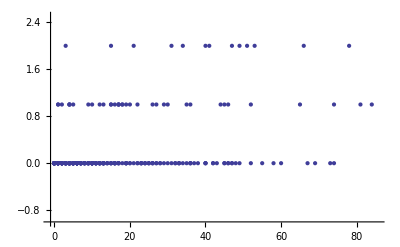

```mathematica
ListPlot[answerVUVDList,AxesOrigin->{-1,-1}]
```

Dist of voteups

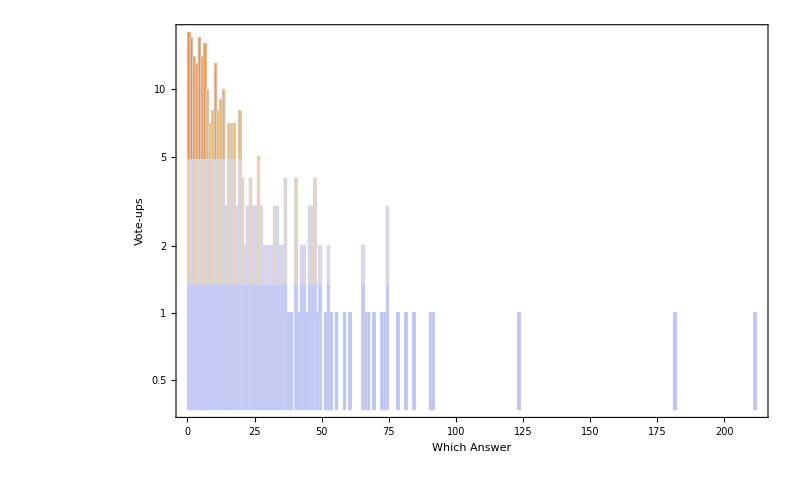

```mathematica
answerVUHis=Histogram[answerVU,Max[answerVU]+2,ChartElementFunction->"GradientScaleRectangle",ScalingFunctions->"Log",Frame->True,FrameLabel->{"Which Answer","Vote-ups"},ImageSize->800]
```

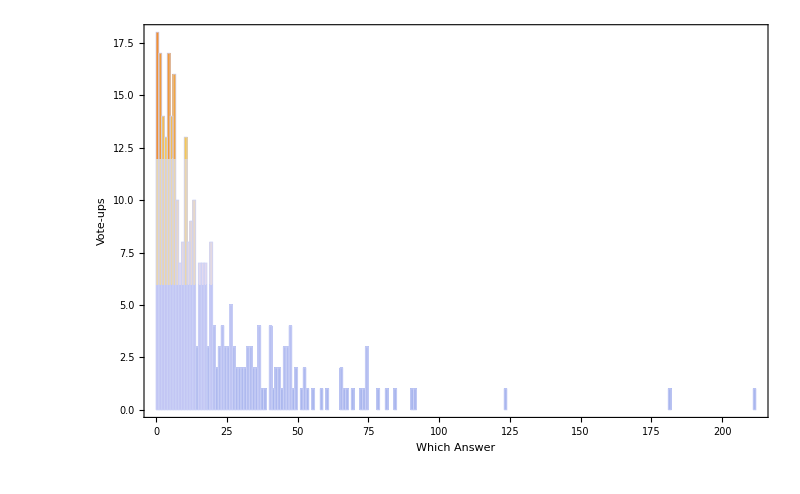

```mathematica
answerVUHis=Histogram[answerVU,Max[answerVU]+2,ChartElementFunction->"GradientScaleRectangle",Frame->True,FrameLabel->{"Which Answer","Vote-ups"},ImageSize->800]
```

```mathematica
answerTableCompleteHead=Grid[{{ImageResize[userIMG,70],Style[userID,30]},{SpanFromAbove,"总回答数："<>ToString[answerURLListLen]<>"； "<>"总支持数："<>ToString[answerSupLen]<>"； "<>"总反对数："<>ToString[answerDownLen]<>"；"<>"平均支持数"<>ToString[answerSupAvg]<>"；"<>"(生成时间："<>DateString[{"Day","-","Month","-","YearShort"}]<>")"}}];
```

```mathematica
answerTableComplete=Grid[{{answerTableCompleteHead},{─},{Style["Hisogram",50]},{answerVUHis},{─},{Style["Answers",50]},{answerTable}}];
```

#### Export Data

Export The Results

```mathematica
answerExpPDF=Export["Export/"<>"USR"<>ToString[userID]<>"_Answers_"<>DateString[{"Day","-","Month","-","Year"}]<>".pdf",answerTable,"PDF"]
Remove[answerExpPDF]
```

Export/USREnt_Answers_29-05-2013.pdf

```mathematica
answerExpCSV=Export["Export/"<>"USR"<>ToString[userID]<>"_Answers_"<>DateString[{"Day","-","Month","-","Year"}]<>".csv",answerGridTable,"CSV"]
Remove[answerExpCSV]
```

Export/USREnt_Answers_29-05-2013.csv

```mathematica
(*
answerExpIMG=Export["Export/"<>"USR"<>ToString[userID]<>"_Answers_"<>DateString[{"Day","-","Month","-","Year"}]<>".png",answerTable]
Remove[answerExpIMG]
*)
```

```mathematica
answerExpVUHis=Export["Export/"<>"USR"<>ToString[userID]<>"_AnswersVUHis_"<>DateString[{"Day","-","Month","-","Year"}]<>".png",answerVUHis]
```

Export/USREnt_AnswersVUHis_29-05-2013.png

```mathematica
answerCompleteExpPDF=Export["Export/"<>"USR"<>ToString[userID]<>"_AnswersCompletePDF_"<>DateString[{"Day","-","Month","-","Year"}]<>".pdf",answerTableComplete,"PDF"]
Remove[answerCompleteExpPDF]
```

Export/USREnt_AnswersCompletePDF_29-05-2013.pdf

## Answer Content

```mathematica
ansConList=ParallelTable[{StringCases[Import[answerURLList[[i]],"Source"],"<h1 id=\"articleTitle\">"~~__~~"</h1>"],StringCases[Import[answerURLListT[[i]],"Source"],"<div itemprop=\"http://rdfs.org/sioc/ns#content\" class=\"answer-txt answerTxt\">"~~__~~"</div>"~~__~~"<div class=\"cmts cmtsBody\">"]},{i,1,answerURLListLen}]
```

{{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">如果只看一个简短的答案：<br />
<br />
<br />
<strong>单从数学上比较数字大小来理解：</strong><br />
<br />
若这个上限指的是所有的可能情况中都不能达到的，那么没有。<br />
<br />
如果这个上限指的是某些体系不能达到的，那么是有的。<br />
<br />
<strong>从物理上来看：</strong><br />
<br />
总会有个上限，而且至少有两种情况的上限。<br />
<br />
<br />
<br />
（如果只想看简短的解释，可以从 为什么要说这么复杂 这部分开始看）<br />
<br />
<br />
=====<br />
<br />
其实如果不理解温度是什么，回答这个问题就会有问题。所以先废话一下，说说温度是什么。<br />
<br />
## 温度是什么<br />
<br />
温度一般是通过热力学来定义的，当然热力学要通过统计物理来看本质。<br />
<br />
热力学定义温度，需要用到第零定律和第二定律，一个给出了最基本的物理意义（平衡和冷热程度），一个给出了定量的描述（可以给出温度标准）。<br />
<br />
<br />
那么冷热程度是什么意思呢？我们常说温度在平衡态的时候从有意义，虽然不尽然如此，但是平衡态下，温度确实有个比较好的定义。为什么呢？因为我们借助于平衡态来定义温度。<br />
<br />
## 冷热程度<br />
<br />
想想我们用温度计来测量一个物体的温度，然后用同一只温度计测量另一个物体的温度。如果温度计都是显示 50 摄氏度，那么我们就说这两个物体都是 50 摄氏度。<br />
那么我们又为什么敢下结论说两个物体的温度都是 50 摄氏度呢？这是因为我们有第零定律：<br />
<blockquote><span style="color: #999999;">若两个热力学系统均与第三个系统处于热平衡状态，此两个系统也必互相处于热平衡。</span></blockquote>
这是一种传递性。<br />
<br />
如果你在夏天的时候跟一个大冬瓜相拥入睡，假设你跟冬瓜达到了热平衡状态。然后你女朋友/男朋友也更这个冬瓜相拥，发现你女朋友/男朋友已经是跟冬瓜答道平衡状态了。这样我们就可以推断你和你的女朋友/男朋友也是平衡状态。<br />
当然，这个道理中，把冬瓜换成温度计，如果你和你的女朋友/男朋友分别跟温度计相拥之后，发现温度计的状态都一样，那么就说明你跟你的女朋友/男朋友那是大和谐了：温度相同，而且处于平衡状态。<br />
<br />
说到这里，有人就想问：<br />
（热）平衡是什么意思？<br />
<br />
热平衡的意思是说，在上面的例子中，你的一部分和你的女朋友/男朋友的一部分交换，或者你给了你的女朋友一部分，或者你的男朋友给了你一部分，从热力学的角度来看，对于这个体系来说，没啥区别。（大和谐嘛）<br />
<br />
那我们如何定量来给出温度的呢？或者温度计背后有着什么样的深刻道理呢？<br />
<br />
<br />
## 温度的定量<br />
<br />
<br />
这个道理就是热力学第二定律。<br />
<br />
这个说起来有点头疼。我试试吧。<br />
<br />
热力学第二定律的最最核心的内容是：<br />
熵是一个状态函数。（熵通常被认为是表示体系的混乱程度的一个量，状态函数的意思是说，熵至于体系的状态有关，而跟如何达到这个状态是无关的。）<br />
<br />
那又如何呢？我们可以通过总结建立起熵和温度的关系式，如果熵是一个状态函数，那我们就可以定量了，因为这样就可以一个温度对应一个状态了。<br />
<br />
（要知道我们给出温度的定量严格的说，需要利用可逆过程。然而这东西说起来就是讲一节课了。）<br />
<br />
我知道我知道，这样说好像很难理解。所以我们还是来看看另一种说法。<br />
<br />
假定你和你的男朋友/女朋友分别是高温的提供热量的源泉和低温的用来冷却的源泉，那么可以利用你们二人的温度差异来对外做功，向外界提供能量。我们可以找到一类理想的特定的过程，这类过程中，你们二人对外做功的效率至于你们二人的温度有关，可以写成<br />
<img src="http://img1.guokr.com/formula/50d20f946797ecbe3bcdfbdc536c989108a1464d.png" class="edui-faked-insertmathjax" data-code="\eta=1-\frac{T_{You}}{T_{TA}}" style="max-width: 480px" /><br />
效率 = 1-你的温度 / 你女朋友/男朋友的温度<br />
<br />
利用这样的跟过程相关的手段，我们可以建立起热力学的温度计量。<br />
<br />
<br />
## 为什么要说这么复杂<br />
<br />
上面这两部分，主要是说明热力学里面温度确实是跟组成物理的粒子的混乱程度或者这些粒子运动的状态有关：物体运动越剧烈，温度就越高。<br />
<br />
那么剧烈程度是什么意思呢？在物理上将，这个是指的分子的动能。动能大的粒子越多，温度就越高。<br />
<br />
那么如果运动太剧烈了呢？会触及到相对论的情况么？<br />
<br />
答案是会的。<br />
<br />
<strong>在广义相对论课上，基本上会有这样一个习题，就是问，能量密度多大会变成黑洞。这个是可以算的。</strong><br />
<strong>也就是说，一个区域内的能量太大，会导致能量密度太高，这样就是黑洞了。这样体系就变成了另一种描述，不是原来的体系了，所以我们说，原来那个体系，所能达到的最高的温度是有个上限的。</strong><br />
<br />
<br />
## 为什么是运动的剧烈程度<br />
<br />
为什么温度是用分子的运动的动能来衡量的呢？起初看来这个问题像是牛角尖。但是仔细思考之后，会发现一个更深刻内容。（进入统计的领域）<br />
<br />
我们上面提到了温度和熵有关系，他们可以这样写出来：<br />
<img src="http://img1.guokr.com/formula/01cc3b8141b83773530475028310f4878cd2b3fe.png" class="edui-faked-insertmathjax" data-code="\frac{1}{T}=\left(\frac{\partial S}{\partial U}\right)_{Y}" style="max-width: 480px" /><br />
<br />
温度的倒数 = 熵对内能的偏导数<br />
<br />
公式没什么用，这个公式只是告诉我们，温度是随着体系混乱程度跟随体系内能的变化快慢相关的，如果体系的混乱程度不随体系的内能变化的时候，也就是右边变成了 0，那么温度就到了无穷了。<br />
<br />
对于我们通常想到的情况，也就是体系的内部能量是通过分子的运动来体现的情况，因为体系内能越大，就越混乱（状态数越多），这个非常合理，温度永远大于零。（这个最本质的原因还是因为玻尔兹曼统计）只是如果太极端，这个会遇到相对论的限制，达到一个上限。<br />
<br />
哎呀，我们忽略了量子的情况。也就是说，如果内部的能量不是通过这种连续的分子的运动来实现的，而是每个例子只有两种可能的能量状态。那么这时候，就需要另外考虑了，假定我们可以用手摆出一种状态，这种状态里面，能量高的粒子要比能量低的例子多，这样当我们去增加体系内部的能量，也就是去把能量低的粒子放到能量高的位置上的时候，会发现，体系的混乱程度是减小的（状态数的减少），如此一来，这个体系的温度就会变成负的。而可以想到，在正和负的交接处，我们可以用手摆出温度为无穷的情况。<br />
<br />
或者，不去理解这个现象，只作为知识记住的话，应该看一下下面的图：<br />
<img src="http://img1.guokr.com/image/YVk4HWbsod_vOOPqaCLH3CzEcs7LAGU0EtKmwCh-OWjCAQAALQEAAFBO.png" style="max-width: 480px" /><br />
（汪志诚老先生<a href="http://book.douban.com/subject/1130137/">《热力学·统计物理》</a> 第三版，P285 ）<br />
<br />
不管这个图的横轴，只需要知道，温度从低到高的顺序是：<br />
+0 -&gt; 正无穷 -&gt; 负无穷 -&gt; -0<br />
<br />
这样说，温度也有个上限。<br />
<br />
<br />
<br />
## 总结<br />
<br />
总之，不论如何，温度总会有个上限，不同的是，有两种情况：<br />
一种是受到相对论对能量密度的限制<br />
一种是完完全全的统计给出的，普适的，无条件的上限。<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">一个物体降落的时候受到的空气阻力（在速度比较快的时候）可以用<br />
<img src="http://img1.guokr.com/image/NulIo9iXqx14iHpZiAWCxanaQvo3dxIgWv83UlQVJ6NlAAAAIgAAAEdJ.gif" style="max-width: 480px" /><br />
 来估算。其中<img src="http://img1.guokr.com/formula/ee9f9fbaf7df598b3a7061b8b9d1f09070310028.png" class="edui-faked-insertmathjax" data-code="\rho_{\text{air}}" style="max-width: 480px" />是空气密度，大约为 1.22 kg/m^3， <img src="http://img1.guokr.com/formula/a60e47bd8ea9669acc84ab6e3929a7c2089dfd4d.png" class="edui-faked-insertmathjax" data-code="C_d" style="max-width: 480px" />是用来表征物体形状的一个系数，降落伞的话是大致取 0.75，因为降落伞实际上有效的投影面积乘上降落伞形状带来的因素差不多是这个值，但是我们的床单可能是需要取在 0.6~0.8之间，具体情况需要一些更详细的推导。A是床单的面积，展开面积。<br />
<br />
但是速度比较小的时候，物体下落的时候空气阻力可以用 b A v 来计算，并且我们有：<br />
机翼那种形状的 0.2，球形的 0.5，平板是1.28<br />
不过鉴于窗帘床单这些东西形状诡异，阻力较大，所以速度平方的估计应该更准确些。<br />
<br />
## 初步观察<br />
<br />
只是抛砖引玉，让大家感受一下跳楼的危险性吧。这里先假定体重是 50kg。（大家都来减肥吧……）<br />
<br />
<br />
使用速度平方的形式，如果下落的距离很远，下落终将达到稳定速度。我们先来看看这个最终的稳定速度会是多少。<br />
如果取 Cd=0.5<br />
<img src="http://img1.guokr.com/image/EedDZa5T4UMKGlxxS0HBnbW4RJkGaHdK1SsukqMv7a4uAQAALgAAAEdJ.gif" style="max-width: 480px" /><br />
<br />
如果取 Cd=1<br />
<img src="http://img1.guokr.com/image/DpfwElUGVTx3cJG9VMzqP14QFu82AcmyuA0u6NZsMtkzAQAALgAAAEdJ.gif" style="max-width: 480px" /><br />
<br />
如果取 Cd=0.75<br />
<img src="http://img1.guokr.com/image/syM9gYYzdQGMngVKosY5Jt1G6l66abcq4qhumzCJT34nAQAALgAAAEdJ.gif" style="max-width: 480px" /><br />
<br />
这样我们就可以计算了。把图画出来，如下。三条线分别是 Cd =0.5，0.7，0.8 的情况。也就是不同的床单/窗帘形状影响下，最后稳定的速度和窗帘/床单面积的关系图：<br />
<img src="http://img1.guokr.com/thumbnail/7uNe1e71c6BwstRdzwqcFIRONr9FyY79YgcayJSk5PxhAgAAowEAAFBO_480x330.png" style="max-width: 480px" /><br />
<br />
基本上，用单人床的床单，往最好的情况想，2*2 平方米这么大的，弯曲不是很厉害，差不多保留一大半的有效面积，落地后的速度在十几米每秒这样。这比被五六十千米每小时的车撞还严重。<br />
<br />
上面这只是给大家看看，下面我们要具体的计算一下。为什么要计算一下呢，因为实际上我们上面给出的是很久之后的速度，一般是十几，几十秒之后才能达到这样的速度。在很多时候，对于那些我们敢跳的楼层，跳楼过程基本上在两秒内完成了……<br />
<br />
<br />
<br />
<br />
<br />
## 详细的计算<br />
<br />
实际上我们可以直接把速度解出来。中间的过程这里就省略了，详细的看我末尾给的程序。<br />
<br />
最后我们可以得到这样一张图：<br />
<img src="http://img1.guokr.com/thumbnail/6avnTRTHq2SzduDSHQgoDm-F9nl070w7EGATj_Dw241wAgAAjwEAAFBO_480x306.png" style="max-width: 480px" /><br />
<br />
<br />
红蓝绿橙黑，分别是面积为1，2，4，9，16的情况，这里近似认为使用床单是 Cd=0.7。最上面那条黄线是自由落体……<br />
<br />
这样看来，基本上，如果床单面积达到了16平米，那就问题不大了，从哪里跳下来都还算安全。不过想想那得多大的床单……<br />
<br />
对于9平米的床单，也还可以，看橘色的线，问题也不大，最多 10 m/s 的样子，姿势正确似乎也不会很致命，就像百米冲刺的速度撞墙，唔，好疼。<br />
<br />
而对于我们的正常的床单， 面积最大在4平米左右，看绿色的线，在20米左右的高度的楼房上跳下来，会达到17米每秒，这样很危险了，不过总比没有床单好，因为没有床单会达到 20 m/s。<br />
<br />
如果床单的面积在 2 平米左右（1*2，单人床的各位），这时再跳就危险了，如果房子足够高，例如达到了50米的高度，最后速度可以达到25米每秒，比被90多千米每小时的车撞还厉害。当然我们的房子大多每那么高，例如在20米高的地方跳下来，那速度也会有18米每秒。危险。<br />
<br />
还可以注意到，对于那些那些1或2平米的床单，在10m之内跳楼都基本不起作用，跟直接跳下来也差不了多少。<br />
<br />
而且这些是最理想的情况，具体最大效果需要把床单最大程度的展开。这上面估算的情况是让床单像降落伞一样弯曲的时候，如果能够让床单整个平整的展开，拖拽效果更好些，不过这时候需要注意稳定性。<br />
<br />
以上换成窗帘同样成立，窗帘更大些。<br />
<br />
<br />
<br />
<br />
<br />
## 其它体重的情况<br />
<br />
我们来看看看体重的影响。为了简便起见，我们使用 Cd=0.7，A=4或9（窗帘的面积吧）。<br />
<br />
<img src="http://img1.guokr.com/thumbnail/aucr-4Q3uxqvX5Enbjghazp4msN0tusqFDC1RDOoglIOBAAAtgIAAFBO_480x320.png" style="max-width: 480px" /><br />
<br />
红蓝绿橙黑分别是体重为 10kg,25kg,50kg,70kg,100kg 的情况。实线是窗帘面积为4平米，虚线是窗帘面积为9平米。黄线还是自由落体。<br />
体重在这里扮演了很重要的角色。如果是一个小孩子，体重 10kg，那么 9平米的窗帘甚至可以让小孩子以 5m/s 以下的速度落地。但是如果体重达到了 100kg，那么即便是 9 平米的窗帘也不安全，因为速度达到了 15m/s 的。<br />
其它想要知道的可以从图中读出来。但总体而言，这个问题里面体重很重要，越是轻的人，落地速度越小，尤其是从比较高的地方跳下来的时候。<br />
<br />
<br />
<br />
<br />
<br />
-----<br />
（分享改变世界，本答案所使用的程序在此：<a href="https://github.com/emptymalei/WhyMathematica/blob/master/Physics/FlyingWithABedSheet.nb">https://github.com/emptymalei/WhyMathematica/blob/master/Physics/FlyingWithABedSheet.nb</a> ）</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">（最近太阳比较活跃啊，所以大家应该挺关心这类东西的。所以我自问自答总结一下吧。）<br />
<br />
可能有人对太空天气不是很了解，所以我顺便把维基百科的太空天气词条摘录一部分放在这里：<br />
<strong>维基百科：</strong><a href="http://zh.wikipedia.org/zh-cn/%E5%A4%AA%E7%A9%BA%E5%A4%A9%E6%B0%A3"><strong>太空天气</strong></a><br />
<blockquote><span style="color: #999999;">太空天气是在地球周围的太空环境条件改变的观念。它与行星大气内的天气观念不同，涉及太空中的等离子、磁场、辐射和其他物质。"太空天气"经常隐藏性的意味着在地球附近的磁层，但是它也是在 星际间（并且经常是星际空间）的研究。</span></blockquote>
<br />
-----<br />
<br />
<strong>果壳问答已经有了不少关于太空天气的好问答了：</strong><br />
<br />
<a href="http://www.guokr.com/question/274232/">X1.4级耀斑是什么？</a><br />
<br />
<a href="http://www.guokr.com/question/104383/">太阳耀斑对地球会有什么损害呢？</a><br />
<br />
<a href="http://www.guokr.com/question/428904/">怎样浅显易懂的解释太阳风？</a><br />
<br />
<a href="http://www.guokr.com/question/111996/">微博上说“近5年来最强太阳风暴袭击地球”，是说5年前有更强的一次的意思吗？</a><br />
<br />
（2012年）<a href="http://www.guokr.com/question/111855/">3月8日太阳风暴袭击地球了？大家住的地方有异状吗？</a><br />
<br />
<a href="http://www.guokr.com/question/400880/">美宇航局宣称2013年地球上将发生最严重的太阳风暴，届时地球上所有的电子设备将全部不能使用， 人类历史或发生大倒退。这种说法的科学依据是什么？</a><br />
<br />
<a href="http://www.guokr.com/question/229549/">人眼能看到太阳风暴么？</a><br />
<br />
<a href="http://www.guokr.com/question/393515/">太阳黑子会影响人的情绪吗？</a><br />
<br />
-----<br />
<br />
<strong>另外，果壳问答还有一些正在讨论的相关问题：</strong><br />
<br />
<a href="http://www.guokr.com/question/324040/">据说在即将到来的超级太阳风暴中会产生大量磁化粒子，会使银行卡之类的东西磁化吗？</a><br />
<br />
-----<br />
<br />
来讨论有关太空天气（太阳风暴等等，甚至耀斑、黑子等活动）：<br />
<strong>标签：</strong><a href="http://www.guokr.com/ask/tag/%E5%A4%AA%E7%A9%BA%E5%A4%A9%E6%B0%94/discussing/"><strong>太空天气</strong></a><br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">（我来画个小图画，增加大家对这个问题的认识。）<br />
<br />
<img src="http://img1.guokr.com/thumbnail/SjASk4O_7hfMHH7SMmLfoHFSRCm4_UdgQn1lX_f0bSFYAgAAngEAAFBO_480x331.png" style="max-width: 480px" /><br />
<br />
这张图画出了前 100000 个素数相邻的两个之间的差值。也就是说，画出了<br />
第二个素数 - 第一个素数，第三个素数 - 第二个素数，等等等<br />
3-2, 5-3, 7-5, 11-7, 13-11, 17-13, 19-17, 23-19, 29-23, .......<br />
<br />
横轴表示第几对差值，纵轴表示差值的大小。<br />
<br />
从图片里面我们大致猜到，虽然相邻素数之间的差值会出现越来越大的情况，但是那些比较小的差值却没有消失。（看图中比较接近横轴的这些点一直有，没有出现明显的空当）<br />
<br />
那么我们很自然的会猜想，<br />
<blockquote><span style="color: #999999;">存在无穷多个素数 p，使得 p,p+2k </span><span style="color: #999999;">都是素数。</span></blockquote>
（<a href="http://www.guokr.com/n/Obliviou_s/">@Obliviou_s</a> 和<a href="http://www.guokr.com/n/MathChief/">@MathChief</a> 的答案）<br />
k 是任意正整数。<br />
<br />
<br />
<br />
<br />
<blockquote></blockquote></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">（我试着写写）<br />
我们在经典力学中就开始接触作用量了，从经典力学里面的三种表述方法，到量子力学的三种表述方法，作用量现身的频率可谓不低。<br />
那么什么是作用量？<br />
作用量是一个很特殊的量。要理解作用量是什么，需要从最小作用量原理出发，我们甚至应该把作用量定义成满足最小作用量原理的那个量，因为我们没有对作用量的严格定义，只是通过经验或者对称性等等来猜测作用量的，到底是不是真的有用的作用量，需要使用最小作用量原理来验证。<br />
所以作用量，就是那个满足作用量原理的 cost，一种代价，经典力学中，就是从一点到达另一点所花费的代价，而自然界要求，我们的这个代价要最小。<br />
<br />
## 经典力学<br />
<br />
经典力学有三种表述方法，分别是 Euler-Lagrange 方程，Hamiltonian 正则方程以及 Hamiltonian-Jacobi 理论。这三种理论中，Euler-Lagrange 方程和 Hamiltonian-Jacobi 理论都需要用到作用量。那么作用量在经典力学中，是什么意思呢？<br />
<br />
### Action Principal<br />
<br />
作用量原理是拉氏形式中最核心的内容。在这里，作用量是拉氏量在时间上的积分，<br />
<img src="http://img1.guokr.com/image/7adWqY7f_lrsImydnBN8z2cuKfzUn9nCtAquslOqUC3bAAAAJgAAAEdJ.gif" style="max-width: 480px" /><br />
也就是说，拉氏量是时间t，广义坐标q(t)，广义坐标对时间的导数q’(t) 的函数。但是作用量却只是广义坐标q(t)的函数。<br />
我们先不管作用量原理，先看看这个作用量到底是什么意思。在一个保守力系中，拉氏量可以写成动能减去势能<br />
L=T-V<br />
那么作用量就是<br />
<img src="http://img1.guokr.com/image/z5ctGFkIrQT9JMVrt7wffyAnbqbll-Uem7AWEp3ZPABzAAAAJgAAAEdJ.gif" style="max-width: 480px" /><br />
这个很有趣。当我们选定一条路径之后，例如我们选定一个经典路径之后，作用量就是动能和势能对时间的曲线之间的面积。这样说起来太抽象，我们可以看一个自由落体运动的例子（从 x=0 开始沿 x 轴负方向下落）：<br />
<img src="http://img1.guokr.com/image/rVUivNbEa2IPzNlNslktT2X5TLs4_hH4ptfgmBlKUQl8AAAAJgAAAEdJ.gif" style="max-width: 480px" /><br />
<img src="http://img1.guokr.com/thumbnail/2tPL9zv3Jhkgk99NlvmVCHQDoeL_FRAhVzt91C4EMCpYAgAAwwEAAEdJ_480x360.gif" style="max-width: 480px" /><br />
为了方便假定质量 m 为 1，那么如果我们选定经典轨道，那么就可以把动能和势能随着时间的变化关系画出来。<br />
（经典轨道中，动能 T=(m g^2 t^2 )/2，势能 V= - (m g^2 t^2) /2 ）<br />
<img src="http://img1.guokr.com/thumbnail/6kUZWS9bSxxeuibYUVm2-iI9WNRNuNHKCK9HdfdYhLlxAgAAmQEAAEdJ_480x314.gif" style="max-width: 480px" /><br />
所以，对于这条经典路径，上面的阴影部分面积就是我们的路径积分的结果，即动能和势能的能量差值在整个时间上面的积分。<br />
那么如果我们不是选取的经典路径呢？比如我们选取了这样一条路径：<br />
x(t)=-g(t+1)^2<br />
那么相应的，这条路径上的作用量就是对下面这个量在时间上的积分：<br />
T-V = 2 g^2 (t+1)^2 - (- g^2 (t+1)^2)<br />
不过在在这之前我们先写一个初步的用来绘制作用量的函数。<br />
<br />
<br />
<img src="http://img1.guokr.com/thumbnail/6zmHFT8yfpFhYXMpMCFLFUnDzgCL47VMxwG6oqXbFCpxAgAAmQEAAEdJ_480x314.gif" style="max-width: 480px" /><img src="http://img1.guokr.com/thumbnail/RubmAwQ1wz0P9tX87vemtMbE5AbECgHbnC_sbukuZ0RxAgAAmQEAAEdJ_480x314.gif" style="max-width: 480px" /><img src="http://img1.guokr.com/thumbnail/bk5UHuTYLOD0LiLtPd8KlT9Q-S_ut_pjcV5iSb8eX4lxAgAAmQEAAEdJ_480x314.gif" style="max-width: 480px" /><br />
<br />
作用量就是阴影区域的面积。似乎看不出来。这种分析方法不理想。我们还是用数值算算吧。<br />
<img src="http://img1.guokr.com/thumbnail/2x5DF5Oh4HQPcUsFUgEMwqyjYAxqz9zCv9fkgkj-ckO2BAAARgEAAEdJ_480x129.gif" style="max-width: 480px" /><br />
<img src="http://img1.guokr.com/image/sROnk0xFzbJH1NmqdnIUQjLaCtFcrqN4Abux_pxX8i87AQAAEgAAAEdJ.gif" style="max-width: 480px" /><br />
<img src="http://img1.guokr.com/image/UE919-ymjcXnQTC7vQZFAdCSW5tsjFZUn5lYri174SAyAQAAEgAAAEdJ.gif" style="max-width: 480px" /><br />
从面积数值来看，选定的新路径下面作用量变大了。<br />
实际上大家可能注意到了，在作用量原理里面，我们所需要的基本假设少的可怜，我们连量纲、甚至能量守恒都不需要事先考虑（上面的例子中，新路径的能量不守恒，从图片里面上下部分不对称可以知道），只需要承认作用量原理，我们几乎获得所有的规则。这就是为什么作用量原理会显得更加基本。但是这也是很大的问题，从经典力学里面，我们似乎看不到为什么我们需要一个这样的原理，或者说，我们只知道这个原理起作用，但是并不是很明白为什么会有这个原理以及这个原理意味着什么。<br />
从上面的保守力系的例子来看，最小作用量原理似乎要求整个过程中，动能和势能的相互转化要最小，否则会导致作用量变大。<br />
为什么呢？<br />
如果我们让能量转化的更多些，那意味着大的动能，或者说更高的速度，因此就意味着会用更少的时间来从起点到终点。<br />
（原本是想尝试用例子来把问题看得更清晰，但是这里我并没有找到一个足够好的方法来展示这个原理的内涵。这部分说的好失败。我再试试量子的情况。）<br />
<br />
<br />
## 关于力学体系<br />
<br />
下面本来是要说一下量子里面的作用量的，但是在这之前，可以先来看看力学体系里面的不同的形式。先来一个表格。<br />
<br />
经典 量子 <br />
最小作用量原理 路径积分 <br />
哈密顿正则方程 波动力学，矩阵力学 <br />
哈密顿-雅克比 路径积分 <br />
<br />
这里面最基本的应该是经典力学的作用量原理和 Euler-Langrange 方程，或者量子里面路径积分的形式。量子力学的路径积分形式比经典力学的作用量形式更近了一步。经典力学知识说，就是有这样一条路径是对的，粒子就要走这一条。但是这让人很奇怪，为什么要走这一条？当然，有个法国朋友说，物理不能问为什么，只能尝试去解释怎么工作。量子力学里面的路径积分的想法更近了一步。<br />
<br />
<br />
## 量子<br />
<br />
在量子世界中，似乎作用量的“意义“要更容易明白些。在路径积分理论中，位形空间中的传播子可以看做是（当然严格的要写成积分的样子，这里只做一个简单的意义上的呈现）<br />
<img src="http://img1.guokr.com/image/d0bMoOr0w5_sGH_JHsAPLOmiy8ZUW5hJFufgT7_hf-WDAAAAGwAAAEdJ.gif" style="max-width: 480px" /><br />
<br />
传播函数是说，如果我们知道波函数的初态。那么可以通过传播函数来把波函数演化到下一步，与光学里面的惠更斯原理很像，虽然每条路都是等概率的，但是因为我们有个相因子S/h，所以实际上，作用量的作用就是体现每条路径的比重/重要程度。所以上面的传播函数的形式来看，经典作用量S扮演了一个很核心的作用。<br />
<br />
当然，在量子力学的传播函数的积分中，作用量S也连接了量子和经典这两个不同的研究范畴。因为经典作用量S很大时，几乎只有经典路径附近的路径才起作用，所以体系的性质也趋于经典。<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><strong>夸克禁闭：</strong><br />
<br />
要想分离开两个禁闭的夸克，需要外界给这个体系提供能量，然而要想分开两个夸克是需要如此高的能量，以至于外界添加的能量，根据E^2=m^2c^4 + p^2c^2，这部分能量足以在两个分开的夸克之间形成新的一对夸克。如此以来，新的夸克又和原来的组成了两对禁闭的夸克。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><strong>易燃的液体的烘干</strong><br />
<br />
=====<br />
<br />
当年还是嫩嫩的本科生，勾搭了一个教授跟着做实验：陶瓷相关。<br />
<br />
那年夏天，我和两个哥们还要上课，所以需要利用早上上课之前的时间去做点样品。<br />
<br />
我们取得很早，实验室没有其它人，于是我们秤量样品，把各种粉末按照比例混合，在粉末中加入酒精，用球磨机磨碎，用烘箱把液体烘干。<br />
<br />
原本以为，顶多就是会有粉尘，因为会用高速球磨机把原料磨成微米量级的粉末，所以我们都会戴口罩。<br />
<br />
但是后来事故之后，才突然想到，我们用烘箱烘干带酒精的东西？那烘箱得有特殊要求啊？<br />
<br />
我们用的普通的烘箱。<br />
<br />
这天早上，我们把带酒精的粉末放进了烘箱，然后在隔壁小屋清洗容器。<br />
<br />
烘箱爆炸了。烘箱门被整个炸了下来，高速冲击到对面的桌子上，十几厘米厚的烘箱门从中间折弯了。屋顶上有什么东西陆续掉下来。<br />
<br />
大家来到实验室之后，基本上都会到烘箱去取东西，总之烘箱前面人会很密集，如果我们稍稍晚十几分钟，爆炸的时候烘箱前面有人，那必然是活不了了。<br />
<br />
（所幸桌子上的玛瑙研钵没有摔下来。）</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">这里有：<a href="http://visualizing.org/datasets/meteorite-landings">Meteorite Landings</a><br />
<br />
里面给了一个 Google Fusion 表格，一个 XLSX 表格。数据包括：<br />
<br />
地点名称，类型，质量，是否找到，那一年，数据来源，经纬度等等一些其它的信息。<br />
<br />
上面是数据，还有可视化（点开链接看交互界面）：<br />
<br />
<a href="http://visualizing.org/visualizations/bolides">http://visualizing.org/visualizations/bolides</a><br />
<img src="http://img1.guokr.com/thumbnail/tvoI7nyRi99s1cZXXSu1UZrooqe0bTvQrUrjv3wiQAivAwAAYAIAAFBO_480x309.png" style="max-width: 480px" /><br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">这种说法有点偏颇。但问题不大。初步结论是对于比较薄的布料一般而言红色蓝色都可以，越深越好。<br />
<br />
我把思路理一下。<br />
<br />
<strong>1. 颜色（单色）与光波波长</strong><br />
<br />
我们得先看看颜色（单色）到底是对应什么波长的光。<br />
<br />
<img src="http://img1.guokr.com/image/ZH8etOboffhXjM3XuoDm5jj2bbhDvJU792X0Df-eQhTHAQAAXQEAAFBO.png" style="max-width: 480px" /><br />
（<a href="http://zh.wikipedia.org/wiki/%E9%A2%9C%E8%89%B2#.E7.89.A9.E7.90.86.E7.9A.84.E7.8F.BE.E8.B1.A1">http://zh.wikipedia.org/wiki/%E9%A2%9C%E8%89%B2#.E7.89.A9.E7.90.86.E7.9A.84.E7.8F.BE.E8.B1.A1</a> ）<br />
看那个色彩条。蓝色紫色对应的光波长要端些。那紫外线在什么位置呢？<br />
<br />
<img src="http://img1.guokr.com/thumbnail/xmUpuFUgqb61iNZREgOVBq6VD3j0z-IkVdCsiO0-1o9zAwAA2AIAAEdJ_480x395.gif" style="max-width: 480px" /><br />
（<a href="http://rocoes.com.tw/2008c/wave.htm">http://rocoes.com.tw/2008c/wave.htm</a> ）<br />
<br />
紫外线在蓝色紫色的左边。也就是波长更短，而且靠近紫色和蓝色。<br />
<br />
<strong>2. </strong><strong>衣服的颜色</strong><br />
<br />
我们看到的衣服的颜色布料反射某些光的结果。例如如果布料吸收/投射了所有的除了 700nm 之外的所有光，那么我们就会看到红色的布料。（喂，这布料这么好，拿来做光过滤吧。好吧其实大部分的情况是不同程度的对某些有吸收或透射，剩下的不同程度的反射，比较麻烦。）<br />
<br />
一般的材料的光波的吸收是有个范围的。例如对 400nm 左右的光反射比较多，这意味这对 380nm，420nm 这些光的反射也不差。所有说，如果我们看到紫色的布料，那这布料对紫色这部分反射比较好，同时一般也意味着对紫色周围的，比如蓝色，靠近紫色的紫外也会反射不少。<br />
<br />
<strong>3. 我们人体接受的紫外线</strong><br />
<br />
但是我们人体接受到的紫外线是透过布料的。所以说，我们需要知道哪种布料中，紫外光的透射能力最差，这才是最好的。<br />
<br />
我们仅仅通过衣服的颜色来判断是不容易的。为什么呢？因为反射，吸收，投射之间的关系并不固定。透射很大程度上跟衣服的纺织工艺有关，例如穿了丝袜或白纱裙（？这是什么），紫外就更容易透过去，因为这种纺织方法留了很大的空隙。<br />
对于足够厚的衣服，反射和吸收倒是有些关系，例如反射的多，吸收的少，因为总能量守恒嘛。<br />
不过对于薄的衣服，变量实在太多了。不好判断。总之肯定是越厚越好，越密集而织法越好；例如Twill 织法（ <a href="http://en.wikipedia.org/wiki/Twill">http://en.wikipedia.org/wiki/Twill</a> ）的布料也会对紫外线有比较好的屏蔽，或者牛仔布……<br />
<br />
如果我们不管其它变量，只管衣服颜色呢？<br />
<br />
<br />
<strong>4. 衣服颜色与紫外线透过的关系</strong><br />
<br />
不同的染料对紫外线的吸收反射也不同。（求数据）<br />
<br />
好吧，不饶舌了。就看看这一个变量吧。<br />
<br />
这个居然有篇化学的论文：<a href="http://pubs.acs.org/doi/abs/10.1021/ie9006694">http://pubs.acs.org/doi/abs/10.1021/ie9006694</a><br />
<br />
论文做了一些实验，就只说论文的结论吧：<br />
<br />
如果不考虑其它因素，可以认为红色和蓝色要比黄色对 UVB （中间波段的紫外光，对人的伤害最大）的防护更好些。而且颜色越深越浓，防护越好。<br />
<br />
（擦，大夏天的穿个深蓝色的么……）<br />
<br />
话说这样把结论写出来估计作者看到会揍我……<br />
<br />
<br />
<br />
<br />
<br />
------ 请忽略以下 -----<br />
<br />
<br />
<strong>5. 但是</strong><br />
<br />
（我觉得说但是的时候，就是最黑最爽的时候。）<br />
<br />
按照维基百科的说法（<a href="http://en.wikipedia.org/wiki/Sun_protective_clothing">Sun_protective_clothing</a> ），棉质，亚麻，麻这些自然织物，以及聚酯，尼龙，莱卡（==！，不是那个莱卡）这样的材料的织物以及对太阳光的紫外线有了很好的防护了。就大部分上班族在外面待的那部分时间，选个好看的颜色凉爽些让日子开心些是不是更好呢~再说大家不都是有太阳伞的么~<br />
<br />
<br />
<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><a href="http://zh.wikipedia.org/wiki/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84#.E5.90.84.E5.9B.BD.E5.AE.B6.E5.92.8C.E5.9C.B0.E5.8C.BA.E6.B3.95.E5.AE.9A.E7.BB.93.E5.A9.9A.E5.B9.B4.E9.BE.84">各个国家的法定结婚年龄在 Wikipedia 有数据</a>，不是最新的，而且不全，不过已经很多了，我们可以拿来分析一下。<br />
<br />
Wiki 一共给了 109 个国家的数据，其中有 7 个国家是给的不确定的年龄，包括各地不同或者两个年龄，这类我们都剔除掉了。<br />
<br />
然后我们可以看剩下的 102 个国家的法定结婚年龄的分布。上图是男性的，下图是女性的。<br />
<br />
<img src="http://img1.guokr.com/thumbnail/-7Cm4pziVihNStXz6rd4v6ykNs2MyHGz6D6GZXNoN7X0AQAAqQIAAFBO_480x653.png" style="max-width: 480px" /><br />
<br />
上面是法定结婚年龄的 Histogram 分布。可以看到女性的法定结婚年龄要普遍低些，但是不管男女法定结婚年龄都在 15 岁以上（维基列出的可以用的102个国家的数据中），男性的最高结婚年龄在 22 岁，不幸的是，这近有的一个高年龄男性法定结婚年龄就是我们大陆，大陆的女性法定结婚年龄 20 岁虽然偏高，但不算最高。<br />
<br />
（这是一个值得问的问题，为什么女性的法定结婚年龄要普遍低些？）<br />
<br />
<br />
然后我们可以看下面的图：我把所有的 102 个国家的法定结婚年龄用点画出来了，蓝色是男性的，粉色是女性的。（这里男女没有对应关系，是分别按照从大到小排列的。）<br />
<br />
<img src="http://img1.guokr.com/thumbnail/tQ2tcqcaO3StOY6t8DqeMTZQlxy5FMtQucdlQVukbEn0AQAARwEAAFBO_480x313.png" style="max-width: 480px" /><br />
<br />
然后上面的点线，蓝色是我国大陆男性的，粉色点线是我国大陆女性的。这样一眼就可以看出我们的法定结婚年龄确实偏高。<br />
<br />
<br />
（分享改变世界，<a href="https://github.com/emptymalei/WhyMathematica/tree/master/DataVisualization/Other/MarriageableAge">Mathematica源代码</a> ）<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">（Fe 以后的元素是产生的途径不是单一的，也不是单单由超新星爆发产生的。）<br />
<br />
<br />
如果我们要产生一个原子序数更高的新的元素，那么我们有什么办法呢？或许我们可以<br />
1. 把核内的中子「换成」质子<br />
2. 把质子打进原子核。<br />
<br />
<br />
## 中子捕获 + Beta 衰变<br />
<br />
第一条路看起来挺容易的，因为我们有个 beta 衰变，其中有一类是中子变成 质子+电子+反电子中微子（电荷守恒，轻子数守恒），<br />
<img src="http://img1.guokr.com/image/my_ifKulzHJrjwoFXTFLT2mm7ZyaM-agpwjl7Qtr1qPcAAAAlgAAAFBO.png" style="max-width: 480px" /><br />
（来自维基百科：<a href="http://zh.wikipedia.org/wiki/%CE%92%E8%A1%B0%E8%AE%8A">http://zh.wikipedia.org/wiki/%CE%92%E8%A1%B0%E8%AE%8A</a> ）<br />
<br />
所以说，如果原子核发生了这样的一个过程，对应的元素的原子序数就会增加。正合我们意图。但是，原子核好好的为什么要衰变呢？<br />
<br />
所以我们需要构造不稳定的同位素，这样一般需要增加中子数目，也就是要发生中子捕获。<br />
<br />
超新星正好为我们提供了这样的环境，因为这个过程中有非常非常强大的中子流。中子流密度足够大了，所以中子会和原子核发生核反应（类似于化学平衡），最后会形成原子量非常大的一些同位素，而这些同位素不稳定，发生 beta 衰变，使得元素的原子序数增加，这就意味着产生了比铁的序数更大的元素了。<br />
这个过程，就是我们所说的快中子捕获（R-过程，rapid）。因为这个发生的非常快。<br />
这个过程造就了差不多我们现在一半的比铁重的元素。<br />
<br />
那么必须要有很大的中子流么？事实上不需要。有另外一个类似的过程，叫做慢中子捕获（S-过程，slow），也能够产生比铁靠后的元素。这个过程与上面不同的地方是，不需要特别大的中子流，所以在很多大型恒星中就可以发生。另外由于中子流确实比较小，核反应速率比较慢，不过这个过程，却产生了另外一半的比铁重的元素。<br />
<br />
##<br />
<br />
那么我们有没有可能走第二条路，把质子打进原子核呢？就是说如果我们有比较大的质子流如何？事实是这个过程很难发生，其中一个容易理解的原因是产生重的元素（Fe 之前）需要极端的环境，而极端的环境中电子简并压会出来作怪了，质子密度就很难提上去。（大家知道中子星，听说过质子星么？）<br />
<br />
不过，如果不是在恒星核心发生的呢？例如在高能量的吸积盘中？是的，如果吸积盘这类的环境中有高密度高能量的质子流，这样的过程是可以发生的。<br />
<br />
这样的过程，就是质子捕获，其实是快质子捕获过程。<br />
<br />
<br />
## 重元素核被光子打出核子<br />
<br />
如果我们先由上面的两种方法产生了重元素，然后有这些重元素来产生稍微轻些的，但是依然比铁重的元素呢？<br />
好主意！<br />
<br />
实际上，这是一个真实存在的问题，不是所有的元素都可以很方便的由上面的两种方式产生。上面的想法是就是类似于上个世纪的一种提议，即，我们高能光子或其它的因素把原子核里面的核子轰击出来，从而形成序数更小的元素。<br />
这个过程就是 p 过程，一般也许有超新星坍缩的极端过程中。不过这个过程不是重元素合成的主要途径。<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">我知道一种方法，但不一定是文章用的方法，就是 PCA， Principal Component Analysis.<br />
<br />
这种方法是一种数据可视化方法里面用来做 Dimensional Reduction 的方法，不一定用来处理图片来找寻相似性，不过当我看到后面的时候，就觉得真是的，计算机和物理什么的，经常有相似之处啊。<br />
<br />
这种方法的关键就是，找到图片所有像素点的相关性的功率谱。我不知道计算机里面叫什么，不过物理里面是叫这个。那么什么是功率谱？在这里，功率谱可以看作是一堆基矢前面的系数（平方）的分布。或者说，如果我们能够把一个量写成<br />
<img src="http://img1.guokr.com/formula/45453fecb697f32f1c0ef9cd30136365ff1a843f.png" class="edui-faked-insertmathjax" data-code="X= C_1 \hat e_1 + C_2 \hat e_2 + \cdots + C_n  \hat e_n" style="max-width: 480px" /><br />
那么我们可以用这个量前面的这些系数来表征它，构成功率谱（严格的说还要平方，不过这里无所谓了）。<br />
<br />
这样我们分析一下，至少需要按照下面的步骤来：<br />
1. 把图像用矩阵表示出来。<br />
2. 算出图像的各个像素点的相关性矩阵。<br />
3. 绘出功率谱。<br />
<br />
第一步最简单，因为我们可以把图片看出像素点组成的，因为颜色在这个问题里面不重要，所以我们就把每个像素点的灰度看出一个值。这样我们就把图片的所有信息在一组基矢上面展开了：<br />
<img src="http://img1.guokr.com/formula/273564e31b0c28045885e716433474f483a15656.png" class="edui-faked-insertmathjax" data-code="\text{Img}= C_1 \hat e_1 + C_2 \hat e_2 + \cdots + C_n  \hat e_n" style="max-width: 480px" /><br />
<br />
为了物理图像更加清楚，我们需要把这个矩阵换成一个更加有代表性的矩阵，即我们要减去这个向量的平均值，从而获得一个图片平均“信息矩阵”。<br />
<br />
然后，我们算出这个矩阵的关联矩阵/相关矩阵（我不知道怎么翻译，两点关联，或者covariant matrix），具体的式子不谢了，看维基百科。<br />
<br />
然后我们求出相关矩阵的本征值和本征向量，这组本征向量就是最好的用来代表图片的一组完备的基矢了，而本征值，就可以用来构建功率谱。<br />
<br />
最好，我们可以把本征值按照从大到小排列在一个 listplot 中，例如：<br />
<br />
<img src="http://img1.guokr.com/image/1LmVyinu0JA375BWRo-SSJb2dUhipK0xDs8j6TK5AEFoAQAA7wAAAFBO.png" style="max-width: 480px" /><br />
（我随便画得，一般也确实是这样，只有前面的那些本征值起作用。）<br />
<br />
<br />
如果把所有的图片的本征值画出来，就能得到图片的相似程度。如果害怕其它因素干扰，可以把图片做处理，去掉背景，去掉头发等等，或者直接 Blur 一下，去掉大部分信息。<br />
<br />
最好我们得到的这个图什么用呢？对比相似程度的时候，我们不需要看 那些本征值很小的部分，因为那意味着这些值扔掉对整个图片影响不大。两个图片的大本征值的部分越相近，说明两张图片的线条就越相似。<br />
<br />
那为什么这种方法起作用呢？因为我们算的是两点关联，如果信不过这种方法，我们甚至还可以算多点关联。知道所有人都觉得有效为止。<br />
<br />
<br />
<br />
-----<br />
<br />
顺便说一下，这类似于宇宙学里面分析宇宙微波背景辐射的方法。<br />
<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">一般有四种常用的方法：<br />
<br />
目视观测<br />
照相观测<br />
无线电观测<br />
异地观测（ 当然最后一种可以不算在观测方法中）<br />
<br />
<br />
------<br />
<br />
目视观测流星时有一种简便易行的方法，称作“计数法”。观测者可以使用录音机或纸张进行记录，记录内容包括流星的大致亮度，以及是否属于群内流星（例如英仙座流星雨或非英仙座流星雨）。这种方法适用于大型流星雨极大时期的观测，如象限仪座流星雨，英仙座流星雨和双子座流星雨。<br />
<br />
你需要决定画图法和计数法到底那一种更好用。如果你想从你的观测中记录下尽量多的流星信息，这个问题的答案就很明显：绘图法。但绘图法有个重要缺点，那就是用于画出流星的时间是“盲段”。如果流星发生频率很高，那么，你就有可能要花费，譬如一半的观测时间来绘图，这样，你的观测结果就变得非常不可靠性了。这种情形常常出现在流星活动高发期，比如 8 月份或 10 月份，以及大型流星雨发生时。<br />
<br />
例如，你想在 10 月份观测，此时有一个大型流星雨——猎户座流星雨，还有两个小型流星雨——金牛座流星雨和ε-双子座流星雨正处于活动期。这样，流星频率就会很高，如果你采用绘图法画出每一颗看到的流星的话，你的观测结果就会无意义。对于这种情况，建议你应该把两种方法结合起来使用。<br />
<br />
对于可能是小型流星雨的所有流星，你应该使用绘图法，而对于很明显是猎户座流星雨的流星和偶发的流星，你应该按照大型流星雨的观测要求使用计数法。也就是说，你应该在保持眼睛盯着天空的情况下把后者的数据记录到磁带上（或写在纸条上），而把前者的数据画到图上。使用这种办法可以大大减少“盲段”而仍能够对小型流星雨进行高精度的记录。<br />
<br />
当你每小时能看到超过 20 颗流星时，你应该只对那些可能属于小型流星雨的流星（即群内流星）进行绘图，其它的流星只需计数即可。请注意，在大型流星雨接近开始与结束的一段时间，流星产生频率也是很低的，你也应该把它当作小型流星雨进行观测记录。<br />
当每小时流星量不足 20 颗时，你应该对每一颗流星进行绘图。而当频率超过每小时 50 颗时，你应该只关注那些大型流星雨的流星，正是它们导致了流星高峰期。<br />
<br />
但是目视观测发其实有很高的难度，因为需要判断很多周围天体的信息，然后才能写出报表。不过这也是一种最基本的方法。<br />
<br />
我的一个朋友以前曾经翻译过 IMO 的推荐方法：<a href="https://docs.google.com/file/d/0B7T0SDdPDm_7ZWJhYTcwZWMtNDg0Yi00MWM4LTlkZWItNGUyNjVjYWM5ZTY2/edit?hl=en#">https://docs.google.com/file/d/0B7T0SDdPDm_7ZWJhYTcwZWMtNDg0Yi00MWM4LTlkZWItNGUyNjVjYWM5ZTY2/edit?hl=en#</a><br />
<br />
-----<br />
<br />
照相观测就是长时间曝光的方法，有流星自然会被拍摄下来。<br />
<br />
无线电观测很有趣，以前曾经有个研究团队用雷达研究过流星雨。流星雨会因为造成空气电离从而能够反射电磁波。因此我们可以通过检测这种电磁波反射过程就可以研究流星雨。<br />
<br />
-----<br />
部分内容来源：<br />
<a href="http://sdutianxie.lamost.org/web/bencandy.php?fid=33&amp;amp;id=742">流星雨的照相观测</a><br />
<a href="http://sdutianxie.lamost.org/web/bencandy.php?fid=33&amp;amp;id=743">流星雨的无线电观测</a><br />
<br />
<br />
<br />
<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">我们所说的流星雨，一般都是指观测特定群的流星。<br />
<br />
夜空中经常会有流星出现，由于形成流星的流星物质进入地球大气层的角度各异，流星运动的方向看上去就是杂乱无章的。可是如果这些流星物质是成群地向着同一个方向运动，那么进入大气层的时候，由于视觉透视，它们看上去就像是从天上一个点辐射出来的一样，这个点就称为该流星群的辐射点。<br />
<br />
或者可以配一张经典的图：<br />
<img src="http://img1.guokr.com/thumbnail/aInQTHubkBRRLoLIpyCeGBNfnHjkv80VsX4CjxeexokABAAAAAMAAEpQ_480x360.jpg" style="max-width: 480px" /><br />
<br />
可以明显的感觉到流星是从一个点出来的。<br />
<br />
因此我们一般用流星群辐射点所在的星座或附近比较明亮的星名来命名这个流星群。例如狮子座流星群的辐射点就位于狮子座中。如果我们要观看的是狮子座流星，那些运动轨迹的反向延长线不经过辐射点的流星就一定不是我们的目标，把它们称作群外流星。<br />
<br />
<br />
<br />
那么是不是从这个星座出来的所有流星都是群内的呢？或者只有那些方向延长线精确地经过所谓辐射点的流星才是群内的呢？不是的。<br />
<br />
流星雨的辐射点一般并不是一个几何学上的点，而是天空中一定范围的圆形区域，这个区域的直径一般来说很小，大约只是太阳视直径的10倍以下。只有流星轨迹的反向延长线经过这个范围内，它才可能是群内的。严格意义上讲，狮子座流星雨的辐射点范围在2度以内，也就是不超过4个太阳的视直径大小。另外，辐射点的位置也是运动的。狮子座流星雨的辐射点每天向东运动1度，参见图1。观测前最好查看一下星图，熟悉当天辐射点的位置，以便观测时确定流星的归属。<br />
 在我们的观测中，不属于狮子座的流星也许属于其他已知的流星群，如果知道它们的归属就应该把其归入其他群。如果不知道，可以记为偶发流星。<br />
<br />
<br />
-----<br />
摘录改编自：<a href="http://sdutianxie.lamost.org/web/bencandy.php?fid=33&amp;amp;id=741">流星雨的目视观测</a><br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">这…… 周期为什么是 (2Pi)^{1/2}？明明不是个周期的……<br />
<br />
<img src="http://img1.guokr.com/thumbnail/Z-tlbWivNt6_gyR04HiRVNXFreYEKfoTlkLQrFSrqAJTAgAAhAEAAFBO_480x313.png" style="max-width: 480px" /><br />
<br />
看图吧，没啥周期。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">系外行星：历史，方法，恒星属性，距离。点击图片看大图。<br />
来自<a href="http://www.wired.co.uk/magazine/archive/2011/02/start/infoporn">http://www.wired.co.uk/magazine/archive/2011/02/start/infoporn</a><br />
<br />
<img src="http://img1.guokr.com/thumbnail/rp7YGjVHyJD8Ulj8nr7om1cTEttJCnTtu-0Xybjf_9QABAAAPgIAAFBO_480x269.png" style="max-width: 480px" /><br />
<br />
<br />
来自 openexoplanetcatalogue 的：<br />
Daniel Fabrycky's Kepler orrery:<br />
<a href="http://openexoplanetcatalogue.com/contest/">http://openexoplanetcatalogue.com/contest/</a><br />
<br />
<iframe height="400" src="http://player.youku.com/embed/XNTUyNzkzNjAw" allowfullscreen="true" frameborder="0" width="480"></iframe><br />
<br />
<br />
<br />
XKCD 的 1071 号作品<br />
Exoplanets By XKCD.<br />
<a href="http://xkcd.com/1071/">http://xkcd.com/1071/</a><br />
<img src="http://img1.guokr.com/thumbnail/2hqw6kTonwzE14cjwaiCbXUdBCmf1Sru_KP4eGuK3IDkAgAA5AIAAFBO_480x480.png" style="max-width: 480px" /><br />
以及这个图的可互动版本：<br />
这个图没有交互，交互版本有两个：<a href="http://codementum.org/exoplanets/">http://codementum.org/exoplanets/</a>  或者<a href="http://openexoplanetcatalogue.com/bubblechart.html">http://openexoplanetcatalogue.com/bubblechart.html</a><br />
<a href="http://openexoplanetcatalogue.com/bubblechart.html">http://openexoplanetcatalogue.com/bubblechart.html</a><br />
<br />
<br />
一个用 processing 写的漂亮的可视化：<br />
<a href="https://github.com/blprnt/Kepler-Visualization">https://github.com/blprnt/Kepler-Visualization</a><br />
<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">（自问自答）<br />
<br />
列举一下我这段时间遇到的一些提供数据和工具的网站：<br />
<br />
* [<a href="http://www.planethunters.org/">http://www.planethunters.org/</a>]↓<br />
Planet Hunters，一个可以帮助 Kepler 寻找行星的网站，只需要点几下，就可以学会如何寻找行星，可以帮助 Kepler 找到行星。<br />
<img src="http://img1.guokr.com/thumbnail/ssNEXkju4qqopYDUumlqzEcVsA6QfY1QmgaWM1oKxLIABAAAUwIAAFBO_480x278.png" style="max-width: 480px" /><br />
<br />
* [<a href="http://kepler.nasa.gov/">http://kepler.nasa.gov/</a>]↓<br />
NASA 的 Kepler 项目官网。有些科普性的内容不错。<br />
<img src="http://img1.guokr.com/thumbnail/7fw4q9NN7Uv5BNsky6FsON5Zp74j-DctFiVjct9Af__oAwAADwIAAFBO_480x252.png" style="max-width: 480px" /><br />
<br />
* [<a href="http://exoplanets.org/">http://exoplanets.org/</a>]<a href="http://exoplanets.org/)%E2%86%93">↓</a><br />
包括所有的数据和一套用来作图的完整的工具，所有的工作都可以在线完成，包括作图和分析。<br />
<img src="http://img1.guokr.com/image/cUonOF4nbnCKERgYdLE2wsSslndtf58LJuiWPOkoVKksAQAAkAAAAFBO.png" style="max-width: 480px" /><br />
<br />
* [<a href="http://planetquest.jpl.nasa.gov/">http://planetquest.jpl.nasa.gov/</a>]↓<br />
NASA 的 JPL 的网站，除了数据，还有一些科普性的内容，甚至游戏和漫画，也有分析工具。内容很多。<br />
<img src="http://img1.guokr.com/thumbnail/NzJZIwOwSWSWcT5kAn70OLlfc8yOijQf_UezXpzAXgDyAwAA3gIAAFBO_480x348.png" style="max-width: 480px" /><br />
<br />
* [<a href="http://exoplanetarchive.ipac.caltech.edu/">http://exoplanetarchive.ipac.caltech.edu/</a>]<a href="http://exoplanetarchive.ipac.caltech.edu/)%E2%86%93">↓</a><br />
Exoplanet Archive, CalTech. 提供数据和全面的分析工作。<br />
<img src="http://img1.guokr.com/thumbnail/yd7qbKfZg46lT8Nfo74fQeNaG_l5sWAzsm7Nmtrd-akpAwAATQIAAFBO_480x349.png" style="max-width: 480px" /><br />
<br />
* [<a href="http://exoplanet.eu/">http://exoplanet.eu/</a>]↓<br />
除了很方便的获取数据，还可以在线绘制散点图和 Histogram 图。<br />
<img src="http://img1.guokr.com/thumbnail/8lLfZ0D62VGZ_h7crZ4AE4oiaO2ieiipHE6Y1fXvgy7UAwAAJgMAAFBO_480x394.png" style="max-width: 480px" /><br />
<br />
* [<a href="http://www.openexoplanetcatalogue.com/index.php">http://www.openexoplanetcatalogue.com/index.php</a>]↓<br />
这个网站提供了很棒的可视化工具，包括BubbleChart，Histogram，当然也数据，而且是可以筛选的数据。更可贵的是，他们是开源的。他们有个[数据可视化竞赛](<a href="http://openexoplanetcatalogue.com/contest/)">http://openexoplanetcatalogue.com/contest/)</a><a href="http://openexoplanetcatalogue.com/contest/)%E3%80%82">http://openexoplanetcatalogue.com/contest/)。</a><br />
<img src="http://img1.guokr.com/thumbnail/OzPlxbNlD8HoirIymLC9rGNOGLedknci_l3KK28MwY_tAwAABwMAAFBO_480x370.png" style="max-width: 480px" /><br />
<br />
* [<a href="http://www.stefanom.org/SystemicConsole/new/index.html">http://www.stefanom.org/SystemicConsole/new/index.html</a>]↓<br />
一个很棒的程序，用来分析系外行星的数据的。从起的名字来看，似乎是在下一盘很大的棋。<br />
<img src="http://img1.guokr.com/thumbnail/7OBl-WIWqfmGdurXdQCftpLr9baDkEt42yw7pbpKV5vyAwAAuQIAAFBO_480x331.png" style="max-width: 480px" /><br />
<br />
* [<a href="http://www.hzgallery.org/">http://www.hzgallery.org/</a>]↓<br />
宜居带，Habitable Zone. 当然这个主题可以通过维基百科的[行星适居性](<a href="http://zh.wikipedia.org/wiki/%E8%A1%8C%E6%98%9F%E9%81%A9%E5%B1%85%E6%80%A7)%E8%8E%B7%E5%BE%97%E5%BE%88%E5%A4%9A%E7%9A%84%E7%9F%A5%E8%AF%86">http://zh.wikipedia.org/wiki/%E8%A1%8C%E6%98%9F%E9%81%A9%E5%B1%85%E6%80%A7)获得很多的知识</a>。另外的途径就是：[ASTR 202](<a href="http://exoplanet.as.arizona.edu/%7Elclose/teaching/a202/a202_sched.html)%E7%AD%89%E7%AD%89%E6%95%99%E5%AD%A6%E7%BD%91%E7%AB%99%E5%92%8C%E4%B8%80%E4%BA%9B%E5%85%AC%E5%BC%80%E8%AF%BE%E7%AD%89%E7%AD%89">http://exoplanet.as.arizona.edu/%7Elclose/teaching/a202/a202_sched.html)%E7%AD%89%E7%AD%89%E6%95%99%E5%AD%A6%E7%BD%91%E7%AB%99%E5%92%8C%E4%B8%80%E4%BA%9B%E5%85%AC%E5%BC%80%E8%AF%BE%E7%AD%89%E7%AD%89</a><a href="http://exoplanet.as.arizona.edu/%7Elclose/teaching/a202/a202_sched.html)%E7%AD%89%E7%AD%89%E6%95%99%E5%AD%A6%E7%BD%91%E7%AB%99%E5%92%8C%E4%B8%80%E4%BA%9B%E5%85%AC%E5%BC%80%E8%AF%BE%E7%AD%89%E7%AD%89%E3%80%82">http://exoplanet.as.arizona.edu/~lclose/teaching/a202/a202_sched.html)等等教学网站和一些公开课等等。</a><br />
<img src="http://img1.guokr.com/thumbnail/VMYBWfcj3XnUKv9GQj-uawbFjH6z7dVg3lCzMjuFIj7PAwAA2AIAAFBO_480x358.png" style="max-width: 480px" /></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">（自问自答）<br />
这个问题在维基百科词条里面写的很详细：<br />
<a href="http://zh.wikipedia.org/wiki/%E7%B3%BB%E5%A4%96%E8%A1%8C%E6%98%9F%E5%81%B5%E6%B8%AC%E6%B3%95">系外行星侦测法</a><br />
<br />
<br />
（下面是我之前一篇文章里面的内容。）<br />
<br />
<br />
<br />
<br />
1. 径向速度（Radial Velocity，简称 RV）<br />
<img src="http://img1.guokr.com/image/BfGkhv2eW-o-EjS8CSFHzBjhVJa6ew7T62CXU_HbkHZjAQAA-gAAAEpQ.jpg" style="max-width: 480px" /><br />
<br />
径向速度是一种很重要的方法，因为径向速度变化可以引起恒星光谱的多普勒偏移，即这种方法是可以跟光谱联系起来的，而光谱的测量，很久以来一直是我们最精密的测量手段之一。目前大多数被确认的系外行星，都是用径向速度的方法首先观测到的。<br />
径向速度（Radial Velocity）变化，引起光谱的多普勒偏移。<br />
这张图片直观的说明了为什么我们可以通过测量恒星的径向速度的变化来得知该恒星是否有行星：围绕恒星转的天体会引起恒星在径向速度上的周期性变化。我们可以根据这个周期性变化来获得另外一个天体的相关数据，例如质量，公转周期等。<br />
但是这种方法对于那些过于小的行星就不起作用了，因为行星太小的话，恒星的径向速度变化太小，我们很难精确的确认。<br />
<br />
<br />
2. 凌日（Transit Light Curves）<br />
<img src="http://img1.guokr.com/image/0rAy2ygYgHynpKaFCzItBsclmPqZ915tuYkDCuFMw_4sAQAAXQAAAFBO.png" style="max-width: 480px" /><br />
<br />
当一个行星从恒星面向我们的一面经过时，会遮挡恒星的部分光芒，从而导致我们观测到的恒星的亮度减小。<br />
凌日方法寻找行星的原理。<br />
Kepler 卫星的工作原理主要就是凌日法。这种方法的特点是速度快，而且可以用来寻找直径小得多的行星。但是导致恒星亮度变化的原因很多，行星可能只是其中一种，所以 Kepler 卫星目前找到的是大量的地外行星候选名单，真正的确认一般需要其他方法辅助。[4]<br />
我们也可以通过仔细的研究凌日的时刻和持续时间来获得更多的信息。例如对于一个有多个行星的系统，凌日时间可能会有些变化。这样甚至可以发现那些不会发生凌日的行星，因为这些天体之间通过引力相互左右的。这种方法是凌日时间变分法(Transit Timing Variation，TTV)。<br />
<br />
<br />
3. 微引力透镜（Gravitational Micro-lensing）<br />
<img src="http://img1.guokr.com/image/FZbh3-c-UXWNDsj3SrsWWKaTagmcWyyyVr4vqX0VcRcsAQAA9QAAAFBO.png" style="max-width: 480px" /><br />
<br />
微引力透镜的方法寻找系外行星。点击图片看大图。<br />
引力透镜效应是一种广义相对论效应：天体的引力场可以使得光线弯曲，从而使得光线不经过次天体时的引力场和经过此天体时的引力场不同。<br />
配图是一个很好的说明（点击图片看大图）。当弱引力透镜现象发生时，如果作为透镜的天体是一个带有行星的恒星，那么行星的运动会导致引力透镜效应产生的图像不同，行星也有引力场。<br />
<br />
4. 其他方法<br />
<br />
其他还有一些方法，例如直接影像（Direct Imaging，直接拍到系外行星）、脉冲星计时（Pulsar Timing，通过看脉冲星的脉冲计时来判断）等等，应用并不多。详细可以查看维基百科相关词条[3]。<br />
现在相关研究火热，相信将来也会不断有新的方法出来。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><strong>针对政府：</strong><br />
不仅仅要知道堵车情况，还可以通过路口和一些指示牌进行疏解堵车。<br />
可以反映出人们的上班情况。<br />
可以用来做疫情传播指导，如何通过控制某些细节减缓疫情传播。<br />
<br />
<strong>针对出租车公司：</strong><br />
对于出租车公司做优化是很有用的。<br />
可以看停车时常和位置分布。<br />
可以算空载里程。<br />
出租车事故频发地点和时间。<br />
<br />
<strong>针对大众：</strong><br />
可以查看等车时常。<br />
高峰时间。<br />
<br />
<br />
-----<br />
<br />
可以做的事情很多，而且现在已经很多例子了。下面三个连接虽然是做数据可视化的，但是从他们做的事情来看，可以为可以做哪些数据挖掘作指导。<br />
<br />
<br />
<a href="http://www.civn.cn/p/5903.html"><strong>MIT可感城市实验室项目：2012城市交通可视化探索</strong></a><br />
<br />
<blockquote><span style="color: #999999;">3. 数据探索&amp;分析</span><br />
<span style="color: #999999;">双重可视化时间轴用柱状图的形式来显示公交车乘客流量。在这两个直方图中每日乘客流量高峰期是可见的。我们发现，早晨高峰期持续的时间较短，而傍晚高峰持续时间加长。凭直觉，我们认为这是由于这段时间内人们下班离开办公室，在一天的生活结束前比较活跃的阶段，比如外出办些杂事，或者用餐之类的。用户可以通过时间滑动器来探索分析。（下图所示）</span><br />
<img src="http://img1.guokr.com/thumbnail/0glnwKESfiYhEyvawaW9dTnMFjjI_dyW-6oYbPwXVYQQAgAA9wAAAFBO_480x224.png" style="max-width: 480px" /></blockquote>
<br />
<br />
<br />
<a href="http://www.civn.cn/p/8854.html"><strong>北京国际设计周2012专题:实时新加坡</strong></a><br />
<br />
<blockquote><span style="color: #999999;">1. 新加坡的智慧城市系统主要包括等时地图、雨天打车、城市热岛、实时通讯等功能：</span><br />
<span style="color: #999999;">等时地图：实时呈现新加坡的交通道路现状及居民每日交通耗时，方便市民做好出行的计划；</span><br />
<span style="color: #999999;">雨天打车：将气候监测系统与出租车系统相结合，优化下雨天公共交通资源的配置；</span><br />
<span style="color: #999999;">城市热岛：可视化新加坡区域温度与能源消耗之间的相互关系；</span><br />
<span style="color: #999999;">实时通讯：可视化新加坡的语音、短信通信以及通信网络。</span><br />
[video]&lt;embed src=[/video]</blockquote>
<br />
<a href="http://www.civn.cn/p/6230.html">http://www.civn.cn/p/6230.html</a><br />
<a href="http://www.civn.cn/p/6230.html"><strong>GPS艺术</strong></a><br />
<blockquote><span style="color: #999999;">工作时间：上图显示出纽约市民在早晨上班高峰期乘坐交通工具的详情，其中渡轮的线路用橙色表示，铁路系统线路由绿色、紫色和红色路线表示，而公交车路线则用蓝色表示。</span><br />
<img src="http://img1.guokr.com/thumbnail/5J4h7_8_R4lAVRwm6i5EPiQYCquVGHpAkNTbCNlQDS-EAwAAEwIAAEpQ_480x283.jpg" style="max-width: 480px" /><br />
<br />
<br />
<span style="color: #999999;">（省略）</span><br />
<br />
<br />
<span style="color: #999999;">America Revealed相关系列预告片：</span><br />
<br />
<br />
</blockquote></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">滴形成的波纹是一圈一圈的嘛。如果假设波长不变，那么波纹往外传播的时候，圆周变长了嘛，能量是守恒的，如果假定每个波长内的总能量不变，周长变大的话，相当于波的宽度增加了，有更多的水被激起，要产生原来小周长的时候的波的重力势能，也不需要那么高的波峰了。<br />
所以越往外传播，波峰就越小了。<br />
<br />
实际上，这个粗略的描述极不准确，真正的情况是，波其实是指数衰减的。这里面有两个很重要的因素，一个是水的表面张力，一个是重力，这两个都是波峰减小的很重要的因素，当然，如果波纹很大很高，那么表面张力的作用就越小，波纹越小，重力的作用就越小。<br />
<br />
<br />
<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">从题目函数和初音函数来看，这是 Fourier 展开，一堆 Sin 和 Cos 函数。<br />
所以<strong>这明显是通过对图像里面的线条做 Fourier 展开得到的。这种方法适合于几乎任何的图线。</strong><br />
<br />
<br />
在 MMA Stackexchange 上面有个类似的问题：<br />
<a href="http://mathematica.stackexchange.com/questions/17704/how-to-create-new-person-curve">How to create new “person curve”?new-person-curve</a><br />
<br />
里面的答案给出了一个 Mathematica 的具体实现的方法。即把线条做 Fourier 展开（用 Fourier 函数），然后把得到的那些 Sin 和 Cos 都取实数。<br />
（当然我们需要先把图片 Import 进来。）<br />
<br />
<a href="http://www.guokr.com/n/J./">@J.</a> M.♦ 给出的函数为：<br />
<blockquote><span style="color: #999999;">FourierCurve[x_,m_,t_,tol_:0.01]:=Module[{rat =Rationalize[#, tol]&amp;, fc}, fc =Take[Chop[Fourier[x,FourierParameters-&gt;{-1,1}]],Min[m,Ceiling[Length[x]/2]]];2 rat[Abs[fc]].Cos[Pi(2Range[0,Length[fc]-1] t - rat[Arg[fc]/Pi])]]</span></blockquote>
<br />
<br />
Mathematica 的 Demonstration Project 里面有个这样的项目（上面那个 MMA SE 问题的评论里面提到的），叫做 Fourier Descriptor<br />
<a href="http://demonstrations.wolfram.com/preview.html?draft/46249/000012/FourierDescriptors">http://demonstrations.wolfram.com/preview.html?draft/46249/000012/FourierDescriptors</a><br />
截图给了一个取很少的项（9项）的时候模拟的情况，当然挺差的，如果我们给出足够多的项，比如二十项，就会好多了。<br />
<br />
<img src="http://img1.guokr.com/thumbnail/NEjTm4B9QLN4QOdOPCKzF0_IlBxQwIEOx0IpgkFPSxAsAgAA0QEAAEpQ_480x401.jpg" style="max-width: 480px" /><br />
<br />
你看初音函数给了这么多项……<br />
<br />
-----<br />
<br />
对于那些镰刀斧头，这样的方法只需要取到很少的展开项就可以了。但是对于初音这样的，需要多展开些。总之，这是一个万能的方法。<br />
<br />
<br />
<br />
另外的一个方法是，利用多项式展开。但是这通常需要分成几个单值的部分来做。就会麻烦些。不过更容易理解一些。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">1. SCI-WEAVERS<br />
2. JaxEdit<br />
3. ShareLaTeX<br />
<br />
以下是简介和截图：<br />
-----<br />
1. 简单的公式编辑：<br />
<a href="http://www.sciweavers.org/free-online-latex-equation-editor">http://www.sciweavers.org/free-online-latex-equation-editor</a><br />
<br />
<img src="http://img1.guokr.com/thumbnail/Y5GUMSE7Bf2b0DXQqU6gS0-ttBfm53WV6CJplhBU_VaFAgAAewIAAFBO_480x472.png" style="max-width: 480px" /><br />
<br />
2. 完整的 LaTeX 支持（开源）：<br />
优点是开源，相对完整的 LaTeX 支持，HTML5，MathJaX，即时预览。<br />
<a href="http://jaxedit.com/">http://jaxedit.com/</a><br />
<img src="http://img1.guokr.com/thumbnail/WjkrcN47j0r9mNvTfuR39VtgUwXiNJ8IvfJzgyRS93AABAAA4gIAAFBO_480x345.png" style="max-width: 480px" /><br />
<br />
3. 在线的 LaTeX 协作：<br />
支持在线协作，模板，分享，等等。完全的 LaTeX 支持。<br />
<a href="https://www.sharelatex.com">https://www.sharelatex.com</a><br />
<img src="http://img1.guokr.com/thumbnail/akiHJM52nJAsy-SXmK6_AdldamnhThkw3sLTUkMXIzL1BAAAhwIAAFBO_480x244.png" style="max-width: 480px" /><br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><br />
<strong>有一群无耻的人类，他们奴役了一群电子，拼命的抽打他们，把它们赶到白炽灯灯丝的牢狱中，让它们把电场的能量搬运到灯丝来，最终这些电子们把灯丝的</strong><strong>光谱（黑体谱）的峰值推向了可见光的方向。等到电子耗尽了生命的能量，他们就被扔回了无尽黑暗的电线中。</strong><br />
<br />
<br />
人类应该深深的为自己的奴役行为赶到忏悔。<br />
“History will have to record that the greatest tragedy of this period of social transition was not the strident clamor of the bad people, but the appalling silence of the good people.”<br />
让我们一起站出来，反对奴隶制，即使是驱使电子作为奴隶也不行！我们必须有所作为，不能让自己的不作为，成为历史上最大的悲剧！起来吧，受压迫的电子们！起来吧，满腔怒火的电子们！</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">（自问自答）<br />
<br />
有一颗 Class M 的小行星，叫做 3554 Amun-NEA 的，有 1700 万吨镍，大约价值 6000 亿美元。所以事实摆在这里，确实很值钱。<br />
<br />
<br />
<br />
另外，Planetary Resources 有张宣传画：<br />
<br />
<br />
第二格说了：<br />
一个直径 1600 英尺（488米）的富含铂族（有这族？）元素——例如铑（Rh），钯（Pd），锇（Os），铱（Ir），当然还有铂自己——的小行星矿，可以提炼出的相当于地球上到现在为止所采过所有的铂族元素的总和。<br />
<br />
由此可见，不是一般的值钱。当然也要算成本啦。现在的技术，赚钱那就难说了。不过谁知道以后呢~<br />
<br />
还有，要完美的回答这个问题，需要知道所有小行星的资源分布什么的。<br />
<br />
<img src="http://img1.guokr.com/thumbnail/7xvTAYNsvUgEzUcjXuRxzwhsswAlFLf5CjK2lxNK-oUmAgAARQoAAEpQ_480x2294.jpg" style="max-width: 480px" /><br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">有人要看太空性爱的视频么？（这……完全合法的视频……要秉着科学的态度来看视频……）<br />
这个视频解决的问题的第一部分，答案是可以，虽然需要借助一些工具……<br />
第二部分，有动物实验。<br />
<iframe height="400" src="http://player.youku.com/embed/XMTU5MTIwNTEy" allowfullscreen="true" frameborder="0" width="480"></iframe><br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><strong>内向的我的一生</strong><br />
 <br />
 <br />
我叫Rkoug，我出生在果壳。<br />
 <br />
我是一个内向的人。我带着一个问题来到这个世界上：我这个内向的人，应该如何度过一生。<br />
 <br />
果壳有一部知识库。我坚信，通过阅读别人的故事，我一定可以更好的掌握我的人生。<br />
 <br />
于是我开始思考一个问题内向是什么？内向和外向是伪科学么？<br />
<strong>[性格内向怎么办？](</strong><a href="http://www.guokr.com/question/105475/"><strong>http://www.guokr.com/question/105475/</strong></a><strong> </strong><strong>)</strong><br />
 <br />
我能够改变自己的性格么？<br />
<strong>[如何有效的让内向的男生变得开朗？](</strong><a href="http://www.guokr.com/question/231309/"><strong>http://www.guokr.com/question/231309/</strong></a><strong> </strong><strong>)</strong><br />
 <br />
有天，我看到一只猫，好喜欢，就把猫养在了家里。有人说这跟我性格有关。真的么？<br />
<strong>[养猫的人和养狗的人性格的差异是不是很大啊？](</strong><a href="http://www.guokr.com/question/361417/"><strong>http://www.guokr.com/question/361417/</strong></a><strong> </strong><strong>)</strong><br />
 <br />
时光荏苒，我很快就到了二十岁。我找到了一份趁心的工作。<br />
<strong>[内向的人适合什么工作？](</strong><a href="http://www.guokr.com/question/187193/"><strong>http://www.guokr.com/question/187193/</strong></a><strong> </strong><strong>)</strong><br />
 <br />
后来，我遇到了一位美丽的姑娘，她叫 Neetriht，我很喜欢她。但是她也是内向的人。她甚至还想过：<br />
<strong>[女生太内向会不会被当成怪人？ ](</strong><a href="http://www.guokr.com/question/134962/"><strong>http://www.guokr.com/question/134962/</strong></a><strong> </strong><strong>)</strong><br />
 <br />
但是我真的很喜欢她，我也想过：<br />
<strong>[该如何开导内向、封闭型的人？](</strong><a href="http://www.guokr.com/question/258178/"><strong>http://www.guokr.com/question/258178/</strong></a><strong> </strong><strong>)</strong><br />
 <br />
后来，我像她表白了。结果你们应该猜到了。<br />
<strong>[表白失败，理由是没有心跳的感觉。 本人内向理工男，不会追求女孩子，今天刚刚买了99朵玫瑰花去表白，可是对方说是没有心跳的感觉，这如何破？ 风花雪夜？情书飘飘？纵横球场？钞票打打（这不靠谱）？](</strong><a href="http://www.guokr.com/question/441254/"><strong>http://www.guokr.com/question/441254/</strong></a><strong> </strong><strong>)</strong><br />
 <br />
后来，我患上了抑郁症<br />
这不禁让我想问：<br />
<strong>[是不是性格内向，不善说话即与人交流的人，患精神疾病以及心理疾病的几率要大一些？](</strong><a href="http://www.guokr.com/question/293034/"><strong>http://www.guokr.com/question/293034/</strong></a><strong> </strong><strong>)</strong><br />
 <br />
<strong>[我不知道为什么大家都不喜欢我、是因为我内向不喜欢说话吗？我应该怎么面对不喜欢我的人？是要反唇相讥还是要给他们留有面子 ？表现的大方或者装的大方。。。](</strong><a href="http://www.guokr.com/question/440593/"><strong>http://www.guokr.com/question/440593/</strong></a><strong> </strong><strong>)</strong><br />
 <br />
之后，我换成了心理学专业，我企图改变自己的性格。<br />
<strong>[请问学了心理学就可以改变自己的性格吗？](</strong><a href="http://www.guokr.com/question/395711/"><strong>http://www.guokr.com/question/395711/</strong></a><strong> </strong><strong>)</strong><br />
 <br />
 <br />
人生多变，再后来，我成了一个明确的个人主义者。<br />
<strong>[集体主义或者个人主义与人内向或者外向的相关性？](</strong><a href="http://www.guokr.com/question/276467/"><strong>http://www.guokr.com/question/276467/</strong></a><strong> </strong><strong>)</strong><br />
 <br />
 <br />
我老了，我这一生，或许太过平淡，我的一生，就被这样的几个问题所困扰。然而，幸运的是，我的归宿，就在这里：<br />
<strong>[果壳有内向孤僻小组没？](</strong><a href="http://www.guokr.com/question/178854/"><strong>http://www.guokr.com/question/178854/</strong></a><strong> </strong><strong>)</strong></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><strong>物理</strong><br />
<strong>剑走偏锋，只说一个：【定性与半定量方法】</strong><br />
<br />
在学习物理的过程中，我常常会犯这样一个错误，就是拿到一个问题之后，<strong>第一个反应是我要从最基本的方法中严格的一步一步的推导出这个问题的数学表达式</strong>。<br />
我从来都不认为<strong>这是一个缺点</strong>，相反我一直自诩严谨。<strong>但是</strong>直到后来，我遇到一件事情。<br />
我有一个同学，她的记忆力差不多跟我一样差劲。但是，我发现她做题目要比我快的多，我做题目要自己推导很多原本需要记住的东西，所以要浪费一些时间来得到一个别人立刻就拿来的结果。我很疑惑，但是<strong>出于自尊</strong>，不想直接问，就悄悄的观察，我发现她做题目的时候经常做一件事情，那就是在草稿纸上写一些每个符号都带有方括号的式子，我从来没见过，她简单的写几个这样的式子就可以得到一个我需要经过放多复杂过程才能得到的结果。<br />
后来我才知道这是<strong>量纲分析</strong>（或者学过我忘记了，很有可能，记忆力差上课老走神的人伤不起）。<br />
<br />
<strong>量纲分析其实只是冰山一角</strong>。虽然单单量纲分析，甚至单单单位制就能写本书，但是实际上这只是定性半定量的一种手段。所以我这里想说的是，定性与半定量的重要性。<br />
<br />
定性与半定量，按照赵凯华的《定性与半定量物理学》一书的目录，应该包括：对称性分析，量纲分析，数量级估算，以及一些物理经验。<br />
<br />
我自己感觉，这里面最重要的三个，应该说成是：<strong>物理图像，量纲分析，数量级估算</strong>。<br />
<br />
<strong>量纲分析</strong><br />
<br />
量纲分析的重要性再怎么强调都不过分。为什么这么说呢？我之前在一个问答（<a href="http://www.guokr.com/question/180666/">http://www.guokr.com/question/180666/</a> ）中强调过，所以不再详细的举例子了。不过可以提到的是，<strong>利用量纲分析，我们不仅可以导出狭义相对论的一些基本公式，也可以导出量子力学的第一性原理。</strong><br />
<br />
<br />
<strong>数量级估计</strong><br />
<br />
关于数量级估计，我想大家应该都听过大名鼎鼎的费米的两个例子吧。一个例子是问纽约需要多少调音师，另一个例子是费米在原子弹爆炸的时候对爆炸当量的估算。<br />
<br />
（<a href="http://blog.sciencenet.cn/home.php?mod=space&amp;uid=3468&amp;do=blog&amp;id=30784">http://blog.sciencenet.cn/home.php?mod=space&amp;uid=3468&amp;do=blog&amp;id=30784</a> ）<br />
<blockquote><br />
<span style="color: #999999;">费米是物理学家中很有天分的人，他在高中的时候就通读了理论物理学的一整套书籍，并深以为乐。然而他到了哥伦比亚大学教授理论物理时，第一堂课既不是复习微积分，也不是谈量子力学的神奇，而是问了一个很简单的问题，然后让大家去思考。</span><br />
<span style="color: #999999;">他问道："我想让你们估计一下整个纽约州所需要的钢琴调音师的数量？"这似乎和物理并不沾边，往往很多人不知道如何下手。物理书上没有讲过的，也就不知道怎么办。这个问题背后的思路其实很简单：纽约州的人口大约是一千万，大概每30个家庭中就会有一台钢琴。以平均一个家庭3个人计，所以大概纽约州有10万台钢琴。以纽约天气的潮湿度估计，大概3年约1000天需要对钢琴做一次调音，并且一个调音师平均一天可以调两台钢琴， 通过简单的计算就知道是50个钢琴调音师。但是考虑到周末放假、中途交通时间，上调到最近的量级，所以概略的就可以知道整个纽约州大概需要100个钢琴调音师。然后，费米让大家翻一翻纽约州黄页，这个非常简单的估计在量级上竟然非常准确。</span></blockquote>
<br />
<br />
<br />
有很多的物理的例子，但是这个非物理的例子无疑是最棒的。学科的界限，现在越来越模糊了。各种各样的交叉学科的出现，比如物理社会学？量子经济学？经济物理？生物物理？XXXXXXX 所以何必要被学科限制呢~ <br />
<br />
<br />
<strong>物理经验</strong><br />
<br />
物理经验中，最值得拿出来说的，应该是<strong>物理图像</strong>。读本科的时候，老师们总是讲，要有物理图像。可是<strong>什么是物理图像</strong>？我从来不知道老师们指的是什么。<br />
<br />
随着年龄的增长，我渐渐有了一种想法。物理图像，可能就是一种<strong>在大脑中模拟物理过程的能力</strong>。例如对于牛顿力学，几乎所有人都有一个清晰的物理图像：如果我推一个放在水平的桌子上的台球，我们可以很轻松的预测台球的走向。当然这个例子太简单了，没有经过物理训练的人可以在大脑中模拟两个球相撞，但可能仅限于预测大的球会把小的球撞反向。但是经过科班训练，就可以在大脑中做更加精确的模拟，比如两个球质量差一倍，速度差一倍等等。<br />
<br />
但是有时候我们不能完整的对一个问题进行模拟。有时候这个问题太复杂了，我们的物理图像，就需要用些手段来逐渐建立起来。比如我们可以<strong>把问题拆解</strong>，例如我们要解决一个多球相撞（例如astroblaster）的问题，这时候我们可以拆解成好几步。先看两个相撞，等等。或者我们可以<strong>考虑极限情况</strong>，比如在球体相撞的过程中，我们会考虑一个球质量为零的情况，再考虑质量无穷大的情况。<br />
总之我们会慢慢的积累很多简单的图像，然后就可以对复杂问题有一个直观的了解。<br />
在这样的过程中，我们可能需要一些可视化，例如我们可能需要用 Mathematica 来把偶极子周围的电场，形成一个直观的认识。任何方法。<br />
<br />
<br />
-----<br />
<br />
<br />
<strong>一个例子：</strong><br />
<br />
量子力学怎么推出来？我们只需要知道几个很古老的实验，加上量纲分析，就可以导出 Schrodinger 方程。方法仅仅是在把我们已知的物理图像套上去。<br />
比如我们知道电子双缝干涉，我们就可以推测粒子的行为需要用波来描述，因为我们只知道波动方程可以有干涉衍射现象。所以我们就把方程套上去，然后，进行一个非常重要以至于每个公式推导都需要做的步骤：量纲分析。然后我们就会很失望的发现，量纲配不平。然后另外一个有波动性的方程，那是扩散方程，因为扩散方程也有周期性解，所以我们就试试扩散方程，发现这次就可以配平量纲了。<br />
然后，实际上量子力学第一性原理就是这个扩散方程而已。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">需要考虑非常多的因素。<br />
<br />
（在《天堂的喷泉》一书中，克拉克给了一个在同步轨道上往下投物体的例子。）<br />
<br />
卫星的速度。卫星的运动状态影响着物体的初始状态，物体的初始状态基本上决定了该如何投放。<br />
<br />
Coriolis 效应。如果是在同步轨道上，操作稍微容易点，如果是在其它轨道上，这里有个非常终于的 Coriolis 效应。<br />
<br />
风。多么重要的因素啊。因为风的存在，这基本上说我们不太可能非常准确的命中目标。<br />
<br />
湿度。跟狙击手一样，空气的湿度影响着物体运动时的阻力，以及其它的效应，比如旋转的物体有的波努力效应等。<br />
<br />
空气分层状况。物体运动过程中的阻力会影响轨迹。而空气的密度分布可以影响阻力，从而影响分布。包括云层，颗粒污染物等。<br />
<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">想做这么个手套应该没问题。<br />
<br />
 首先，这个看起来像是涡流加热。而实际上工业上有种东西是 <a href="http://www.tywjzz.com/bencandy.php?fid=5&amp;amp;id=136">感应电炉</a> 这种东西，可以用了炼钢。所以其实用这种道理来融化钢丝网没啥问题。<br />
原理跟家里的电磁炉差不多。<br />
<br />
其次，隔热的话，虽然现在的实心的隔热材料可能不行，但是可以用真空隔热材料。隔热也不是问题。<br />
<br />
或许，有个电源的问题，这样会很耗费能量，所以带的电源必然很强大。<br />
<br />
这样做比用剪刀剪开有什么优势啊？拿剪刀啪就剪开了啊。<br />
为什么一个军事重地居然不是电网……<br />
这东西用完了之后如果不小心岂不是很容易烫到自己……<br />
总之，看了之后有种想吐槽的感觉……</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">当然可以从 Stack Exchange 系列里面挑。<br />
<br />
<a href="http://electronics.stackexchange.com/">Electrical Engineering Stack Exchange</a><br />
<br />
<a href="http://dsp.stackexchange.com/">Signal Processing Stack Exchange</a><br />
<br />
<a href="http://robotics.stackexchange.com/">Robotics Stack Exchange</a><br />
<br />
<a href="http://raspberrypi.stackexchange.com/">Raspberry Pi Stack Exchange</a><br />
<br />
<br />
当然，SE那么多子站，可以自己挑：<br />
<a href="http://stackexchange.com/sites#technology">http://stackexchange.com/sites#technology</a><br />
<br />
<br />
<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">现在的 css3，有了 media query 之后，可以直接是有 media query 来对不同的屏幕重写 css，例如<br />
<br />
<a href="http://www.guokr.com/n/mediaonlyscreenand/">@mediaonlyscreenand</a>(max-width:930px),<br />
onlyscreenand(max-device-width:930px){<br />
 .maindiv {<br />
 width: 800px;<br />
 }<br />
}<br />
<br />
可以针对 宽度小于 930px 的屏幕指定 css。<br />
<br />
以前可能会直接使用<br />
width: 80%;<br />
这类。但这样总会遇到意想不到的问题。但是使用上面的方法就不会有什么问题，我们甚至可以对整个页面布局重排。当然为了保证效果，这种设计中也最好使用相对大小，百分数，em 之类。<br />
<br />
这种设计理念就是近几年出现的 responsive design。现在越来越多的网站开始使用这种设计理念，比如 <a href="http://dribbble.com/">http://dribbble.com/</a> ，就是一个。当我们手动缩小浏览器的时候，可以发现她的导航条会变化。他们在 adapt.css 这使用了<br />
/*Title:Adaptive styles for small screensAuthor: dan@ simplebits.com*/ <br />
<a href="http://www.guokr.com/n/media/">@media</a> screen and (max-width: 959px) { body#details #content, body#details #main { float: none; width: auto; } ............<br />
这样的设计。<br />
<br />
<br />
<br />
对于你说的这种屏幕翻转，完全可以使用 media query 来做。至于为什么果壳没有采用，甚至为什么果壳在 ipad 上面都是直接切边没有两边的空白的，实在不解。不过设计什么的又不是一个人拍脑袋的，可能是有些其他的考虑。<br />
<strong>比如：</strong><br />
<strong>谁他妈让这么多人都还在用 IE7甚至 IE6？？？？？？！！！！！！！</strong><br />
<br />
<br />
IE9都不行，不过可以用<br />
&lt;!--[if lt IE 9]&gt;<br />
&lt;script src="//html5shiv.googlecode.com/svn/trunk/html5.js"&gt;&lt;/script&gt;<br />
&lt;![endif]--&gt;<br />
来实现。<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><a href="http://www.scipy.org/PyLab">pylab</a> 是类似于 matlab 这样一个综合性的平台， pylab 把 Python, NumPy, SciPy, Matplotlib都集合起来了，用的是 IPython 作为界面，把 namespace 都给合到一块儿了。所以你说的对 pylab 明显不是 matplotlib 的模块。<br />
<br />
iPython 的 pylab 模式？这个应该就是你装过 pylab 了。这个模式下面就不用手动的 import matplotlib，numpy，sympy等这些东西了，可以直接用。比如直接 plot(....) 就行。<br />
<br />
pyplot 跟 pylab 的关系？我有点晕。这个好像没啥直接关系，就是 pylab 肯定包含了 pyplot 了，因为 pylab 包含了 matplotlib 了嘛~<br />
<br />
<br />
但是我感觉 pylab 不好用，还是需要的时候自己 import 好用些。可能是个人习惯。话说我也没用多少scipy……<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">（本人非数学专业，在数学问题上好像不怎么严谨……）<br />
<br />
因为我们一般研究的是光滑流形，而光滑流形要求流形上的开覆盖中的每个集合到 Rn 的映射是 C\infty 的，这样最后也就导致我们所做出来的坐标也只能是连续的。当然如果开覆盖上两个集合相交的部分可以定义坐标变换，也就可以建立两个映射的关系，还是能保证坐标的连续性。<br />
（还需要求验证……）<br />
<br />
或者说我们物理上大部分情况都只需要一个连续的平台，比如需要连续的时空背景，连续的空间舞台等等。所以就物理上来说，我们研究连续的情况就够了。<br />
<br />
<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">本答案参考： [Why do memories of vivid dreams disappear soon after waking up?](<a href="http://www.scientificamerican.com/article.cfm?id=why-do-memories-of-vivid-dreams">http://www.scientificamerican.com/article.cfm?id=why-do-memories-of-vivid-dreams</a> )<br />
<br />
------<br />
这个现象可以通过两点来解释：<br />
<br />
1. 做梦的时候我们的大脑皮层没有<strong>去甲肾上腺素</strong>的参与，而去甲肾上腺素与人的长期记忆（Long-Term Memory，这个其实并不一定是大家想象的那种长期……）有关。（Am J Psychiatry 2002;159:1420-1422）<br />
<br />
2. 做梦的时候人的大脑的状态有些像人在思考的时候的状态。想想如果我们不去故意把自己的思考过程复述从而使其变成记忆的 话，我们就很快把思考过程给忘记了。做梦类似。<br />
<br />
------<br />
当然如果梦给了我们很深刻的印象，比如很诡异，那么我们大脑皮质额叶的<strong> BA46区</strong>（差不多是背外侧前额叶）就会参与进来，而「<strong>BA46已知最重要的功能是工作记忆（即短时记忆）和维持注意力</strong>」。所以有的梦也是可以记住的~</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">这个现象可以通过两点来解释：<br />
<br />
1. 做梦的时候我们的大脑皮层没有<strong>去甲肾上腺素</strong>的参与，而去甲肾上腺素与人的长期记忆（Long-Term Memory，这个其实并不一定是大家想象的那种长期……）有关。（Am J Psychiatry 2002;159:1420-1422）<br />
<br />
2. 做梦的时候人的大脑的状态有些像人在<strong>思考的时候的状态</strong>。想想如果我们不去故意把自己的思考过程复述从而使其变成记忆的话，我们就很快把思考过程给忘记了。做梦类似。<br />
<br />
------<br />
当然如果梦给了我们很深刻的印象，比如很诡异，那么我们大脑皮质额叶的 <strong>BA46区</strong>（差不多是<strong>背外侧前额叶</strong>）就会参与进来，而「<strong>BA46已知最重要的功能是工作记忆（即短时记忆）和维持注意力</strong>」。所以有的梦也是可以记住的~<br />
<br />
<br />
<br />
------<br />
REF<br />
<br />
1. [Why do memories of vivid dreams disappear soon after waking up?](<a href="http://www.scientificamerican.com/article.cfm?id=why-do-memories-of-vivid-dreams">http://www.scientificamerican.com/article.cfm?id=why-do-memories-of-vivid-dreams</a>)</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">键盘辐射量确实比其它地方高（那也高不过电源啊），不过是指的笔记本的。因为大多数笔记本的键盘这里的金属结构最少，而其它地方或多或少的有些金属板用来固定或加固物件。而不是因为那些开关。<br />
<br />
关于危害，看<a href="http://www.guokr.com/n/Ethan_Lau/">@Ethan_Lau</a></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">双相障碍是一种心境障碍，它关键的特征是一个两极化的极端的心境波动，会从躁狂体验转到严重的抑郁。<br />
从这个特征可以看到，之所以叫做双相，是因为患者的心境在两种不同的状态之间来回波动。<br />
<br />
那什么是躁狂状态？躁狂状态是一种另某些很人羡慕的状态。处于躁狂的人可能会同时感觉到很快乐，急躁，不需要太多的睡眠，过度的自信（夸张的），比平时更健谈，思维跳跃，精力比平时要充沛，冲动，注意力和思维等也发生变化。这些体验可能会交替出现，而在交替出现的间歇期，患者就进入抑郁的状态。此时的患者可能会感到心情极度沮丧，平时很喜欢的事物现在不再感兴趣，体重减轻，食欲减少，疲乏，难以集中精力，往往想自杀。<br />
<br />
当然患者也不是会从一种状态立刻进入另一种状态。例如躁狂可能会先出现一些比较令人羡慕的状态，比如精力充沛，想法很多等。但是随后会变得不需要很多的睡眠，到了晚期阶段，患者可能会体验到幻觉，出现幻想症，会有严重的焦虑症状。当然，抑郁状态也不是立刻完成的。患者可能会先出现比较轻度的抑郁，然后才会进入严重抑郁的状态。<br />
<br />
躁狂和抑郁的发作持续时间有的几天，有的几个月，甚至有患者会同时体验到两种心境（混合发作，Calabrese et al, 1996）。<br />
<br />
那么在躁狂和抑郁之间呢？有的患者在躁狂和抑郁发作之间的时候是正常的，但是有些患者却有一些发作遗留症状，例如睡眠障碍。<br />
但是大多数患者的生活会出现问题。<br />
<br />
------<br />
在末尾给出的参考文献1中，有<strong>几个例子体现了严重的双相障碍对人的生活的威胁</strong>。<br />
<br />
「当我生气时，任何人都最好不要和我抬杠。我感到有摧毁一切东西和所有人的冲动。每一件鸡毛蒜皮的事情都会激怒我。我痛恨所有人，我痛恨我的生活，并想以某种十分惹人注目的方式了断自己的生命。……」（某II型双相障碍女士）<br />
<br />
「我和妈妈走进一家非常高档的餐馆，我开始到处活蹦乱跳。天花板上挂着一些枝形的吊灯。我觉得自己是超人或什么的，向上纵身一跃，抓住其中一只吊灯，并开始在上面荡起秋千来。」（某I型双相障碍男士）<br />
<br />
<br />
------<br />
<strong>双相障碍有四种</strong>：<br />
I型（Bipolar I Disorder）表现为从极度抑郁到极度躁狂，而 II型（Bipolar II Disorder）碍患者体验到从极度抑郁到轻躁狂（极其兴奋，精力充沛，想法很多，很少的睡眠需求，眩晕或轻微急躁）。<br />
其它的类型还有BP-NOS（不满足I和II的那些但是又明显不是正常状态）和 Cyclothymic Disorder (Cyclothymia)（以及一种比较缓和的症状）。<br />
<br />
<br />
------<br />
这是一种精神障碍。但是双相障碍的诊断是需要按照<strong>诊断标准</strong>来的，不是可以随便看看就认定是有双相障碍的。而且双相障碍的诊断是需要比较长的时间的，甚至要几年的时间才能确诊为双相障碍。因为我们需要确定患者是否是一系列必须成群出现的症候群，并且症状会持续一定的时间，必须知道发作阶段，症状最严重的阶段以及恢复阶段。而这时候患者自己的叙述往往会与医生的认定有很大的差别。所以诊断必须按照一定的规则来。<br />
<br />
<a href="http://www.guokr.com/n/ApoE/">@ApoE</a> 的答案中有<strong>诊断标准</strong>。<br />
<br />
-----<br />
双相障碍的<strong>具体原因现在还不清楚</strong>，但是可能跟去甲肾上腺素、多巴胺、乙酰胆碱、血清素以及伽马氨基丁酸（GABA）等神经递质的生成和分解代谢存在障碍。<br />
<br />
有文章提到许多双相障碍患者在处于抑郁状态时，去甲肾上腺素的代谢产物浓度较低，但是处于躁狂阶段时，浓度则较高。（Manji, Potter, 1997; Manji, 2001）也有研究称患者的第二信使系统有问题（Mitchell et al., 1997）。但是我们现在还没有完全弄清楚这种精神问题的成因。<br />
<br />
双相障碍似乎并不是单纯的“大脑的障碍”或者“心理问题”，有可能两者都是。有可能是“生物因素”，“心理因素”和“压力因素”之间共同的作用。[1]<br />
<br />
------<br />
在总人口中，有 0.8%~1.6% 的人患有I型，0.5%的人患有II型。而且障碍的发作时间多在 15 - 19 岁之间。（Goodwin &amp; Jamison, 1990）。[1]<br />
<br />
而且（Alda，1997）通过对照同卵双胞胎和异卵双胞胎之间的患病一致性证明双相障碍有很高的遗传成分。但是由于同卵双胞胎中两者都是双相障碍的比例只有 57%，说明除了遗传，还有一些其它的因素，例如上部分提到的。<br />
<br />
------<br />
双相障碍的治疗一般需要药物和心理治疗相结合。其中药物部分需要针对症状服用心情稳定剂、抗抑郁药物（例如很多人熟悉的 Paxil）、安定药、抗焦虑药。<br />
<br />
<br />
------<br />
共病症<br />
双相障碍患者通常还可能有其它的精神障碍，例如：<br />
<strong>注意力缺陷多动症</strong><br />
<strong>边缘人格障碍</strong><br />
<strong>循环性精神病</strong><br />
<strong>精神分裂症或者分裂情感性障碍</strong><br />
<strong>屡发性重度抑郁症</strong><br />
<strong>物质引发性心境障碍</strong><br />
<br />
<br />
------<br />
Ref<br />
1.<a href="http://book.douban.com/subject/4233221/">《双相情感障碍》</a><br />
2. <a href="http://www.nimh.nih.gov/health/publications/bipolar-disorder/what-is-bipolar-disorder.shtml">What is bipolar disorder?</a></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">（此答案中的数据不是最新的，很多是 09 年甚至更早的。）<br />
-----<br />
会有摩擦，而且会有磨损，但不知道题目中的强烈是什么意思。<br />
<br />
火车上的受电弓的研制自然是考虑过摩擦的问题的，摩擦是难免的，我们只能通过材料匹配找到一个合适的材料。当然寻找材料的时候，不仅仅要考虑摩擦的问题，因为高铁上的受电弓所需要考虑的问题中，有很多是比摩擦问题更严重的，比如电弧，供电稳定等等，看下图[1]：<br />
<br />
<img src="http://img1.guokr.com/thumbnail/4fKveJymJHX9Dlon6hDgXvPtBwaZkmMyPkwcGfKcLxkxAgAApwAAAFBO_480x142.png" style="max-width: 480px" /><br />
<br />
所以我们的选择是需要综合考察的。下图说了受电弓材料的发展：<br />
<br />
<img src="http://img1.guokr.com/thumbnail/tcKLgdW710JgikLr7ZwWnPyfjDZ_lSv7SQvuwvhxNcZ_AgAAxAEAAFBO_480x339.png" style="max-width: 480px" /><br />
可以看到实际的发展并不是那么理想的在所有的方面都有改进。<br />
<br />
下面这张图说了各国的情况。<br />
<br />
<img src="http://img1.guokr.com/thumbnail/LfFJFl8XFM2tHbC1I1MPZqTj7Kgbaq6s71Ij6BbkMFOMAgAA7QEAAFBO_480x362.png" style="max-width: 480px" /><br />
<br />
（……）<br />
<br />
当然技术还要进步，我们还会开发更好的材料。<br />
<br />
<img src="http://img1.guokr.com/thumbnail/_za8fynzhzqfl0OiQBziq20PfTh6ioMeJ9vTxB63ICVWAgAA0wEAAFBO_480x374.png" style="max-width: 480px" /><br />
<br />
<br />
<br />
<br />
<br />
另外，磨损不仅跟材料有关，跟压强和接触面积有关。不提。<br />
<br />
<br />
<br />
<br />
<br />
[ref][/ref]<br />
[ref]1. [/ref]<a href="http://wenku.baidu.com/view/6e1e733a0912a2161479297b.html">http://wenku.baidu.com/view/6e1e733a0912a2161479297b.html</a><br />
2. <a href="http://wenku.baidu.com/view/27591959be23482fb4da4c80.html">http://wenku.baidu.com/view/27591959be23482fb4da4c80.html</a></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">如果是在非常稳定的空气中，屁里面的臭气分子（H2S？）扩散速度臭气分子的浓度的梯度和臭气与空气的接触的面积成正比。<br />
<br />
手捂住一团臭气之后，大大的减小了臭气与空气的接触面积（例如减小到几十分之一，跟手艺有关），也就是大大减小了臭气的扩散。而且这样造成臭气与空气接触处的浓度梯度减小，使得扩散更慢，至于具体的时间，建模有点复杂，因为我不太清楚屁的具体参数……<br />
<br />
总之，这是可行的。而且我是一个实验党，小时候这种事情是常常做的……</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">果壳谣言粉碎机做过实验写过文章：<br />
<a href="http://www.guokr.com/article/7060/">http://www.guokr.com/article/7060/</a><br />
<br />
还发过视频：<br />
<iframe height="400" src="http://www.tudou.com/programs/view/html5embed.action?code=FKzAzuoQS_s" allowfullscreen="true" frameborder="0" width="480"></iframe><br />
<br />
<blockquote><span style="color: #999999;">至于“两张银行卡不能放在一起，因为银行卡之前会相互消磁”的说法，也是不对的。银行卡上磁条的磁感应强度很弱，并不足以使另一张银行卡消磁。这种说法的来源其实是为了避免卡片之间的摩擦导致磁条区域的损坏。有人建议不要将银行卡直接放在一起，而是应该加上塑料保护套。</span><br />
<span style="color: #999999;">还有人担心“银行卡短时间和手机放在一起没事，可是长时间放在一起后银行卡就会慢慢消磁。”这也是想当然的说法。磁性物质是否会被磁化只受到的磁感应强度有关，和其他因素都无关。弱磁体附近的磁场并不会随着时间的流逝而变强，所以你也不用担心长时间把手机和银行卡放在一起会导致消磁。</span><br />
<span style="color: #999999;">最后，需要提示的是，虽然手机里的磁铁不会让银行卡消磁，不过谣言粉碎机仍然建议读者将银行卡远离强磁场存在的区域。</span><br />
</blockquote>
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">宇航员当然能（able）在太空中流泪，但是他不能（can't）在太空中流泪。<br />
<br />
《<a href="http://cutt.com/weizhan/article/100383524/3769565754/299">国际空间站宇航员演示：为何不要在太空中流泪</a>》 这篇文章很好的解释了这个问题。：克里斯·韩德菲尔德演示了如果流泪会发生什么。<br />
<br />
<img src="http://img1.guokr.com/thumbnail/RNxe5AFALJZhy47gcuJmgS71PBf2V4eF0GBBl7M-m_n0AQAA8AAAAEpQ_480x230.jpg" style="max-width: 480px" /><br />
<br />
泪水会聚集在眼镜周围，之后泪水会越聚集越多，最后形成一个很大的水球。这样如果不小心，水球会被吸到自己的鼻子中/嘴中，造成窒息危险。或者脱落下来，形成一个漂浮的水球，也会对其它的宇航员造成危险。<br />
<br />
来看视频（感谢<a href="http://www.guokr.com/n/%E7%AA%97%E6%95%B2%E9%9B%A8/">@窗敲雨</a> ）<br />
<br />
<iframe height="400" src="http://player.youku.com/embed/XNTQzMDgyNTA0" allowfullscreen="true" frameborder="0" width="480"></iframe><br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">当然，这个问题之所以存在是因为今天是：<br />
<a href="http://www.guokr.com/post/452700/">4月15日，欧拉的生日</a><br />
<br />
（插播广告：你还为高数而烦恼么，那么请来 <a href="http://www.guokr.com/group/252/">怎样学高数</a> 小组吧！）<br />
<br />
------<br />
<strong>数学问题：</strong><br />
<br />
【主题站】<br />
<a href="http://www.guokr.com/article/55381/">e，一个常数的传奇</a><br />
<a href="http://www.guokr.com/article/19218/">最让人纠结的等式：0.999...=1</a><br />
<br />
【小组】 <br />
<a href="http://www.guokr.com/post/66798/">欧拉公式e^ix=cosx+isinx是一个定义式吧？</a><br />
<a href="http://www.guokr.com/post/49204/">如何把4294967297分解为两个数的乘积？</a><br />
<a href="http://www.guokr.com/post/448853/"> 【逻辑学】谁能和我解释下这个问题。。。</a> （有人懂欧拉图么？来讨论讨论吧）<br />
 <a href="http://www.guokr.com/post/87162/">关于Riemann zeta 函数在奇数点的值比如在“k=3”的值到现在有何进展？</a><br />
<br />
【问答】 <br />
<a href="http://www.guokr.com/question/277619/">为什么欧拉函数是积性函数？</a><br />
<a href="http://www.guokr.com/question/141877/">七桥问题是怎么推断的？在欧拉解决了此问题后，又有何新的发展和推广？</a><br />
（欢迎来讨论啊，这个还没有完美的答案）<br />
 <br />
<br />
-----<br />
<strong>欧拉玩素数：</strong><br />
<br />
【主题站】<br />
<a href="http://www.guokr.com/article/9688/">规律什么的都是骗人的</a><br />
<br />
【小组】<br />
<a href="http://www.guokr.com/post/3610/">起个神马标题呢？就叫“梅森素数”吧</a><br />
 <br />
-----<br />
<strong>不知道欧拉就不能伪装成数学家啦~</strong><br />
<br />
【主题站】<br />
<a href="http://www.guokr.com/article/79111/">9大Geek不可不知的公式</a><br />
<a href="http://www.guokr.com/article/79144/">如何假装知道那些牛光闪闪的公式？</a><br />
<br />
【小组】<br />
<a href="http://www.guokr.com/post/86340/">[伪装体] 如何伪装成一个数学家</a><br />
<br />
------<br />
<strong>欧拉也玩游戏嘛~</strong><br />
 <br />
【小组】<br />
<a href="http://www.guokr.com/post/89429/">简单介绍一下欧拉的拉丁方阵。</a><br />
<a href="http://www.guokr.com/post/299826/"> 拉丁方的衍生游戏“数独”</a><br />
<br />
【图灵社区】<br />
<a href="http://www.guokr.com/blog/425710/">拉丁方的衍生游戏“数独</a><br />
 <br />
------<br />
<strong>欧拉也要耍流氓~</strong><br />
<br />
【主题站】<br />
<a href="http://www.guokr.com/article/7937/">数学里也能耍流氓</a><br />
 <br />
-----<br />
<strong>欧拉也作画~</strong><br />
<br />
【主题站】<br />
<a href="http://www.guokr.com/article/67148/">螺线：那些风情万种的故事</a><br />
<br />
-----<br />
<strong>欧拉与物理~</strong><br />
 <br />
【小组】<br />
（拉格朗日-欧拉族是什么，能吃么？）<br />
<a href="http://www.guokr.com/post/445681/">物理学家壮举：发现三体问题的13族新的周期性特解</a><br />
<a href="http://www.guokr.com/post/69068/">ZZ：获得爱情——欧拉还是拉格朗日法？</a><br />
<br />
【问答】 <br />
<a href="http://www.guokr.com/question/360698/">一个关于绳结的问题。</a><br />
<br />
-----<br />
<strong>数学黑与数学迷~</strong><br />
 <br />
【小组】<br />
<a href="http://www.guokr.com/post/70451/">我们来黑数学家吧…</a><br />
<a href="http://www.guokr.com/post/362514/">真的猛数学爱好者，敢把数学刻在身上</a></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">本来想给个 <a href="https://zh.wikipedia.org/zh-cn/%E7%AF%80%E9%BB%9E%E5%88%86%E6%9E%90">节点分析</a> 的，后来想既然来问这个问题，应该是没学过节点分析，也不知道基尔霍夫定律。所以还是算了。<br />
<br />
这个是很简单的情况，采用对称分析的方法就行。我们看电路的上半部分。由于每个电阻都是 50 欧，所以那个竖着的电阻其实没什么作用，为什么呢？因为上面部分中，一旦有电路通过竖着的那个电阻，那就导致上面的横着的两个电阻和下面横着的两个电阻通过的电流不同，但是上面和下面是没有区别的，所以这是不可能的。<br />
<br />
这样我们就可以等价的去掉竖着的那个电阻，剩下的就不算了。因为剩下的就是这样了：<br />
<img src="http://img1.guokr.com/thumbnail/FajGVIAw06coSu848sJDVLnNoK93atnnemuEjB9CS-DOAgAAYQMAAFBO_480x578.png" style="max-width: 480px" /></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">我前几天恰好看到这样一个回答，顺手抄过来：<br />
<br />
「数独游戏的已知数排布必须是中心对称的吗？在网络上很多人都问数独题，当然其中不乏一些多解的错题，在回答的人中也有人说你这题不对称，题目不对等类似的话，但事实上只要保证题目是唯一解即可，对称不对称并不是必要的一个条件。Nikoli在1986年提出的制题标准中有图形对称的要求。首先，对称的图形当然更美观，包括更有90度对称的图案，可以做的很漂亮；其次，对称图形在生成题目的时候以挖洞法来说比不是对称的图形套用相同终盘，能够产生唯一解题目的概率也较低，对称图形在同等提示数的条件下，出题难度大约也是不对称图形的10倍。其他也有上下对称或者左右对称等等形式。总的来说，对称不是必要条件，但是同等规格的题目条件下，好看的图形当然会更给人以赏心悦目的感觉，且利用是否对称来判断题目是否合格（唯一解）或者好坏也是不科学的。相信你对数独游戏的已知数排布问题有了更深的了解。」<br />
<br />
原来的回答地址：<br />
<a href="http://www.sudokufans.org.cn/forums/topic/555/">http://www.sudokufans.org.cn/forums/topic/555/</a></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">这个效应确实存在。<br />
<br />
因为通过简单的振动摇晃就可以把混在一起的颗粒按照大小不同分离出来，所以对于各类颗粒筛选的工作都很有用的。用来对颗粒物质进行分类，成本低，效果好。所以这个很早就开始用了。<br />
<br />
不过这个现象的原理现在大家还没有完完全全的弄清楚，大家只是做一些唯像的解释。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">现在看来有点离谱。<br />
<br />
思路一：<br />
<br />
从电影中的画面来看，Tony 做出来的不像是我们传统意义上的元素，而是对质子中子这些核子做一种特殊的排列，这样看来倒像是在原子核的级别上组装晶体，倒是可以说是原子核的激发态（当然也不完全是电影里面那样的），如果是做了一种原子核激发态，那样的话，倒是可行，因为在后面的核反应中可以把这个激发态储存的能量都释放出来，从而在方舟反应炉中获得更高的能量。<br />
<br />
但是，有几个问题：<br />
0. 这压根就不是一种新元素<br />
1. 想电影中那样的稳定的核激发态？<br />
2. 电影中那种仪器这点能量根本不够。<br />
3. 如果是原子核的激发态的级别，那会有 x 射线 \gamma 射线放出，Tony 这样只戴个护目镜，那可是找死了<br />
<br />
<br />
思路二：<br />
<br />
如果按照传统的思路来，Tony 在寻找稳定岛，这个理论上倒是有可能，只是所需要的重离子加速器（因为要把很多核子放到一起嘛，所以得让这些核子相撞）……完全不是这么小的……比如兰州的重离子加速器：<br />
<img src="http://img1.guokr.com/thumbnail/Om29UAu4SZ72mr1Geqpfv8H71AoIYnVw4wsDItda9D98AgAA4QEAAEpQ_480x363.jpg" style="max-width: 480px" /><br />
<br />
当然，如果 Tony 可以制作出更强的磁场，这倒是可能变小的。<br />
<br />
反正这个事儿，有靠谱的成分，也有暂时看来不靠谱的成分。<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">那种旗子是 <a href="http://zh.wikipedia.org/wiki/%E5%9C%8B%E9%9A%9B%E4%BF%A1%E8%99%9F%E6%97%97">信号旗</a>。<br />
<br />
信号旗自然是用来在海上通信用的，信号旗的使用有国际标准（<a href="http://book.douban.com/subject/15420323/">International Code of Signals for Visual, Sound, and Radio Communications</a>），当然，各国可能考虑到战略战术需要在战争等特殊情形下使用自己的标准。<br />
<br />
<br />
国际信号规则中，信号旗包括26面字母旗（不仅用来表示字母，也可以用作表示完整的意思等）、10面数字旗（可以表示数字的）、4面代表旗（substitutes，为了防止看错等原因，按照一定的规则用来替代其他的棋子。其中有一面是回答旗，可以按照规则用来表示接收到信号或者完毕等意思。）<br />
<br />
如下图：<br />
<img src="http://img1.guokr.com/thumbnail/JNdKkoCSTcFbWlwxI1S2tYGc41ssIbKQHG4g8yH7eVT0AQAAigIAAEpQ_480x624.jpg" style="max-width: 480px" /><br />
（淘宝有卖）<br />
<br />
<br />
<br />
-----<br />
<br />
<br />
<img src="http://img1.guokr.com/thumbnail/9Jn77PD_OecdsKPUxaQmwfUwcmrpKLVI-ZMXB13TqcuyAgAA7AEAAEpQ_480x342.jpg" style="max-width: 480px" /><br />
（图片来自：<a href="http://bbs.tiexue.net/post_6313729_1.html">http://bbs.tiexue.net/post_6313729_1.html</a> ）<br />
<br />
题目中提到的这种军舰上挂信号旗旗的事情叫做<a href="http://zh.wikipedia.org/wiki/%E6%B5%B7%E4%B8%8A%E7%94%A8%E6%97%97#.E6.8C.82.E6.BB.A1.E6.97.97"><strong>挂满旗</strong></a>，是在一些比较重要的场合使用的一种礼节。一般是在重大的节日或者重要的外交或接待场合使用。<br />
<br />
挂满旗时<br />
「  按每两面方形信号旗和一面三角形信号旗的间隔顺序悬挂，燕尾旗等于方形旗，梯形旗可作三角旗用。如遇大风大雨或作战值班时，则只挂代满旗，即在主桅杆悬挂国旗，舰艏旗杆悬挂军旗，舰艉旗杆悬挂海军军旗。」<br />
（更多详细的规则参考：<a href="http://xwrcnj.blog.163.com/blog/static/38750068201321604523619/">http://xwrcnj.blog.163.com/blog/static/38750068201321604523619/</a> ）<br />
<br />
<br />
<br />
-----<br />
关于《虞美人盛开的山坡》中的信号旗的用法的一点讨论，我还写过影评：<br />
<a href="http://movie.douban.com/review/5593403/">http://movie.douban.com/review/5593403/</a></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><br />
<br />
1. 直接用合适强度的激光成像在视网膜上扫描，形成图像。<br />
<a href="http://songshuhui.net/archives/44910">http://songshuhui.net/archives/44910</a><br />
「视网膜成像显示技术和我们过去使用的那种笨重的阴极射线管显示器（CRT，Cathoderaytube）异曲同工：利用人的视觉暂留原理，让激光快速地按指定顺序在水平和垂直两个方向上循环扫描，撞击视网膜的一小块区域使其产生光感，人们就感觉到图像的存在。兄弟工业公司的RID以每秒钟60次的频率刷新，可以显示800*600的分辨率，相当于14寸的CRT显示器——那种我们在十五年前使用的老古董。现在看起来有点小，但是提升分辨率本质上不是太困难的事情。」<br />
<br />
<br />
2. 利用透镜系统。在眼睛前面装上透镜系统。<br />
<br />
3. 利用平行光源。如果是平行光源，那么多远都行。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><span style="color: #000000;">------</span><br />
<span style="color: #000000;">霍尔效应</span><br />
<br />
<span style="color: #000000;">电流是什么？电流是一些带电粒子的定向的运动。</span><br />
<br />
<span style="color: #000000;">如果我们有一个截面是长方体的导线，里面有电流，然后在这个这个长方体的侧面加一个磁场，会发生什么？</span><br />
<img src="http://img1.guokr.com/image/e7Noh23TjB3KdOjcz40rFUrwPQwD_ME36nOU6RuLmGqwAQAAFQEAAFBO.png" style="max-width: 480px" /><br />
<span style="color: #000000;">这张图中上部的长方形就是我们的那块儿导体，导体中的电流是从做向右的，那么电子就是从右向左运动的（电子带负电）。我们在这个平面内加一个指向平面内部的磁场（用一个 X 来表示这个方向）。</span><br />
<br />
我们有一种力，叫做洛伦兹力，就是一个带电的物体在磁场中运动，可能会受到磁场的力。上图中，磁场给电子的力是向上的，这样电子就会向上运动，从而到达长方体的上表面，这样的话，最终会有很多电子在上表面聚集。当电子聚集在上表面之后，会在这个平面内形成一个从下指向上的电场，这样其它的电子会受到一个从上指向下的电场力，跟磁场的力相反。<br />
这样最终会达到一个平衡，即电场力和磁场力相等了，电子在竖直方向就不受力了，就可以穿过导体，继续形成电流。这个过程非常快。<br />
<br />
那么如果我们有个电压表测量这个导体的上下表面的电势差，就可以得到一个读数，通过这个读数，我们可以推知一些关于量的关系，比如我们可以用来测量磁场大小等等。<br />
<br />
霍尔效应用图表画出来，就是：<br />
<img src="http://img1.guokr.com/image/yJMWC_q7Z9Oc9KL6FXxFttjJ9X6sGoa-lLW0EeNsQIu4AQAAEgIAAEpQ.jpg" style="max-width: 480px" /><br />
字丑，手抖……<br />
就是说我们用电压表测量的电压值（绝对值）和所加的磁场值是正比的。<br />
<br />
-----<br />
反常霍尔效应<br />
<br />
（反常这个翻译不太好。）<br />
上面那个效应中，如果我们要比较明显的现象，我们需要自己加一个很大的磁场，这是一个很麻烦的事情。<br />
后来人们发现了一种比这个效应强的多的效应（但不是像上面一样线性的了），虽然也是霍尔效应，但是与上面的那个不同（严格的说应该是现在的效应中除了上面那种，还有一种新的效应），很奇怪（形成的原因大概有三种，现在依然有争论）。不过说起来比较麻烦。<br />
总之，就是说这个效应比较奇特，要更强，却非线性。<br />
<br />
<img src="http://img1.guokr.com/image/XCXpCfc_IQ-CSyCg3kqExvi87d0P45lpVx_fvRc2BGa4AQAASgIAAEpQ.jpg" style="max-width: 480px" /><br />
<br />
看到上面那个图了么？图的横轴是我们加的磁场，纵轴是用来表现霍尔效应的强度的，有些线是直线，那么正常的，有些线是先上升很快，然后变得很慢，强度也大的多，那个就是反常的。<br />
<br />
那个图有点复杂，画个示意图：<br />
<img src="http://img1.guokr.com/image/aWod0pR6AI2LuMbpeEtexZRKfz9PKctXbG8tjL8ZHpG4AQAAEgIAAEpQ.jpg" style="max-width: 480px" /><br />
好吧。<br />
<br />
<br />
-----<br />
量子霍尔效应<br />
<br />
量子嘛，就是说一份一份的。体现在我们的霍尔效应里面，就是说，我们得到的曲线应该是这样的：<br />
<img src="http://img1.guokr.com/thumbnail/L63hambQnUAC7UUwlKJm8MMiK5bIZzgGhQ4vUcK_Rk-ZAgAA-gEAAFBO_480x365.png" style="max-width: 480px" /><br />
<br />
<br />
就是说，在一个特定的体系中，电流值只能取一些特点的值，这些值跟电压的比值是某个数的整数倍。这是为什么说是量子的霍尔效应。<br />
<br />
上面那个图看不明白，可以看这个：<br />
<img src="http://img1.guokr.com/thumbnail/SeSUZuWPnCTEY8BszkXgxZxhVT4E3G8ju1dqr18RnTbOAgAAYQMAAFBO_480x578.png" style="max-width: 480px" /><br />
就是说电流和霍尔电压的比值是一份一份的，总是某个数的整数倍，而上面的几个效应中，电流和霍尔电压的比值却是直线的，连续的。<br />
<br />
-----<br />
量子反常霍尔效应<br />
<br />
（这个我了解的不多。但是为了让答案显得明显，也多少写点吧。）<br />
<br />
<br />
量子的霍尔效应和反常的霍尔效应我们都知道了。那么什么是量子的反常的霍尔效应呢？类似上面的反常的霍尔效应，我们这里可以在不加磁场的情况下看到量子的霍尔效应。这显然是很奇怪的。至于是什么原理，我不懂。<br />
<br />
<br />
<br />
-----<br />
回答的很潦草。其中第三副图片来自RMP的一篇文章：Anomalous Hall effect，作者是大牛 Nagaosa。<br />
第五张图片来自wikipedia：<a href="http://en.wikipedia.org/wiki/Quantum_Hall_effect">http://en.wikipedia.org/wiki/Quantum_Hall_effect</a><br />
第一副图片来自：<a href="http://www2.warwick.ac.uk/fac/sci/physics/current/postgraduate/regs/mpags/ex5/techniques/electronic/hall-effect/">http://www2.warwick.ac.uk/fac/sci/physics/current/postgraduate/regs/mpags/ex5/techniques/electronic/hall-effect/</a><br />
其它的是我自己画的丑图……<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">还记得怪兽电力公司么？我会开一家 gas 电力公司，这里的 gas 是屁，不是天然气呢~ 掌握了这门技术，我们的生活可就变得很方便了呢~<br />
<br />
<br />
早上 7:00<br />
<br />
叮叮叮。电话响了。<br />
<br />
「哎，哪位啊？」<br />
「你老板！你怎么不来上班？！！不想干了啊？！！啊？？！！」<br />
「哎呀，老板老板，不是啊，我昨天忘记给闹钟充屁了。所以今天闹钟没响！」<br />
「你快给我过了！」<br />
「好的好的，老板，我马上过来！我这就去赶屁公交！」<br />
<br />
-----<br />
公交站<br />
<br />
「等一下下下！！！我要上车！！！」<br />
嗡…… 公交车停下。<br />
「请充屁。」<br />
我拿出装屁瓶，把昨天收集的屁充了1L给公交车。公交车缓缓开动。虽然迟到了，但是公交车要走很长的时间才能到公司，不能浪费时间。我拿出 ipad，发现没有电了，只好接上了背包里的屁发电器，边充电边读书。<br />
<br />
公交车走了两站地儿就停了。我抬头一看，原来前面堵车了。我对面的老兄说，前面有辆公交车上有人非法吸烟，导致有个人的屁股被烧了。那个惨烈啊。那人肯定是在报复被烧的人，要不然怎么非要在人家屁股后面吸烟啊。听说有一半屁股都烧坏了。哎唉唉。<br />
<br />
天哪，这念头还有人非法吸烟啊。真是太没良心了。但是没办法，看来只好下车换更快的屁地铁了。不过屁地铁有点贵，估计我这瓶屁都要话进去了。哎，没办法，要是去太晚了，估计要被老板狠狠的教训了。<br />
<br />
-----<br />
地铁站<br />
<br />
这样我只好下车来到地铁站。地铁站是要安检的，因为万一屁地铁起火，那可不得了啊。而且万一有人放屁被人点着了，危害也挺大的。所以进地铁前每个人会发一个止屁器，要把这个戴在屁股上。止屁器也能收集屁，如果收集到了屁，可以在下车出地铁站的时候用来兑换积分，这样以后可以凭积分坐地铁了。<br />
<br />
今天人倒是出奇的少。在候车室内有个自助早点机。正好吃点早点吧。我把屁瓶接到早点机上，很快早点就烧好了。<br />
<br />
地铁上一路无事。只是在出地铁的时候有人在楼梯上不小心把屁瓶摔了，差点砸到下面的人。<br />
<br />
-----<br />
屁业公司<br />
<br />
我们公司专门开发屁的新用途的。其实电子产品上的屁燃料电池差上有多项我们公司的专利。包括氧化电极，高密度储屁等等。<br />
<br />
最近我们还在开发一种超级装置。这是一套放置在人体内的动力系统加现实增强系统。<br />
看过《钢铁侠》么？Tony 的那套系统是体外的，而且还需要一个装在胸前的电源，这很不方便。<br />
我们公司利用人体内强大的屁作为能源驱动安置在人体各个肌肉处的动力系统，可以使人轻松举起几倍自己体重的物体，也可以使人跑得更快。<br />
另外我们还有一套跟动力系统相连的增强现实系统。只需要一个带有蓝牙功能的AR眼镜，就可以与这套动力系统建立联系，把动力系统的作为增强现实现实在眼镜上。（看过 Google Glass 么？我们可比他们的先进多了。我们还无需外置电源，因为我们利用体内的屁发电，然后无线的给眼镜充电。）<br />
<br />
当然，这套系统现在还在研发之中。<br />
<br />
-----<br />
公司地下办公室<br />
<br />
这是我的研发部门。老板任命我为这个新项目的顾问。今天是研发的关键时刻。所以老板才因为我迟到而发火。<br />
<br />
研发部分有点特殊，每个人必须戴止屁器。电脑是采用屁燃料电池作为能源，但是不需要我们自己提供屁。我们每个人的座椅都可以跟止屁器接起来，这样止屁器直接把收集到的屁通过座椅进入了公司的屁收集总站。<br />
<br />
「嘿，你迟到了，老大。我们已经进入最后的测试阶段了。瞧我们的吧。」<br />
<br />
我仔细瞧了瞧那套系统。真是精致啊。这些碳纤维的支架和无机的烯类薄膜在灯光下变化这色彩。莫非是干涉？嗯，也许吧。<br />
我拿了一副眼镜试了下，整套动力系统的信息果然一目了然啊，系统还能够分析视野范围内的大部分物体的结构。现在只等测试人员接上充屁系统，就可以看到这套革命性的套装的威力了。<br />
<br />
测试开始的警示灯亮了。屁被一点一点的充到了系统的燃料电池中。<br />
<br />
这套闪着炫目色彩的系统突然向我走来。一把掐住了我的脖子。我扭动着身体，用力的挣扎，使劲的大喊。<br />
<br />
-----<br />
哦<br />
<br />
当当当当！闹钟。<br />
<br />
啊，八点了，要上班了。<br />
<br />
话说，这是一个什么梦啊。乱七八糟的。<br />
<br />
<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">（剧透）<br />
<br />
这是一个一开始大家就会有疑问但只有读完才知道答案的疑问。<br />
<br />
我先列举几个场景：<br />
<br />
安德第一次在战斗学校中与一些大孩子较量游戏前，发现那些孩子已经和电脑打的太熟练了，以至于他们在相互对战是也去模仿电脑的战略，他们的思维变得像机器一样刻板，缺乏灵活应变的策略。<br />
<br />
我们不是小孩子，小孩子经常会犯错，而大人不会责备他们。但是安德这些人犯错，就会收到责备。<br />
<br />
「我就是你们的工具，但是你们最需要我的地方而我却最痛恨。」<br />
<br />
现在我把这些串起来。<br />
<br />
马泽是唯一一个靠智慧战胜虫族的人，但是他老了，他需要把智慧教给下一代人，而他们在舰队到达虫族那边有几十年的时机来做准备。那么既然有这么多的时间，自然可以从小孩子开始培养。上面的实例看到，一个人如果一直是在跟电脑打的，会变得刻板，同样，如果一直跟人打的，也会变得刻板没有创造力，甚至马泽自己也会因为太老了，变得刻板。他们需要一些除了经验之外的东西——创造力。所以他们需要一个没有被污染过的，没有变的刻板的指挥官，一个独立发展起来的指挥官。而这，只能从小孩子开始培养。<br />
<br />
另外，他们需要一直配合的完美的团队，然而大人们之间，却会因为各种原因无法全心全意。一个能够跟下属打成一片的指挥官，需要有同情心，但是过度的同情心却会让指挥官软弱而失败，所以他们不能选华伦帝，也不能选彼得。如果我们选择小孩子，我们就可以有控制的平衡一个合适的小孩的同情心和残暴的心理。<br />
<br />
（一点拙见，欢迎指教。）<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">（严重剧透）<br />
<br />
1. 最奇异的莫过于安塞波（ansible）了，这东西可以超距的传递信息。不管我们相隔多远，传递信息都是即时的。话说即时是什么意思啊……<br />
<br />
2. 重力控制。其实在战斗学校中就体现出来了，但是直到后来才知道原来重力控制是从虫族那里学来的。<br />
<br />
3. 吸收可见光作为能源。这在 IF 的控制中心艾斯洛有所体现。<br />
<br />
4. MDD(Molecular Detachment Device)，可以分解任何分子原子组成的物质。而且可以产出连锁反应，被击中之后会形成一个扩张的球体，一旦被这个球体碰到，就会变得跟第一个被击中的物体一样。<br />
<br />
<br />
（可能不全，欢迎讨论。）</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><img src="http://img1.guokr.com/thumbnail/0db4dPNsklnBeucEelMPaHyEMUGAiJA13z1nsx2xqu3OAgAAYQMAAFBO_480x578.png" style="max-width: 480px" /><br />
<br />
差不多就是上面的情况。<br />
<br />
不过只能知道，IPL（Inter-Planetary Launch，行星际空间站或者叫发射平台之类的），ISL（Inter-Stellar Launch，恒星际空间站或发射平台）以及 IF（International Fleet，联邦舰队）的指挥部 艾斯洛 都在小行星带，而且 IPL 与艾斯洛不远。其他的相对位置信息不知道了。<br />
<br />
战斗学校离地球很近的，直飞了二十几分钟就到了。<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">《安德的游戏》中提的的似乎也不太多。<br />
<br />
个人技能：<br />
0 放弃已有的方向感，而把敌人的方向定义为下。<br />
1 双人合作。两个人相互配合来改变运动方向。<br />
2 跪姿的时候通过在不同的墙壁直接反弹（借助臀部膝盖背部等）来实现旋转或到达目的地。<br />
3 用脚面向敌人。可以减小横截面积，使得敌人难以命中。<br />
4 利用被冻住的部位来当作盾牌。甚至可以利用被冻住的人来当盾牌。<br />
<br />
团队/指挥<br />
1 保留实力，让敌人以为己方已经全军覆没了。在最后出奇不意，重创敌人。<br />
2 开始比赛立刻冲出去，让敌人没有时间组成小队，打乱敌人的集合。<br />
3 快速移动。这样再敌人把自己的人冻住之后，被冻住的人还可以撞向敌人，并给己方当作遮挡，提供有利地形。<br />
4 分为五个小分队。比其他人多出一个小分队，更加灵活。<br />
5 创建特别小队。比恩带领的特别小队成员平时在五个小分队中，但是特殊时刻可以有比恩来带领，完成特殊任务。<br />
<br />
<br />
还有个比恩发明的「死亡拉索」方法来控制自己迅速移动和迅速改变方向。即用通过绳索做出空中转弯等敌人预想不到的动作。<br />
<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><strong>属性</strong><br />
<br />
虫族是一个高度进化的种族。书中对他们的描述不多。只是提到了以下几点（欢迎补充）：<br />
<br />
1. 是与人类类似的有机生物体。<br />
2. 遗传物质和人类差不多。<br />
3. 虽然类似昆虫，但是进化出了内骨骼，外骨骼几乎全部退化。<br />
4. 生理结构像是地球上的蚂蚁，但是有着复杂专业的内部器官。<br />
5. 他们通过一种超距的方式进行交流。<br />
6. 他们的所谓的个体，其实只是受到母后的控制，没有母后控制的单个的个体像是植物人一样，不会移动。<br />
7. 他们居住在洞穴中。<br />
<br />
<br />
<strong>评价</strong><br />
<br />
《安德的游戏》的结尾处，安德曾经写过本薄薄的书来描述虫族和人类直接的故事。其中有一段：<br />
<br />
「它是以虫族母后的口吻写的,描述了他们的意图和他们的所作所为,讲述着他们的失败与成功,渺小与伟大.我们不是有意伤害你们的,我们将原谅你们带来的死亡.书上还记述了从他们最早成为智慧生命到那场灭族战争之间的历史,安德的故事讲得很快,仿佛它是个古老的传说.而当他讲述虫族始母的故事时,他却不吝笔墨,细细描述.虫族始母是所有母后的祖先,她第一个学会了与新出生的母后和平相处,而不是将她杀死或驱逐,她无数次地杀死了自己的亲身婴儿,直到她生出一个能理解她的想法,与她和平相处的孩子.对他们的世界来说,这是个奇迹,两个母后互相友爱,互相帮助,而不是互相争斗,她们联合在一起胜过了其他所有的母后.她们这一族开始兴旺,有更多的小母后和平地加入到她们之中.虫族的智慧由此而产生.<br />
<br />
<strong>如果我们能一早与你交流,母后在安德的书里说,这一切就不会发生.但悲剧已经既成事实了,我们只有一个要求:请你们记住我们,不要把我们当作敌人,我们只是一个悲伤的姐妹,被命运之手玩弄了一番.如果我们之间能够交流,在双方的眼里我们都会把对方当作是理性生物.然而,我们却互相残杀.但我们仍然欢迎你们成为友好的客人.前往我们的家园吧,地球的儿女们,住在我们的隧道里,耕种我们的土地.我们做不到的事,现在都借你们的手来完成.树木为你们而茂盛,土地为你们而肥沃,太阳为你们而温暖,行星为你们而繁荣:哺育他们吧,人类是我们收养的儿女,他们已经到家了.</strong>」<br />
<br />
安德借母后之口说：<br />
「树木为你们而茂盛,土地为你们而肥沃,太阳为你们而温暖,行星为你们而繁荣:哺育他们吧,人类是我们收养的儿女,他们已经到家了.」<br />
<br />
其实，虫族是一个悲剧的种族，他们与人类因为一种很无厘头的原因开始厮杀，最后还被人类消灭。即便宇宙是一片是黑暗森林，我们也不能变的无来由的残暴起来吧。<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><a href="http://www.youtube.com/user/GoblinAlchem">Goblin Alchem</a> 做过一个模拟：<br />
<a href="http://www.youtube.com/watch?v=zdSC6GwNhN8">http://www.youtube.com/watch?v=zdSC6GwNhN8</a><br />
<br />
为了照顾的内部网络的用户，我擅自把视频转移到了 <a href="http://v.youku.com/v_show/id_XNTQwMTY2Nzg0.html">Youku</a>。（已获得原作者授权转移到优酷。有条件的读者请到原视频地址关注一下。谢谢。）<br />
<br />
<iframe height="400" src="http://player.youku.com/embed/XNTQwMTY2Nzg0" allowfullscreen="true" frameborder="0" width="480"></iframe><br />
<br />
<br />
<br />
这个视频很好的解决了题主这个问题。当然视频是作者用 C++ 写的程序模拟的，不是真正的实验。球内有个小女孩，小女孩在球内移动，她会看到不同的情况。小女孩的背面用棋盘格子来表示，这样可以更好的区分正面和背面。视频中，左侧是小女孩所在的位置和面对的方向，右侧是小女孩看到的结果。<br />
<br />
原视频信息<br />
「Computer-generated animation. A little girl inside a mirror sphere of 1m radius. She sees multiple reflections of herself. Each reflection absorbs part of the light. Reflections of the back side are painted in a checkerboard pattern. The diagram on the left shows the girl's position inside the sphere and her viewing direction.」<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">结合三张信息图：<br />
<img src="http://img1.guokr.com/thumbnail/mk-xxWIVG2nv-heIn4CcyhQWEyUUh8nko5OwQlC3eP6wBAAA-gEAAEpQ_480x202.jpg" style="max-width: 480px" /><br />
<img src="http://img1.guokr.com/thumbnail/MKa46fADifls1CUzCEyzW0pJoV1p5PgOehm1xNTWUTmEAwAA9RAAAEpQ_480x2315.jpg" style="max-width: 480px" /><br />
<img src="http://img1.guokr.com/thumbnail/AUF3PkpTEKST9XJLsxtoEvvLiA551kcmlFiPexziYEPMAwAA_BIAAEpQ_480x2400.jpg" style="max-width: 480px" /><br />
（分别来自：<br />
<a href="http://blog.fliptop.com/wp-content/uploads/2011/05/data-in-the-internet-1200.jpg">http://blog.fliptop.com/wp-content/uploads/2011/05/data-in-the-internet-1200.jpg</a><br />
<a href="http://www.199it.com/wp-content/uploads/2011/03/google_data.jpg">http://www.199it.com/wp-content/uploads/2011/03/google_data.jpg</a><br />
<a href="http://mashable.com/2012/11/16/internet-data-cost/">http://mashable.com/2012/11/16/internet-data-cost/</a><br />
）<br />
<br />
我们估计一下，认为地球上所有的互联网上的数据总量在 2012 年的时候是 1ZB，即 10^9TB。<br />
<br />
然后我们假定一个硬盘大小是9.5*70*100 mm^3=7*10^{-5}m^3的体积，容量是 1TB （参数来自<a href="http://item.jd.com/632220.html">jd.com</a> ）。<br />
<br />
这样估算一下整个互联网所需的这种硬盘的个数是 10^9 个，所占的体积是：<br />
10^9*7*10^{-5}m^3=70000 m^3<br />
<br />
也就是说，需要一个大约 100m*70m*10m 的仓库可以放下了。<br />
<br />
如果考虑一个硬盘重 100g （往多里说啦），那么总重为：<br />
10^9*0.1kg=10^8kg=10^5t=100000t<br />
<br />
像是我们国家的新埔洋号这种超级油轮（甲板长333米，宽60米，高29.8米），总载重30.8万吨（308000t），放下这些硬盘（不知道货舱多大，所以不是完全确定）也是绰绰有余的。<br />
（用货轮装数据的想法来自<a href="http://www.guokr.com/n/%E5%91%86%E5%A4%B4%E9%B9%85/">@呆头鹅</a> ）<br />
<br />
-----<br />
<br />
大家也在担心将来数据会变得特别多，其实大家可能还忽略了一个问题，那就是互联网的数据其实「半衰期」很短的，很多数据基本上几年之后就不在了，比如说很多人五年前拍的照片就找不到了。即便是现在有了云端，十年之后一些公司一倒闭，很多人都懒得把自己数据拿回来了。这样其实互联网的数据其实不太会保存太长时间的。所以数据可能不会增长的像想象的那么快。<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">离子推进引擎：<br />
<br />
<img src="http://img1.guokr.com/thumbnail/B6ylm5ZTIt58hwvdmZRys4O9CGTTHcUdf4BfG5rhuknoAwAAswIAAFBO_480x331.png" style="max-width: 480px" /><br />
（出自：<a href="http://www.extremetech.com/extreme/144296-nasas-next-ion-drive-breaks-world-record-will-eventually-power-interplanetary-missions">NASA’s NEXT ion drive breaks world record, will eventually power interplanetary missions</a>）<br />
<br />
是利用电场给离子加速，使之喷出，并使火箭获得推力的一种引擎。主要工作物质是带电离子，而这些离子主要是通过电离某些物质来获得。<br />
<br />
从图中可以看到这种推进装置的工作原理大致为：<br />
左端把气体注入进来一个空腔，空腔内通过电子枪和电场加速电子，是的电子有较高的速度。这种情况下电子会撞击刚刚注入进来的原子，使之电离，分离成为带电的离子和电子。这些物质进入到右侧的两个绿色的平行板之间，带正电的的离子被平行板加速，之后离开飞船。（看到一个优势了么？这个与平行板的距离没关系，仅仅与我们的平行板之间的电势差有关，这样我们可以做的距离很近，从而减小推进器的尺寸。）<br />
然后粒子高速离开飞船，这样动量守恒/定理，飞船就向前飞去。<br />
<br />
因为这种方法中，转换成了离子的动能的能量比例很大，所以对燃料的利用率比较高。但是现阶段的技术中，推力还不够大。由于这两点，才导致目前设想的离子推进可能会主要用于远程的航线。<br />
<br />
ESA 有个小动画，来表现相比于传统的化学燃料火箭，离子引擎的优势在哪里：<br />
<a href="http://www.esa.int/Our_Activities/Space_Science/Exploring_space/Ion_drive_versus_chemical_rocket">http://www.esa.int/Our_Activities/Space_Science/Exploring_space/Ion_drive_versus_chemical_rocket</a><br />
<br />
因为这种使用电场加速带电粒子作为主要驱动的方式，使得这成为一种可以使用「电池」（好吧，名字而已，电源）的推进方式。比如太阳能电池，核电池什么的。<br />
（题主提到的电影《星际传奇》中，第一部里面有搬运电池的情节，估计就是离子推进的原因吧，需要电池来供电，产生电场，来加速粒子。这也使为什么这飞船能做的比较小，因为利用率高。）<br />
<br />
值得一提的是，离子推进的最初的设想是由齐奥尔科夫斯基提出的，此人真是航天巨人啊。<br />
<br />
<br />
至于留下尾迹，这应该是工质推进器的通病吧。这点点原子分子啦什么的，被留在航线上，会自己扩散开去吧。不过扩散应该不怎么快，所以如果尽快测量的话，是可以发现的吧。<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">Vim the Six Billion Dollar editor<br />
Better, Stronger, Faster.<br />
<br />
-----<br />
<br />
可以说， Vim 即使普通人的利器，也是程序员的好朋友。（<strong>为了避开 emacs 党们，我专门为 emacs 党开了发言的地方啊，</strong><a href="http://www.guokr.com/question/455421/"><strong>http://www.guokr.com/question/455421/</strong></a><strong> </strong> ）<br />
<br />
裸奔的 Vim 好在，整个编辑过程中手是不需要离开字母键盘区的。我们可以看一下 vim 的键位图：<br />
<br />
<img src="http://blog.ngedit.com/vi-vim-cheat-sheet-sch.gif" style="max-width: 480px" /><br />
命令都可以通过在这个主键盘区完成，不需要动鼠标。<br />
<br />
比如，我想移动到文件的开头，现在我们的操作是拿起书本，转动滚轮，而 vim 中，我们只需要按 gg 就行了。<br />
从移动到下一个单词的词尾，到连续移动 15 行，或者连续选中 11 个单词等等，快捷键的真的很方便。<br />
<br />
对于程序员…… 我想我就不说了……程序员有不知道 vim 的么…… <br />
好吧，Vim 有很多很多很优秀的插件，各种功能包括自动补全，tag 的查找，函数定义的定位，结构树等等都可以实现。<br />
<br />
但这只是冰山一角，vim 的快捷并不只是体现在这些对文件的操作上，vim 是一种全方位的关怀，从文件飞速的文件编辑，到方便的编程，各方面都是贴心的。关于这些，可以参考这篇文章：<br />
<a href="http://www.vimer.cn/2011/03/%E6%97%A0%E6%89%80%E4%B8%8D%E8%83%BD%E7%9A%84vim-vim%E5%88%B0%E5%BA%95%E8%83%BD%E5%81%9A%E4%BB%80%E4%B9%88.html">无所不能的vim-vim到底能做什么</a><br />
<br />
<br />
---<br />
<br />
在体验 Vim 的快捷之前，大家其实可以在 Chrome 中试试不用鼠标浏览网页的插件：<br />
<a href="https://chrome.google.com/webstore/detail/vimiumplus/cjfocibepmjhlehihiijgadhgfgnamhp">VimiumPlus</a><br />
装好之后，按 Shift+？就可以出现帮助。简单易用，从此脱离鼠标手。<br />
<br />
<br />
学习 Vim？<br />
看这里：<br />
<a href="http://xbeta.info/vim-tutorials.htm">VIM教程与学习资料汇总（2010-02-19更新）</a></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">罗盘乱转，就是磁场的变化。<br />
<br />
在这部电影中，造成这个现象有一个很大的可能性，那就是恒星的非常强烈的磁暴。如果恒星的粒子风太强，过多的带电粒子的运动会形成强烈的磁场，叠加在行星原来的磁场上，从而导致行星磁场的变化。如果处于某些原因，带电粒子流不稳定，比如恒星发出的带电粒子流流量不稳定，那么就可以形成剧烈变化的磁场，磁针就会乱跳。<br />
<br />
如果是仅仅从行星本身找原因，那可不太好找了。<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><br />
这个星系的名字叫做 M-334/G，当然这是个虚构的星系，据说一般的航线都不会路过这个星系，因为这个星系比较复杂些，不同容易穿过去。但是这组飞船却走了这样一条路，要路过这个星系，结果飞船就被一些空间中的物体（流星还是彗星尾迹什么的）击中了，然后就降落到这个星系中的M6-117行星了。<br />
<br />
从电影中看，这个星系有三颗恒星，两颗挨得比较近，另一颗距离这两颗比较远。就是如图：<br />
<img src="http://img1.guokr.com/thumbnail/9qfXXGbW1CXFUafOK3eFB9Rfl3ezyXDc1lboUF813TjEAwAA2gEAAEpQ_480x236.jpg" style="max-width: 480px" /><br />
两颗（就称为A和B吧）很近，另一颗（给个名字 C）在另一端。<br />
<br />
这个模型做的很奇怪。按照图中的运行规律，似乎行星都在拉格朗日点附近，但是这个拉格朗日点就不是个稳定的地儿。<br />
<br />
这个星系的模型看样子可以近似成一个双星系统，A和B看做一颗，和C组成双星系统。如果真的是这样，那就太好了，因为对于二体体系，我们可以找出稳定的拉格朗日点 L4 和 L5.<br />
<br />
<img src="http://img1.guokr.com/image/vggtswBzMk2x3xVyP4sf5fNI6xTxxKqsaTDS9a8qpLTJAQAAdgEAAFBO.png" style="max-width: 480px" /><br />
什么意思呢？就是说，L4 和 L5 处的小天体可以在整个运行过程中与两个地方的恒星的相对位置保持不变。<br />
<br />
比如说，如果我们电影中的行星位于上图中的 L5 点，而A和B两颗恒星位于右边的 m1 所处的位置，C恒星位于 m2 所处的位置，那么我们的行星是可以保持与两个地方的恒星的位置保持不变的。如此一来，L5 处的我们的行星如果自转合适，总会有一面是白天，而另一部分是夜晚，形成永不落日的情形。<br />
<br />
其实太阳系中就有这样的例子：<br />
<img src="http://img1.guokr.com/thumbnail/JJMLZfEq-8MmqsEj5y-vwyjNoewd3IN6tcGLFRVVjz5XAgAAVwIAAEpQ_480x480.jpg" style="max-width: 480px" /><br />
这个图片显示了木星轨道上的很多小行星（绿色），这些小行星就是处在木星和太阳的 L4 和 L5 点，这些点上的小行星跟木星和太阳的相对位置不会有太大变化，差不多就稳定在这样的位置上。<br />
可以想象，如果电影中的两颗恒星 A 和B处在 太阳的位置，第三颗恒星处在木星的位置，而三颗行星处在上面的某个满是绿色点点区域中，就可以保证相对位置不变了。再加上合适的自转，就可以永不落日了。<br />
<br />
<br />
至于如何形成日蚀，那就是看这个星系中另外两颗行星的功劳了。<br />
<br />
<img src="http://img1.guokr.com/thumbnail/E5Cyws8bRHB6n-sBOn41UbiEPqRoVDAw6_Fq8XQBxpjAAwAA0wEAAEpQ_480x233.jpg" style="max-width: 480px" /><br />
<img src="http://img1.guokr.com/thumbnail/6X3pPgDufTIq9mtQFBTid3vvnH3qYn3bxWHXCbeIrU_GAwAA3AEAAEpQ_480x236.jpg" style="max-width: 480px" /><br />
<br />
如果所有的三颗行星都处在 L5 点，而这三颗行星有形成一个体系，这样一个体系总会有日蚀的，而且是「双日蚀」，例如（<a href="http://www.matrix67.com/blog/archives/3979">http://www.matrix67.com/blog/archives/3979</a> ）<br />
<img src="http://img1.guokr.com/thumbnail/t2JIfBTWXEciJwbO4fZ6NxH0oUA9fTjYT686GxXJ6B70AQAAXAEAAEdJ_480x334.gif" style="max-width: 480px" /><br />
<img src="http://img1.guokr.com/thumbnail/tw1faDXYz7r0Ruz7bM_cya5D5_SKgpkrrxExewS-VaH0AQAAswAAAEdJ_480x171.gif" style="max-width: 480px" /><br />
<br />
看吧，如果把这个体系放在我们那个拉格朗日点的图中的 L5 点，是有可能形成双日食的。<br />
<br />
<br />
-----<br />
<br />
但是，我这个描述是与电影中的那个机械装置不符的。电影中那个装置所描述的体系，呃，是不可能长久存在的……<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">【我在【】中加了些说明，可以略过不看。】<br />
<br />
------<br />
<br />
这在物理学中是非常重要的问题，换成比较学术的说法就是<br />
<strong>热力学第三定律是讲的什么事情呢？为什么我们有个热力学第三定律？</strong><br />
<br />
<br />
<strong>热力学第三定律说绝对零度不能通过有限的步骤达到。这样说话简直跟神一样有没有。</strong><br />
老是说了，别问为什么，别说什么意义，只需要记住就行了！<br />
<br />
而实际上，比较容易接受的一种说法是这样的：<strong>绝对零度的时候熵为零</strong>。说人话的话，是这样的：<br />
<strong>体系的混乱程度在绝对零度的时候是最小的。</strong><br />
这样就好理解多了，比如一堆氮气分子，室温的时候，分子运动好剧烈啊，是气体状态，有孔就钻，那可是一团遭。降低温度之后变成液体了，分子运动不是那么剧烈了，限制在了一定的范围内，显得不是那么混乱了。<br />
<br />
【呃，其实上面这个例子的描述不准确啊。熵跟体积有关的……气体和液体状态的熵计算也完全不同的……】<br />
<br />
好，关键在这里：<strong>如果你认同上面这种说法，我们就可以证明给你看，体系的混乱程度在绝对零度的时候最小，跟绝对零度不能达到是等价的。</strong><br />
<br />
我吹牛，这个得用公式，就不证明了。大致的思路是，先说明体系的混乱程度在绝对零度的时候最小，意味着在绝对零度的时候，可以用来做成做功机器的两个过程变得完全相同，既然重合，那么越接近零度，用来降低温度的机器的效率就越低，总之无穷无尽，却怎么也办法达到绝对零度。<br />
<br />
【具体过程是见我文末的参考文献的书中的 P230-233 页的证明。】<br />
【这段我省掉了 Nernst 定理。这个定理很重要，只是我不知道该如何科普。所以换了熵来讲。】<br />
<br />
<br />
（必要的跑题，熟悉的可以不看：）<br />
热力学第一定律告诉我们能量守恒，第二定律告诉我们有个很厉害的状态函数叫做熵（特厉害，单单用熵是一个只跟状态相关的函数就可以解决很多很多问题）。那么为什么我们会有这两个定律呢？<br />
第一定律，大家都知道是经验得来的，大家总结了很多很多现象，然后总结出能量是守恒的。然后大家有觉得玻璃杯可能自己碎掉，却从没有见到碎掉的玻璃杯自己重新组装起来的，所以一定有个定律限制了事物的发展方向，这是第二定律的想法，这样顺便有个表示混乱度的熵也提出来了。<br />
<br />
【第一定律和第二定律从热机的角度看最简单了，不过可能很多人不知道热机这东西。其实也不需要知道这是什么东西，就知道下面的定义就好了。这个机器有个工作效率叫做热机的效率，被定义成<br />
<img src="http://img1.guokr.com/formula/ed8245f3c824337f3c28faaa6d2dc9132e4b7a57.png" class="edui-faked-insertmathjax" data-code=" \eta = \frac{W}{Q} " style="max-width: 480px" /><br />
\[ \eta = \frac{W}{Q} \] <br />
其中 \(Q\) 是热机吸收的热量，而 \(W\) 是热机对外做的功。<br />
这样，第一定律其实是说，我们是不可能让热机的效率大于 1 的，为什么呢？因为如果热机的效率大于 1 ，那么也就说，热机可能是吸收了 10J 的能量，但是却对外做了 100J 的功。那热机凭空变出来 90J 的能量么？<br />
而这个效率能不能等于 1 呢？答案是不能。效率为 1 其实是说，我们的机器吸收了 10J 的热量，对外做了 10J 的功。即使对一个最理想的热机，这也意味着只吸收热量却没有放出热量的过程就回到开始的状态。这样就有一台机器，可以把吸收来的热量全部用来对外做功。我们知道功可以全部转换成热的，摩擦生热嘛。这样我们可以把摩擦生的热全部收集起来，做功，让整个世界回复成做功前的状态。咦？这样就没有世界演化的方向性了，碎掉的玻璃杯可以自动重新组成一个完整的玻璃杯了。见所未见。故排除掉这个情况。这就是第二定律了。】<br />
（跑题完）<br />
<br />
<br />
其实热力学第三定律是个外推的经验。就是上面讲的<strong>体系的混乱程度在绝对零度的时候是最小的</strong>。我们没有在绝对零度做过实验，但是我们可以做一系列实验来外推。<br />
<br />
<br />
实际上热三律是<strong>有着很深的量子的根基的</strong>，在接近绝对零度的时候，热运动什么的已经可以忽略了，量子效应显著，需要用量子统计来解释现象的。这个时候谈粒子完全静止什么的，一般应该讲成没有了热激发。<br />
<strong>确实，真正的要理解第三定律，还需要量子统计的知识。</strong></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">打听到一个：<br />
最终幻想VII<br />
<a href="https://zh.wikipedia.org/zh/%E6%9C%80%E7%BB%88%E5%B9%BB%E6%83%B3VII">https://zh.wikipedia.org/zh/%E6%9C%80%E7%BB%88%E5%B9%BB%E6%83%B3VII</a><br />
<br />
<a href="http://book.douban.com/subject/1140726/">《计算中的上帝》</a> 不太算，要比盖亚假说更加宏大一点，但是科学依据就不太多了。<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">外行，有感而发。更希望<a href="http://www.guokr.com/n/MathChief/">@MathChief</a> 等数学的人和<a href="http://www.guokr.com/n/air/">@air</a> 等气象的人来回答一下~<br />
------<br />
1.<br />
预测日月食，最多只需要计算几个几十个物体的运动，再加上一点修正。<br />
可是预测天气，确实要预测接近无数的例子组成的一团乱七八糟的流体的行为，而这团流体其实是整个地球想通的，而且又受到人和很多地面等等环境的影响，如果要精确预测，那要把所有的因素都考虑进来，显然是不可能的。<br />
<br />
2.<br />
其实东西多不是最大的问题，最大的问题在于这个系统的初值敏感性。如果太阳系里面有很多大质量的天体，排列有没有比较好的规律的话，那我们预测他们的行为也很难，就像三体运动，可能我们给两个很接近的初值，结果却断然不同，这就要求我们的计算精度足够高，否则可能我们中间哪一步用了一个小近似，结果却预测的与事实截然相反。<br />
<br />
3.<br />
天体系统中的几十年，其实是一个很短的时间，而几十年的时间，也不过是地球转个几十圈。<br />
但是空气的运动速度之快，可能几个小时就跨过我们要预测的这个城市，所以其实我们预测几天，相对来说，也不是那么差劲。<br />
<br />
<br />
-----<br />
<br />
预测日食，就是算天体的相对位置嘛，这个也没啥好科普的。把万有引力定律放进去，把想放进去的天体都加进来，然后算就好了。这个一般是用计算机了。基本原理就是牛二律。估计很多人会用差分算法来用计算机算。<br />
<br />
预测天气，太复杂，不是我专业，那是相当复杂。只是当时上软凝聚态课程的时候，大致见过，所以还是请别人来科普吧。<br />
<br />
<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><a href="http://www.guokr.com/article/350227/">http://www.guokr.com/article/350227/</a><br />
<br />
<img src="http://img1.guokr.com/thumbnail/sIikr2y9z9T4EMhFMXndGFda8dSndN5unNx17uQ-He5YAgAASgcAAEpQ_480x1492.jpg" style="max-width: 480px" /></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">这个有点像著名的 <a href="http://en.wikipedia.org/wiki/Gaia_hypothesis">盖亚</a>假说 的升级版<a href="http://zh.wikipedia.org/wiki/%E8%93%8B%E4%BA%9E%E5%81%87%E8%AA%AA">（中文维基</a>）。<br />
<br />
宇宙是个生命体的现在看来有点夸张了，不过把地球看作生命体的 Gaia 假说是有些学者支持的，相关的专业的理论也有些。<br />
<br />
不清楚有什么宗教。<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">为什么星系是圆盘状，看这个答案：<br />
<a href="http://www.guokr.com/answer/122340/">为什么八大行星处于近乎相同的轨道平面？</a><br />
<br />
那只是角动量守恒的一个结果。那是因为原初星云的运动状态决定的。如果我们可以回到那个时候，并且加以改造，一样可以作出不在一个平面内的星系。（现在不是也有么~）<br />
<br />
但是我们人类发射人造地球卫星，只要满足牛顿运动定律，朝那边发射不一样呢，地球转与不转，对卫星来说没什么影响（呃，其实也不是，prb实验）。卫星受到的力只是万有引力，一个有心力场，地球怎么转都无所谓，就算地球一会向左转，一会而向右转，一会儿向上转，一会儿向下转，那也无所谓。<br />
所以我们发射卫星，除了特殊要求（比如同步卫星什么的），怎么发射都无所谓的啊。<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><a href="http://www.guokr.com/n/Sheldon/">@Sheldon</a> 的解释是适合大众科普的。我来添加些稍微专业点的科普吧，就是解释一下 Sheldon 的答案。<br />
<br />
<strong>Sheldon</strong><strong> </strong><strong>语录详解！</strong><br />
<br />
-----<br />
<br />
题目确实可以用所谓的<a href="http://en.wikipedia.org/wiki/Zero-energy_universe">Zero-energy Universe</a> 假设来回答。这个假设说的是，宇宙的总能量为零，还是 exactly 为零。<br />
<br />
那为什么是零呢？不是假设一下就算了的。要解释。[1]<br />
但是 Sheldon 在答案中提到了：「在广义相对论中，很难明确定义什么是宇宙的能量。」<br />
为什么很难呢？其实不是很难，简直是不可能的事情，这是 Einstein 的广义相对论本身的基本假设所决定的，罪魁祸首就是那个等效原理，或者说是几何画。<br />
我们把引力几何化之后，原则上来说，就不能再去考虑引力场的能量了。但是我们发现一个很诡异的事情，真空中的引力波是可以携带能量的。也就是说，引力场的能量不得不考虑。<br />
那引力场的能量到底是什么呢？单从量纲来看，Einstein 方程给出了一个想法。Einstein 的方程是什么？<br />
<img src="http://img1.guokr.com/formula/220aed06624061e366c391d28d282cc8d2f7f116.png" class="edui-faked-insertmathjax" data-code="T_{ab}=\frac{1}{\chi}G_{ab}" style="max-width: 480px" /><br />
(\(T_{ab}=\frac{1}{\chi}G_{ab}\))<br />
从量纲分析的化，坐标是某点的物质场的能量动量的密度，那么右边也必然是相应的引力场的能量动量的密度吧？（Lorentz 的想法）<br />
很可惜。错了。为什么呢？Einstein 有专门的文章来反驳这种观点，而是支持另外一种观点，就是用一个比较复杂的形式来表示引力场的能量，我们就记作<img src="http://img1.guokr.com/formula/1c8008eca6d2da9353f80d57e6d00c1c412c5492.png" class="edui-faked-insertmathjax" data-code="t_a^b" style="max-width: 480px" /> \(t_a^b\) 吧。<br />
但是呢，这个观点也不完美，因为大家发现这个量有时候是跟坐标系有关的！这！！可！！不！！行！！如果跟坐标系有关，我们还研究个头物理啊。换成极坐标就变个值了，再换成直角坐标就又换个值。那可太诡异了。<br />
<br />
后来大家终于意识到了。原来广相里面的引力场的能量是非定域的！一般情况下，我们不能讲某点的引力场能量为多少多少，那就没法算积分从而得知整个体系的了。那么也就是说，我们不能谈一个给定的空间中，引力场的能量是多少多少。<br />
<br />
这就是为什么 Sheldon 讲了不好说宇宙的能量。<br />
<br />
-----<br />
<br />
那 Sheldon 语录中的「退而求其次」是什么意思呢？<br />
<br />
上面我们进入了一个逻辑怪圈。我们虽然承认引力能量存在，但是却说不清楚引力能量到底存在在哪里。<br />
但是这并不能阻止我们聪明的物理学家和数学家们。<br />
虽然我们不能讨论一般性。我们可以讨论特殊情况嘛。或者说，我们可以讨论有适用范围的引力场的能量密度。<br />
<br />
如果宇宙是一个完全均匀的存在，那么我们怎么会不能算引力的能量密度呢？这跟我们大家生活的所谓的 Minkowski 空间是共形的，又是几乎平直的，可以分解成 3 维的空间和 1 维的时间。但是有个问题，其实这个分解并不彻底。而且是个随着时间变化的空间，不是稳态的。那也难不倒我们，因为有一个著名的 ADM 四动量，也有朗道—栗氟西兹的定义（我们要用的），等等，他们可以给出相同的总能量积分。<br />
<br />
<strong>我们可以严格的证明，对于整个宇宙的演化历史来说，由</strong><strong>朗道—栗氟西兹定义推导出的一个范围内的</strong><strong>总</strong><strong>能量，</strong><strong>对于一个平直的宇宙来说，是零。</strong> [2]<br />
<br />
<br />
-----<br />
<br />
宇宙起源于一次涨落的说法（<a href="http://en.wikipedia.org/wiki/Vacuum_genesis">Vacuum genesis</a> ），来源于一个叫做 Edward P. Tryon 的人。[3]<br />
据说这是来自于一个笑话一样的讨论，但是 Tryon 却把这个理论做出来了。<br />
<br />
<br />
<br />
-----<br />
<br />
<br />
[1] 实际上这个想法最早应该是 Schrodinger 隐隐约约提到的。Schrodinger 曾经注意到对于一个点质量，所有能量分量都为零。但是这个观点受到后来的 Einstein 的反对。<br />
[2] <a href="http://link.springer.com/article/10.1007%2FBF02109127">http://link.springer.com/article/10.1007%2FBF02109127</a> <br />
[3] <a href="http://www.nature.com/nature/journal/v246/n5433/abs/246396a0.html">http://www.nature.com/nature/journal/v246/n5433/abs/246396a0.html</a> </div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">百度和 Google 都会直接告诉答案的啊。<br />
<br />
<a href="https://www.google.com.hk/search?hl=en&amp;amp;q=1RMB%2BTHB&amp;amp;oq=1RMB%2BTHB&amp;amp;gs_l=serp.4..0i22i10i30.5363.8237.0.8795.8.8.0.0.0.0.94.607.8.8.0...0.0...1c.1.7.serp.52sVCkmnSLw">https://www.google.com.hk/search?hl=en&amp;q=1RMB+THB&amp;oq=1RMB+THB&amp;gs_l=serp.4..0i22i10i30.5363.8237.0.8795.8.8.0.0.0.0.94.607.8.8.0...0.0...1c.1.7.serp.52sVCkmnSLw</a><br />
<br />
<img src="http://img1.guokr.com/thumbnail/eg8cjlmcDs1mlEYiaYsnq_dVw5XIILN2wr9S4plETg8-AgAAggEAAFBO_480x.png" style="max-width: 480px" /><br />
<br />
<a href="http://www.baidu.com/s?wd=1%E5%85%83%E4%BA%BA%E6%B0%91%E5%B8%81%2B%E6%B3%B0%E9%93%A2&amp;amp;rsv_bp=0&amp;amp;ch=&amp;amp;tn=baidu&amp;amp;bar=&amp;amp;rsv_spt=3&amp;amp;ie=utf-8&amp;amp;rsv_sug3=19&amp;amp;rsv_sug=0&amp;amp;rsv_sug1=19&amp;amp;rsv_sug4=248&amp;amp;inputT=11155">http://www.baidu.com/s?wd=1%E5%85%83%E4%BA%BA%E6%B0%91%E5%B8%81+%E6%B3%B0%E9%93%A2&amp;rsv_bp=0&amp;ch=&amp;tn=baidu&amp;bar=&amp;rsv_spt=3&amp;ie=utf-8&amp;rsv_sug3=19&amp;rsv_sug=0&amp;rsv_sug1=19&amp;rsv_sug4=248&amp;inputT=11155</a><br />
<img src="http://img1.guokr.com/thumbnail/4Mt_y0Qy7up14F2a7XJMqmAcwktpRzcH3RFPhZKpxMtCAgAArwAAAFBO_480x.png" style="max-width: 480px" /></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">（剧透！小心！）<br />
<br />
<strong>要读《</strong><strong>三体》，需练神功。果壳问答有很多读《</strong><strong>三体》所需的科学知识。</strong><br />
<br />
<br />
红岸计划中，向外部发射信号时，要尽量减少高频电磁波的使用。<br />
<a href="http://www.guokr.com/question/445872/"><strong>为什么无线电波频率的高低与发射者被定位的可能性有关？</strong></a><br />
 <br />
为了更好的利用恒星，我们先要了解恒星。<br />
<a href="http://www.guokr.com/question/117111/"><strong>我们是怎么了解恒星内部的？</strong></a><br />
<a href="http://www.guokr.com/question/116901/"><strong>恒星到底燃烧的是什么？</strong></a><br />
 <br />
《三体》第二部中，人类已经开始开发太阳系了。<br />
<a href="http://www.guokr.com/question/453325/"><strong>如何简洁明了的解释太阳系的结构？</strong></a><br />
 <br />
知己知彼百战不殆，我们不仅要了解太阳系本身，还要看清太阳系周围。<br />
<a href="http://www.guokr.com/question/453361/"><strong>太阳系周围有些什么东西？</strong></a><br />
 <br />
要飞的更远更快，需要曲率引擎。<br />
<a href="http://www.guokr.com/question/453541/"><strong>现实生活中有人在研究曲率引擎吗？</strong></a><br />
 <br />
一部引力波天线，毁灭了三体星系和太阳系。<br />
<a href="http://www.guokr.com/question/453544/"><strong>引力波的速度是多少？</strong></a><br />
 <br />
《三体》第三部中，小说的背景扩展到了整个宇宙，甚至其它的宇宙。<br />
<a href="http://www.guokr.com/question/137632/"><strong>宇宙大爆炸的理论基础是什么？可靠度有多高？</strong></a><br />
<a href="http://www.guokr.com/question/453530/"><strong>为什么我们现在的主流的宇宙理论是宇宙大爆炸学说？</strong></a><br />
<a href="http://www.guokr.com/question/452365/"><strong>最新的 PLANCK 卫星的数据显示宇宙的年龄是138亿年的数据是如何得出的？</strong></a><br />
<a href="http://www.guokr.com/question/104177/"><strong>宇宙的目的是什么？</strong></a><br />
<a href="http://www.guokr.com/question/452371/"><strong>什么是微波背景辐射？</strong></a><br />
<a href="http://www.guokr.com/question/453534/"><strong>如何才能改变宇宙的命运？</strong></a><br />
  <br />
逃离黑域，可能么？<br />
<a href="http://www.guokr.com/question/448211/"><strong>如果建造长度伸出太阳系的太空电梯，岂不是以步行的速度就能逃出《三体》黑域？</strong></a><br />
 <br />
太空猎杀，很难么？<br />
<a href="http://www.guokr.com/question/453148/"><strong>《三体》2中章北海太空猎杀场景中隔五千米击中目标人物的难度有多大？</strong></a><br />
<br />
还有倒霉的罗辑……<br />
<a href="http://www.guokr.com/question/453017/"><strong>如果黄铜泡在葡萄酒里面三百年，那么两者可以发生反应导致酒不能喝么？</strong></a><br />
<br />
<br />
-----<br />
<br />
更多相关问题，请翻阅以下标签：<br />
<a href="http://www.guokr.com/ask/tag/%E3%80%8A%E4%B8%89%E4%BD%93%E3%80%8B/">《三体》</a>：所有《三体》有关的问题<br />
<a href="http://www.guokr.com/ask/tag/%E3%80%8A%E4%B8%89%E4%BD%93%E3%80%8B%E7%A7%91%E5%AD%A6/">《三体》科学</a>：《三体》中的科学知识<br />
<a href="http://www.guokr.com/ask/tag/%E3%80%8A%E4%B8%89%E4%BD%93%E3%80%8B%E7%89%A9%E7%90%86%E5%AD%A6/">《三体》物理学</a>：《三体》中的物理学知识<br />
<br />
大家可以向上面的标签添加更多的问题。（在提相关问题的时候打上相应的标签。）<br />
<br />
<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">这个现象的更加好的描述是这样的：<br />
<strong>尿尿的时候小便池的尿会反弹，反弹的高度有时候可以远远超过人的高度，甚至超过我们竖直向上尿尿的高度。</strong><br />
<br />
-----<br />
<br />
这是一个可是建模运算的问题。如果只算一个简单的 toy model，那么量化的计算只需要用到动量守恒和能量守恒。简化之后的问题的原理跟一个叫做 astro blaster的玩具类似。[1]<br />
<br />
<img src="http://img1.guokr.com/image/Kbv3XCGKZPZazJwF6I3vuWaXZ28WFMLsMzvAQ2FUqGDJAQAA9AEAAEpQ.jpg" style="max-width: 480px" /><br />
<br />
玩的时候：<br />
<img src="http://img1.guokr.com/image/snl17F-gsBdODR5YX9WrAHRieBiRGTO0qHahAi3g0Rq4AAAAEgEAAEpQ.jpg" style="max-width: 480px" /><br />
<br />
<br />
-----<br />
<strong>原理</strong><br />
<br />
我们可以设想这样一个场景：<br />
有两个刚性小球，一个质量很大（大球），一个质量很小（小球）。大球在下，小球在上，我们从一个高度同时释放这两个球，让他们撞向小便池一个水平的壁。<br />
当两个球撞壁之后，大球会向上弹起，但是上面有个小球还在向下运动呢，所以两球相撞。这种撞击我们知道，如果选取的大小球质量合适，小球会反向，大球会静止。太棒了。这就相当于大球把自己的动量给了小球。所以小球的动能就比下落时大，故而反弹的也比初始位置高。<br />
<br />
具体的计算请看[2]. 公式就不再罗列了。总之高中物理内容了。<br />
<br />
尿尿这个道理类似，一个大尿滴落下来，撞击到小便池壁，然后有很大的一部分水留在了池壁上，而小部分却被抛向空中，获得比原来更高的速度了。不过由于水的复杂性，并没有刚体那么简单。<br />
<br />
关于 astro blaster 的详细原理请看引文[2].<br />
<br />
<br />
-----<br />
<strong>引文</strong><br />
<br />
[1] <a href="http://en.wikipedia.org/wiki/Astro_Blaster_(educational_toy)">http://en.wikipedia.org/wiki/Astro_Blaster_(educational_toy)</a>  ;  <a href="http://www.youtube.com/watch?v=1uUjkvmfFUI">视频</a>  ; <br />
[2] <a href="http://iopscience.iop.org/0031-9120/44/2/007/">Astroblaster—a fascinating game of multi-ball collisions</a> </div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">毁三观啊，慎读……<br />
<br />
-----<br />
<strong>第一  相见</strong><br />
<br />
在见到阿朱前，萧峰是一个自由自在的男子汉。<br />
<br />
那是风雨之夜，萧峰正独自吃着午饭，忽然一阵清脆的笑声在身后响起。萧峰立刻向身后望去，只见一个朱衣女子笑嘻嘻的看着自己。<br />
<br />
一切就是从这四目相对开始的。就在这对视的四分之一炷香的时间里，萧峰深深的爱上了阿朱。后来萧峰才知道，阿朱原来来自另外一个世界。这是后话了。<br />
<br />
萧峰是极爱阿朱的。可是每次想到世界终有终结，他就有些伤怀，甚至心有不甘。天为什么要死？人为什么要亡？我和阿朱为什么不能永远相爱？绝不能向天命屈服！<br />
<br />
「我要这天，再遮不住我眼，要着地，再埋不了我心，要这众生，都明白我意，要那诸佛，都烟消云散！」<br />
<br />
萧峰是绝顶聪明之人。他终究是有办法的。<br />
<br />
-----<br />
<strong>第二  过去</strong><br />
<br />
萧峰对宇宙进行了详细的观测，发现周围的天体都是远离自己的。为了建立更好地距离尺，他建立了超新星的模型，并对几百颗超新星进行观测。这个观测进一步证实了宇宙间的万物是在相互背离的。这让他很疑惑。不久他发现了一种无处不在的宇宙背景辐射，而且这个辐射是并不是完美的各向同性。他对这些数据进行了精确的分析。为了解开生命的秘密，他发明了显微镜。发现了细胞。经过很多努力，他终于建立了生命的模型。在对显微镜的思考中，他的显微镜越来越复杂，终于能够观测物质结构。之后他甚至尝试了建造最锋利的刀具——加速器，来研究更加基本的结构。<br />
<br />
这是些很奇妙的事情。可是他只是在集邮，并没有把事情关联起来。<br />
<br />
在一个阳光明媚的早上，他和阿朱在吃着早饭。窗外一直布谷鸟在不停的叫着，这让他有些心烦。阿朱吃完饭，去帮他们的女儿敏敏喂饭。敏敏调皮，拿了个气球在玩。阿朱不小心把饭粒弄到了红色的气球上，正要擦掉。这时萧峰看着球上洁白的饭粒发呆。<br />
<br />
窗外的布谷鸟又叫了起来。<br />
<br />
萧峰猛然放下碗筷。这把阿朱和敏敏吓了一跳。<br />
<br />
原来是这样！原来宇宙一直在膨胀！就像气球上的饭粒一样。只要把气球一吹，饭粒就会相互远离。这样往前推算，宇宙一定是从一个致密的结构开始的。<br />
<br />
可是为什么宇宙实在加速膨胀的呢？萧峰实在想不通。莫非宇宙间还有什么不知道的东西？为了解释星系旋转曲线，已经引入了暗物质了。难道还有一种能够在整个宇宙中产生「斥力」的物质？对了，一定是这样。就叫暗能量吧。<br />
<br />
这样，萧峰就把宇宙的模型比较完整的建立起来了。宇宙中只要很少的物质来构成我们看到的物体。剩下的其中有一种跟我们看到的物体一样不会产生压强（压强什么意思）的物质，但基本不参与电磁相互作用，也就是对电磁波来说是透明的物质，是暗物质（Dark Matter）。还有一种是可以向外推动宇宙膨胀的物质，很可能不参与电磁相互作用，叫做暗能量（Dark Energy）。<br />
<img src="http://upload.wikimedia.org/wikipedia/commons/4/4b/DarkMatterPie.jpg" style="max-width: 480px" /><br />
（<a href="http://en.wikipedia.org/wiki/File:DarkMatterPie.jpg">http://en.wikipedia.org/wiki/File:DarkMatterPie.jpg</a>  ）<br />
<br />
<br />
萧峰日夜不停的对之前的数据精细了分析计算。最终他得到这样一张图：<br />
<img src="http://upload.wikimedia.org/wikipedia/commons/thumb/e/e1/CMB_Timeline75_zh-cnversion.jpg/1024px-CMB_Timeline75_zh-cnversion.jpg" style="max-width: 480px" /><br />
（<a href="http://zh.wikipedia.org/wiki/File:CMB_Timeline75_zh-cnversion.jpg">http://zh.wikipedia.org/wiki/File:CMB_Timeline75_zh-cnversion.jpg</a>  ）<br />
<br />
<br />
-----<br />
<strong>第三  现在</strong><br />
<br />
萧峰不敢相信自己耳朵。阿朱怎么可能来自另外一个世界呢？她为什么会来自另外一个世界？阿朱跟自己有什么不同么？<br />
<br />
阿朱是极美的。萧峰常常会看这阿朱出神。现在天上乌云密布，他们一家人只好躲在家里发闷。阿朱终于把自己的身世告诉了萧峰。<br />
<br />
也许未来不是你想的那样。也许我们可以改变宇宙的未来。我是不死的。我会把这种不死带给你，可是不能给我们的女儿。敏敏是可怜的。我们真的要这么做么？这样真的好自私。我宁愿有一副凡人之躯。可是，也许这是命运。也许我们命中注定要去改变这宇宙。<br />
<br />
阿朱说着，眼中留下泪来。<br />
<br />
萧峰没有说话。他已经知道如何改变宇宙的命运了。<br />
<br />
<strong>宇宙正在加速膨胀，世界将会分崩离析。</strong><br />
<br />
-----<br />
<strong>第四  质量</strong><br />
<br />
萧峰找到了这样一个地方，可以把这个宇宙的暗能量转化为暗物质。<br />
<br />
萧峰是很明白的。暗能量是使得宇宙加速膨胀的罪魁祸首。暗能量是一只推动所有物质相互远离的巨手，是万恶之源。而暗物质不会产生向外的压强，只会在引力作用下相互靠近。如果把暗能量转换成暗物质，那么宇宙的加速膨胀的趋势就会减弱，甚至会变为收缩。<br />
<br />
我们终于可以永远在一起了。阿朱，好想你。<br />
<br />
-----<br />
第五  微调<br />
<br />
萧峰还知道，其实辐射对于宇宙的收缩是一种更加厉害的东西。因为辐射有一个正的压强（动量密度），这会跟辐射的能量密度起一样的作用，最终使得宇宙更容易收缩。<br />
<br />
所以其实，宇宙如果把暗能量转换成辐射，始终更好的办法，只是辐射原来比较少，如果转化太多，会对宇宙间的生灵产生影响。虽然辐射不一定是光，而是对所有相对论性物质的统称，但其危害确实不容小觑。<br />
<br />
所以这个方案只能作为微调使用。<br />
<br />
-----<br />
<strong>第六  自我</strong><br />
<br />
阿朱又怀孕了。现在已经是他们的第 10^10 个孩子了。他们的后代曾遍布宇宙，但也终究归为尘土。而世间诸佛，也早已没落。<br />
<br />
也许该结束了，萧峰想。远处阿朱正在把几个孩子送我其它星系。远处自己的孩儿们之间正在进行一场浩大的星际战争。<br />
<br />
是我的恶。我把罪恶遗传给了自己的孩子。这恶传遍宇宙，另世间成为万劫不复的地狱。这黑暗的森林，是我一手造就。<br />
<br />
萧峰慢慢的把仪器调节到暗物质到暗能量的转换方向。这转换速度之快，是无论如何，也无法挽回了。<br />
<br />
<br />
<br />
<br />
------<br />
<strong>第七  末日</strong><br />
<br />
（喂，问题回答完了，快结束吧~）<br />
<br />
……</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">引力波的传播速度是光速。<br />
<br />
一般的书中只是证明比较弱的引力波的传播速度是光速。对于比较剧烈的引力波，就不提了。<br />
<br />
先说说这个弱引力场情况下的问题。我们讲引力波的传播，是引力场变化的传播。<br />
<br />
对于比较弱的引力场的传播速度，在 Einstein 的广义相对论里面是可以严格证明是跟光速相同的。因为我们有弱的引力波的方程，并且可以解析的把方程解出来。<br />
当然了，这只是数学。物理上讲，为什么会跟光一样，可以对比一下电磁波（光波）和引力波。电荷是光波的源，质量是引力场的源；电荷的电场强度是跟距离的平方反比，引力在弱场下面，也可以近似的看成跟距离的平方反比（牛顿万有引力定律）；电磁相互转换，引力极化也可以有类似的“磁”分量；等等。其实我是想说，比较弱的引力本来跟电磁波很像，所以弱的引力波跟光波传播速度一样倒也不稀奇。<br />
<br />
<br />
关于引力传播速度的观测，维基百科有比较详细的介绍。[2] 另外，有篇论文来论证那些声称引力波传播远远高于光速的情况是不对的。[1]<br />
<br />
<br />
我个人的理解是，实际上强场的情况下，我们一般是没法定义引力波的。因为场方程里面的能动张量包括了整个体系所有的能量和动量，这样的话，一般的情况，是没法分离出好的局域的能量的表达式的。没法给出能量，这就没法解释波动方程嘛，我们原来是期望能从波动方程里面看出能量流的。<br />
所以说，一般情况下，是没法定义出引力波的。这样对于引力的传播这个问题，就没法理解了。这就变成了一个没有答案的很前沿的问题。<br />
<br />
<br />
但是呢，在梁灿斌的书中提到的一种方法可以证明对于最一般的真空 Einstein 方程，我们可以求得平面波解，而且从很多方面来说，这个解就是引力波，更加令人惊奇的是，这个解所代表的引力波的传播速度是光速。<br />
这部分比较复杂，我不是很懂。只是说真空 Einstein 方程确实有一个这样简洁的平面引力波的解。<br />
<strong>不过就此而言，可以断定引力波的传播速度是光速是有严格证明的。</strong><br />
<br />
<br />
--------<br />
[1] <a href="http://arxiv.org/abs/1002.2591">http://arxiv.org/abs/1002.2591</a><br />
[2] <a href="http://en.wikipedia.org/wiki/Speed_of_gravity">http://en.wikipedia.org/wiki/Speed_of_gravity</a><br />
[3] 这里其实跟引力的绝对强弱应该也有关系。<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">Warp drive 是有很多的相关的研究的，但是如果这个现实指的是已经装在飞船上的，那么我想，应该暂时还没有。<br />
<br />
关于这方面的理论研究很多，而且我记得以前看过几个NASA的人成立的小组织，里面列出了驱动技术的前进路线，其中就有warp drive，所以我想warp drive在NASA应该是有些计划的，至少是理论上的计划……<br />
<br />
如果想看看关于warp drive的理论研究，包括很扯淡的研究，可以看一下这里：<br />
<a href="http://arxiv.org/find/all/1/all:%2BAND%2Bwarp%2Bdrive/0/1/0/all/0/1">http://arxiv.org/find/all/1/all:+AND+warp+drive/0/1/0/all/0/1</a><br />
自然，这个包括HermiC提到的那篇，我仔细看过的另外几篇，列在下面<br />
<a href="http://arxiv.org/abs/gr-qc/9702026">http://arxiv.org/abs/gr-qc/9702026</a><br />
<a href="http://arxiv.org/abs/0807.1957">http://arxiv.org/abs/0807.1957</a><br />
<a href="http://arxiv.org/abs/grqc/0009013">http://arxiv.org/abs/grqc/0009013</a><br />
<a href="http://arxiv.org/abs/gr-qc/9905084">http://arxiv.org/abs/gr-qc/9905084</a><br />
<a href="http://arxiv.org/abs/1101.1063">http://arxiv.org/abs/1101.1063</a><br />
<br />
另外，说到研究曲率引擎，不得不提美国的 Baylor U！那里有些人在很认真的做这个。<br />
<br />
<br />
当然这里很多都是很专业的研究，离实用还是很远的～</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">单单对个体而言，研究宇宙学可能是为了填饱肚子（现在科研职业化太严重），或者是为了满足自己的好奇心甚至是虚荣心，或者是为了一句诺言。<br />
<br />
但我想这个问题并非意在讨论个人，而是讨论对整个人类的意义。我们研究宇宙学，还能够得到资金，很多时候是因为大家相信这样一句话：<br />
「<strong>我确信终有一天会有回报</strong>」（来自 <a href="http://select.yeeyan.org/view/265546/309669">《译言精选-为什么要探索宇宙》</a> ，我把文章完整摘录在回答末尾，因为我觉得每个关心这个问题的人都应该读这篇文章。）<br />
<br />
<br />
<a href="http://select.yeeyan.org/view/265546/309669">《译言精选-为什么要探索宇宙》</a>并不是非常切题的一篇文章，但这篇文章所讲的道理，同样适用于宇宙学。我们常常因为太过于专注自己的领域而错怪别人，不理解甚至谴责别人。<br />
Mary Jucunda 说的：「<strong>目前地球上还有这么多小孩子吃不上饭，他怎么能舍得为远在火星的项目花费数十亿美元。</strong>」只需要<strong>把里面的「火星项目」换成任何一个花钱的项目都是杀伤力很大的问题。</strong><br />
<br />
<br />
可是要知道，我们生活中有数不清的设备是从多年前的看起来毫无用处的理论研究发展、 改进来的，电力，无线电，汽油机，芯片等等。文末的引文中显微镜的例子放在这里更为恰当。<br />
<br />
<br />
不过我这像是废话，很多人都明白这个道理。所以我下面就回答一下宇宙学可能会以何种方式影响未来人类的日常生活。<br />
<br />
<br />
宇宙学，通常指的是 physical cosmology，是一门有些学科交叉的学科。我所见过的专业包括：<br />
物理，天文，数学，集群计算，航空航天，精密测量和加工……<br />
<br />
<br />
因为我是物理的，所以我只能片面的讲从物理的角度出发，我们宇宙学能为大众带来什么。<br />
<br />
宇宙学所研究的内容，据我所知（其实拍脑门想的，不全面）目前主要集中在：<br />
<strong>引力定律</strong><br />
<strong>宇宙形成和演化</strong><br />
<strong>基本粒子</strong><br />
<br />
关于第一点，宇宙学必定在我们发现一个更加好用的引力定律的过程中成为一个重要角色。有了更好的引力定律，我们不但可以解释现象，还可以操纵/利用引力为我们服务。其中一个比较吸引人的就是曲率引擎。或许在将来我们发现引力的某些特点可以让我们自由的穿梭于太空。另外一个，就是所谓的「反引力」，现在很多人认为引力是有两面的，如果我们能够把相斥的那一面拿出来，那岂不是也会有很大的用处。比如同样可以拿来作为飞船的动力。我们可以去其他的星球，像<a href="http://book.douban.com/subject/2972992/">《时间足够你爱》</a>里面的伍德罗那样，成为一段传奇。<br />
<br />
而第二点，如果我们越来越了解宇宙的结构，我们可能会发现其他的智慧生物，可能会发现更加丰富的矿藏（钻石星球什么的），甚至那么美妙的景观也可以成为一个绝佳的旅游之地。如果我们了解的宇宙的演化，那么我们将来可能在一场终极浩劫中幸存下来。<br />
<br />
第三点，可能跟第一点相关，但是不同。对基本粒子/基本场的深入了解可能是我们将来能源或者材料的突破口，或者更有可能的是，计算能力的突破口，比量子计算跟强大也说不准。<br />
<br />
我是个很喜欢科幻的人，所以可能我说的这些都太离谱了。但是谁能保证里面有些科幻的想法不会很快到来。<br />
<br />
（我越写越觉得无力了，大家还是看下面的文章吧。）<br />
<br />
<br />
------<br />
<br />
<br />
&lt;译文开始&gt;<br />
<br />
<a href="http://select.yeeyan.org/view/265546/309669">http://select.yeeyan.org/view/265546/309669</a><br />
<br />
为什么要探索宇宙<br />
<br />
译者：<a href="http://user.yeeyan.org/u/265546">kelejiabing</a> <br />
<br />
1970年，赞比亚修女 Mary Jucunda 给 Ernst Stuhlinger 博士写了一封信，他因在火星之旅工程中的原创性研究，成为 NASA（美国航空航天局）Marshall 太空航行中心的科学副总监。信中，Mary Jucunda 修女问道：目前地球上还有这么多小孩子吃不上饭，他怎么能舍得为远在火星的项目花费数十亿美元。<br />
<br />
Stuhlinger 很快给Jucunda 修女回了信，同时还附带了一张题为“升起的地球”的照片，这张标志性的照片是宇航员 William Anders 于1968年在月球轨道上拍摄的（照片中可以看到月球的地面）。他这封真挚的回信随后由 NASA 以《为什么要探索宇宙》为标题发表。<br />
<br />
<br />
<br />
亲爱的Mary Jucunda修女：<br />
每天，我都会收到很多类似的来信，但这封对我的触动最深，因为它来自一颗慈悲的饱含探求精神的心灵。我会尽自己所能来回答你这个问题。<br />
<br />
首先，请允许我向你以及你勇敢的姐妹们表达深深的敬意，你们献身于人类最崇高的事业：帮助身处困境的同胞。<br />
<br />
在来信中，你问我在目前地球上还有儿童由于饥饿面临死亡威胁的情况下，为什么还要花费数十亿美元来进行飞向火星的航行。我清楚你肯定不希望这样的答案：“哦，我之前不知道还有小孩子快饿死了，好吧，从现在开始，暂停所有的太空项目，直到孩子们都吃上饭再说。”事实上，早在人类的技术水平可以畅想火星之旅之前，我已经对儿童的饥荒问题有所了解。而且，同我很多朋友的看法一样，我认为此时此刻，我们就应该开始通往月球、火星乃至其他行星的伟大探险。从长远来看，相对于那些要么只有年复一年的辩论和争吵，要么连妥协之后也迟迟无法落实的各种援助计划来说，我甚至觉得探索太空的工程给更有助于解决人类目前所面临的种种危机。<br />
<br />
在详细说明我们的太空项目如何帮助解决地面上的危机之前，我想先简短讲一个真实的故事。那是在400年前，德国某小镇里有一位伯爵。他是个心地善良的人，他将自己收入的一大部分捐给了镇子上的穷人。这十分令人钦佩，因为中世纪时穷人很多，而且那时经常爆发席卷全国的瘟疫。一天，伯爵碰到了一个奇怪的人，他家中有一个工作台和一个小实验室，他白天卖力工作，每天晚上的几小时的时间专心进行研究。他把小玻璃片研磨成镜片，然后把研磨好的镜片装到镜筒里，用此来观察细小的物件。伯爵被这个前所未见的可以把东西放大观察的小发明迷住了。他邀请这个怪人住到了他的城堡里，作为伯爵的门客，此后他可以专心投入所有的时间来研究这些光学器件。<br />
<br />
然而，镇子上的人得知伯爵在这么一个怪人和他那些无用的玩意儿上花费金钱之后，都很生气。“我们还在受瘟疫的苦，”他们抱怨道，“而他却为那个闲人和他没用的爱好乱花钱！”伯爵听到后不为所动。“我会尽可能地接济大家，”他表示，“但我会继续资助这个人和他的工作，我确信终有一天会有回报。”<br />
<br />
果不其然，他的工作（以及同时期其他人的努力）赢来了丰厚的回报：显微镜。显微镜的发明给医学带来了前所未有的发展，由此展开的研究及其成果，消除了世界上大部分地区肆虐的瘟疫和其他一些传染性疾病。<br />
<br />
伯爵为支持这项研究发明所花费的金钱，其最终结果大大减轻了人类所遭受的苦难，这回报远远超过单纯将这些钱用来救济那些遭受瘟疫的人。<br />
<br />
我们目前面临类似的问题。美国总统的年度预算共有2000亿美元，这些钱将用于医疗、教育、福利、城市建设、高速公路、交通运输、海外援助、国防、环保、科技、农业以及其他多项国内外的工程。今年，预算中的1.6%将用于探索宇宙，这些花销将用于阿波罗以计划、其他一些涵盖了天体物理学、深空天文学、空间生物学、行星探测工程、地球资源工程的小项目以及空间工程技术。为担负这些太空项目的支出，平均每个年收入10,000美元的美国纳税人需要支付约30美元给太空，剩下的9,970美元则可用于一般生活开支、休闲娱乐、储蓄、别的税项等花销。<br />
<br />
也许你会问：“为什么不从纳税人为太空支付的30美元里抽出5美元或3美元或是1美元来救济饥饿的儿童呢？”为了回答这个问题，我需要先简单解释一下我们国家的经济是如何运行的，其他国家也是类似的情形。政府由几个部门（如内政部、司法部、卫生部与公众福利部、教育部、运输部、国防部等）和几个机构（国家科学基金会、国家航空航天局等）组成，这些部门和机构根据自己的职能制定相应的年度预算，并严格执行以应对国务委员会的监督，同时还要应付来自预算部门和总统对于其经济效益的压力。当资金最终由国会拨出后，将严格用于经预算批准的计划中的项目。<br />
<br />
显然，NASA的预算中所包含的项目都是和航空航天有关的。未经国会批准的预算项目，是不会得到资金支持的，自然也不会被课税，除非有其他部门的预算涵盖了该项目，借此花掉没有分配给太空项目的资金。由这段简短的说明可以看出，要想援助饥饿的儿童，或在美国已有的对外援助项目上增加援助金额，需要首先由相关部门提出预算，然后由国会批准才行。<br />
<br />
要问是否同意政府实施类似的政策，我个人的意见是绝对赞成。我完全不介意每年多付出一点点税款来帮助饥饿的儿童，无论他们身在何处。<br />
<br />
我相信我的朋友们也会持相同的态度。然而，事情并不是仅靠把去往火星航行的计划取消就能轻易实现的。相对的，我甚至认为可以通过太空项目，来为缓解乃至最终解决地球上的贫穷和饥饿问题作出贡献。解决饥饿问题的关键有两部分：食物的生产和食物的发放。食物的生产所涉及的农业、畜牧业、渔业及其他大规模生产活动在世界上的一些地区高效高产，而在有的地区则产量严重不足。通过高科技手段，如灌溉管理，肥料的使用，天气预报，产量评估，程序化种植，农田优选，作物的习性与耕作时间选择，农作物调查及收割计划，可以显著提高土地的生产效率。<br />
<br />
人造地球卫星无疑是改进这两个关键问题最有力的工具。在远离地面的运行轨道上，卫星能够在很短的时间里扫描大片的陆地，可以同时观察计算农作物生长所需要的多项指标，土壤、旱情、雨雪天气等等，并且可以将这些信息广播至地面接收站以便做进一步处理。事实证明，配备有土地资源传感器及相应的农业程序的人造卫星系统，即便是最简单的型号，也能给农作物的年产量带来数以十亿美元计的提升。<br />
<br />
如何将食品发放给需要的人则是另外一个全新的问题，关键不在于轮船的容量，而在于国际间的合作。小国统治者对于来自大国的大量食品的输入会感到很困扰，他们害怕伴随着食物一同而来的还有外国势力对其统治地位的影响。恐怕在国与国之间消除隔阂之前，饥饿问题无法得以高效解决了。我不认为太空计划能一夜之间创造奇迹，然而，探索宇宙有助于促使问题向着良好的方向发展。<br />
<br />
以最近发生的阿波罗13号事故为例。当宇航员处于关键的大气层再入期时，为了保证通讯畅通，苏联关闭了境内与阿波罗飞船所用频带相同的所有广播通信。同时派出舰艇到太平洋和大西洋海域以备第一时间进行搜救工作。如果宇航员的救生舱降落到俄方舰船附近，俄方人员会像对待从太空返回的本国宇航员一样对他们进行救助。同样，如果俄方的宇宙飞船遇到了类似的紧急情况，美国也一定会毫不犹豫地提供援助。<br />
<br />
通过卫星进行监测与分析来提高食品产量，以及通过改善国际关系提高食品发放的效率，只是通过太空项目提高人类生活质量的两个方面。下面我想介绍另外两个重要作用：促进科学技术的发展和提高一代人的科学素养。<br />
<br />
登月工程需要历史上前所未有的高精度和高可靠性。面对如此严苛的要求，我们要寻找新材料，新方法；开发出更好的工程系统；用更可靠的制作流程；让仪器的工作寿命更长久；甚至需要探索全新的自然规律。<br />
<br />
这些为登月发明的新技术同样可以用于地面上的工程项目。每年，都有大概一千项从太空项目中发展出来的新技术被用于日常生活中，这些技术打造出更好的厨房用具和农场设备，更好的缝纫机和收音机，更好的轮船和飞机，更精确的天气预报和风暴预警，更好的通讯设施，更好的医疗设备，乃至更好的日常小工具。你可能会问，为什么先设计出宇航员登月舱的维生系统，而不是先为心脏病患者造出远程体征监测设备呢。答案很简单：解决工程问题时，重要的技术突破往往并不是按部就班直接得到的，而是来自能够激发出强大创新精神，能够燃起的想象力和坚定的行动力，以及能够整合好所有资源的充满挑战的目标。<br />
<br />
太空旅行无可置疑地是一项充满挑战的事业。通往火星的航行并不能直接提供食物解决饥荒问题。然而，它所带来大量的新技术和新方法可以用在火星项目之外，这将产生数倍于原始花费的收益。<br />
若希望人类生活得越来越好，除了需要新的技术，我们还需要基础科学不断有新的进展。包括物理学和化学，生物学和生理学，特别是医学，用来照看人类的健康，应对饥饿、疾病、食物和水的污染以及环境污染等问题。<br />
<br />
我们需要更多的年轻人投入到科学事业中来，我们需要给予那些投身科研事业的有天分的科学家更多的帮助。随时要有富于挑战的研究项目，同时要保证对项目给予充分的资源支持。在此我要重申，太空项目是科技进步的催化剂，它为学术研究工作提供了绝佳和实践机会，包括对月球和其他行星的研究、物理学和天文学、生物学和医学科学等学科，有它，科学界源源不断出现令人激动不已研究课题，人类得以窥见宇宙无比瑰丽的景象；为了它，新技术新方法不断涌现。<br />
<br />
由美国政府控制并提供资金支持的所有活动中，太空项目无疑最引人瞩目也最容易引起争议，尽管其仅占全部预算的1.6%，不到全民生产总值的千分之三。作为新技术的驱动者和催化剂，太空项目开展了多项基础科学的研究，它的地位注定不同于其他活动。从某种意义上来说，以太空项目的对社会的影响，其地位相当于3-4千年前的战争活动。<br />
<br />
如果国家之间不再比拼轰炸机和远程导弹，取而代之比拼月球飞船的性能，那将避免多少战乱之苦！聪慧的胜利者将满怀希望，失败者也不用饱尝痛苦，不再埋下仇恨的种子，不再带来复仇的战争。<br />
<br />
尽管我们开展的太空项目研究的东西离地球很遥远，已经将人类的视野延伸至月亮、至太阳、至星球、直至那遥远的星辰，但天文学家对地球的关注，超过以上所有天外之物。太空项目带来的不仅有那些新技术所提供的生活品质的提升，随着对宇宙研究的深入，我们对地球，对生命，对人类自身的感激之情将越深。太空探索让地球更美好。<br />
<br />
<br />
随信一块寄出的这张照片，是1968年圣诞节那天阿波罗8号在环月球轨道上拍摄的地球的景象。太空项目所能带来的各种结果中，这张照片也许是其中最可贵的一项。它开阔了人类的视野，让我们如此直观地感受到地球是广阔无垠的宇宙中如此美丽而又珍贵的孤岛，同时让我们认识到地球是我们唯一的家园，离开地球就是荒芜阴冷的外太空。无论在此之前人们对地球的了解是多么的有限，对于破坏生态平衡的严重后果的认识是多么的不充分。在这张照片公开发表之后，面对人类目前所面临的种种严峻形势，如环境污染、饥饿、贫穷、过度城市化、粮食问题、水资源问题、人口问题等等，号召大家正视这些严重问题的呼声越来越多。人们突然表示出对自身问题的关注，不能说和目前正在进行的这些初期太空探索项目，以及它所带来的对于人类自身家园的全新视角无关。<br />
<br />
太空探索不仅仅给人类提供一面审视自己的镜子，它还能给我们带来全新的技术，全新的挑战和进取精神，以及面对严峻现实问题时依然乐观自信的心态。我相信，人类从宇宙中学到的，充分印证了Albert Schweitzer那句名言：“我忧心忡忡地看待未来，但仍满怀美好的希望。”<br />
<br />
向您和您的孩子们致以我最真挚的敬意！<br />
<br />
您诚挚的，<br />
恩斯特·史都林格<br />
科学副总监<br />
<br />
1970年5月6日<br />
<br />
&lt;/译文结束&gt;</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">严格来说，我们不能够完全确定大爆炸理论的正确性，即使我们相信广义相对论的正确性，即使我们相信现在的观测数据，依然不能够100%说明大爆炸理论的正确性。<br />
<br />
问题出在什么地方呢？首先要看看为什么我们选择大爆炸理论。<br />
<br />
这个要从标准的宇宙学模型说起。现在的绝大多数的观测数据，包括宇宙学红移、宇宙微波背景辐射、超新星等等，说明从大尺度上讲，我们周围的可见物质都在远离我们。而且我们周围各个方向的物质原理我们的速度差不多。也就是说，每个方向都是相同的。<br />
<br />
然后问题来了，这些东西远离我们，说明了什么？那么我们先要思考一个问题：我们作为宇宙的观察者，到底处于一个什么样的地位？客观的讲，没有什么理由说，我们处在宇宙的中心。（当然，也没有理由说明，我们不是处在中心。剩下的就是信仰问题了。不过从我们的全天扫描来看，宇宙中物质大尺度上分布是很均匀的，既然是均匀的，那么我们就觉得，很可能就没有中心了。）如果我们不是处在中心，那么周围各个方向星系远离我们的速度差不多，说明整个宇宙在膨胀。<br />
<br />
现在我们论证了现在的宇宙在膨胀。然后利用各向同性和均匀性假设（称为宇宙学原理），然后我们知道现有的物质的物态方程，可以发现宇宙过去也是在膨胀。那么我们倒退回去，如果宇宙一直在膨胀，那么过去应该是很小的一个宇宙。这就是大爆炸理论大致的逻辑。<br />
<br />
现在我们返回去看看，这个理论到底是不是肯定正确。那就看看到底这个理论还有没有问题我们想不通。问题很多。有些问题，比如视界问题，可以通过一些办法解决，比如引入暴涨阶段。有些问题，比如，宇宙学原理本身就是个假设；我们现在知道的物质并不一定是宇宙中所有的物质；我们用的广义相对论可能有问题，现在都是不确定是否绝对正确的。<br />
<br />
但是，话说回来，现在没有一个其他的理论像大爆炸理论这样成功。而且，由于现在宇宙学的一些数据的精度很高，而现在理论又跟数据的吻合这么好，所以可信度还是比较高的。<br />
<br />
对于这个理论中的问题，如果想要解决，那大部分人自然还是在大爆炸的框架下面做。当然，也不能排除将来rule out大爆炸的可能。<br />
<br />
事实上，现在的可能正确的理论远远不限于大爆炸理论一个。只不过这个是“信徒”比较多的理论而已。<br />
<br />
宇宙起源问题，我们没有答案。所以Edward Witten才会提出这样一个问题：<br />
How can quantum gravity help explain the orgin of the universe?<br />
我们的理论还没有能力探求太早的宇宙。<br />
<br />
多早的宇宙算是太早的宇宙？这个我们有个很聪明的办法来提供一个量级。(这个办法其实就是一个简单的量纲分析。)对于时空曲率太大的情况，现在的广义相对论（我们称之为经典广义相对论）是不能触及的。通过分析知道，在早于10^-43s的时候我们的现有理论是无法理解的。这个短短的时间，就足以把我们关在探索起源的门外。<br />
<br />
然后很多人会有这样的疑问：那么宇宙之前是什么？<br />
答案是，不知道。<br />
首先说明一点，这个问题很大程度上，只是观念上问题。我们从出生就开始感受我们周围这个小小的世界，我们对于这个世界的理解，很大程度上都是对我们可以感受到的事物和现象的总结可扩展。我们习惯了时间缓缓的稳恒的流淌，习惯了这种近似平坦的闵氏时空。所以我们很难去想象弯曲的时空。自然，我们也很难理解没有时间和没有空间的世界。所以我们会去问，大爆炸之前是什么，宇宙之外是什么。<br />
可是，如果没有了舞台，戏曲就没法表演。同样，没有了时空，还谈何事件的发生？不能谈事件发生，我们那样的世界跟不存在又有什么区别呢？<br />
我提到了没有时间和没有空间，但是事实上我们并不确定大爆炸之前就是没有时空的。这只是一种可能的情况。因为上面提到了，我们没有合适的理论来描述太早的宇宙。或许等我们有了相应的理论，就会发现，原来大爆炸之前，还是可以探寻的。<br />
<br />
<br />
宇宙就是所有么？<br />
回答是不知道。<br />
我们现在讨论的宇宙，一般只是可观测宇宙，在这部分可观测宇宙之外，还有更大的存在，因为跟我们没有因果联系（严格的说，有因果联系的部分要比可观测宇宙要大，但是先不管），所以我们一般都不管那些，但是我们从现有的宇宙的起源的理论，是可以确定其存在的。 <br />
另外，有些理论，比如有些暴涨理论，认为宇宙像一棵树一样生长，会不断长出新的分支，甚至会在分支之中嵌套一个宇宙。<br />
<br />
<br />
<br />
---------------------------------------------------------------------------------------------------<br />
<br />
<br />
如果想站在稍微专业一点的角度看待这个问题，如果你又学过概率论，那通过下面这段话，可能比我理解的更好，因为我刚刚开始看概率论。<br />
<br />
<br />
取自<a href="http://multiverse.lamost.org/blog/2918">http://multiverse.lamost.org/blog/2918</a><br />
假定我们的宇宙遵从特定的规律，可以设想这样的两种观测者。一种是自然之上的创世者们，比如叫他们宇宙定制公司，他们非常清楚宇宙所遵从的规律，而且也知道宇宙是在什么样的参数下运行；另一种是宇宙之内卑微的生存者，比如我们地球上这些渺小的人类，我们并不知道宇宙是精确的规律是什么，也不知道在某个规律下面宇宙的参数是如何设定的，我们只能实验和观测，更加难堪的是，在宇宙学中，我们基本上只能进行观测，想要尝试去改变一些宇宙的设定来得到某些结果，目前还只能出现在科幻小说之中。<br />
那么对于宇宙定制公司的人们来说，他知道宇宙的精确的理论是 H ，（对于我们来说是个假设而已，因为从我们的角度来看就是个 Hypothesis，简称 H ），而我们生活的宇宙可以用一个模型 θ(θ1,θ2,…) 来描述，其中 θi 为模型参数，而且他们知道宇宙运行之后的数据 D，（比较幸运的是，对于很多数据 D，我们也是可以得到的，因为我们就限定 D 为我们可以得到的数据）。<br />
基本概念<br />
那么从宇宙定制公司的角度来看：<br />
可以根据 H 来计算 θ 模型下的某个数据出现的理论概率，比如现在在一个范围 A 内，共有 M 颗1型超新星，和 N 颗2型超新星。他们可以计算在拿到了 m 颗1型超新星和 n 颗2型超新星之后，随便抽取一颗是1型的概率，因为整个宇宙在任何时空点的配置他们都清楚的很。这种我们统统称之为计算 P(D|θ(θ1,θ2,..))，即 likelihood. 意思是说，我们现在知道一个模型θ和参数θ1,θ2,…，得到某个结果 D 的概率是多少。<br />
这差不多是宇宙定制公司用的最多的计算了吧。<br />
而对于我们来说，情况变得就复杂多了。我们只有观测数据，并不知道宇宙的理论 H 和具体的模型及参数 θ(θ1,θ2,…)。而我们希望通过这些观测了解到宇宙背后的理论和具体模型及参数。 因此从我们的角度来看却只能计算 Posterior，记作 P(θ|D)，意思是说，我们有一堆观测数据 D ，那么一个特定的模型θ并且取某些特定的参数 θ(θ1,θ2,…)的概率是多少。<br />
可以看到这样一种记法，| 是符合条件符合，可以直接读作”符合条件”，因为这个条件概率的条件放在后面。<br />
为了更明白，我重复 arXiv:0911.3105 中的一个例子。<br />
If you have an urn with N red balls and M blue balls and you draw one ball at the time then probability theory can tell you what are your chances of picking a red ball given that you have already drawn n red and m blue: P(D|H). However this is not what you want to do: you want to make a few drawn from the urn and use probability theory to tell you what is the red vs blue distribution inside the urn: P(H|D). In the Frequentist approach all you can compute is P(D|H).<br />
这里 P(D|H) 是 likelihood， 而 P(H|D) 是 posterior. 可以明显的看到，likelihood 是指我们明了系统的详细配置的情况下计算某件事情发生的概率，这个很强大;而 posterior 是我们不知道系统的配置的情况下，可以根据很多的实验来计算出的一个概率。这个例子中提到，如果我们可以做无穷次实验，那么就可以计算 posterior，即使我们是生活在2012年的地球人。==~<br />
<br />
看到这里的问题了，我们有数据，但是我们也只能去算某个自己提出的模型跟数据的吻合程度，吻合的好，我们就说模型好，然后问题在于，现在的数据跟大爆炸模型的吻合程度虽然也不错，但是还没有达到粒子物理那样的精度。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">物理：几乎所有的科学都能加的一个后缀。<br />
<br />
生物物理<br />
化学物理<br />
经济物理<br />
神经生物物理<br />
医学物理<br />
...</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">看了讨论才明白，原来是随着时间变化的。<br />
<br />
在<a href="http://www.explainxkcd.com/wiki/index.php?title=1190:_Time">http://www.explainxkcd.com/wiki/index.php?title=1190:_Time</a>  有人做了 gif 了。<br />
<br />
<img src="http://www.explainxkcd.com/wiki/images/4/41/time-animated.gif" style="max-width: 480px" /><br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">不知道这个周围指的是多近……<br />
<br />
-----<br />
<br />
先来看看我们的太阳系在宇宙中大致出于什么样的位置吧。<br />
<br />
-----<br />
<br />
先整体感受一下，下面详解：<br />
（图太大了，我做成可缩放的了，可以点开看这两张图）<br />
<a href="http://multiverse.lamost.org/testbed/WhereAreWe/">http://multiverse.lamost.org/testbed/WhereAreWe/</a><br />
<a href="http://multiverse.lamost.org/testbed/NGUniverseMap/">http://multiverse.lamost.org/testbed/NGUniverseMap/</a><br />
两张类似的，只看一个就好了。<br />
<br />
<br />
-----<br />
<br />
从<br />
<a href="http://en.wikipedia.org/wiki/File:6_Virgo_Supercluster_(ELitU).png">http://en.wikipedia.org/wiki/File:6_Virgo_Supercluster_(ELitU).png</a><br />
得知，我们是在<br />
我们所在的 Local Galactic Group 是在 Virgo Supercluster 。<br />
<br />
从<br />
<a href="http://en.wikipedia.org/wiki/File:5_Local_Galactic_Group_(ELitU).png">http://en.wikipedia.org/wiki/File:5_Local_Galactic_Group_(ELitU).png</a><br />
得知，我们的银河系是这个巨大的  Local Galactic Group 的一员。<br />
<br />
<br />
-----<br />
<br />
从图（<a href="http://multiverse.lamost.org/testbed/NGUniverseMap/">http://multiverse.lamost.org/testbed/NGUniverseMap/</a> 的右下角 ）得知，我们的太阳系是银河系的猎户座旋臂上的一个小小的所在：<br />
<img src="http://www.jpl.nasa.gov/images/spitzer/20080603/mw-annot-browse.jpg" style="max-width: 480px" /><br />
（<a href="http://www.jpl.nasa.gov/images/spitzer/20080603/mw-annot-browse.jpg">http://www.jpl.nasa.gov/images/spitzer/20080603/mw-annot-browse.jpg</a>  ）<br />
<br />
呃，没人翻译……<br />
Outer Arm<br />
Perseus Arm：英仙臂（<a href="http://zh.wikipedia.org/wiki/%E8%8B%B1%E4%BB%99%E8%87%82">http://zh.wikipedia.org/wiki/%E8%8B%B1%E4%BB%99%E8%87%82</a>  ）<br />
Orion Arm：猎户臂（<a href="http://zh.wikipedia.org/wiki/%E7%8D%B5%E6%88%B6%E8%87%82">http://zh.wikipedia.org/wiki/%E7%8D%B5%E6%88%B6%E8%87%82</a>  ）<br />
Sagitarius Arm：人马-船底臂（<a href="http://zh.wikipedia.org/wiki/%E4%BA%BA%E9%A6%AC%E8%87%82">http://zh.wikipedia.org/wiki/%E4%BA%BA%E9%A6%AC%E8%87%82</a>  ）<br />
Norma Arm：天鹅臂 （<a href="http://zh.wikipedia.org/wiki/%E5%A4%A9%E9%B5%9D%E8%87%82">http://zh.wikipedia.org/wiki/%E5%A4%A9%E9%B5%9D%E8%87%82</a>  ）<br />
Scutum-Centaurus Arm：盾牌-南十字臂（<a href="http://zh.wikipedia.org/wiki/%E7%9B%BE%E7%89%8C-%E5%8D%97%E5%8D%81%E5%AD%97%E8%87%82">http://zh.wikipedia.org/wiki/%E7%9B%BE%E7%89%8C-%E5%8D%97%E5%8D%81%E5%AD%97%E8%87%82</a> ）<br />
<br />
<br />
卡通点的……<br />
<img src="http://upload.wikimedia.org/wikipedia/commons/d/da/Milky_Way_Spiral_Arm_zh_hans.svg" style="max-width: 480px" /><br />
<br />
<br />
<br />
<strong>我们在猎户臂上。</strong><br />
<br />
习题：<br />
请在下面这个<strong>3D 的银河系模拟</strong>中找到猎户臂，银河系，以及太阳。（咦，银河系和太阳完全看不见好嘛~）<br />
<a href="http://www.3dgalaxymap.com/Galaxy/">http://www.3dgalaxymap.com/Galaxy/</a><br />
<br />
答案：<br />
请用左侧的 Sun location 功能。<br />
<br />
-----<br />
<br />
那猎户臂上都有些啥？<br />
<br />
这…… 要是画出来会密恐的……<br />
<br />
-----<br />
<br />
很靠近太阳系的呢？这才是大家关心的吧！<br />
<br />
咱们还回到这张图<br />
<a href="http://multiverse.lamost.org/testbed/WhereAreWe/">http://multiverse.lamost.org/testbed/WhereAreWe/</a><br />
或者这张<br />
<a href="http://en.wikipedia.org/wiki/File:3_Solar_Interstellar_Neighborhood_(ELitU).png">http://en.wikipedia.org/wiki/File:3_Solar_Interstellar_Neighborhood_(ELitU).png</a><br />
<br />
找到我们的 Solar System 了么~红色的。<br />
然后周围这些都是些啥啊？？<br />
<br />
其实你很熟悉的！<br />
<br />
Alpha Centauri？《阿凡达》还记得么？那个行星就是 Alpha Centauri 的！（<a href="http://wildkidblog.blogspot.hk/2010/02/blog-post.html">http://wildkidblog.blogspot.hk/2010/02/blog-post.html</a><a href="http://zh.wikipedia.org/wiki/%E9%98%BF%E5%87%A1%E8%BE%BE%E7%9A%84%E8%99%9A%E6%9E%84%E5%AE%87%E5%AE%99#.E6.BD.98.E6.9C.B5.E6.8B.89.E6.98.9F">http://zh.wikipedia.org/wiki/%E9%98%BF%E5%87%A1%E8%BE%BE%E7%9A%84%E8%99%9A%E6%9E%84%E5%AE%87%E5%AE%99#.E6.BD.98.E6.9C.B5.E6.8B.89.E6.98.9F</a>  ）<br />
其实就是我们所说的南门二。（<a href="http://zh.wikipedia.org/wiki/%E5%8D%97%E9%96%80%E4%BA%8C">http://zh.wikipedia.org/wiki/%E5%8D%97%E9%96%80%E4%BA%8C</a>  ）<br />
<br />
Sirius？<br />
天狼星嘛。我们看到的最亮的恒星啦。「相关：<a href="http://www.guokr.com/post/76727/">西北望射天狼</a>  」<br />
<br />
Procryon？<br />
<a href="http://zh.wikipedia.org/wiki/%E5%8D%97%E6%B2%B3%E4%B8%89">南河三</a> 嘛。冬季大三角。<br />
<br />
Altair？<br />
有人不知道么，这是 <a href="http://zh.wikipedia.org/wiki/%E6%B2%B3%E9%BC%93%E4%BA%8C">牛郎星</a> 哦。<br />
<br />
Vega？<br />
这个就是牛郎的配对，<a href="http://zh.wikipedia.org/wiki/%E7%B9%94%E5%A5%B3%E4%B8%80">织女星</a> 哦。<br />
<br />
<br />
好吧，全解释一遍也太麻烦了。就这样吧。<br />
<br />
-----<br />
<br />
最近的恒星系统？<br />
<br />
是上面提到的 Alpha Centauri.<br />
<br />
这不仅仅是阿凡达的世界，也是《三体》中三体人的世界（不过大刘为了剧情需要做了些修改）。<br />
<br />
这个恒星系统是由三个恒星组成的，其中两颗（A星和B星）靠的比较近，可以确定是通过引力相互作用的，另一颗红矮星距离比较远，还不确定是否跟Ａ和Ｂ绑在一块儿了。<br />
<br />
他们与太阳的大小比较：<br />
<img src="http://upload.wikimedia.org/wikipedia/commons/1/17/Alpha_Centauri_relative_sizes.png" style="max-width: 480px" /><br />
（<a href="http://zh.wikipedia.org/wiki/File:Alpha_Centauri_relative_sizes.png">http://zh.wikipedia.org/wiki/File:Alpha_Centauri_relative_sizes.png</a> ）<br />
<br />
<br />
-----<br />
<br />
再近点呢？<br />
<br />
太阳系的彗星哪来的？有个猜测是说，太阳系外面有个 Oort cloud，奥尔特星云。<br />
（等等，奥特？奥特曼的家乡啊？）<br />
<br />
奥特星云被想象为一个包含了太阳系的星云，想象图：<br />
<img src="http://upload.wikimedia.org/wikipedia/commons/0/03/Kuiper_oort.jpg" style="max-width: 480px" /><br />
（<a href="http://en.wikipedia.org/wiki/File:Kuiper_oort.jpg">http://en.wikipedia.org/wiki/File:Kuiper_oort.jpg</a> ）<br />
<br />
至于太阳系在 Oort cloud 中的位置：<br />
<br />
<img src="http://upload.wikimedia.org/wikipedia/commons/thumb/d/d9/Oort_cloud_Sedna_orbit.svg/1024px-Oort_cloud_Sedna_orbit.svg.png" style="max-width: 480px" /><br />
（<a href="http://en.wikipedia.org/wiki/File:Oort_cloud_Sedna_orbit.svg">http://en.wikipedia.org/wiki/File:Oort_cloud_Sedna_orbit.svg</a> ）<br />
唔，太阳呆的这地儿算是六环外了么……</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">去读维基百科： <a href="http://zh.wikipedia.org/wiki/%E5%A4%AA%E9%98%B3%E7%B3%BB">太阳系</a>   ！！！！<br />
<br />
-----<br />
<br />
<strong>好玩的：</strong><br />
（其实一般有了这类 3D 模拟就够了。）<br />
<br />
给个<strong>3D 的模拟</strong>：<br />
<a href="http://solarsystem.project-metis.com/">http://solarsystem.project-metis.com/</a><br />
<a href="http://solarsystem.project-metis.com/">http://solarsystem.project-metis.com/</a><br />
<br />
如果还想自己玩的更仔细些，装个<strong>Stellarium</strong>（<a href="http://stellarium.org">http://stellarium.org</a> ） 或者<strong>StarryNight</strong>（体积巨大，功能强大，画面好）。<br />
<br />
<br />
<br />
-----<br />
<br />
<strong>太阳和八大行星</strong><br />
<br />
先看<strong>大小</strong>关系<br />
<img src="http://upload.wikimedia.org/wikipedia/commons/a/a9/Planets2013.jpg" style="max-width: 480px" /><br />
（<a href="http://en.wikipedia.org/wiki/File:Planets2013.jpg">http://en.wikipedia.org/wiki/File:Planets2013.jpg</a> ）<br />
这是表现太阳系中的太阳以及八大行星的大小关系的，不表型距离，从内到外：<br />
太阳 水星 金星 地球 火星 木星 土星 天王星 海王星<br />
<br />
下面这张图表现太阳系的各个天体轨道的<strong>相对位置</strong>关系的：<br />
<img src="http://img1.guokr.com/thumbnail/uXZY1s-w24KbV-T0sDWmeQKsoXP95oOJnFBcAnMFOYK4CQAAsAQAAEpQ_480x.jpg" style="max-width: 480px" /><br />
（<a href="http://en.wikipedia.org/wiki/File:Earth%27s_Location_in_the_Universe_(JPEG).jpg">http://en.wikipedia.org/wiki/File:Earth%27s_Location_in_the_Universe_(JPEG).jpg</a> ）<br />
但是是英文的，而且不好翻译，只好给个英汉对照：<br />
Sun太阳，Mercury水星，Venus金星，Earch地球，Mars火星，Asteroid Belt小行星带，Ceres谷神星（已知的最大的小行星，同冥王星一样被归类为矮行星），Jupiter木星，Saturn土星，Uranus天王星，Neptune海王星，Pluto冥王星（矮行星），Eris阋神星（矮行星），Makemake鸟神星（矮行星），Haumea妊神星，Kuiper Belt柯伊伯带<br />
<br />
<br />
然后来个<strong>分类的示意图</strong><br />
<img src="http://www.nxjy.cn/webapps/ewebeditor288/uploadfile/20110919184002001.gif" style="max-width: 480px" /><br />
<br />
（<a href="http://www.nxjy.cn/webapps/ewebeditor288/uploadfile/20110919184002001.gif">http://www.nxjy.cn/webapps/ewebeditor288/uploadfile/20110919184002001.gif</a> ）<br />
<br />
即，<br />
水星、金星、地球、火星：<strong>类地行星</strong>；（内行星）<br />
木星、土星：<strong>巨行星</strong>；<br />
天王星、海王星：<strong>远日行星</strong>。<br />
<br />
<br />
<strong>具体数据表</strong><br />
<br />
<a href="http://zh.wikipedia.org/zh/%E5%A4%AA%E9%98%B3%E7%B3%BB#.E5.A4.AA.E9.98.B3.E4.B8.8E.E5.85.AB.E5.A4.A7.E8.A1.8C.E6.98.9F.E6.95.B0.E6.8D.AE.E8.A1.A8">http://zh.wikipedia.org/zh/%E5%A4%AA%E9%98%B3%E7%B3%BB#.E5.A4.AA.E9.98.B3.E4.B8.8E.E5.85.AB.E5.A4.A7.E8.A1.8C.E6.98.9F.E6.95.B0.E6.8D.AE.E8.A1.A8</a><br />
<br />
<img src="http://img1.guokr.com/thumbnail/otv8dGrSM0tPMu3yHSn-vntXhome-S5DwmPpIowIGSARBAAAnQEAAEpQ_480x.jpg" style="max-width: 480px" /><br />
图不清的话看这里（ <a href="http://zh.wikipedia.org/zh/%E5%A4%AA%E9%98%B3%E7%B3%BB#.E5.A4.AA.E9.98.B3.E4.B8.8E.E5.85.AB.E5.A4.A7.E8.A1.8C.E6.98.9F.E6.95.B0.E6.8D.AE.E8.A1.A8">太阳与八大行星数据表</a> ）<br />
<br />
<br />
<br />
------<br />
<br />
冥王星？<br />
<br />
「<a href="http://weibo.com/2675905163/zpdET7mxc">别再黑冥王星了 它已经很努力地在公转了！</a> 」@ Geek笑点低 <br />
（ <a href="http://weibo.com/2675905163/zpdET7mxc">http://weibo.com/2675905163/zpdET7mxc</a> ）<br />
<br />
<br />
<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">呃，更新一下，小说后面提到是把电磁波局限在一个范围内的，所以说，这个技术其实已经有了嘛……<br />
<br />
<br />
------  这是原来的讨论，集中在要在任何地方都能够使用无线供电这个问题上 <br />
<br />
从文中的描述来看：<br />
「电？到处都有电啊？」<br />
应该是一种类似于无线充电的技术。这技术现在就有了。<br />
<br />
但是有几个问题：<br />
1. 人全天候的处在这样的环境中，会不会有什么健康问题？<br />
2. 对于大功率电器，这样取电显然是不现实的。<br />
<br />
由描述来看，不能用波长太短的波，否则很容易被物体遮挡，从而出现没有电磁波较弱的阴影区域。而电磁波的能量密度跟波长反相关，波长长的波能量密度在光子数相同的情况下相对要小些。<br />
<br />
这样的话，波长在红外波段不行，因为热效应太明显了，所以要再长些。这个波长要仔细挑选，否则可能会损伤电子器件。（顺便说下，现在有的是用的 10MHz 的，这是个低于微波的波段。可以用于无线通信了。）<br />
<br />
总之小功率的电器还是可以的，点个 LED 什么的。<br />
<br />
------<br />
<br />
《电磁辐射防护规定》普通用户在1天24小时内，任意连续6分钟全身平均的比吸收率(SAR)应小于0.02W/kg。<br />
<br />
从一篇论文【1】看到大致的人体对电磁能量的吸收，100 MHz 的 1mW/cm^2 的信号，人体对信号吸收往差不多估算的话也得 20 mW/kg。<br />
<br />
但是 1mW/cm^2 的信号，就算全部被一个无线供电的水杯（1000cm^2表面积，好大）接受并利用，也不过是 1W 的功率啊。用来烧水的电壶怎么说也得是个千瓦量级的吧。这用来烧水是差远了。而此时，已经达到了《规定》的 6 分钟标准。<br />
如果要达到烧水的功率，那么人所受到的辐射可就超过这个 6 分钟不连续接收的标准的千倍了。<br />
<br />
<br />
-----<br />
<br />
不过，有几点：<br />
1. 规定的标准不一定是安全标准的上限。<br />
2. 如果用低频的电磁波，人体的吸收会减小。<br />
3. 可能是挑选了人体吸收最弱的那几个波段的电磁波来供电的。<br />
<br />
但是，这还是很危险啊，比如果壳 DIY 在做一个什么金属线圈之类的，结果线圈大小太合适了，那岂不是…… 好吧，想多了。<br />
<br />
<br />
------<br />
<br />
这个问题还需斟酌。拙答案仅供参考。<br />
<br />
<br />
------<br />
<br />
<br />
【1】 人体吸收电磁能量与入射方向和极化的关系，王长清、祝西里，《电子科学学刊》14,4</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">很大。<br />
先不说在太空中固定不好身体带来的问题。就说这个五千米命中所需要握枪的手的稳定程度，就不是一般人能做到的。这个困难到什么程度呢？我们来大致算算吧。<br />
<br />
<img src="http://img1.guokr.com/thumbnail/uCoFtme1zI9RVnZ8Oj6sIYxaT1ej4nbaH1U5Cx6VPDhYAgAALAEAAFBO_480x.png" style="max-width: 480px" /><br />
如果我们认为人是一个圆形的物体，直径 1m，那么我们按照简单的相似三角形来算，如果想命中目标，子弹在距离枪口 10m 的地方应该控制在直径 2mm 的范围内，或者，我列张表吧。<br />
<br />
离枪口距离（米）     子弹的弥散半径小于（厘米）<br />
5000                            100<br />
1000                              20<br />
500                                10<br />
10                                   0.2<br />
5                                     0.1<br />
1                                     0.02<br />
<br />
<br />
这个难度多大，可以自己那个激光笔往墙上照一下试试。总之，对我来说，5米的距离，激光笔的晃动就非常明显了。即使是发射十枚子弹，击中目标的有五枚这样的事情，对普通人来说也是不容易的。<br />
<br />
至于经过特殊训练的人能不能，这就不得知了，但对一般人来说，不是一般的难，是极难，建议自己拿激光笔试试，里上面的要求差的非常远。<br />
<br />
-----<br />
1. 章北海把航天服的外面的手套摘掉了，只剩下帆布手套，所以靠航天服支撑的说法是没啥道理的。<br />
2. 自动瞄准装置现在有，普通人可以在地面上有风的情况下猎杀远距离目标，现在已经装备猎枪，体积不大，前段时间一家公司已经展示过了（看ifanr文章）。不过章北海没用，用的子弹也没有任何动力，只是陨石做的。<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">「雨是一生的过错    雨是悲欢离合」<br />
命运中的挣扎，最后的无奈。<br />
<br />
<br />
<br />
&lt;blockquote&gt;<br />
我请求熄灭<br />
生铁的光、爱人的光和阳光<br />
我请求下雨<br />
我请求<br />
在夜里死去<br />
<br />
我请求在早上<br />
你碰见<br />
埋我的人<br />
<br />
岁月的尘埃无边<br />
秋天<br />
我请求：<br />
下一场雨<br />
清洗我的骨头<br />
<br />
我的眼睛合上<br />
我请求：<br />
雨<br />
雨是一生的过错<br />
雨是悲欢离合<br />
&lt;/blockquote&gt;<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">员工：老板，我当年也是数学系出来的嘛。不能这么忽悠人嘛。看我给你算算。我们先算天。一年有 365 天，去掉 104 天的周六周日，还有 261 天。去掉我的两个病假，还有 259 天。去掉 5 天节假日，还有 254 天。去掉 10 天公司给的假期，还有 244 天。对不对啊老板。<br />
老板：嗯。<br />
员工：然后我们再算我工作的有效天数。这 244 天中，每天 24 小时，但是我只有 8 个小时在公司。这 8 个小时中，要去掉 0.5 小时的上网时间，再去掉 1 小时的午饭时间。这样也就是说我一天中我只有 6.5 小时是在工作的。这样我们就可以算等效的工作天数。 244 * 6.5/24 = 66。 也就是说我是要等效的完完整整的 24 小时不停的工作 66 天的。对不对？<br />
老板：……<br />
员工：那我请一天假呢，其实只是去掉 6.5 小时的。对不对？<br />
老板：……<br />
员工：这样的话，其实我只是去掉我的总共的工作时间的 0.004 这么少。才千分之四嘛。再说，老板我请假的时间上面都算进去了嘛~ 老板，给天假吧~<br />
老板：……</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><br />
地球的坐标已经暴露！邪恶轴心的舰队已经起航！渺小的人类，快快投降吧！你们这充满血腥的战争和肮脏的阴谋的文明马上就会在我们的炮火下消亡！<br />
<br />
喂，醒醒啊，答题了！<br />
<br />
哦。引力有个效应，就是如果东西掉坑里，能量会增加，比如我们那啥的时候，刚出炉的热腾腾的便便会扑通一声下去，那个就是便便在引力的作用下动能增加的形象的例子。<br />
<br />
光也会受到引力影响。比如光路途遥遥来到地球之前，曾经掉进过一个坑里，那样光子在坑里面的时候能量会更高些。如果这个坑是静态的，那光子再出来的时候，跟原来是一样的。<br />
但是我们这个宇宙里面的坑，很多是演化的。比如星系这个大坑。当光子走到坑底之后，如果星系继续从其他地方摄取物质，或者不断收缩，那么这个坑就会变得越来越深。这样光子出来的时候呢，能量就比原来小啦~也就是说波长被拉长了~<br />
<br />
想想这里的巨大的星系帝国，如果他们在不停的从其他星系获取战利品，比如虏获了三体人的整个星球，并把这个星球运回到自己的星系。这样的话，星系这个坑就越来越深了，光出来所耗费的能量比进去获得的能量要大了，就被拉长了~<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">这个要说的通俗易懂稍稍有些困难。<br />
<br />
我们对于宇宙年龄的计算，是间接的通过其它的跟时间有关的量来算的。我们使用的是一个叫做哈勃常数的量。<br />
<br />
我们知道宇宙在膨胀，也就是说，我们周围的天体（不要太近哦，太阳不行，至少也得出了银河系嘛）是在远离我们的。<br />
哈勃常数是指的单位距离的天体远离我们的速度。<br />
比如<br />
<img src="http://img1.guokr.com/thumbnail/x1sarj9QGqP98M5B82MbzT1DjUjS_1leZmCqEPc_EuFYAgAAkAEAAFBO_480x320.png" style="max-width: 480px" /><br />
这样的话，由于遥远星系远离我们的速度是 v，我们可以算出所谓的哈勃常数。<br />
<img src="http://img1.guokr.com/formula/e6432daf8c9027ff455f760802d1c02e0d68d274.png" class="edui-faked-insertmathjax" data-code="H_0 = \frac{v}{D}" style="max-width: 480px" /><br />
（但是实际上这个问题不是这么简单，至于v和D到底是什么意义，该如何准确的理解，完全可以写成超长的文章的。不过有鉴于篇幅有限，就不解释了。）<br />
<br />
<br />
那，如果我们在宇宙的不同时期来测量这个量，会一直一样么？显然不会。<br />
也就是说这这样定义的哈勃常数并不是一个常数。不过我们为了方便，就把当前的值叫做哈勃常数了，里面用了我们现在测量的量，记作<img src="http://img1.guokr.com/formula/109e92f29a294c82447e36504d12a10e93cdd43a.png" class="edui-faked-insertmathjax" data-code="H_0" style="max-width: 480px" />。我们可以用一个方程来写出任意时期的定义的这个量，称作哈勃方程，<br />
<img src="http://img1.guokr.com/formula/2488b688404a0a1c943bb0f034a3daab1906d2b4.png" class="edui-faked-insertmathjax" data-code="H= H_0\times \text{(A specific function with some parameters)}" style="max-width: 480px" /><br />
这里的 A specific function 是可以根据不同的具体模型来推算的，不过我们现在用的是 LCDM 模型（包含宇宙学常数和冷暗物质的大爆炸模型）作为参考的。<br />
<br />
这样实际上我们有一个理论的跟时间有关的方程（为了方便下面的解释，我还是把方程写出来吧）：<br />
<img src="http://img1.guokr.com/formula/08e7129921a119a5a4c63948f4789538438c34f1.png" class="edui-faked-insertmathjax" data-code="H(a(t)) = H_0 \sqrt{ \Omega_{\Lambda} + \Omega_{\text{Matter}} a(t)^{-3} + \Omega_{\text{Radiation}} a(t)^{-4} }" style="max-width: 480px" /><br />
<br />
这样的话，如果我们能够获得这个方程中的所有的其它参数，就可以计算这里面的 a(t)，进而计算宇宙的年龄。<br />
<br />
而 WMAP， PLANCK 这类观测，就可以用来很精确的获取这个方程中的参数的值。<br />
<br />
---<br />
<br />
在重复一下过程，有了具体的哈勃方程的演化之后，我们可以绘制出 a(t) 的图像，例如：<br />
<img src="http://img1.guokr.com/thumbnail/2AYyN1tFq9J2Eg6QsPh0FkLgTjeZ6B2nKiQPA8tVPa4ABAAAAAMAAEpQ_480x360.jpg" style="max-width: 480px" /><br />
<br />
这样我们知道现在的 a 值，就可与通过与曲线的对比来得到 宇宙的年龄。<br />
<br />
<br />
<br />
-----<br />
<br />
当然肯定不是用做图法得到的啦。只是这样可以说的比较清楚。<br />
<br />
<br />
-----<br />
<br />
Planck 的最新数据中得到的宇宙年龄有三个<br />
<img src="http://img1.guokr.com/thumbnail/n8WOK4Heu1QzvTZ1HeTlsLGvfwMpdk6-_YAKgsG_N9sAAwAAAAQAAFBO_480x640.png" style="max-width: 480px" /><br />
（<a href="http://www.sciops.esa.int/SA/PLANCK/docs/Planck_2013_results_16.pdf">http://www.sciops.esa.int/SA/PLANCK/docs/Planck_2013_results_16.pdf</a> ）<br />
<br />
里面有三个年龄的结论。<br />
Planck 自己的结论：138.19 亿年<br />
Planck + lensing 的结论：137.84 亿年<br />
Planck + WMAP 的结论：138.242 亿年<br />
<br />
为什么会有三个年龄的结论呢？因为实际上我们这是一个通过数据观测来拟合模型参数的过程。这样的话，单纯用一种数据来拟合，效果不太好。所以大家想到了一种方法，就是把多种数据放在一起共同拟合。这个看似简单的方法，可以极大的提高数据拟合的结果的「精确度」（比如6sigma 的区间面积变小）。<br />
<br />
上面的三个结论就是分别是 Planck 的背景辐射温度数据自己的结论，温度数据加上 lensing 的数据，再加上WMAP 的部分数据 这三种情况下的结论。<br />
<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">二十世纪中叶，有两位非常厉害的工程师（Arno Penzias 和 Robert Wilson），他们做了一台很大的天线。但是，在调试天线的过程中，却发现无论天线朝向哪个方向，都有一个一模一样的很讨厌的背景噪声。起初大家以为是天线上的鸟粪造成的，但是大家清理了鸟粪，检查的各个地方，最后这个背景噪声还是消不去。<br />
<br />
与此同时，有一个很令人头痛的问题在困扰这物理学家们，宇宙到底是如何「演化」的。那是有两大派系，一派认为宇宙是一个稳恒的存在，不会变大也不会变小，而另一派认为宇宙是起源于一次「大爆炸」，「大爆炸」之后宇宙一直是在动态演化中的。那时候似乎「大爆炸」似乎不太靠谱，因为按照这个「大爆炸」的逻辑，我们现在应该能够观测到「大爆炸」的余热，然而大家暂时还没找到。<br />
<br />
终于，工程师的事情传到了物理学家的耳中。物理学家就炸锅了！这不就是大家苦苦寻找的宇宙余热么！<br />
<br />
<br />
砰！停！讲点货真价实的物理吧，别扯历史了。都听了几百遍了！<br />
<br />
<br />
<strong>各个方向都一样</strong><br />
<br />
其实上面的描述中，大家已经发现这种所谓的宇宙微波背景辐射的特点了：朝哪个方向都一样。这还得从宇宙学原理说起。<br />
<br />
宇宙学有一条基本原理：宇宙是各向同性的并且是均匀的。<br />
<br />
什么意思呢？我们分开来看。<br />
各项同性：站在宇宙中任何一点，朝向各个方向观察，所看到的大尺度的结构是相同的。<br />
均匀性：不管站在宇宙中的那个位置观察，所得到的大尺度的观测结果是相同的。<br />
<br />
这是为什么我们会看到哪个方向都一样的背景辐射。<br />
<br />
<strong>为什么会有背景辐射</strong><br />
<br />
那么这个背景辐射是怎么来的呢？<br />
<br />
如果我们认为我们现在关于宇宙的模型大差不差的话，应该讲成这样。<br />
<br />
起初，宇宙一片虚无。自然上帝说，要有基本粒子和基本作用力。但下锅用的粒子太多了，温度太高了，于是宇宙开始膨胀。<br />
<br />
终于，宇宙越来越冷，原来相互纠结在一起的粒子逐渐分开了。其中，到了 380000 年的时候，上帝要的光，几乎在很短的时间内，就剥离出来 。于是，这部分光就携带了宇宙在 380000 年时候的一些信息。这些光就像一些快递员们，但因为宇宙不断膨胀，快递员密度就越来越小了。（==！这个比喻好烂。）<br />
快递员历经周折，经历了宇宙中所有的大事件，终于有些快递员在一百多亿年后装上了邪恶的人类的探测器。<br />
<br />
所以说，宇宙微波背景辐射，实际上就是宇宙极早期的一些光化石。<br />
<br />
想当年，光子们，翻越恒星，穿过星系。走过「引力坑」，爬过「引力坡」。没人说话，没人抱抱，一路上孤独寂寞。<br />
有些光子出发时还是直的，可后来走着走着，遇上一些引力，就弯了。<br />
<br />
<br />
<strong>各个方向都一样？</strong><br />
<br />
<br />
自然不可能完全各向同性的。当我们的仪器更加精确之后，发现有大约百万分之五的涨落。<br />
<br />
温度的平均值告诉我们很多，比如宇宙的年龄，而这些精细的各向异性的差异，告诉我们更多的信息。<br />
<br />
为什么会有更多的信息呢？因为造成这种各向异性就意味着这些光与路径上的天体等等发生相互作用，顺便带了那些天体等等的信息。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">绝对会啊！为了处理微波背景辐射的数据整天对着屏幕敲程序处理数据，拟合数据，得到模型参数，每天熬夜到凌晨三点，怎么不会呢！<br />
<br />
<br />
啊？原来是说的对大众的影响，那个，还是看<a href="http://www.guokr.com/n/chachi/">@chachi</a> 的答案吧。<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">本答案主要参考<a href="http://www.mcwetboy.com/mcwetlog/2010/04/falsecolour_astrophotography_explained.php">http://www.mcwetboy.com/mcwetlog/2010/04/falsecolour_astrophotography_explained.php</a><br />
<a href="http://www.mcwetboy.com/mcwetlog/2010/04/falsecolour_astrophotography_explained.php">http://www.mcwetboy.com/mcwetlog/2010/04/falsecolour_astrophotography_explained.php</a><br />
<br />
-----<br />
<br />
天文照片有两种假色图：<br />
<ol><li>为了显示不可见光波段的图片，把不可见的波段映射到可见光中来，一般是把一些波段映射成红绿蓝三原色。</li><li>把可见光里面的某种频率的光映射称三原色之一。这样做主要是为了体现某种元素的发射谱之类的目的。</li></ol>
<br />
<br />
<br />
先说第一种情况：上面给的文章中用了 M31 的例子：<br />
M31 在可见光波段是这样的：<br />
<img src="http://img1.guokr.com/thumbnail/FV6KmJBKx9NM-IS9_Ujm795g0wlm0cQBY9JQrMejrOv0AQAA3AAAAEpQ_480x.jpg" style="max-width: 480px" /><br />
<br />
但是在紫外波段是这样的：<br />
<img src="http://img1.guokr.com/thumbnail/qfcYkLSqU434lRs5eM8ec2dQvc0TU2_zL6ZO_vk8arL0AQAA3AAAAEpQ_480x.jpg" style="max-width: 480px" /><br />
（SWIFT@ NASA）<br />
<br />
这张图片中，红、绿、蓝分别代表紫外波段的 192.8nm，224.6nm，260nm。<br />
这类图片可以用来研究恒星形成。<br />
<br />
下面这张图是红外波段的：<br />
<img src="http://img1.guokr.com/thumbnail/m_lrdBTBRPaNHJ-fu8-iMod0biT-pEHj9w7MuwSR28b0AQAAkwAAAEpQ_480x.jpg" style="max-width: 480px" /><br />
<br />
这张图片只是展示了 24 微米的波段，所以只用了一种颜色。<br />
<br />
<br />
<br />
明白了这点，我们就可以自己随便伪造一张漂亮的假色图，我们只需要随便指定红绿蓝分别代表三种不同波长的电磁波，然后发挥自己的创造力。<br />
<br />
<br />
<br />
第二种情况，就是所谓的 Narrowband 的图片。<br />
<br />
文中给了玫瑰星云的一个例子。<br />
玫瑰星云在全波段的时候是这样的：<br />
<img src="http://img1.guokr.com/thumbnail/8Upk68Opa_RhLW-hUASS-3bfp4EKKGRafltE4OM0BYH0AQAAkgEAAEpQ_480x.jpg" style="max-width: 480px" /><br />
<br />
一个 Hubble Palatte 来叠加的图片是这样的：<br />
<img src="http://img1.guokr.com/thumbnail/gmhLLwnn9FLSZzbv1DHlDbea83DLiRIQC0gPoL2_wqX0AQAASQEAAEpQ_480x.jpg" style="max-width: 480px" /><br />
<br />
另一个使用 CFHT palette 叠加的是这样的：<br />
<img src="http://img1.guokr.com/thumbnail/Mw_SG9rup_ofLhg8e7qWkNWJuV0inFjrSmf73PIKScn0AQAA9AEAAEpQ_480x.jpg" style="max-width: 480px" /><br />
<br />
可以看到这三张图片有很大的差别。为什么呢？<br />
<br />
要讲清楚这件事情，需要解释一下摄影的机制。我们摄影使用的是 CCD，CCD 很棒，可以直接获得数字图片，但是有个问题是，CCD 只能感受光强，却不能区分颜色。因此人们想了一种办法，就是在 CCD 前面加滤镜。前面加了红光波段的滤镜，那么只有某些红色的波段可以透过，这样 CCD 就可以给出这个波段的红光的强度。如果加某个绿色波段的滤镜，那么就可以得到这个绿色波段的强度。<br />
<br />
但是仔细想想，我们在天文摄影中真的需要获得红绿蓝的信息么？<br />
不需要！我们很多时候更想知道某些特定的波长的光的强度，因为一些特定的波长的光可以反映天体的组成。特定原子跃迁发光发出的是特定波长的光，如果我们知道这种特定波长的光的强度，就可以知道这个天体中含有的这类原子的多少。这对一些特定的分子也是成立的。<br />
所以我们很多时候只需要获得一些特定波长的光，而不需要得到真正的红绿蓝。<br />
这时候我们就可以把这类特定波长的光（不一定是红绿蓝）用红绿蓝来代替，然后叠加出来。就得到一种 false color image.<br />
<br />
上面的 Hubble Palatte 的方法的把 S-II 对应成红色，把Hα 的谱映射成绿色，O-III 对应成蓝色。<br />
而上面提到的 CFHT Palette ，即 Canada-France-Hawaii Telescope (CFHT) ，是把 Hα 对应成红色，把 O-III 对应成绿色，把 S-II 对应成蓝色。<br />
由于这两中方法的不同，我们获得的图片也不同。<br />
<br />
至于具体的 S-II，Hα，O-III 是什么，倒也不需要知道吧。不过作为参考，列举如下：<br />
Hydrogen Hα: 656.3nm<br />
Sulfur S-II: 672.4nm<br />
Oxygen O-III: 500.7nm<br />
从名字也知道啦，这个分别对于一些特定的元素的发射谱线。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><span style="color: #000000;">希腊字母的手写写法：</span><a href="http://www.foundalis.com/lan/hw/grkhandw.htm"><span style="color: #0000ee;">http://www.foundalis.com/lan/hw/grkhandw.htm</span></a><span style="color: #000000;">     在倒数第三个 chi</span><br />
<span style="color: #000000;">还有视频：</span><a href="http://v.youku.com/v_show/id_XNDQ1MzU2NDA=.html"><span style="color: #0000ee;">http://v.youku.com/v_show/id_XNDQ1MzU2NDA=.html</span></a><br />
<br />
<br />
<span style="color: #000000;">我</span><span style="color: #000000;">自己的写法是：</span><br />
<img src="http://img1.guokr.com/thumbnail/aIGf1VoflJIGTJCCJFbEz5iGTBNeNeIg9RHHhGfDMgPOAgAAYQMAAFBO_480x578.png" style="max-width: 480px" /></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">按照这里的计算：<a href="http://www.guokr.com/question/452083/?page=1#answer458911">http://www.guokr.com/question/452083/?page=1#answer458911</a><br />
宇航员在太空中失去动力可以通过自断手臂喷出血液来运动到近处的飞船么？<br />
<br />
<i>利用人动脉出血可以喷 2m 这个传说，再假定一共流失了了 1000mL 血液，而血液的密度跟水差不多。</i><br />
<br />
<i>考虑到大气压是这个假定的血压的 6 倍，计算要计入大气压的效应。</i><br />
<br />
<i>那么我么可以算出由于这部分血液流失人的动量，</i><br />
<i>P = 30 kg m/s</i><br />
<br />
<i>如果人体重是 50kg，那么人的速度是</i><br />
<i>v = 0.6m/s</i><br />
<br />
<br />
<br />
<br />
那就流鼻血那点水平，血压至少要减半吧，血流量也要小个量级吧，这样速度小个量级的，所以说靠流鼻血那是压根就不起作用啦~<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">假定人的血压平均是 120 mm汞柱（往大里面说），利用人动脉出血可以喷 2m 这个传说，再假定一共流失了了 1000mL 血液，而血液的密度跟水差不多。<br />
<br />
考虑到大气压是这个假定的血压的 6 倍，计算要计入大气压的效应。<br />
<br />
那么我么可以算出由于这部分血液流失人的动量，<br />
P = 30 kg m/s<br />
<br />
如果人体重是 50kg，那么人的速度是<br />
v = 0.6m/s<br />
就这速度，如果飞船离自10m，那么大约也十几秒。看似还行，不过这个估算有点不太好。应该往小里面估算的。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">只要不是在水里泡的太长没问题。<br />
<br />
在水里跟在空中炸开有什么区别呢？烟花是密闭在一个壳中的，在空中爆炸炸开前也没有接触很多空气，跟在水里也差不多。所以花药设计的时候是要添加氧化剂的。<br />
<br />
早期的烟花是有黑火药的，一硫二硝三木炭，里面的硝酸钾是氧化剂。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">只需要两只手捏着桌子的两个角在同一平面内用力就可以实现题目说的这个了吧。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">这篇论文我没有检索到，作者也没有检索到，所以很可能是不存在的。至于最终确认，还得大刘亲自说吧。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">如果我们是站在离苹果无限远的地方来观测，那么我们是可以观测到苹果引起的光线偏折的，而且这个偏折的大小是可以计算的！<br />
<br />
不过要计算的话，就得借用真空中的球形鸡的手段啦~<br />
<br />
<br />
这个效应有多大呢？我们可以这样估算。当光线经过苹果的时候，偏转角度是可以这样估算的。<br />
我们可以想象，如果苹果离开入射光线的距离越远，那么光线的偏折也就越小，苹果的质量越大，光线的偏折也越大。实际上真正的关系式是这样的：<br />
<img src="http://img1.guokr.com/formula/08d3784f898aeeaffe543b4ff99801e47e94b676.png" class="edui-faked-insertmathjax" data-code="\theta = - \frac{4 G M}{R c^2}" style="max-width: 480px" /><br />
对了，这里我们做了近似：<br />
<ol><li>苹果的引力场不大</li><li>苹果处在真空中</li><li>苹果是完美的球形（喂，有么有节操啊，那是桔子好吧。）</li></ol>
<br />
<br />
不过我们也不必直接带进去算，可以用比值来做，当年 Einstein 预测的太阳造成的光线偏折是 1.75 弧秒。这样我们可以直接用比值来算苹果引起的最大的光线偏折：<br />
<br />
<img src="http://img1.guokr.com/formula/c391635f5d7d107591ad7633a11fc8580134e42a.png" class="edui-faked-insertmathjax" data-code="\frac{\theta_{Apple}}{\theta_{Sun}} = \frac{M_{Apple}}{M_{Sun}}\cdot \frac{R_{Sun}}{R_{Apple}}" style="max-width: 480px" /><br />
<br />
这样根本就不用算啦，<br />
<img src="http://img1.guokr.com/formula/f36a7079527e69d262437d2a52f2eb02e059d215.png" class="edui-faked-insertmathjax" data-code="\frac{M_{Apple}}{M_{Sun}} = 2.5\times 10^{-31}" style="max-width: 480px" /><br />
但是<br />
<img src="http://img1.guokr.com/formula/e2193ec71b0ba968af37a3f82192c92d6420d040.png" class="edui-faked-insertmathjax" data-code="\frac{R_{Sun}}{R_{Apple}} = 7\times 10^{9}" style="max-width: 480px" /><br />
<br />
这俩数一乘，那可太小啦，往大里说苹果造成的光线偏折是太阳造成的偏折的 2*10^{-21} 倍，也就是说<br />
<img src="http://img1.guokr.com/formula/b6a4f19f2138a1470151b23e52da7f3f18129230.png" class="edui-faked-insertmathjax" data-code="\theta_{Apple} = 3\times 10^{-21} \text{arcsecond}" style="max-width: 480px" /><br />
这么大的弧秒。<br />
<br />
<br />
本来太阳造成的 1.75 弧秒就够小的啦。，很难测量的，苹果这个……<br />
<br />
（我们假定苹果的质量是 0.5kg，苹果的半径是0.1m。）<br />
<br />
<br />
而且我们说的是最大偏折，也就是光线紧紧擦着苹果过去的情况。如果离苹果远些，那偏折就小些。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">我们来扮演一次三体人吧。<br />
<br />
我们在地面建立了射电望远镜。有一天我们看到了天空中有一个射电源。但是要知道射电望远镜的分辨能力往说严格了得满足衍射里面的艾里斑（Airy Disk）的限制，这个限制是说，一个望远镜的分辨率是正比于所观测的信号的波长，反比于望远镜的「口径」（广义的）。<br />
通过这个限制我们就可以知道，这三种波：<br />
2280MHz：12000MHz：22000MHz<br />
对于的分辨能力的比值大约是：<br />
1：5：10<br />
<br />
也就是说，如果后面的两类波的分辨能力要远大于第一个低频波的分辨能力。<br />
<br />
<br />
作为三体人，我们仅仅通过上面的方法知道了方位是不够的。还需要判断信号理我们的距离。红岸发射的时间很短，在我们三体人接受到信号的时间段内，我们的接收器没有做很大距离的移动，这样就导致了我们没法获得距离信息，除非，除非地球再在一段时间后发射一次信号，这样我们可以用三角视差法来计算距离了。<br />
<br />
<br />
但不管我们得到了多么准确的距离，总之信号的方向并不准确，这就导致了我们还是不能准确的得知信号的位置。<br />
<br />
但是，作为三体人，我们没那么傻！我们可以获得大致的方位之后，然后给出一个区域范围，然后在这片区域中挑选恒星！这样就把目标数大大的减少了，然后再挑选带有行星的恒星，那就更少了！总之，作为智慧的三体人，你们地球人的这点小把戏是不起作用的。<br />
<br />
<br />
而且我们有干涉天文学，也会大大提升分辨能力。<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">两个问题的关键都是这个视频用摄像机的帧数是 24fps。<br />
<br />
<br />
<strong>为什么水会螺旋</strong><br />
<br />
水管出口不是静止的，水螺旋起来是由于水管在音箱的驱动下以 1/24s 的周期在抖动。之所以拍不出水管动是因为用的 24fps 的摄像机。<br />
<br />
如果我们用手抖水管的频率是 24 Hz，也就是说每 1/24 s 之后水管就回到了原来的位置。这样的话，因为摄影机是每 1/24s 获得一帧的，也就导致了摄影机获得的每一帧图像中，水管的位置相同。即，摄影机略去了水管从这个位置出发摆动然后回到这个位置的信息。<br />
<br />
<br />
<br />
<strong>为什么水会倒流</strong><br />
<br />
拍出倒流的现象时音箱频率是 23 Hz。水管在音箱的驱动下，以 1/23s 的周期运动，也就是说水流在 1/23s 后回到原样。<br />
我们可以看个例子，有个正弦波在往前以 1/23s 的时间走一个波长的速度向右边移动。如果我们用的摄像机每 1/23s 拍一帧，那么我们排出来的两帧的图像是一样的。<br />
<br />
现在如果我们用<strong>某个摄像机</strong>拍了两帧，这两帧如下图所示的位置关系，其中蓝色是第一帧，紫色是第二帧。<br />
<br />
<img src="http://img1.guokr.com/thumbnail/MwYcvvVoVJEK1PcqHQnWAct1ivF6e82t8U2uMKvVS5MlAgAASAEAAEpQ_480x.jpg" style="max-width: 480px" /><br />
<br />
这样我们会看到这个弦波一格一格往左边跳动，在我们人眼看来，会误认为波是向左传播的。<br />
<br />
回到这个问题，这里我们用来拍水流的摄像机是 24fps 的，而水流在 1/23s 后回复原样。这样的设置正好跟上面的图中所示的正好是一样的。<br />
<br />
<br />
<br />
<br />
------<br />
<br />
但是如果我们用的是 24fps 的摄像机来拍 25Hz 音频驱动的水流，当我们拍下的第一帧，在 1/24s 之后再拍第二帧的时候，图像相当于被后置了一下（1/23s &gt; 1/24s）。也就是如下图所示：<br />
<img src="http://img1.guokr.com/thumbnail/-OWrVtJORAZc1zoWcSPie1tVd9-I7Qi2tR_pWTSVfg0lAgAASAEAAEpQ_480x.jpg" style="max-width: 480px" /><br />
这样我们会看到波在往前走。<br />
<br />
<br />
<br />
<br />
<br />
-----<br />
<br />
不过如果真的要从根本上解释为什么我们看到的是向上的，也就是说从生物学的角度来看，那这个问题似乎还是个悬案。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">恒星的光谱基本上是黑体谱，而黑体谱的颜色只是所有颜色中的一段，并不包含题目中所说的绿色等，与彩虹不同。（可以查看这里的图：<a href="http://www.guokr.com/question/377531/?page=1#answer457238">http://www.guokr.com/question/377531/?page=1#answer457238</a> ）<br />
<br />
<br />
<br />
<br />
里面的那张图是维基百科的，所以我再把图那过来：<br />
<img src="http://upload.wikimedia.org/wikipedia/commons/b/ba/PlanckianLocus.png" style="max-width: 480px" /><br />
<br />
恒星温度和颜色的关系也在上面那张图中表示出来了，可以看到颜色是确定的一条线上的，并没有经过绿色。至于为什么，只是因为黑体谱是种连续谱，整个谱是连续的，而不是单色的。<br />
<br />
黑体谱是什么样的？<br />
<img src="http://upload.wikimedia.org/wikipedia/commons/1/19/Black_body.svg" style="max-width: 480px" /><br />
<br />
（请忽略黑色曲线）<br />
上面这个图横轴是波长，纵轴可以理解为这个波长的波在整个黑体辐射谱中出现的概率或者这类波的多少。我们可以知道的是温度越高，短波长的波越多。但颜色如何，还得看上面第一张图中的轨迹线。<br />
<br />
<br />
黑体谱和温度的关系如何定量的算？<br />
<a href="http://en.wikipedia.org/wiki/Black-body_radiation#Equations">http://en.wikipedia.org/wiki/Black-body_radiation#Equations</a><br />
这里面的公式。<br />
<br />
<br />
<br />
<br />
（本来觉得这个问题和<a href="http://www.guokr.com/question/377531/?page=1#answer457238">http://www.guokr.com/question/377531/?page=1#answer457238</a> 一样来着，后来想想还是把<a href="http://www.guokr.com/n/%E5%B7%A6%E7%BF%BC%E8%90%9D%E5%8D%9C/">@左翼萝卜</a> 的那个整理下过来吧，更切题些。 ）</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">下面所有的写成 c 的光速都是指的 30 万千米/秒那个标准值。<br />
<br />
我们将的光速都是指的局域的本地测量，也就是说我们要测量光速，需要让光直接经过我们的测量仪器，而用来计算光速的所有的物理量都取仪器这里的，而不能说用仪器处的距离，却用其它的地方的时间间隔。<br />
<br />
题目所定义的光速不是一个好用的光速了，不过既然这么定义，那也总可以算。<br />
<br />
<br />
如果我们在空腔内放置一个仪器，用来记录光速从一点到另一点这两个事件。假定在仪器处测量得到光经过了距离 L，所用时间在仪器处测量为 t，那么我们计算得到的光速还是 c = L/t，就是我们所说的 30 万千米/秒。<br />
<br />
在空腔内，引力势是个常量，所以实际测量结果于当时当地相同（因为如果都是相对静止观者，而且这里的引力势又是均匀的，所以这里面的所有相对静止观者是同一观者族）。<br />
<br />
所以问题(1)，答案是 c .<br />
<br />
<br />
如果我们是在球壳外无穷远处测量，得到结果光通过了 L' 的距离，共用时间 t' 。但是由于无穷远处是高引力势点，所以在无穷远处的人认为 L' &gt; L，t' &lt; t 。<br />
这样在无穷远处算得的速度 c' &gt; c，即大于 30 万千米/秒。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">其实狭义相对论可以这样推导的。<br />
<br />
（如果您不喜欢看长篇大论呢，就记着这句话吧，<strong>狭义相对论的实质是，我们的物理世界不是在三维空间中运行的，而是时间空间作为一个整体在一个四维的闵科夫斯基空间来运行的。</strong>）<br />
<br />
<br />
<br />
一 、 <strong>我们先来复习一下如何算一条线段的长度。</strong><br />
<br />
如果我们在平整的地面画一条短线，如何计算线的长度？这个谁都会算，那就是末端的坐标减去始端的坐标，比如用尺子量，<br />
<br />
<img src="http://img1.guokr.com/thumbnail/PSWYkxSihYUWVAFTmyCXr-dmccgyzd62cUpCXuVFjClYAgAALAEAAEpQ_480x.jpg" style="max-width: 480px" /><br />
 拿到始端和末端的读书，相减得到直线的长度。<br />
<br />
这里量一条直线，一维坐标系就可以了。但是如果我们偏偏要找麻烦呢？非要把这条直线斜着量？那也简单的很：<br />
<img src="http://img1.guokr.com/thumbnail/yk4tWNpTWgalR_LuwPJ-I8SstIQc7aqJ1VWD8276RkCLAgAAsgIAAFBO_480x.png" style="max-width: 480px" /><br />
<br />
要测量线段长度也不过是测量出「甲」和「乙」的长度，然后勾股定理算出来。也就是<br />
(末端横坐标 - 起始端横座标)^2 + (末端纵坐标 - 起始端纵座标)^2<br />
<br />
明显是把这条线拆解成横着的和纵的的嘛~<br />
<br />
如果我们再找麻烦，非要在一个三维的坐标系中来计算呢？那也不难，依葫芦画瓢，把线端拆成三部分：横、纵、竖，这样一来，计算方法就是：<br />
(末端横坐标 - 起始端横座标)^2 + (末端纵坐标 - 起始端纵座标)^2 + (末端竖坐标 - 起始端竖座标)^2<br />
<br />
一次类推，可以放到任意正整数维的坐标系里面来算。<br />
<br />
可是，实际上有个问题，我们这样算长度，是有条件的。那，当然这些方法来自于我们的生活经验，我们的生活经验是，时间是用来给不同的事件加标签用的，加了时间标签就可以知道事情发生的先后顺序了。<br />
<br />
<strong>二 、狭义相对论</strong><br />
<br />
<strong>但是 Einstein 的狭义相对论提出了一种很棒的思路，就是为什么我们非要把自己的眼界放在三维空间中呢？我们可以把时间也放进来作为一个</strong><strong>坐标分量，而我们不再去算两个地点的空间距离，而是去算</strong><strong>发生的两个事件的间隔（既包含了时间部分</strong><strong>，又包含了空间部分</strong><strong>）。</strong><br />
<br />
我们继续前面的思考。<br />
<br />
计算两个点的空间距离的方法我们已经掌握了，那么我们如何通过一种方法来把时间因素也加进来呢？<br />
<br />
我们的方法是通过定义一种新的两点距离的计算方法来实现的。我们上面的那种计算两点距离的方法，是在欧几里得空间的距离的计算方法，我们在狭义相对论中定义的新的方法是闵科夫斯基空间的距离计算方法。<br />
<br />
比如我们要计算「事件甲」和「事件乙」之间的时空间隔，事件甲发生在「地点甲」，事件乙发生在「地点乙」，那么时空间隔的计算方法是：<br />
<br />
(地点乙横坐标 - 地点甲横座标)^2 + (地点甲纵坐标 - 地点乙纵座标)^2 + (地点甲竖坐标 - 地点乙竖座标)^2  - (时间乙发生的时间 - 时间甲发生的时间)^2<br />
<br />
看啦，只不过是把时间差减掉而已。细心的读者立刻就会提到一个问题：<br />
「咦？你这个计算方法有毛病嘛！！量纲不统一的啊！！！」<br />
<br />
没错，你掌握了物理的一大精髓啊，量纲分析是推导完成后首要任务的。不过这里的要改进也忒简单了点，改成这样：<br />
<br />
(地点乙横坐标 - 地点甲横座标)^2 + (地点甲纵坐标 - 地点乙纵座标)^2 + (地点甲竖坐标 - 地点乙竖座标)^2  - (时间乙发生的时间 - 时间甲发生的时间)^2 * 某个速度^2<br />
<br />
好了嘛。<br />
<br />
如果能明白这点，狭义相对论最重要的一点您就掌握了。<br />
<br />
<br />
<strong>三 、 你骗我们，还有个「某个速度」呢</strong><br />
<br />
<br />
<strong>可是可是，这个「某个速度</strong><strong>」是嘛意思啊？这是个什么速度啊？？？</strong><br />
<br />
什么速度捏？我们只好去搜肠刮肚，找遍我们已知的整个物理规律，发现这样一件很奇妙的事情。那就是 Maxwell 方程组，把四个方程化简下，得到电磁波的波动方程。波动方程告诉我们这样一件事情，那就是<strong>这个波速跟时间和空间坐标都没关系</strong>。什么意思啊？那就是说这个电磁波的波速不管我们是站在路上看，还是骑车看，还是坐火车看，这个波速都是一样的测量值！<br />
<br />
好吧，这说明<strong>电磁波的波速是我们所生活的世界的属性，是时空本身的一种性质。</strong>那么我们可以用这个波速代替上面那个计算间隔的方法中，试试吧。<br />
<br />
<br />
blablabla，经过很多的测试，发现这样做没啥问题。<br />
<br />
Done，狭义相对论完成了。<br />
<br />
<br />
<br />
-----  广义相对论 分割线 -----<br />
<br />
（有人要求看广相的，这个真没法写。因为广相的内容太多了。不过如果还是按照上面的思路来，倒是可以继续写点，但是写不到广相的重要点，反而废话太多。）<br />
<br />
四、广义相对论<br />
<br />
上面我们共同研发的狭义相对论中，已经把我们的物理放到了四维的闵可夫斯基空间了。我们还有量子力学，结合狭义相对论可以发展出量子场论了，这些做的都挺好的，<strong>基本上</strong>可以理解我们自然界的所有相互作用了。<br />
<br />
「基本上」？对啊，还有个老顽固叫做「万有引力」。这东西很麻烦，因为我们知道的引力理论是牛顿的，这家伙的引力理论有个很大很大的毛病，那就是没有提到引力传播的问题。这个很重要啊。<br />
<br />
但是折腾来折腾去，怎么也不行。难道，难道它……不是力？那是什么呢？<br />
<br />
我们在台球桌上玩台球，一杆打出去，那就是直线，但如果我在台球桌上挖个大坑呢？当台球走过去的时候，就不走直线了。莫非我的周围的时空，不是平整的？而是有些坑坑洼洼，有个（质量不为零的）物体就有个坑？当我从坑附近在的时候，坑会强迫我们往坑里面去，从而造成一种引力的假象？<br />
<br />
那我们就试试这个思路。上面的四维的闵可夫斯基空间可是不够用了，因为我们现在的时空可是有坑的了，恰好黎曼几何能描述这个。所以我们就把黎曼几何搬过来，作为我们物理发生的背景，引力就不再是一种外加的力了，而是时空上的坑了。<br />
<br />
那，这就是广相的一个思路了。不过我写不下去了，因为往下写的话，就需要了解一点微分几何了。这一段写的也不好，没啥意思，就大致看看吧 。<br />
<br />
<br />
<br />
<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">不知道是 MacBook 这种：<br />
<img src="http://img1.guokr.com/thumbnail/2oiOZDHAOYP4p9ETLfLqPvNVbOCYxPldvf1RsZX6c1aAAgAAqQEAAEpQ_480x.jpg" style="max-width: 480px" /><br />
<br />
还是 Thinkpad 这种的。<br />
<img src="http://img1.guokr.com/image/wu3YPIa_pMrYUSEREKB_TqIQnHVxomdFat0taQj_KL7IAAAAygAAAEpQ.jpg" style="max-width: 480px" /><br />
<br />
<br />
MacBook 那种的话，请求 DIY 小组支援~<br />
<br />
如果是 Thinkpad 这种的话，可以买个 USB 灯。<img src="http://img1.guokr.com/thumbnail/GHYDsPh-1SrNhN3QU2CqA2NqSYo4aY2vMkA8wQLorjESAgAACgEAAEpQ_480x240.jpg" style="max-width: 480px" /><br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">这个问题是很复杂的，降低了光速之后，到底其它的物理量如何变，我们并不清楚。虽然我们现在说光速啦，引力常数啦，普朗克常数啦等等这些是些物理常数，但他们之间有些关系（量纲分析的方法来找，作为大学物理习题），不可能只改变一个常数的大小而保持其它的不变。<br />
<br />
即便我们不管这些，认为有种方法只有光速降下来了，那么第三宇宙速度什么的再讲起来就没啥意义了，就只剩下一个黑域逃逸速度了。<br />
<br />
黑域本质上就是一个黑洞而已。<span style="color: #222222;">那这个问题的本质就剩下：</span><strong>黑洞（黑域）视界和内部，一个质量非零的粒子，不管朝向哪个方向运动，都是往内部运动。</strong><br />
<br />
<span style="color: #222222;">听起来匪夷所思，实际上，无法逃离的根本原因就是黑洞视界和内部的时空结构与我们正常生活的地方的时空结构不同。我们正常生活的地方，如果我们想要逃离地球的束缚，那么不断的给飞船提供推力即可。可是，视界上的逃离速度达到了光速，那么很简单的，我们要求质量非零的实粒子速度小于光速（也就是只能走类时线），自然不能逃离。</span><br />
<br />
<span style="color: #222222;">一般而言，逃逸速度的说法已经足够了，可是如果我们进一步思考，想到广义相对论中讲，引力是可以几何化的。什么意思呢？就是说，我们可以扔掉引力这种力，而是把一个天体产生的引力的效应看作是这个天体对时空背景的影响。那么也就是说，如果我们认定实粒子只能走类时线，就可用说一个有很大质量的天体的地方，时空舞台是跟没有天体的地方不同的。</span><br />
<span style="color: #222222;">而黑洞视界上，时空结构是如此的奇特，以至于任何质量非零的粒子不管怎么运动，不管以多大的速度（只要还是走类时线，也就是不能超过光速）朝哪个方向运动，它的前方都是朝向黑洞内部的。</span><br />
<br />
<span style="color: #222222;">问题来了。好好的一个问题，就说逃逸速度是光速，质量非零的实粒子不能逃出，这样就够了。罗嗦什么时空干嘛呢？</span><br />
<span style="color: #222222;">原因很简单：那是问题的实质。</span><br />
<span style="color: #222222;">相对论提供给我们的最有趣的结论是：等时面是可以任取的。不同参考系的等时面不同。进一步也就是说，如果我们想要描述一个运动，时间轴和空间轴在不同的参考系中是不同的。</span><br />
<span style="color: #222222;">说的再简单些，就是，时间空间这个东西在不同的参考系，不同的地方（有天体和没天体，离天体近离天体远）是不同的。比如，在黑洞表明和黑洞里面，时空就变得很奇特，未来变得遥不可及，粒子的未来全部都在黑洞内部。如果还不明白，那就还回到上面的一句话：一个质量非零的实粒子，不管怎么运动，都是朝向黑洞内部。</span><br />
<br />
<strong>至于梯子，</strong><span style="color: #222222;">实际的情况可能是，不停的造梯子</span><span style="color: #222222;">，其实梯子</span><span style="color: #222222;">却永远不能指向外部，因为光速的限制，使得我们没法向光锥外走，也就是塔只能往黑洞（黑域</span><span style="color: #222222;">）内延伸。</span><span style="color: #222222;"> </span><br />
<br />
<span style="color: #222222;">沿着一个这样的梯子走，永远也不能走出去吧！</span></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">（关于黑域中的物理，大刘有很多地方没有设定好，比较准确的设定可以看看大刘这个黑域的来源，猎户座前线 这篇小说。）<br />
<br />
这个就是双生子佯谬[1]。飞船减速后回到地面，确实是比地面上的云和程要年轻。定性的看这个没有问题，粗略算的话也不需要广义相对论，只是需要算上飞船的四加速。<br />
<br />
如果建立一个简单的模型的话，跟双生子佯谬是完全相同的，时空图[2]就是下面这样。<br />
<img src="http://upload.wikimedia.org/wikipedia/commons/6/6a/Twin_paradox_Minkowski_diagram.png" style="max-width: 480px" /><br />
（<a href="http://zh.wikipedia.org/wiki/%E5%8F%8C%E7%94%9F%E5%AD%90%E4%BD%AF%E8%B0%AC">http://zh.wikipedia.org/wiki/%E5%8F%8C%E7%94%9F%E5%AD%90%E4%BD%AF%E8%B0%AC</a><a href="http://zh.wikipedia.org/wiki/%E5%8F%8C%E7%94%9F%E5%AD%90%E4%BD%AF%E8%B0%AC%EF%BC%89">http://zh.wikipedia.org/wiki/%E5%8F%8C%E7%94%9F%E5%AD%90%E4%BD%AF%E8%B0%AC）</a><br />
<br />
<br />
<br />
上面图中所示的就是飞船上的时间和地面的时间的差异的原因，即飞船有个加速减速的过程。<br />
<br />
<br />
可以这么简单的说，在双生子佯谬中，有四加速的兄弟年轻些，这里飞船加减速的过程就是有四加速的过程。<br />
<br />
（需要详解请评论，因为展开比较麻烦，看情况吧。）<br />
<br />
<br />
<br />
[1]  <a href="http://zh.wikipedia.org/wiki/%E5%8F%8C%E7%94%9F%E5%AD%90%E4%BD%AF%E8%B0%AC%EF%BC%89">http://zh.wikipedia.org/wiki/%E5%8F%8C%E7%94%9F%E5%AD%90%E4%BD%AF%E8%B0%AC</a><br />
[2]  时空图是啥？就是一个横轴是空间坐标，纵轴是时间的一个图，跟以前高中用的 v-t 图类似，只是有些琐碎的问题需要注意。（<a href="http://zh.wikipedia.org/zh-cn/%E9%97%B5%E5%8F%AF%E5%A4%AB%E6%96%AF%E5%9F%BA%E5%9B%BE">http://zh.wikipedia.org/zh-cn/%E9%97%B5%E5%8F%AF%E5%A4%AB%E6%96%AF%E5%9F%BA%E5%9B%BE</a><a href="http://zh.wikipedia.org/zh-cn/%E9%97%B5%E5%8F%AF%E5%A4%AB%E6%96%AF%E5%9F%BA%E5%9B%BE%EF%BC%89">http://zh.wikipedia.org/zh-cn/%E9%97%B5%E5%8F%AF%E5%A4%AB%E6%96%AF%E5%9F%BA%E5%9B%BE）</a><br />
<br />
<br />
P.S.,<br />
<br />
这里忽略了引力的作用。引力作用不大，暂不计算入内。</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">其实云天明就是云天河。当年云天河从昆仑下来之后，举弓射琼华，最终双目失明，跟菱纱在山顶度过十几年，最终菱纱不幸辞世。后来梦璃回来，把天河接到了<span style="color: #000000;">幻瞑界。但天河心死，请求梦璃把他封到了离梦潭。</span><br />
<br />
<span style="color: #000000;">天河在离梦潭中渐渐返回婴儿</span><span style="color: #000000;">状态，直到千年之后，</span><span style="color: #000000;">幻瞑界妖力减弱，坠毁到了人界，</span><span style="color: #000000;">天河</span><span style="color: #000000;">投胎为天明。</span></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">这里的压强的意思，其实是物质的动量密度，也就是说单位体积的一堆东西的动量的大小。[1]<br />
<br />
压强为负的意思是说，我们取一个截面，有一堆东西通过这个截面，这堆东西有动量吧，这个过程抽象了说，就是有一堆动量通过我们选取的这个截面。这样我们可以计算出单位时间内单位面积上通过的动量的大小，这个大小就是所谓的压强的大小。<br />
<br />
所以说其实负压强是种很奇怪的东西，有动量通过去了，我们把这些动量加起来，确是个负的值。<br />
<br />
<br />
<br />
<br />
[1]  其实这应该是个张量，不过呢我们宇宙学里面用的简单的均匀理想流体模型，这个动量密度对角上都一样啦。就理解成动量的大小吧。<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">暗能量的本质是什么现在还不知道。我们只是依据一些现象来推测有这样一种东西。如何推测的可以看这个答案：<a href="http://www.guokr.com/question/443123/?page=1#answer448430">http://www.guokr.com/question/443123/?page=1#answer448430</a><br />
<a href="http://www.guokr.com/question/443123/?page=1#answer448430">http://www.guokr.com/question/443123/?page=1#answer448430</a><br />
<br />
如果再重复一下，就是说，我们如果认为所有东西都是有万有引力的，那么以我们现在对宇宙成分的了解[1]，宇宙即便不是在收缩，膨胀的速度也应该是越来越小的。可是我们通过一系列观测发现宇宙不仅是在膨胀的，而且是在加速膨胀的。<br />
<br />
解释这种现象基本有两种主要思路，一种是认为存在一种物质，这种物质可以产生一种与万有引力相对抗的向外的「压强」[2]，把它称之为暗能量，按照目前的物理框架，暗能量需要解释成一种我们还不知道的基本粒子；另一种思路是认为暗能量是「反重力」，即是一种修改的引力定律，无所不在，这样万有引力也许有就要更名了。<br />
<br />
第一种思路我就不多说了。如果认为暗能量是种新的物质，这个真的解释起来很困难。<br />
<br />
不过第二种思路现在理解起来稍微容易些。所以我这里就多说些这个思路。<br />
<br />
<span style="color: #222222;">牛顿的引力理论只在低速弱引力场下才适用，这差不多是物理系众所周知的。Einstein 的引力理论是现在最流行的引力理论，但是在极端引力场的时候的物理奇性，使得我们认为Einstein引力理论在这种极端情况下非常有可能是需要修正的。这种修正一般认为是量子引力修正，可能是loop gravity也可能是别的。</span><br />
<br />
这些是科学爱好者多少听说过的。但是我下面要说的，可能很多人就没听说过了。<br />
<br />
<span style="color: #222222;">大部分的宇宙学的理论是在 Einstein 引力的范围内做的，这种做法合情合理，直到后来宇宙加速膨胀发现和 Dark energy 的提出。Dark energy </span><span style="color: #222222;">是种</span><span style="color: #222222;">很奇怪的流体或者说场，对于这种奇怪的特性大家心知肚明，但是因为没有更好的理论，所以大部分就暂且接受了。</span><br />
<span style="color: #222222;">但是有些人就想，或许我们的观测和理论的不符合是因为我们用的 Einstein 引力有问题啊。于是有人就提出了更加复杂的f(R)理论，scalar tensor理论等等。</span><br />
<br />
<span style="color: #222222;">实际上早在 Einstein 的理论创立之初的时候，是有很多很有竞争力的理论的，包括后来有人在 Einstein 理论的基础上进行了很好的修改，（不得不提这些修改一般都会在一些特定情况下过渡到 </span><span style="color: #222222;">Einstei</span><span style="color: #222222;">n 理论）但是当时大家一般并不认真对待。</span><br />
<br />
<span style="color: #222222;">所以说，到现在为止，包括旧的修改引力的理论，加上新提出的修改引力理论，是有不少的。比较著名的有 </span><strong>f(R) 理论，scalar-tensor理论，DGP模型，Galileon引力，Gauss-Bonnet引力已经更加”反动“的Lorentz violating模型</strong><span style="color: #222222;">等。</span><span style="color: #222222;">这里面很多都是可以初步</span><span style="color: #222222;">解释暗能量的。</span><br />
<br />
<span style="color: #222222;">比如 </span><strong>f(R)理论可以在不用引入 dark energy 的情况下得出宇宙加速膨胀的结论，其实就是把加速膨胀效应归结到引力模型里面来了。</strong><span style="color: #222222;">（我觉得知道 Lagrangian 的人都很快会想到一种最简单的情况就是直接把 Dark energy 的那一项吸收到引力背景中来……剩下的问题是如何解释）</span><br />
<span style="color: #222222;">也就是说，暗能量其实只是引力定律的一种特性，而不是什么奇异物质产生的。正如前面提到的。</span><br />
<br />
但我只是说说可能性，<strong>现在说哪种思路</strong><strong>是对的，还为时过早</strong><strong>。</strong><br />
<br />
<br />
<br />
<strong>所以，我想说，如果总结一下的话，其实就是</strong><strong>这个问题现在还没人知道结论……只是说如果想了解下前沿的话，可以尝试去理解下我上面说的内容。</strong><br />
<br />
<br />
<strong>[1]  我们现在知道的有两种，一种是普通的我们摸得到的桌子椅子，这些东西是不能产生压强的</strong><strong>。</strong><br />
<strong>[2</strong><strong>]  压强在这里是流体力学的说法，</strong><strong>流体嘛，是有可以产生压强的嘛。</strong></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">本质是一样的，没有很大的不同。受力都是因为磁矩在不均匀磁场中会受到一个作用力（<a href="http://zh.wikipedia.org/wiki/%E7%A3%81%E7%9F%A9">http://zh.wikipedia.org/wiki/%E7%A3%81%E7%9F%A9</a><a href="http://zh.wikipedia.org/wiki/%E7%A3%81%E7%9F%A9%EF%BC%89%E3%80%82">http://zh.wikipedia.org/wiki/%E7%A3%81%E7%9F%A9）。</a><br />
<br />
大致的说一下，就是磁铁的每个原子有磁矩，带磁矩的东西放在不均匀的磁场中会受力，比如放在一块磁铁的磁场中，这个原子就会受力。<br />
<br />
磁铁吸引铁钴镍的原因是因为铁的晶体结构，铁的原子会自发的形成一些磁矩方向相近的区域（磁矩是有方向的，这样的区域叫磁畴），这样这些区域就是一块儿带有更大磁矩（一般而言）的东西，这块儿东西放到一块儿磁铁的不均匀磁场中同样也会受力。<br />
<br />
从原理上来说，没啥区别。<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><span style="color: #222222;">关于广义相对论，我觉得其实并不像大家想象的那样完美，特别是在现在宇宙学的数据越来越多的时代。</span><br />
<br />
<span style="color: #222222;">当年 Einstein 不喜欢 Friedmann 的动态宇宙的解，即便这是 Friedmann 用 Einstein 自己的场方程算出来的。但是 Friedmann 的计算只是用了我们知道的物质，所有这些我们已知的东西都是让宇宙膨胀的越来越慢的，不过要想要一个静态的宇宙也不是不可能，最简单的方法就是用往里面添加点比较奇异的东西。Einstein 就这么做了，他加到里面去的项后来被成为宇宙学常数</span><img src="http://zhihu.com/equation?tex=%5CLambda" style="max-width: 480px" /><span style="color: #222222;">。这是故事的开端。</span><br />
<br />
<span style="color: #222222;">后来，Hubble 发现宇宙确实不是静态的，而是在不断膨胀，这样 Einstein 最后承认自己错了，他加进去的项就去掉了。不过事情并没有结束。上个世纪，有两个发现让大家很疑惑。一个是暗物质，一个是暗能量。（说实话，这两个叫法其实不是那么准确，因为我们并不是完全确定这两样东西的存在。）其中暗能量又让大家把这个加回来了。为什么呢？因为大家发现宇宙他老人家的膨胀在最近这段时间是在不断加速的，没办法，大家只好把原来 Einstein 加进去的那一项</span><img src="http://zhihu.com/equation?tex=%5CLambda" style="max-width: 480px" /><span style="color: #222222;">拿回来，这还不够，还得把这一项的值取的大一点，才能提供足够的压强，让宇宙不断膨胀。</span><br />
<br />
<span style="color: #222222;">我为什么要说这些呢？因为下面我想强调一点，那就是实际上在这些比较前沿的问题里面，一个人所认为的一个理论是不是被很好的验证很大程度上取决于信仰，后面会看到为什么。对于 Einstein 的相对论，并不像大家想的那样被很完美，至少不是唯一的选择，如</span><a href="http://zhihu.com/people/gao-xian-9"><span style="color: #225599;">@高顯</span></a><span style="color: #222222;"> 所述。 </span><br />
<br />
<span style="color: #222222;">接着上面的故事，我们把 Einstein 的遗产拿回来之后，一直有一些问题。最广为人知的是这一项是没有物理解释的。比如大家曾经想要那量子场论里面的真空能来解释，可是理论预言和实际观测相差一百多个数量级。还有很多其它的问题，比如对整个宇宙演化的预言并不是非常理想。</span><br />
<br />
<span style="color: #222222;">因为这一项是凭空被加到 Einstein 场方程里的，而场方程两边可以分别看作是时空几何（引力场）的描述和物质（引力源）的描述，所以我们其实</span><strong>至少有两个</strong><span style="color: #222222;">选择：</span><strong>一是把这一奇怪的项</strong><img src="http://zhihu.com/equation?tex=%5CLambda%2B" style="max-width: 480px" /><strong>放在引力源那一边，认为这是一种奇怪的、尚未发现的物质；二是把这一项</strong><img src="http://zhihu.com/equation?tex=%5CLambda%2B" style="max-width: 480px" /><strong>放在引力场那一边认为这是引力定律的特性。</strong><br />
<br />
<br />
<span style="color: #222222;">这就是我上面说的这类前沿问题中，理论是否被很好的验证取决于信仰。情况一中，我们认为 Einstein 的相对论得到了很好的验证，只是还没有发现</span><img src="http://zhihu.com/equation?tex=%5CLambda%2B" style="max-width: 480px" /><span style="color: #222222;">这种奇怪的物质而已。有些人拿了一些证据说，这才是正确的思路。情况二则不同，我们认为 Einstein 的相对论需要改进，而最简单的改进就是加一个 </span><img src="http://zhihu.com/equation?tex=%5CLambda%2Bg_%7Bab%7D" style="max-width: 480px" /><span style="color: #222222;">进去，而复杂的修改形式现在也多如牛毛。这些理论都能解释大部分数据，而大多也跟原始的相对论一样有些小毛病。但是就是有些人觉得，问题出在了场方程上。（还有好多如我之辈，觉得大家各有理……见风就倒…… ==#）</span><br />
<br />
<span style="color: #222222;">数学上可以证明 Einstein 的场方程只不过是所有可行的引力定律最简单的形式，而且，Einstein 的场方程并没有完全体现出 </span><strong>Mach 原理</strong><span style="color: #222222;">（Mach 原理是什么？简单的说就是惯性/质量起源于这个物体周围的所有的其它存在，没有了其它存在的参照，就别谈惯性了），当然 Mach 原理也不一定对是嘛，只是 Mach 原理给人的感觉很好。所以在广义相对论之后不久，就有人做了一个新理论，把 Einstein 的包含进去了，同时对 Mach 原理的体现也跟充分，他们的想法很简单，就是把质量看作是一个有整个体系决定的场，blablabla 推导一番，就有了公式了。给了个名字叫做</span><strong> Brans-Dicke 理论</strong><span style="color: #222222;">。然后这个新的「教派」引来了很多追随者，大家把这个理论发展成了更加复杂更加完备的 </span><strong>Scalar-Tensor 理论</strong><span style="color: #222222;">，不再多说。另外比较有名的修改引力叫做 </span><strong>f(R) 引力</strong><span style="color: #222222;">，也不赘述。</span><br />
<br />
<span style="color: #222222;">（更多的关于修改引力，甚至包括用修改引力来解释所谓的暗物质的内容，可以看看这个文章： </span><a href="http://astroleaks.lamost.org/?p=5374"><span style="color: #000000;">http://</span>astroleaks.lamost.org/<span style="color: #000000;">?p=5374</span></a><span style="color: #222222;">   不过不好意思 ，那不是写给大众的，所以有些公式在里面。文章最后有个脑图，里面给出了一些修改引力的名称。）</span><br />
<br />
<span style="color: #222222;">说到现在，还都是空话，没有实验没有观测的物理，那是瞎讲。事实可不会因为这个形式漂亮就去迎合你，再说我们认为的漂亮，我们所思所想，大部分是基于自己的感觉和经验，我们又有几点经验啊，所以现阶段的物理必须要实验要观测来验证。</span><br />
<br />
<span style="color: #222222;">我们所做的地面和太阳系的实验，对 Einstein 的场方程的支持都很好，不过，不好意思，这些实验同时对大部分其它的修改引力的支持也挺好，因为大部分理论在地球附近都可以退化到 Einstein 的理论（要不要脸啊，不过话说这是非常好的策略）。不过像是</span><span style="color: #222222;"> </span><strong>Scalar-Tensor </strong><strong>理论</strong><span style="color: #222222;">，就运气不太好，在一些行星际无线电的实验中，Scalar-Tensor 理论 给出的预测值偏小。不过现在说这个理论不对可能还为时过早。</span><br />
<br />
<br />
<span style="color: #222222;">在宇宙学的观测中，前面已经提到了一些，就是 Einstein 的场方程</span><strong>可能</strong><span style="color: #222222;">不对，但还不确定。现在宇宙学中修改引力的研究很火热，甚至很多修改引力理论和某些数据的吻合程度要比 Einstein 的要好。</span><br />
<br />
<span style="color: #222222;">再说说引力量子化的问题。</span><br />
<br />
<span style="color: #222222;">我并不很熟悉量子场论，不过我可以从经典场论一个很浅显的角度来说明为什么我们要量子引力。一种说法是，首先在广义相对论是经典场论，它没有给出一个最小尺度，它遵循 Newton 的不相容原理，即两个物体（原子什么的）不能处在同一个时空点（可以把这个看作 Fermion 的 Pauli 不相容原理的对应）。但是我们的宇宙学模型大多都无法避免起源的奇点问题，宇宙奇点要求我们把所有的东西都放在尺度为 0 的地方，明显是违反不相容原理的。（当然也可以说这里不相容原理不可取，这样就需要就是为什么不可取。）</span><br />
<span style="color: #222222;">我们甚至可以估算出宇宙在什么阶段的时候 Einstein 的广义相对论失效。方法很简单，那就是每一个学物理的都很擅长的</span><strong>量纲分析</strong><span style="color: #222222;">的方法。量子场论给出了一个尺度下限，即 </span><strong>Planck 尺度</strong><span style="color: #222222;">，我们可以找到一个 Einstein 的广义相对论里面有代表性的量，这个量跟长度有关，比如曲率标量。过程参考 梁灿斌 的 《微分几何入门与广义相对论》上册 10.3。结论是大约在宇宙的 10^{-43}s 之内，广相就失效了。</span><br />
<span style="color: #222222;">而我们的宇宙学模型要完善，必须有能力描述任意时段的宇宙。</span><br />
<span style="color: #222222;">为什么我们还没有观测证据表明需要量子引力呢？因为我们现在的方法是费劲心思假定一个符合经典场论的初始条件，然后以此为基础开始代入经典场模型计算，然后才跟数据对照，如果不好，甚至会回去修改初始条件。实际上所有的量子引力的问题都藏在了这个假定的初始条件中了！</span></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><span style="color: #222222;">这个问题跟下面的场景很像：你站在一个很多人的广场上，如何判断自己相对于其他人处在什么样的位置呢？</span><br />
<span style="color: #222222;">假定你可以很准确的估算出自己和任意一个人的距离，那么这时候你可以自信的拿出一张纸一直铅笔，先在纸上随便画一个点，表示自己，然后把其他的每一个人跟自己的距离和方位绘制在纸上，最后，你很惊奇的发现，广场上的人不是均匀分布的，而是呈现一个漩涡状，而你，恰好在这个漩涡的一个旋臂上，这就是猎户座旋臂。</span><br />
<br />
<span style="color: #222222;">实际上，这里最重要的问题是：你怎么来确定自己和其它人的距离。当然，同样的问题在天文学中也是最关键的。要想测量我们和一个天体的距离，没有一个很统一的方法，但是我们有一个较为完整的测距体系，就是常说的距离阶梯。可以给个图片［1］：</span><br />
<br />
<img src="http://img1.guokr.com/thumbnail/H0RHQDXj2XjbfcH_sQPIjVvU3GhzHsJCiP2fDLNuCqNYAgAAWAIAAEpQ_480x.jpg" style="max-width: 480px" /><br />
<br />
<span style="color: #222222;">这张图片展示了我们在什么样的距离上需要用到什么样的测距方法。图片最左边是距离，其中 pc 是距离单位，称为秒差距[2]，图中还标明了到多远是银河系之内。具体就不讲了，足够再开一个问题了。总之，我们就是可以用一系列的方法来确定银河系中其他天体的相对我们的距离和方位，这样我们就可以绘制出一张银河系的草图，其中自然有我们的位置，因为我们这张图是以我们为基准绘制的。</span><br />
<br />
<br />
<span style="color: #222222;">[1]：引力与时空，by Ohanian＆Ruffini。</span><br />
<span style="color: #222222;">[2] </span><a href="http://zh.wikipedia.org/wiki/%E7%A7%92%E5%B7%AE%E8%B7%9D">http://zh.wikipedia.org/wiki/%E7%A7%92%E5%B7%AE%E8%B7%9D</a><br />
[3]  <a href="http://en.wikipedia.org/wiki/Parsec">http://en.wikipedia.org/wiki/Parsec</a></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">掷飞刀有很多方法，其中有的方法是抓刀柄的。<br />
<img src="http://stickingpoint-archive.knifethrowing.info/throwing/grips/grip01.gif" style="max-width: 480px" /><br />
<img src="http://stickingpoint-archive.knifethrowing.info/throwing/grips/grip01.gif" style="max-width: 480px" /><br />
<br />
<br />
<br />
当然也有握刀刃的<br />
<br />
<img src="http://stickingpoint-archive.knifethrowing.info/throwing/grips/grip03.gif" style="max-width: 480px" /><br />
<br />
以上三幅图来自  <a href="http://stickingpoint-archive.knifethrowing.info/throwing/grips/grips.htm">http://stickingpoint-archive.knifethrowing.info/throwing/grips/grips.htm</a><br />
<br />
<br />
<br />
<br />
除了个人习惯，还有个挺重要的因素是，如果刀柄较重，握刀刃可以是的飞刀的出手动能（动量）较高，杀伤力也会大些。<br />
<br />
<br />
<br />
P.S.<br />
飞刀教程：  <a href="http://www.knifethrowing.info/johnsthrowingstyle.html">http://www.knifethrowing.info/johnsthrowingstyle.html</a></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt"><span style="color: #000000;">卡文迪许的实验中，只要周围的物体不变化（不运动，质量分布不变），这个不会影响测量结果的，因为测量的是加上两个物体之后的偏角变化量。</span><br />
<br />
<span style="color: #000000;">如果严格点看，可以这样：</span><br />
<br />
<span style="color: #000000;">卡文迪许扭秤的偏角 </span><img src="http://img1.guokr.com/formula/cb005d76f9f2e394a770c2562c2e150a413b3216.png" class="edui-faked-insertmathjax" data-code="\theta" style="max-width: 480px" /><span style="color: #000000;"> 可能是有两部分造成的，有周围物体（等效质量 </span><img src="http://img1.guokr.com/formula/de9f1eda24ed211ec3120d724b27747a38bac246.png" class="edui-faked-insertmathjax" data-code="M_0" style="max-width: 480px" /><span style="color: #000000;">）造成的 </span><img src="http://img1.guokr.com/formula/ba6201ddbe2fd0bb66e0704ad8b3c6bdb36f37aa.png" class="edui-faked-insertmathjax" data-code="\theta_0" style="max-width: 480px" /><span style="color: #000000;"> 和由添加的两个球体（每个质量为 </span><img src="http://img1.guokr.com/formula/47a693f05f88c8cbb5d3ece9f5851c6d6ac0d436.png" class="edui-faked-insertmathjax" data-code="M_1" style="max-width: 480px" /><span style="color: #000000;">）造成的 </span><img src="http://img1.guokr.com/formula/730e6a8926bf25a145e82902a70bb62a960b9932.png" class="edui-faked-insertmathjax" data-code="\theta_1" style="max-width: 480px" /><span style="color: #000000;"> 。放在公式中，</span><br />
<br />
<img src="http://img1.guokr.com/formula/9cb8846f94b0aad1a80363aa9c57d3254ebc2144.png" class="edui-faked-insertmathjax" data-code="\kappa (\theta_0 + \theta_1) = L_0\frac{G M_0 m}{r_0^2} + L_1\frac{G M_1 m}{r_1^2}" style="max-width: 480px" /><br />
<span style="color: #000000;">其中 </span><img src="http://img1.guokr.com/formula/397916aac98718ec79c5268ba9d12c07ea9fe133.png" class="edui-faked-insertmathjax" data-code="\kappa" style="max-width: 480px" /><span style="color: #000000;">是扭秤的参数，即扭秤如果转动单位角度所需的力矩大小。</span><br />
<br />
<span style="color: #000000;">拆开，就是</span><br />
<img src="http://img1.guokr.com/formula/21edb5417997aaf20bcbbbbb71b97dd96707693a.png" class="edui-faked-insertmathjax" data-code="\kappa \theta_0 + \kappa\theta_1 = L_0\frac{G M_0 m}{r_0^2} + L_1\frac{G M_1 m}{r_1^2}" style="max-width: 480px" /><br />
<br />
<span style="color: #000000;">其中我们知道</span><br />
<br />
<img src="http://img1.guokr.com/formula/4eb2964698c8fe05864c4ff6fccbd1e8ebed1f01.png" class="edui-faked-insertmathjax" data-code="\kappa \theta_0  = L_0\frac{G M_0 m}{r_0^2} " style="max-width: 480px" /><br />
<br />
<span style="color: #000000;">这样最后还是简化成</span><br />
<br />
<img src="http://img1.guokr.com/formula/69a532c310afe93efb2d428e3a245ed87a65d5ac.png" class="edui-faked-insertmathjax" data-code="\kappa\theta_1 = L_1\frac{G M_1 m}{r_1^2}" style="max-width: 480px" /></div>
                
                <div class="cmts cmtsBody">}},{{},{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">确实不是所见即得。<br />
<br />
首先，我们需要明白关于宇宙我们想要知道的是什么。<br />
<br />
正如其他答案提到的，我们想要知道的，不仅仅是宇宙在可见光波段看起来是什么样子。而且，实际上，我们想要知道的还有更多，我们要知道宇宙的成分，要知道各成分的分布，以及这都是为什么，当然更进一步的话可以考虑如何改变宇宙。<br />
<br />
那如何获取这些信息呢？<br />
<br />
基本上而言，光波（电磁波）是我们获取宇宙成分和结构的主要方式。例如，我们可以通过光学望远镜来做巡天，获取可以观测到的恒星的信息。这方面的巡天很多（可以从这里面挑一下：<a href="http://cosmologytaskforce.github.com/CosmologyTaskForce/blog/Galaxy%20Surveys/Cosmological%20Surveys/galaxy-surveys/">GalaxySurveys</a>）。这样我们可以获得关于可见光波段的天体的信息，然后依据现有模型得知了组成这些天体的物质的分布。当然，仅仅可见光是不够的，我们的巡天的观测是分布在很多波段的，包括微波波段等等，比较著名的是宇宙微波背景辐射的观测。<br />
<br />
题目提到了这样的问题，即 1.光速有限和 2.引力透镜效应。<br />
<br />
其实有两个很关键的问题，<br />
1.  我们获取这些观测信息之后还要处理出来，而不是直接说这就是宇宙的样子。<br />
2. 宇宙是什么样子的，其实是有很深的内涵的，这个本来就有很多方法定义。<br />
<br />
对于第一点，可以这样理解。我们在还原宇宙的模样的时候，是需要把光的传播时间和引力透镜的效应去掉的。<br />
怎么讲呢？<br />
例如我们拿到了微波背景辐射的信息，那么我们只能说这是获取了宇宙在大约（标准宇宙学模型）宇宙诞生后38 万年左右的最后散射界面的信息。我们拿到的只是一些微波的分布信息，我们需要用统计方法来把其中的引力透镜的信息分离出来（挺难的），这样我们就得到了宇宙38 万年时的信息和一些 38 万年之后光子路径上的一些信息。<br />
然后我们可以拿到超新星的数据，根据这些信息可以获得宇宙在后期的一些信息。<br />
如此如此，综合很多信息之后，我们才可以大致重建宇宙的演化历史，即在不同的时段宇宙中都含有那些成分以及这些成分如何分布的。（这是一个很难的工作，目前我们尚未完成。）<br />
<br />
可能到这一步就可以解答题目的疑惑了。不过，实际上还有一个很大的问题，就是我们如果要描述宇宙在任意时期的状态，需要给出想办法对宇宙的状态打上时间标签，这一步在日常生活中是很简单的一件事情，比如我们可以拿秒表为运动员计时，记录运动员在每一秒所处的位置，最后我们就获得了一份完整的运动员在任意时刻所处位置的信息。<br />
<br />
在宇宙学中，这一步是有很多问题要考虑的。了解狭义相对论的可能见识过这个相对性了，即等时面的相对性。也就是说，我们有无数中方法来选取一个世界在某一时刻的切片，再简单点说，我们甚至可以选取这样一个等时面，即我认为每远离我一米的地方，需要在我们现在所用的北京时间上面加上一秒，才是跟我所处的地方是等时间的。这在日常生活中时间很诡异的事情，但是在宇宙学中，由于其庞大而且有各种引力场，这种可以随便选取等时面的事情就变得很明确，虽然我们常用的可能就是几种，但那也不过是为了计算方便。<br />
<br />
上面这段提到的这个问题，是的我们为宇宙的状态打上时间标签就不容易了。没法打上时间标签，那我们又该如何说宇宙到底是什么样呢？<br />
<br />
<br />
<br />
<br />
</div>
                
                <div class="cmts cmtsBody">}}}

```mathematica
Length[ansConList]
```

113

```mathematica
ansConExp=Export["Export/"<>"USR"<>ToString[userID]<>"_AnswersContent_"<>DateString[{"Day","-","Month","-","Year"}]<>".pdf",ansConList,"PDF"]
```

Export/USR时见疏星_AnswersContent_28-05-2013.pdf

## Draft Temp

```mathematica
answerTitleList=Table[Cases[Import[urlAnswersList[[i]],"XMLObject"],XMLElement["h2",{},{XMLElement["a",{"shape"->"rect","target"->"_blank","href"->qurl_},{title_}]}]:>{qurl,title},Infinity],{i,1,Length[urlAnswersList]}];
```

{{{http://www.guokr.com/question/376240/,温度有没有一个最高值？},{http://www.guokr.com/question/465587/,窗帘能制作可以使用的降落伞吗？},{http://www.guokr.com/question/463910/,果壳有哪些与太空天气（太阳风暴等）有关的好问答？},{http://www.guokr.com/question/463838/,孪生素数猜想是什么？它在数学上有怎样的意义？},{http://www.guokr.com/question/461852/,物理学中的作用量是什么意思？},{http://www.guokr.com/question/463740/,如果每个概念仅限200字，你能够解释清楚哪些自己专业的概念呢？},{http://www.guokr.com/question/463637/,你所知道的具有警示性的实验室事故有哪些？},{http://www.guokr.com/question/462848/,如何找到落在地球上的陨石的记录呢？},{http://www.guokr.com/question/462722/,夏天来了，网上不少帖子说穿红色衣服更能吸收紫外线，因为红色光波离紫外线是可见光中最远的，这种说法貌似有理，求真相？}},{{http://www.guokr.com/question/462416/,各个国家的法定结婚年龄是什么样的？},{http://www.guokr.com/question/459449/,如果核聚变只能是平均核子质量变小，那么我们宇宙中的铁以上的重元素是怎么来的呢？},{http://www.guokr.com/question/462007/,计算韩国小姐脸相似度的算法是什么？},{http://www.guokr.com/question/462000/,流星雨有哪些观测方法？},{http://www.guokr.com/question/461999/,某个星座的流星雨是什么意思？},{http://www.guokr.com/question/461981/,为什么我求出来的这个积分式子的两组上下限最后得出的结果不同呢？},{http://www.guokr.com/question/461925/,系外行星（Exoplanet）有哪些漂亮的数据可视化？},{http://www.guokr.com/question/461922/,关于系外行星（Exoplanet）有哪些有用的网站？},{http://www.guokr.com/question/461917/,系外行星（Exoplanet）的主要的发现手段是什么？},{http://www.guokr.com/question/457924/,如果知道出租车的GPS，做数据挖掘，能得到什么？}},{{http://www.guokr.com/question/454083/,为什么石子或水滴击打水面形成的水波往外越来越小？},{http://www.guokr.com/question/437067/,任意图形都能用函数形式表示出来么?},{http://www.guokr.com/question/461054/,你用过的最好的在线支持 TeX/LaTeX 的公式编辑器是什么？},{http://www.guokr.com/question/461079/,请问我要如何回答“白炽灯泡的工作原理”，才能显得我是文艺知识青年，而不是背书党？},{http://www.guokr.com/question/460375/,小行星上的资源真的很多么？},{http://www.guokr.com/question/232028/,目前人类有在太空里做过OOXX且受孕之类的事情吗？},{http://www.guokr.com/question/460024/,我是一个内向的人，有哪些果壳的问答是跟我相关的呢？},{http://www.guokr.com/question/459783/,你所学的专业中，有哪些特别有效的分析和解决问题的方法？},{http://www.guokr.com/question/459256/,要从高空（卫星轨道）扔下无动力的钨钢棒命中一个地面目标需要考虑那些因素？},{http://www.guokr.com/question/459235/,《特种部队：全面反击》中能够把铁丝网烧断的手套是什么原理？}},{{http://www.guokr.com/question/459185/,电子设计方面（模拟技术、电源技术等）有什么好一点的国外论坛，问答网站更好？},{http://www.guokr.com/question/457972/,做网页适应屏幕有多难？},{http://www.guokr.com/question/457826/,用python的前辈们，pylab是matplotlib的一个模块吗，跟pyplot又是什么关系呢？},{http://www.guokr.com/question/457820/,微分几何中坐标为何是光滑函数？},{http://www.guokr.com/question/457189/,为什么刚睡醒时还记得的梦，很快就会把细节忘掉？},{http://www.guokr.com/question/457675/,为什么早上没睁眼的时候记得刚做的梦，一起来就忘完了呢？},{http://www.guokr.com/question/457725/,有人说键盘辐射量最高，应为他有很多个小开关，是真的吗？要怎么理解？},{http://www.guokr.com/question/457536/,双相情感障碍是什么，属于精神问题吗？},{http://www.guokr.com/question/457487/,高铁车顶上取电装置高速运动，不会与电线产生强烈摩擦吗？},{http://www.guokr.com/question/457352/,鸟叔新mv里，放屁用手接住然后在别人脸前摊开，是否真的可行？ 这股空气能在手中保持多久，不会扩散吗？}},{{http://www.guokr.com/question/457031/,银行卡等其他储值卡和手机放在一起是否会消磁，如果会安全距离是多少？},{http://www.guokr.com/question/457299/,为什么宇航员不能在太空中流泪？},{http://www.guokr.com/question/457302/,果壳有哪些跟欧拉有关的内容？},{http://www.guokr.com/question/456650/,这个怎么算？},{http://www.guokr.com/question/456657/,为什么数独题的数字摆放都是中心对称的（不知道用“都”合适不合适，起码我手里的都是）？为了美观还是为了确保没有无限解？},{http://www.guokr.com/question/456216/,巴西果效应确实存在吗？研究发现，在地球上，大坚果上升到表面的速度比火星上更快…},{http://www.guokr.com/question/380115/,钢铁侠中自创新元素靠谱么？},{http://www.guokr.com/question/456557/,在海军军舰上有的挂了一大排旗，有点像万国旗，它们是什么？},{http://www.guokr.com/question/392633/,钢铁侠把头盔戴上后是怎样看清里面的？},{http://www.guokr.com/question/456383/,量子反常霍尔效应是什么意思，它有什么作用？}},{{http://www.guokr.com/question/456375/,如果人类的屁和天然气一样易燃，今天的世界会是怎样？},{http://www.guokr.com/question/455806/,《安德的游戏》中为什么会要选择小孩子来作为指挥官呢？},{http://www.guokr.com/question/455974/,《安德的游戏》中有哪些很奇异的科技？},{http://www.guokr.com/question/455968/,《安德的游戏》中的重要的机构都在哪里？（例如IF指挥学院）},{http://www.guokr.com/question/455970/,《安德的游戏》中都提到了安德的哪些战略战术？},{http://www.guokr.com/question/455969/,《安德的游戏》中虫族是什么样的生物？},{http://www.guokr.com/question/455899/,如果有一个内表面是光滑镜面的球壳，一个人呆在球里面会看到什么？},{http://www.guokr.com/question/455550/,互联网的总存量是多少才能容得下这么多网站？},{http://www.guokr.com/question/455520/,离子推进器（Ion Thruster）是什么？},{http://www.guokr.com/question/455423/,vim 到底好在哪里？}},{{http://www.guokr.com/question/454746/,罗盘不停的乱转是怎么造成的？},{http://www.guokr.com/question/454745/,《星际传奇》第一部的星系有什么特点？},{http://www.guokr.com/question/356801/,绝对零度是永远不可能达到的吗？},{http://www.guokr.com/question/454755/,有没有关于盖亚假说的科幻经典作品，望列单},{http://www.guokr.com/question/454752/,为什么人们能精确预测几十年后的日食，却没法“精确”预测明天的天气？},{http://www.guokr.com/question/454735/,有哪些很棒的一图胜千言的例子？},{http://www.guokr.com/question/413439/,宇宙是一个生命体，而地球是当中的某个器官，地球上的所有东西是它的组成部分。所以各种污染阿破坏阿之类的，是地球这个活体在癌变！这是哪个宗教的说法？},{http://www.guokr.com/question/453927/,星系为什么是圆盘状的,人造卫星就可以变成各个方向的},{http://www.guokr.com/question/119480/,如果能量是守恒的，那么启动宇宙的最初的能量是哪来的？},{http://www.guokr.com/question/453983/,1元人民币换算泰铢是多少
}},{{http://www.guokr.com/question/453807/,果壳问答有哪些关于《三体》的好问题？},{http://www.guokr.com/question/453718/,为什么尿到光滑的（男）小便池上的尿会偶尔弹出很高？},{http://www.guokr.com/question/453534/,如何才能改变宇宙的命运？},{http://www.guokr.com/question/453544/,引力波的速度是多少？},{http://www.guokr.com/question/453541/,现实生活中有人在研究曲率引擎吗？},{http://www.guokr.com/question/453538/,研究宇宙学有意义么？},{http://www.guokr.com/question/453530/,为什么我们现在的主流的宇宙理论是宇宙大爆炸学说？},{http://www.guokr.com/question/93483/,哪一句话可以概括你中意学科的特点？},{http://www.guokr.com/question/453165/,XKCD的1190号漫画《Time》改如何理解？},{http://www.guokr.com/question/453361/,太阳系周围有些什么东西？}},{{http://www.guokr.com/question/453325/,如何简洁明了的解释太阳系的结构？},{http://www.guokr.com/question/453169/,房间内无需电源的电器可以实现么?},{http://www.guokr.com/question/453148/,《三体》2中章北海太空猎杀场景中隔五千米击中目标人物的难度有多大？},{http://www.guokr.com/question/453106/,你最喜欢海子哪段诗歌？},{http://www.guokr.com/question/452978/,我一年只上1天班？  下边这个算法的谬误之处在哪里啊？},{http://www.guokr.com/question/452959/,《宇宙中的邪恶轴心》文中提到的背景辐射可以被星系拉长该如何理解呢？},{http://www.guokr.com/question/452365/,最新的 PLANCK 卫星的数据显示宇宙的年龄是138亿年的数据是如何得出的？},{http://www.guokr.com/question/452371/,什么是微波背景辐射？},{http://www.guokr.com/question/452372/,宇宙微波背景辐射会对影响人们的身体健康么？},{http://www.guokr.com/question/452236/,天文照片 false color 照片上色有没有什么约定俗成的规则？}},{{http://www.guokr.com/question/452223/,极化率那个符号大家都是怎么写的？},{http://www.guokr.com/question/452024/,在太空流鼻血，血液会不会因为心脏给的压力而猛冲出来，然后把宇航员反推到墙上？},{http://www.guokr.com/question/452083/,宇航员在太空中失去动力可以通过自断手臂喷出血液来运动到近处的飞船么？},{http://www.guokr.com/question/452030/,烟花打入水中也能炸开吗？},{http://www.guokr.com/question/452039/,存在真正的同一平面非共点力吗?物体受到力的作用后就要发生形变力的延长线就会相交，还是说同一平面的非共点力，只是人们想象出来的？},{http://www.guokr.com/question/452052/,《三体》中提到的论文《太阳系内新的强发射源》是真实存在的么？},{http://www.guokr.com/question/452015/,一个苹果的引力能改变光的方向吗？},{http://www.guokr.com/question/445872/,为什么无线电波频率的高低与发射者被定位的可能性有关？},{http://www.guokr.com/question/451740/,水流倒流是怎么回事？还能够旋转起来，原理究竟是怎么样的呢？有物理帝解释下么？},{http://www.guokr.com/question/375909/,恒星温度与颜色的有什么关系？}},{{http://www.guokr.com/question/302026/,关于光速（相对论）},{http://www.guokr.com/question/180666/,怎么快捷地向人解释相对论？},{http://www.guokr.com/question/451241/,笔记本键盘能不能改成带灯的？},{http://www.guokr.com/question/448211/,如果建造长度伸出太阳系的太空电梯，岂不是以步行的速度就能逃出《三体》黑域？},{http://www.guokr.com/question/305809/,《三体Ⅲ》中相对论导致的时间变慢怎么理解？},{http://www.guokr.com/question/385292/,听《三体2》的时候想起一问题：“云天明和云天河什么关系？”},{http://www.guokr.com/question/380622/,暗能量负压强是什么意思？},{http://www.guokr.com/question/294925/,暗能量是什么东西？},{http://www.guokr.com/question/450977/,请问一个铁原子面对磁铁，与铁面对磁铁，有什么不同？},{http://www.guokr.com/question/450758/,Einstein 的广义相对论一定是对的么？}},{{http://www.guokr.com/question/450756/,我们如何得知自己处在银河系的什么位置？},{http://www.guokr.com/question/431218/,为什么扔飞刀拿的是刀刃？},{http://www.guokr.com/question/446017/,引力常量的测量有是不是忽略了周围的东西？},{http://www.guokr.com/question/448173/,真实的宇宙恐怕并不是我们看（观察）到的或（/和）推断出的景象吧？}}}

```mathematica
Import[answerURLListT[[1]],"Elements"]
```

{Data,FullData,Hyperlinks,ImageLinks,Images,Plaintext,Source,Title,XMLObject}

```mathematica
Import[answerURLListT[[1]],"Source"]
```

<!DOCTYPE HTML>
<html lang="en">
<head>
    <meta charset="UTF-8">
    <title>温度有没有一个最高值？ | 问答 | 果壳网 科技有意思</title>
    <meta name="Keywords" content="物理学,热力学,温度,果壳,果壳网,科技,泛科技,智趣,生活,科普"/>
    <meta name="Description" content="温度有没有一个最高值？"/>
    
    
    
    <link rel="stylesheet" type="text/css" href="http://static.guokr.com/skin/gui.css?v=3df592b569e9">
    
    <link rel="stylesheet" type="text/css" href="http://static.guokr.com/skin/ask.css?v=d641db315ef6" />

</head>
<body>
    <div itemscope itemtype="http://rdfs.org/sioc/types#Answer" class="container ">
        <div class="guokr" id="guokr"></div>
        <div class="gheader-wp">
            
            <div class="gheader-wp-b">
                <div class="gheader" id="gheader">
                    
                    <a class="gheader-logo gfl" id="guokrLogo" href="http://www.guokr.com/" title="果壳 科技有意思">果壳网</a>
                    <form id="search" class="gsearch" action="http://www.guokr.com/search/all/" method="get" target="_blank">
                        <p>
                            <input id="searchTxt" class="gsearch-txt" type="text" value="" placeholder="" maxlength="30" name="wd">
                            <input class="gsearch-bt gicon-search" type="submit" value="搜索">
                        </p>
                    </form>
                    
                    
                    <ul class="gnav gfl">
                        <li><a href="http://www.guokr.com/">首页</a></li>
                        <li><a href="http://www.guokr.com/site/">主题站</a></li>
                        
                        <li><a href="http://www.guokr.com/group/hot_posts/">小组</a></li>
                        
                        <li><a href="http://www.guokr.com/ask/">问答</a></li>
                        <li><a href="http://www.guokr.com/event/all/">活动</a></li>
                    </ul>
                    <div class="gheader-i gfr">
                    
                        
                        <a href="https://account.guokr.com/sign_up/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F493037%252F%26response_type%3Dcookie%26client_id%3D32382">注册</a>
                        <a class="gheader-i-sp">|
                        </a><a href="https://account.guokr.com/oauth2/authorize/?suppress_prompt=1&amp;redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fanswer%2F493037%2F&amp;response_type=cookie&amp;client_id=32382">登录</a>
                        
                    
                    </div>
                    
                </div>
            </div>
            
        </div>

        
    <div class="grow gmt30 ask-content-page">
        <div class="main gspan-21">
            <div class="gbreadcrumb">
                <ul>
                    <li>
                        <a itemprop="http://rdfs.org/sioc/ns#has_space" href="http://www.guokr.com/ask/">问答</a>
                    </li>
                    <li>
                    
                        温度有没有一个最高值？
                    
                    </li>
                </ul>
            </div>
            
    
    <meta itemprop="http://rdfs.org/sioc/ns#link" content="http://www.guokr.com/answer/493037/redirect/" />
    <div class="post">
        <div class="post-title">
            <h1 id="articleTitle">温度有没有一个最高值？</h1>
        </div>
        
        <p class="post-tags tags" id="tags">
        
            
            <span class="tag"><a href="http://www.guokr.com/ask/tag/%E7%89%A9%E7%90%86%E5%AD%A6/" data-id="物理学">物理学</a></span>
            
            <span class="split">|</span>
            
        
            
            <span class="tag"><a href="http://www.guokr.com/ask/tag/%E7%83%AD%E5%8A%9B%E5%AD%A6/" data-id="热力学">热力学</a></span>
            
            <span class="split">|</span>
            
        
            
            <span class="tag"><a href="http://www.guokr.com/ask/tag/%E6%B8%A9%E5%BA%A6/" data-id="温度">温度</a></span>
            
        
        </p>
        <div class="post-detail" id="articleContent">
            <p id="questionDesc">理论上，有没有一个最高的温度，在达到这个温度（或之前），能量将必须以其它形式释放出去？
            </p>
        </div>
        <div class="cmtsBody" id="questionCmts">
            
            
        </div>
    </div>
    <div class="single-share-box">
        
        <div id="singleAnswerTopShare" class="single-answer-top" data-answerId="493037" data-nickname="时见疏星" data-time="1369737459" data-xlnickname="@星河逍遥"></div>
        

        <p>
            <a itemprop="http://rdfs.org/sioc/ns#reply_of" href="http://www.guokr.com/question/376240/">查看全部12个答案</a>
        </p>
    </div>
    <div class="answers" id="answers">
        
            
                    
        <div itemprop="http://rdfs.org/sioc/ns#has_disccussion" itemscope itemtype="http://schema.org/UserLike" class="ghide">
            <meta itemprop="description" content="41" />
        </div>
        <div itemprop="http://rdfs.org/sioc/ns#has_disccussion" itemscope itemtype="http://schema.org/UserBlocks" class="ghide">
            <meta itemprop="description" content="0" />
        </div>
        <div class="answer " id="answer493037">
            <div class="answer-digg digg">
                <a href="javascript:void 0;" data-operation="support" data-id="493037" class="answer-digg-up" title="支持（+1）">41</a>
                <a href="javascript:void 0;" data-operation="oppose" data-id="493037" class="answer-digg-dw" title="反对(-1)">0</a>
            </div>
            <div class="answer-r">
                <div class="answer-t">
                    <a class="answer-img" href="http://www.guokr.com/i/1769480175/" title="时见疏星" target="_blank">
                        <img width="24" height="24" src="http://img1.guokr.com/thumbnail/TcCEQCVVXmDne6eXJv4nOu5LSGuaqh_kjG6U_NfdSi-gAAAAoAAAAEpQ_24x24.jpg">
                    </a>
                    <p class="answer-usr">
                        <a itemprop="http://rdfs.org/sioc/ns#has_creator" class="answer-usr-name" href="http://www.guokr.com/i/1769480175/" title="时见疏星" target="_blank">时见疏星</a>理论物理专业，西夏文爱好者<a class="gicon-sai" title="果壳达人" href="/nuts/" target="_blank">ψ</a>
                    </p>
                    <meta itemprop="http://purl.org/dc/terms/modified" content="2013-05-26T21:28:39.142343+08:00" />
                    <p class="answer-date">2013-05-26 21:28</p>
                </div>
                <div class="answer-diggers diggers" data-id="493037">
                    
                    支持者：
                        
                            
                            <span>
                                <a href="http://www.guokr.com/i/1400697749/">-无语森-</a>
                            </span>
                            
                        
                            
                            <span>
                                <a href="http://www.guokr.com/i/1734233484/">姬十三</a>
                            </span>
                            
                        
                            
                            <span>
                                <a href="http://www.guokr.com/i/0149506085/">洛雪_ChaCha</a>
                            </span>
                            
                        
                            
                            <span>
                                <a href="http://www.guokr.com/i/0526308343/">MrRaindrop</a>
                            </span>
                            
                        
                            
                            <span>
                                <a href="http://www.guokr.com/i/1240786300/">LAughmoon</a>
                            </span>
                            
                        
                        
                        <a href="javascript:void 0;"
                            data-operation="expandDiggers"
                            class="answer-diggers-all" data-id="493037">更多<span></span></a>
                        
                    
                </div>
                <div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">如果只看一个简短的答案：<br />
<br />
<br />
<strong>单从数学上比较数字大小来理解：</strong><br />
<br />
若这个上限指的是所有的可能情况中都不能达到的，那么没有。<br />
<br />
如果这个上限指的是某些体系不能达到的，那么是有的。<br />
<br />
<strong>从物理上来看：</strong><br />
<br />
总会有个上限，而且至少有两种情况的上限。<br />
<br />
<br />
<br />
（如果只想看简短的解释，可以从 为什么要说这么复杂 这部分开始看）<br />
<br />
<br />
=====<br />
<br />
其实如果不理解温度是什么，回答这个问题就会有问题。所以先废话一下，说说温度是什么。<br />
<br />
## 温度是什么<br />
<br />
温度一般是通过热力学来定义的，当然热力学要通过统计物理来看本质。<br />
<br />
热力学定义温度，需要用到第零定律和第二定律，一个给出了最基本的物理意义（平衡和冷热程度），一个给出了定量的描述（可以给出温度标准）。<br />
<br />
<br />
那么冷热程度是什么意思呢？我们常说温度在平衡态的时候从有意义，虽然不尽然如此，但是平衡态下，温度确实有个比较好的定义。为什么呢？因为我们借助于平衡态来定义温度。<br />
<br />
## 冷热程度<br />
<br />
想想我们用温度计来测量一个物体的温度，然后用同一只温度计测量另一个物体的温度。如果温度计都是显示 50 摄氏度，那么我们就说这两个物体都是 50 摄氏度。<br />
那么我们又为什么敢下结论说两个物体的温度都是 50 摄氏度呢？这是因为我们有第零定律：<br />
<blockquote><span style="color: #999999;">若两个热力学系统均与第三个系统处于热平衡状态，此两个系统也必互相处于热平衡。</span></blockquote>
这是一种传递性。<br />
<br />
如果你在夏天的时候跟一个大冬瓜相拥入睡，假设你跟冬瓜达到了热平衡状态。然后你女朋友/男朋友也更这个冬瓜相拥，发现你女朋友/男朋友已经是跟冬瓜答道平衡状态了。这样我们就可以推断你和你的女朋友/男朋友也是平衡状态。<br />
当然，这个道理中，把冬瓜换成温度计，如果你和你的女朋友/男朋友分别跟温度计相拥之后，发现温度计的状态都一样，那么就说明你跟你的女朋友/男朋友那是大和谐了：温度相同，而且处于平衡状态。<br />
<br />
说到这里，有人就想问：<br />
（热）平衡是什么意思？<br />
<br />
热平衡的意思是说，在上面的例子中，你的一部分和你的女朋友/男朋友的一部分交换，或者你给了你的女朋友一部分，或者你的男朋友给了你一部分，从热力学的角度来看，对于这个体系来说，没啥区别。（大和谐嘛）<br />
<br />
那我们如何定量来给出温度的呢？或者温度计背后有着什么样的深刻道理呢？<br />
<br />
<br />
## 温度的定量<br />
<br />
<br />
这个道理就是热力学第二定律。<br />
<br />
这个说起来有点头疼。我试试吧。<br />
<br />
热力学第二定律的最最核心的内容是：<br />
熵是一个状态函数。（熵通常被认为是表示体系的混乱程度的一个量，状态函数的意思是说，熵至于体系的状态有关，而跟如何达到这个状态是无关的。）<br />
<br />
那又如何呢？我们可以通过总结建立起熵和温度的关系式，如果熵是一个状态函数，那我们就可以定量了，因为这样就可以一个温度对应一个状态了。<br />
<br />
（要知道我们给出温度的定量严格的说，需要利用可逆过程。然而这东西说起来就是讲一节课了。）<br />
<br />
我知道我知道，这样说好像很难理解。所以我们还是来看看另一种说法。<br />
<br />
假定你和你的男朋友/女朋友分别是高温的提供热量的源泉和低温的用来冷却的源泉，那么可以利用你们二人的温度差异来对外做功，向外界提供能量。我们可以找到一类理想的特定的过程，这类过程中，你们二人对外做功的效率至于你们二人的温度有关，可以写成<br />
<img src="http://img1.guokr.com/formula/50d20f946797ecbe3bcdfbdc536c989108a1464d.png" class="edui-faked-insertmathjax" data-code="\eta=1-\frac{T_{You}}{T_{TA}}" style="max-width: 480px" /><br />
效率 = 1-你的温度 / 你女朋友/男朋友的温度<br />
<br />
利用这样的跟过程相关的手段，我们可以建立起热力学的温度计量。<br />
<br />
<br />
## 为什么要说这么复杂<br />
<br />
上面这两部分，主要是说明热力学里面温度确实是跟组成物理的粒子的混乱程度或者这些粒子运动的状态有关：物体运动越剧烈，温度就越高。<br />
<br />
那么剧烈程度是什么意思呢？在物理上将，这个是指的分子的动能。动能大的粒子越多，温度就越高。<br />
<br />
那么如果运动太剧烈了呢？会触及到相对论的情况么？<br />
<br />
答案是会的。<br />
<br />
<strong>在广义相对论课上，基本上会有这样一个习题，就是问，能量密度多大会变成黑洞。这个是可以算的。</strong><br />
<strong>也就是说，一个区域内的能量太大，会导致能量密度太高，这样就是黑洞了。这样体系就变成了另一种描述，不是原来的体系了，所以我们说，原来那个体系，所能达到的最高的温度是有个上限的。</strong><br />
<br />
<br />
## 为什么是运动的剧烈程度<br />
<br />
为什么温度是用分子的运动的动能来衡量的呢？起初看来这个问题像是牛角尖。但是仔细思考之后，会发现一个更深刻内容。（进入统计的领域）<br />
<br />
我们上面提到了温度和熵有关系，他们可以这样写出来：<br />
<img src="http://img1.guokr.com/formula/01cc3b8141b83773530475028310f4878cd2b3fe.png" class="edui-faked-insertmathjax" data-code="\frac{1}{T}=\left(\frac{\partial S}{\partial U}\right)_{Y}" style="max-width: 480px" /><br />
<br />
温度的倒数 = 熵对内能的偏导数<br />
<br />
公式没什么用，这个公式只是告诉我们，温度是随着体系混乱程度跟随体系内能的变化快慢相关的，如果体系的混乱程度不随体系的内能变化的时候，也就是右边变成了 0，那么温度就到了无穷了。<br />
<br />
对于我们通常想到的情况，也就是体系的内部能量是通过分子的运动来体现的情况，因为体系内能越大，就越混乱（状态数越多），这个非常合理，温度永远大于零。（这个最本质的原因还是因为玻尔兹曼统计）只是如果太极端，这个会遇到相对论的限制，达到一个上限。<br />
<br />
哎呀，我们忽略了量子的情况。也就是说，如果内部的能量不是通过这种连续的分子的运动来实现的，而是每个例子只有两种可能的能量状态。那么这时候，就需要另外考虑了，假定我们可以用手摆出一种状态，这种状态里面，能量高的粒子要比能量低的例子多，这样当我们去增加体系内部的能量，也就是去把能量低的粒子放到能量高的位置上的时候，会发现，体系的混乱程度是减小的（状态数的减少），如此一来，这个体系的温度就会变成负的。而可以想到，在正和负的交接处，我们可以用手摆出温度为无穷的情况。<br />
<br />
或者，不去理解这个现象，只作为知识记住的话，应该看一下下面的图：<br />
<img src="http://img1.guokr.com/image/YVk4HWbsod_vOOPqaCLH3CzEcs7LAGU0EtKmwCh-OWjCAQAALQEAAFBO.png" style="max-width: 480px" /><br />
（汪志诚老先生<a href="http://book.douban.com/subject/1130137/">《热力学·统计物理》</a> 第三版，P285 ）<br />
<br />
不管这个图的横轴，只需要知道，温度从低到高的顺序是：<br />
+0 -&gt; 正无穷 -&gt; 负无穷 -&gt; -0<br />
<br />
这样说，温度也有个上限。<br />
<br />
<br />
<br />
## 总结<br />
<br />
总之，不论如何，温度总会有个上限，不同的是，有两种情况：<br />
一种是受到相对论对能量密度的限制<br />
一种是完完全全的统计给出的，普适的，无条件的上限。<br />
<br />
</div>
                
                <div class="cmts cmtsBody">
                    <div class="cmts-t cmtsTitle">
                        <p class="gfl">
                            <a href="javascript: void 0;" data-operation="control" data-id="493037" data-question="0" class="cmts-num">20条讨论</a>
                            
                        </p>
                        
                    </div>
                    <div class="ghide cmtsList cmts-bd gclear">
                        <b class="arrow_up">
                            <s class="arrow_up"></s>
                        </b>
                        <div class="cmts-do cmtsDo">
                            <textarea name="cmt" rows="10" cols="30" class="gbtxt"></textarea>
                            <p>
                            <a href="javascript:void 0;" class="cancel-cmt" data-operation="cancelCmt">取消</a>
                                <input type="submit" value="讨论" class="gbtn-primary" data-operation="answerCmt" data-question="0" data-id="493037" data-type="answer">
                            </p>
                        </div>
                        <ul class="cmts-list"></ul>
                    </div>
                </div>
            </div>
        </div>

        <div id="singleAnswerBottomShare" class="single-answer-bottom" data-answerId="493037" data-nickname="时见疏星" data-time="1369737459" data-xlnickname="@星河逍遥"></div>
        

        <div class="main-recommend-questions gclear">
            <div class="recommend-best-question gfl" id="recommendQuestionBest">
                <h2>最佳问答</h2>
                
                <p>
                <a href="http://www.guokr.com/question/436820/" title="为什么果壳网突然变样了？上面的果壳达人也没了？" target="_blank">为什么果壳网突然变样了？上面的果壳达...</a>7回答
                </p>
                
                <p>
                <a href="http://www.guokr.com/question/436911/" title="非专业人士通常对法医有哪些误解？法医有哪些不为外人所知的秘技（知识）？" target="_blank">非专业人士通常对法医有哪些误解？法医...</a>4回答
                </p>
                
                <p>
                <a href="http://www.guokr.com/question/436896/" title="生态堆肥厕所如何控制排泄物的转化质量？涉及哪些原理和工艺？" target="_blank">生态堆肥厕所如何控制排泄物的转化质量...</a>2回答
                </p>
                
                <p>
                <a href="http://www.guokr.com/question/436881/" title="生态堆肥厕所最核心的保证不臭的设计是什么？需要定时维护吗？" target="_blank">生态堆肥厕所最核心的保证不臭的设计是...</a>2回答
                </p>
                
                <p>
                <a href="http://www.guokr.com/question/411445/" title="公司局域网内怎样即时聊天、传文件？" target="_blank">公司局域网内怎样即时聊天、传文件？</a>12回答
                </p>
                
            </div>
            <div class="recommend-relation-question gfr" id="recommendQuestion">
                <h2>热门问答</h2>
                
                <p><a href="http://www.guokr.com/question/292882/" title="霸王龙超短的两只前爪是做什么的？" target="_blank">霸王龙超短的两只前爪是做什么的？</a>38回答</p>
                
                <p><a href="http://www.guokr.com/question/465515/" title="蓝图为什么叫蓝图？是因为蓝色的吗？" target="_blank">蓝图为什么叫蓝图？是因为蓝色的吗？</a>27回答</p>
                
                <p><a href="http://www.guokr.com/question/465803/" title="你见过的果壳成就最NB的是谁？@Ta出来吧！" target="_blank">你见过的果壳成就最NB的是谁？@Ta...</a>13回答</p>
                
                <p><a href="http://www.guokr.com/question/465886/" title="松鼠会2008年成立，果壳网2010年成立，这两个机构的出现给你带来了哪些改变？" target="_blank">松鼠会2008年成立，果壳网2010...</a>23回答</p>
                
                <p><a href="http://www.guokr.com/question/465149/" title="无线路由器附近的植物不发芽，这个实验是真的吗？它科学吗？" target="_blank">无线路由器附近的植物不发芽，这个实验...</a>24回答</p>
                
            </div>
        </div>
    </div>

        </div>
        
            <div class="side gspan-10 gprefix-1">
                <a href="/questions/new/" class="gbtn-primary" id="newPost">提问</a>
                <div class="side-title">
                    <h2>帮助</h2>
                </div>
                <div class="side-question-titles">
                    
                    <p><a href="http://www.guokr.com/question/446444/" target="_blank">在果壳问答如何提问？</a></p>
                    
                    <p><a href="http://www.guokr.com/question/446435/" target="_blank">在果壳问答，应该如何回答问题？</a></p>
                    
                    <p><a href=" http://www.guokr.com/question/436807/" target="_blank">如何插入公式？</a></p>
                    
                </div>
                <div id="bdadm-559153" class="side-advert"></div>
                <div class="side-title mt12">
                    <h2>相关问答</h2>
                </div>
                <div class="side-question-titles" id="recommendQuestionRelated">
                    
                    
                    <p><a href="http://www.guokr.com/question/383522/" title="在绝对零度还不会变固态的是不是只有氦？" target="_blank">在绝对零度还不会变固态的是不是只有氦？</a>2回答</p>
                    
                    
                    
                    <p><a href="http://www.guokr.com/question/411872/" title="要是有一个物体以6700m/s的速度在运动，它的温度大概是多少？" target="_blank">要是有一个物体以6700m/s的速度在运动，它的温度大概是多少？</a>8回答</p>
                    
                    
                    
                    <p><a href="http://www.guokr.com/question/362542/" title="温度是否有一个理论上的上界？" target="_blank">温度是否有一个理论上的上界？</a>5回答</p>
                    
                    
                    
                    <p><a href="http://www.guokr.com/question/458529/" title="低温会降低物体硬度吗？" target="_blank">低温会降低物体硬度吗？</a>2回答</p>
                    
                    
                    
                    <p><a href="http://www.guokr.com/question/461243/" title="宇宙中有最低温度，那有没有最高温度？" target="_blank">宇宙中有最低温度，那有没有最高温度？</a>1回答</p>
                    
                    
                </div>
                
                <div class="side-advert">
                    <a href="http://www.guokr.com/blog/450829/" target="_blank"><img src="http://img1.guokr.com/image/rHi1ScJ6LWkX8CH06983nHQQUh5NIIGguQnWLaXLMt8iAQAAoAAAAEpQ.jpg" alt="旅游时要注意哪些问题？ — #科学青年速成指南# 第27期" /></a>
                </div>
                
                
                <div class="side-title mt12">
                    <h2>同主题问答</h2>
                </div>
                <div class="side-question-titles" id="recommendQuestionRelevant">
                    
                    
                    <p><a href="http://www.guokr.com/question/317889/" title="木星表面温度那么低，为什么还是气状？" target="_blank" data-gaevent="question_recommend_relevant:question">木星表面温度那么低，为什么还是气状？</a>2回答</p>
                    
                    
                    
                    <p><a href="http://www.guokr.com/question/293683/" title="太阳的氢如何来的？" target="_blank" data-gaevent="question_recommend_relevant:question">太阳的氢如何来的？</a>3回答</p>
                    
                    
                    
                    <p><a href="http://www.guokr.com/question/294952/" title="为什么铁在超低温下会变脆？" target="_blank" data-gaevent="question_recommend_relevant:question">为什么铁在超低温下会变脆？</a>1回答</p>
                    
                    
                    
                    <p><a href="http://www.guokr.com/question/347222/" title="为什么自然界中最低温只能到摄氏零下两百多度，而高温却可以轻易达到几千度呢？" target="_blank" data-gaevent="question_recommend_relevant:question">为什么自然界中最低温只能到摄氏零下两百多度，而高温却可以轻易达到几千度呢？</a>10回答</p>
                    
                    
                    
                    <p><a href="http://www.guokr.com/question/347540/" title="黑体辐射的问题中，辐射频率与温度有关，但温度是指什么的温度？黑体空腔内不是真空只有电磁波吗？" target="_blank" data-gaevent="question_recommend_relevant:question">黑体辐射的问题中，辐射频率与温度有关，但温度是指什么的温度？黑体空腔内不是真空只...</a>2回答</p>
                    
                    
                </div>
                
            </div>
    <script type="text/javascript" src="http://cbjs.baidu.com/js/m.js"></script>
    <script type="text/javascript">
    BAIDU_CLB_fillSlotAsync('559153', 'bdadm-559153');</script>

    </div>


        <div class="gbottom">
    <div class="gbottom-nav">
        <a href="http://www.guokr.com/about/">关于我们</a>
        <a href="http://www.guokr.com/i/0409470284/blogs/">加入果壳</a>
        <a href="http://www.guokr.com/spread/">媒体报道</a>
        <a href="http://www.guokr.com/question/446161/">帮助中心</a>
        <a href="http://www.guokr.com/zone/">内容专区</a>
        <a href="http://www.guokr.com/help/policy/">免责声明</a>
        <a href="http://www.guokr.com/contact/">联系我们</a>
        <a href="http://m.guokr.com/">移动版</a>
        <a href="http://www.guokr.com/mobile/">移动应用</a>
    </div>
    <div class="gbottom-i">©2013果壳网&nbsp;京ICP备09043258号-2&nbsp;京公网安备1101052730</div>
</div>
    </div>
    

    <script type="text/html" id="commentTmpl">
        <li><a href="{url}" target="_blank">{name}</a>：{txt} - {time} <a href="javascript:void 0;" data-id="{id}" data-operation="deleteCmt" class="cmts-list-d">删除</a>&nbsp;<a data-operation="reCmt" href="javascript: void 0;">回复</a></li>
    </script>
       <script type="text/html" id="diggersTmpl">
        <% if (l!=0) { %>支持者：
            <% if (expanded) { %>
                <span>
                    <%for(var i=0;i<l;i++) {
                        if (list[i]) { %>
                            <a href="<%=list[i].url%>"><%=list[i].name%></a>
                            <% if(i<l-1) { %>、<% } %>
                    <% }}%>
                </span>
            <% } else { %>
                <% if (l<=3) { %>
                    <span>
                        <%for(var i=0;i<l;i++) {
                            if (list[i]) { %>
                                <a href="<%=list[i].url%>"><%=list[i].name%></a>
                                <% if(i<l-1) { %>、<% } %>
                        <% }}%>
                    </span>
                <% } else if (l>3) { %>
                    <span>
                        <% for(var i=0;i<3;i++) {
                            if (list[i]) { %>
                        <a href="<%=list[i].url%>"><%=list[i].name%></a>
                        <% if(i<2) { %>、<% } %>
                        <% }} %>
                    </span>
                    <a href="javascript:void 0;" data-operation="expandDiggers" data-id="<%=id%>">更多...</a>
                    <span class="hide"><% for(var i=3;i<l;i++) {
                        if (list[i]) { %>
                        <a href="<%=list[i].url%>"><%=list[i].name%></a>
                        <% if(i<l-1) { %>、<% } %>
                    <% }} %></span>
                <% } %>
            <% } %>
        <% } %>
    </script>
    <script>
        var g_obj_id = 376240,
            has_answered = false,
            is_admin = false;
    </script>
        
    
   <script>
       
       var g_page_name = "askContentPage",
           GJS_VERSION = 'doom',
           GJS_PRELOAD = ['ga', 'jQuery', 'GUtils', 'api', 'share'],
           ukey = null,
           
           url_signin = "https:\/\/account.guokr.com\/oauth2\/authorize\/?suppress_prompt=1&redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fanswer%2F493037%2F&response_type=cookie&client_id=32382",
           url_signup = "https:\/\/account.guokr.com\/sign_up\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F493037%252F%26response_type%3Dcookie%26client_id%3D32382",
           
           weibo_signin = "https:\/\/account.guokr.com\/weibo\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F493037%252F%26response_type%3Dcookie%26client_id%3D32382",
           renren_signin = "https:\/\/account.guokr.com\/renren\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F493037%252F%26response_type%3Dcookie%26client_id%3D32382",
           qq_signin = "https:\/\/account.guokr.com\/qq\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F493037%252F%26response_type%3Dcookie%26client_id%3D32382";
       
   </script>
   <script src="http://static.guokr.com/js/I.js?v=dc73ae7f4400"></script>
   <script src="http://static.guokr.com/js/main.js?v=d84296f60ddc"></script>
    
    <script src="http://static.guokr.com/js/ask.js?v=81027d63e00a"></script>


</body>
</html>

## Former

### Results

```mathematica
weeklogQTable=Dynamic[Grid[gridTable,Frame->All,Background->{{3->LightOrange,5->LightOrange},{1->LightBlue,2->LightBlue,3->LightGreen}}]]//Quiet
```

```mathematica
weeklogATable=Dynamic[Grid[gridTableAns,Frame->All,Background->{{3->LightOrange,5->LightOrange},{1->LightBlue,2->LightBlue,3->LightGreen}}]]//Quiet
```

### Analyze My Questions | Code

#### Data Import

```mathematica
urlList=StringSplit[StringReplace[Import[queGitSource]," "->""],","]
```

{http://www.guokr.com/question/460295/,http://www.guokr.com/question/460334/,http://www.guokr.com/question/460336/,http://www.guokr.com/question/460339/,http://www.guokr.com/question/460342/,http://www.guokr.com/question/460345/,http://www.guokr.com/question/460379/,http://www.guokr.com/question/460389/,http://www.guokr.com/question/461025/,
http://www.guokr.com/question/461059/,http://www.guokr.com/question/461061/,http://www.guokr.com/question/461089/,
http://www.guokr.com/question/461092/,http://www.guokr.com/question/461246/,http://www.guokr.com/question/461254/,
http://www.guokr.com/question/461261/,http://www.guokr.com/question/461265/,http://www.guokr.com/question/461279/,
http://www.guokr.com/question/461321/,http://www.guokr.com/question/461325/,http://www.guokr.com/question/461330/,
http://www.guokr.com/question/461339/,http://www.guokr.com/question/461335/,http://www.guokr.com/question/460802/,
http://www.guokr.com/question/461121/,http://www.guokr.com/question/461110/,http://www.guokr.com/question/461108/,
http://www.guokr.com/question/461132/}

```mathematica
len=Length[urlList]
```

28

```mathematica
rawData=Table[Import[StringTrim[urlList[[i]]],"XMLObject"],{i,1,len}];
```

```mathematica
expRawData=Export[StringJoin["Data\\RawData","_","Weeklog",ToString[weekLogNum],"_",DateString[{"Day","-","Month","-","YearShort"}],".xml"],rawData,"XML"]
```

Data\RawData_Weeklog6_25-05-13.xml

#### Question Data Analysis

```mathematica
dataSourceQID=Table[Cases[rawData[[i]],XMLElement["input",{"type"->"submit","class"->"gbtn-primary","value"->"讨论","data-operation"->"newCmt","data-question"->"1","data-id"->id_,"data-type"->"question"},{}]:>id,Infinity],{i,1,len}]
dataSourceQDate=Table[StringSplit[StringSplit[Cases[rawData[[i]],XMLElement["span",{"class"->"post-date"},{date_}]:>date,Infinity][[1]],"  "][[2]]][[1]],{i,1,len}]
dataSourceQTitle=Table[Cases[rawData[[i]],XMLElement["meta",{"name"->"Description","content"->title_},{}]:>title,Infinity],{i,1,len}]
```

{{460295},{460334},{460336},{460339},{460342},{460345},{460379},{460389},{461025},{461059},{461061},{461089},{461092},{461246},{461254},{461261},{461265},{461279},{461321},{461325},{461330},{461339},{461335},{460802},{461121},{461110},{461108},{461132}}

{2013-04-28,2013-04-28,2013-04-28,2013-04-28,2013-04-28,2013-04-28,2013-04-28,2013-04-28,2013-05-02,2013-05-02,2013-05-02,2013-05-02,2013-05-02,2013-05-03,2013-05-03,2013-05-03,2013-05-03,2013-05-03,2013-05-03,2013-05-03,2013-05-03,2013-05-03,2013-05-03,2013-04-30,2013-05-02,2013-05-02,2013-05-02,2013-05-02}

{{薛定谔的猫重要在哪里？},{表情（Emoji）符号的设计需要考虑到哪些因素？},{通过强迫自己处在恐怖的环境中等方式“练胆”起作用么？},{哪些原因可能导致在运动后猝死？},{「水质老化」的说法有道理么？},{喝果汁等含有柠檬酸多的饮料会造成酸血症么？},{土星木星上面不同的颜色的区域是怎么形成的？},{true color 和 natural color 的区别是什么？},{落在地球上的陨石都有哪些来源？},{穿羽绒服可能感染禽流感么？},{今年冬天羽绒服会涨价么？},{「星地量子通信」地基实验是什么？},{地球会因为人类的活动变成金星那样贫瘠么？},{世界上最大的橡皮鸭这件来自荷兰的艺术品该如何品读呢？},{中性氢21厘米辐射是什么？},{为什么我国设置天文系的高校很少？},{21厘米中性氢为什么可以用来探测宇宙的第一屡曙光？},{如果开发出了一个可穿戴的计算设备平台，你能想到哪些比较好玩的应用呢？},{玻璃幕墙的钢化玻璃突然爆裂是什么原因造成的呢？},{钢化玻璃碎片从百米高楼落下来造成的伤害有多大？},{为什么淬火可以让刀剑变得更硬？},{煤矿自燃的原因、预防措施、补救措施是什么？},{为什么森特勒利亚市煤矿起火可以燃烧几十年还不熄灭？},{电网中电压明显突然升高（浪涌）可能是什么原因造成的么？},{物理实验室中有什么鲜为人知的安全指南？},{生物实验室中有什么鲜为人知的安全指南？},{化学实验室中有什么外行人不知道的安全指南？},{人脸混合是怎么算出来的呢？}}

```mathematica
dataSourceA=Table[Cases[rawData[[i]],XMLElement["a",{"shape"->"rect","class"->"answer-digg-up","href"->"javascript:void 0;","data-operation"->"support","data-id"->labela_,"title"->"支持（+1）"},labelb_]:>{labela,First[labelb]}[[2]],Infinity],{i,1,len}]
```

{{3,2},{},{0,0},{},{0},{1,1,1,0},{10,3,0},{},{4,1,0},{6,0},{0,0},{},{},{1,1,0,0,0,0},{4},{1,1,0,0},{},{2,1},{11,3,0,0,0,0,0,0,0},{},{43,12,1,1,0,1,0,0,1,0,0,0,0,0,0,0},{0},{2,0},{2},{3},{4,2,1,1},{3,1,1,0,0},{}}

```mathematica
(*
XMLElement["span",{"class"->"post-date"},{"发表于  2013-04-28 09:56"}]
XMLElement["a",{"shape"->"rect","class"->"cmts-num","href"->"javascript: void 0;","data-question"->"1","data-id"->"460295","data-operation"->"control"},{"添加讨论"}]
XMLElement["meta",{"name"->"Description","content"->"薛定谔的猫重要在哪里？"},{}]
*)
```

```mathematica
lenTotal=Length[DeleteCases[dataSourceA,{}]]
```

20

```mathematica
ansTotal=Length[Flatten[dataSourceA]];
```

```mathematica
supTotal=N[Total[ToExpression[Flatten[dataSourceA]]]];
```

```mathematica
avgAnsPerQ=N[Length[Flatten[dataSourceA]]/len];
```

```mathematica
gridTable=Prepend[Prepend[Prepend[
Sort[Table[{dataSourceQID[[i]][[1]],dataSourceQDate[[i]],Length[dataSourceA[[i]]],dataSourceA[[i]],dataSourceQTitle[[i]][[1]]},{i,1,len}],#1[[3]]>#2[[3]]&]
,{"Question ID","Post Date","Answers","Answer Support","Question Title"}],{"问题数:"<>ToString[len]<>";"<>"有回答的问题:"<>ToString[lenTotal]<>";"<>"回答数:"<>ToString[ansTotal]<>";"<>"总支持："<>ToString[supTotal]<>";"<>"平均回答数："<>ToString[avgAnsPerQ],SpanFromLeft,SpanFromLeft}],{"WeekLog"<>ToString[weekLogNum]<>":"<>"Questions"<>"("<>DateString[{"Day","-","Month","-","YearShort"}]<>")",SpanFromLeft}];
```

### Analyze My Answers | Code

```mathematica
urlListAns=StringSplit[StringReplace[Import[ansGitSource]," "->""],","]
```

{http://www.guokr.com/answer/478727,http://www.guokr.com/answer/480466,http://www.guokr.com/answer/480473,http://www.guokr.com/answer/481224}

```mathematica
lenAns=Length[urlListAns]
```

4

```mathematica
rawDataAns=Table[Import[StringTrim[urlListAns[[i]]],"XMLObject"],{i,1,lenAns}];
```

```mathematica
expRawDataAns=Export[StringJoin["Data\\RawDataAns","Log",ToString[weekLogNum],"-",DateString[{"Day","-","Month","-","YearShort"}],".xml"],rawDataAns,"XML"]
```

Data\RawDataAnsLog6-25-05-13.xml

```mathematica
dataSourceAnsQLink=Table[Cases[rawDataAns[[i]],XMLElement["a",{"shape"->"rect","itemprop"->"http://rdfs.org/sioc/ns#reply_of","href"->url_},{waste_}]:>url,Infinity],{i,1,lenAns}]
dataSourceAnsQDate=Table[StringSplit[Cases[rawDataAns[[i]],XMLElement["p",{"class"->"answer-date"},{date_}]:>date,Infinity][[1]]][[1]],{i,1,lenAns}]
dataSourceAnsQTitle=Table[Cases[rawDataAns[[i]],XMLElement["h1",{"id"->"articleTitle"},{title_}]:>title,Infinity],{i,1,lenAns}]
```

{{http://www.guokr.com/question/460375/},{http://www.guokr.com/question/461079/},{http://www.guokr.com/question/461054/},{http://www.guokr.com/question/437067/}}

{2013-04-28,2013-05-02,2013-05-02,2013-05-03}

{{小行星上的资源真的很多么？},{请问我要如何回答“白炽灯泡的工作原理”，才能显得我是文艺知识青年，而不是背书党？},{你用过的最好的在线支持 TeX/LaTeX 的公式编辑器是什么？},{任意图形都能用函数形式表示出来么?}}

```mathematica
dataSourceAnsAUp=Table[Cases[rawDataAns[[i]],XMLElement["a",{"shape"->"rect","class"->"answer-digg-up","href"->"javascript:void 0;","data-operation"->"support","data-id"->labela_,"title"->"支持（+1）"},labelb_]:>{labela,First[labelb]},Infinity][[1]],{i,1,lenAns}]
```

{{478727,3},{480466,1},{480473,0},{481224,13}}

```mathematica
lenAnsSup=Total[Table[ToExpression[dataSourceAnsAUp[[i]][[2]]],{i,1,lenAns}]]
```

17

```mathematica
dataSourceAnsADown=Table[Cases[rawDataAns[[i]],XMLElement["a",{"shape"->"rect","class"->"answer-digg-dw","href"->"javascript:void 0;","data-operation"->"oppose","data-id"->labela_,"title"->"反对(-1)"},{labelb_}]:>{labela,labelb},Infinity][[1]],{i,1,lenAns}]
```

{{478727,0},{480466,0},{480473,0},{481224,0}}

```mathematica
lenAnsDown=Total[Table[ToExpression[dataSourceAnsADown[[i]][[2]]],{i,1,lenAns}]]
```

0

Average Vote-ups of my answers

```mathematica
avgAnsMine=N[lenAnsSup/lenAns]
```

4.25

```mathematica
gridTableAns=Prepend[
Prepend[Prepend[
Sort[Table[{dataSourceAnsAUp[[i]][[1]],dataSourceAnsQDate[[i]],ToExpression[dataSourceAnsAUp[[i]][[2]]],dataSourceAnsADown[[i]][[2]],Hyperlink[dataSourceAnsQTitle[[i]][[1]],dataSourceAnsQLink[[i]]]},{i,1,lenAns}],#1[[3]]>#2[[3]]&]
,{"Answer ID","Post Date","Vote-up","Vote-down","Title"}],{"总回答数："<>ToString[lenAns]<>"； "<>"总支持数："<>ToString[lenAnsSup]<>"； "<>"总反对数："<>ToString[lenAnsDown]<>"；"<>"平均支持数"<>ToString[avgAnsMine]<>"；",SpanFromLeft}]
,{"WeekLog"<>ToString[weekLogNum]<>":"<>"Answers"<>"("<>DateString[{"Day","-","Month","-","YearShort"}]<>")",SpanFromLeft}]
```

{{WeekLog6:Answers(25-05-13),},{总回答数：4； 总支持数：17； 总反对数：0；平均支持数4.25；,},{Answer ID,Post Date,Vote-up,Vote-down,Title},{481224,2013-05-03,13,0,},{478727,2013-04-28,3,0,},{480466,2013-05-02,1,0,},{480473,2013-05-02,0,0,}}

### Export Data

Export The Results

```mathematica
Export["Export/"<>"WeekLog"<>ToString[weekLogNum]<>"_Question_"<>DateString[{"Day","-","Month","-","Year"}]<>".csv",gridTable,"CSV"]
Export["Export/"<>"WeekLog"<>ToString[weekLogNum]<>"_Answer_"<>DateString[{"Day","-","Month","-","Year"}]<>".csv",gridTableAns,"CSV"]
Export["Export/"<>"WeekLog"<>ToString[weekLogNum]<>"_Question_"<>DateString[{"Day","-","Month","-","Year"}]<>".png",weeklogQTable]
Export["Export/"<>"WeekLog"<>ToString[weekLogNum]<>"_Answer_"<>DateString[{"Day","-","Month","-","Year"}]<>".png",weeklogATable]
```

Export/WeekLog6_Question_25-05-2013.csv

Export/WeekLog6_Answer_25-05-2013.csv

Export/WeekLog6_Question_25-05-2013.png

Export/WeekLog6_Answer_25-05-2013.png

### Visualizing Data

```mathematica
N[DeleteCases[dataSourceA,{}][[3,2]]/Total[ToExpression[DeleteCases[dataSourceA,{}][[3]]]]]
```

Part::partw: Part 2 of {"0"} does not exist.

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
visData=ToExpression[Table[{Length[DeleteCases[dataSourceA,{}][[i]]],N[DeleteCases[dataSourceA,{}][[i,j]]/Total[ToExpression[DeleteCases[dataSourceA,{}][[i]]]]],DeleteCases[dataSourceA,{}][[i,j]]},{i,1,Length[DeleteCases[dataSourceA,{}]]},{j,1,Length[DeleteCases[dataSourceA,{}][[i]]]}]]/.$Failed->0
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

ToExpression::notstrbox: 0.2\ "3" is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

ToExpression::notstrbox: 0.2\ "2" is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

ToExpression::notstrbox: ComplexInfinity is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

{{{2,0,3},{2,0,2}},{{2,0,0},{2,0,0}},{{1,0,0}},{{4,0,1},{4,0,1},{4,0,1},{4,0,0}},{{3,0,10},{3,0,3},{3,0,0}},{{3,0,4},{3,0,1},{3,0,0}},{{2,0,6},{2,0,0}},{{2,0,0},{2,0,0}},{{6,0,1},{6,0,1},{6,0,0},{6,0,0},{6,0,0},{6,0,0}},{{1,0,4}},{{4,0,1},{4,0,1},{4,0,0},{4,0,0}},{{2,0,2},{2,0,1}},{{9,0,11},{9,0,3},{9,0,0},{9,0,0},{9,0,0},{9,0,0},{9,0,0},{9,0,0},{9,0,0}},{{16,0,43},{16,0,12},{16,0,1},{16,0,1},{16,0,0},{16,0,1},{16,0,0},{16,0,0},{16,0,1},{16,0,0},{16,0,0},{16,0,0},{16,0,0},{16,0,0},{16,0,0},{16,0,0}},{{1,0,0}},{{2,0,2},{2,0,0}},{{1,0,2}},{{1,0,3}},{{4,0,4},{4,0,2},{4,0,1},{4,0,1}},{{5,0,3},{5,0,1},{5,0,1},{5,0,0},{5,0,0}}}

```mathematica
bubbleAns=BubbleChart[visData,ChartBaseStyle->{EdgeForm[None],Opacity[0.5]},FrameLabel->{"No. of Answers","Percent of Vote-ups"},PlotLabel->"Analyzing Q&A Data | Log5@Guokr",ImageSize->500]
```

-Graphics-

## Testing

### Can We Visualize the Activity of My Questions

Prepare for plots

```mathematica
correctedData=ToExpression[DeleteCases[dataSourceA,{}]]
```

{{3,2},{0,0},{0},{1,1,1,0},{9,3,0},{3,1},{6,0},{0,0},{1,1,0},{4},{1,1,0},{2},{3,0},{0},{2},{2},{1},{0}}

```mathematica
lenTotal=Length[correctedData]
```

18

```mathematica
ansTotal=Total[Table[Length[correctedData[[i]]],{i,1,lenTotal}]]
```

33

```mathematica
supTotal=Total[Flatten[correctedData]]
```

48

```mathematica
lenTable=Table[Length[correctedData[[i]]],{i,1,lenTotal}];
```

```mathematica
totTable=Table[Total[correctedData[[i]]],{i,1,lenTotal}];
```

```mathematica
correctedData[[1]]/totTable[[1]];
```

```mathematica
perTable=Table[correctedData[[i]]/totTable[[i]],{i,1,lenTotal}]/.{Indeterminate->0};//Quiet
```

Data Grid

```mathematica
mainTable=Table[{lenTable[[i]],perTable[[i,j]],correctedData[[i,j]]+0.1},{i,1,lenTotal},{j,1,lenTable[[i]]}]
```

{{{2,3/5,3.1},{2,2/5,2.1}},{{2,0,0.1},{2,0,0.1}},{{1,0,0.1}},{{4,1/3,1.1},{4,1/3,1.1},{4,1/3,1.1},{4,0,0.1}},{{3,3/4,9.1},{3,1/4,3.1},{3,0,0.1}},{{2,3/4,3.1},{2,1/4,1.1}},{{2,1,6.1},{2,0,0.1}},{{2,0,0.1},{2,0,0.1}},{{3,1/2,1.1},{3,1/2,1.1},{3,0,0.1}},{{1,1,4.1}},{{3,1/2,1.1},{3,1/2,1.1},{3,0,0.1}},{{1,1,2.1}},{{2,1,3.1},{2,0,0.1}},{{1,0,0.1}},{{1,1,2.1}},{{1,1,2.1}},{{1,1,1.1}},{{1,0,0.1}},{{1,1,19.1}}}

```mathematica
mainTable[[1]][[7]][[2]]
```

Part::partw: Part 7 of {{2, 3/5, 3.1}, {2, 2/5, 2.1}} does not exist.

```mathematica
bubble1=BubbleChart[mainTable,ChartBaseStyle->{EdgeForm[None],Opacity[0.5]},FrameLabel->{"No. of Answers","Percent of Vote-ups"},PlotLabel->"Analyzing Q&A Data | Log5@Guokr",ImageSize->500]
```

-Graphics-

```mathematica
BubbleChart[mainTable,ChartStyle->{Opacity[0]},ChartBaseStyle->{Opacity[0.4]},FrameLabel->{"No. of Answers","Percent of Vote-ups"},PlotLabel->"An Example of Analyzing Q&A Data"]
```

-Graphics-

```mathematica
mainTable2=Table[{lenTable[[i]],correctedData[[i,j]],perTable[[i,j]]},{i,1,lenTotal},{j,1,lenTable[[i]]}];
```

```mathematica
BubbleChart[mainTable2,ChartBaseStyle->{EdgeForm[None],Opacity[0.5]},FrameLabel->{"No. of Answers","Percent of Vote-ups"},PlotLabel->"An Example of Analyzing Q&A Data"]
```

-Graphics-

```mathematica
BubbleChart[mainTable2,ChartStyle->{Opacity[0]},ChartBaseStyle->{Opacity[0.4]},FrameLabel->{"No. of Answers","Percent of Vote-ups"},PlotLabel->"An Example of Analyzing Q&A Data"]
```

-Graphics-

## Draft

### Import Answer URL

XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#reply_of,href→http://www.guokr.com/question/461079/},{查看全部3个答案}]

```mathematica
Import["http://www.guokr.com/answer/480466/","XMLObject"]
```

XMLObject[Document][{XMLObject[Declaration][Version→1.0,Standalone→yes]},XMLElement[html,{version→-//W3C//DTD HTML 4.01 Transitional//EN,lang→en,{http://www.w3.org/2000/xmlns/,xmlns}→http://www.w3.org/1999/xhtml},{XMLElement[head,{},{XMLElement[meta,{charset→UTF-8},{}],XMLElement[title,{},{请问我要如何回答“白炽灯泡的工作原理”，... | 问答 | 果壳网 科技有意思}],XMLElement[meta,{name→Keywords,content→物理,电子电路,果壳,果壳网,科技,泛科技,智趣,生活,科普},{}],XMLElement[meta,{name→Description,content→请问我要如何回答“白炽灯泡的工作原理”，才能显得我是文艺知识青年，而不是背书党？},{}],XMLElement[link,{rel→stylesheet,type→text/css,href→http://static.guokr.com/skin/gui.css},{}],XMLElement[link,{rel→stylesheet,type→text/css,href→http://static.guokr.com/skin/ask.css},{}]}],XMLElement[body,{},{
    ,XMLElement[div,{class→container,itemscope→itemscope,itemtype→http://rdfs.org/sioc/types#Answer},{
        ,XMLElement[div,{class→guokr,id→guokr},{}],
        ,XMLElement[div,{class→gheader-wp},{
            
            ,XMLElement[div,{class→gheader-wp-b},{
                ,XMLElement[div,{class→gheader,id→gheader},{
                    
                    ,XMLElement[a,{shape→rect,class→gheader-logo gfl,id→guokrLogo,href→http://www.guokr.com/,title→果壳 科技有意思},{果壳网}],
                    ,XMLElement[form,{enctype→application/x-www-form-urlencoded,method→get,class→gsearch,id→search,action→/search/all/,target→_blank},{
                        ,XMLElement[p,{},{
                            ,XMLElement[input,{maxlength→30,type→text,class→gsearch-txt,id→searchTxt,value→,placeholder→,name→wd},{}],
                            ,XMLElement[input,{type→submit,class→gsearch-bt gicon-search,value→搜索},{}],
                        }],
                    }],
                    
                    
                    ,XMLElement[ul,{class→gnav gfl},{XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/},{首页}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/site/},{主题站}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/group/hot_posts/},{小组}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/ask/},{问答}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/event/all/},{活动}]}]}],
                    ,XMLElement[div,{class→gheader-i gfr},{
                    
                        
                        ,XMLElement[a,{shape→rect,href→https://account.guokr.com/sign_up/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F480466%252F%26response_type%3Dcookie%26client_id%3D32353},{注册}],
                        ,XMLElement[a,{shape→rect,class→gheader-i-sp},{|
                        }],XMLElement[a,{shape→rect,href→https://account.guokr.com/oauth2/authorize/?suppress_prompt=1&redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fanswer%2F480466%2F&response_type=cookie&client_id=32353},{登录}],
                        
                    
                    }],
                    
                }],
            }],
            
        }],

        
    ,XMLElement[div,{class→grow gmt30 ask-content-page},{
        ,XMLElement[div,{class→main gspan-21},{
            ,XMLElement[div,{class→gbreadcrumb},{
                ,XMLElement[ul,{},{XMLElement[li,{},{
                        ,XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#has_space,href→http://www.guokr.com/ask/},{问答}],
                    }],XMLElement[li,{},{
                    
                        请问我要如何回答“白炽灯泡的工...
                    
                    }]}],
            }],
             
    
    }]}]}]}],XMLElement[head,{},{XMLElement[meta,{itemprop→http://rdfs.org/sioc/ns#link,content→http://www.guokr.com/answer/480466/redirect/},{}]}],XMLElement[body,{},{XMLElement[div,{class→post},{
        ,XMLElement[div,{class→post-title},{
            ,XMLElement[h1,{id→articleTitle},{请问我要如何回答“白炽灯泡的工作原理”，才能显得我是文艺知识青年，而不是背书党？}],
        }],
        
        ,XMLElement[p,{class→post-tags tags,id→tags},{
        
            
            ,XMLElement[span,{class→tag},{XMLElement[a,{shape→rect,href→http://www.guokr.com/ask/tag/%E7%89%A9%E7%90%86/,data-id→物理},{物理}]}],
            
            ,XMLElement[span,{class→split},{|}],
            
        
            
            ,XMLElement[span,{class→tag},{XMLElement[a,{shape→rect,href→http://www.guokr.com/ask/tag/%E7%94%B5%E5%AD%90%E7%94%B5%E8%B7%AF/,data-id→电子电路},{电子电路}]}],
            
        
        }],
        ,XMLElement[div,{class→post-detail,id→articleContent},{
            ,XMLElement[p,{id→questionDesc},{
            }],
        }],
        ,XMLElement[div,{class→cmtsBody,id→questionCmts},{
            
            
        }],
    }],
    ,XMLElement[div,{class→single-share-box},{
        
        ,XMLElement[div,{class→single-answer-top,id→singleAnswerTopShare,data-answerid→480466,data-nickname→时见疏星,data-time→1367551944,data-xlnickname→@星河逍遥},{}],
        

        ,XMLElement[p,{},{
            ,XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#reply_of,href→http://www.guokr.com/question/461079/},{查看全部3个答案}],
        }],
    }],
    ,XMLElement[div,{class→answers,id→answers},{
        
            
                    
        ,XMLElement[div,{class→ghide,itemprop→http://rdfs.org/sioc/ns#has_disccussion,itemscope→itemscope,itemtype→http://schema.org/UserLike},{
            }]}]}],XMLElement[head,{},{XMLElement[meta,{itemprop→description,content→1},{}]}],XMLElement[body,{},{XMLElement[div,{class→ghide,itemprop→http://rdfs.org/sioc/ns#has_disccussion,itemscope→itemscope,itemtype→http://schema.org/UserBlocks},{
            }]}],XMLElement[head,{},{XMLElement[meta,{itemprop→description,content→0},{}]}],XMLElement[body,{},{XMLElement[div,{class→answer,id→answer480466},{
            ,XMLElement[div,{class→answer-digg digg},{
                ,XMLElement[a,{shape→rect,class→answer-digg-up,href→javascript:void 0;,data-operation→support,data-id→480466,title→支持（+1）},{1}],
                ,XMLElement[a,{shape→rect,class→answer-digg-dw,href→javascript:void 0;,data-operation→oppose,data-id→480466,title→反对(-1)},{0}],
            }],
            ,XMLElement[div,{class→answer-r},{
                ,XMLElement[div,{class→answer-t},{
                    ,XMLElement[a,{shape→rect,class→answer-img,href→http://www.guokr.com/i/1769480175/,title→时见疏星,target→_blank},{
                        ,XMLElement[img,{width→24,height→24,src→http://img1.guokr.com/thumbnail/TcCEQCVVXmDne6eXJv4nOu5LSGuaqh_kjG6U_NfdSi-gAAAAoAAAAEpQ_24x24.jpg},{}],
                    }],
                    ,XMLElement[p,{class→answer-usr},{
                        ,XMLElement[a,{shape→rect,class→answer-usr-name,itemprop→http://rdfs.org/sioc/ns#has_creator,href→http://www.guokr.com/i/1769480175/,title→时见疏星,target→_blank},{时见疏星}],理论物理专业，西夏文爱好者,XMLElement[a,{shape→rect,class→gicon-sai,title→果壳达人,href→/nuts/,target→_blank},{ψ}],
                    }],
                    ,XMLElement[p,{class→answer-date},{2013-05-02 15:22}],
                }],
                ,XMLElement[div,{class→answer-diggers diggers,data-id→480466},{
                    
                    支持者：
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/1351044112/},{橡胶万岁}],
                            }],
                            
                        
                        
                    
                }],
                ,XMLElement[div,{class→answer-txt answerTxt,itemprop→http://rdfs.org/sioc/ns#content},{XMLElement[br,{clear→none},{}],
,XMLElement[strong,{},{有一群无耻的人类，他们奴役了一群电子，拼命的抽打他们，把它们赶到白炽灯灯丝的牢狱中，让它们把电场的能量搬运到灯丝来，最终这些电子们把灯丝的}],XMLElement[strong,{},{光谱（黑体谱）的峰值推向了可见光的方向。等到电子耗尽了生命的能量，他们就被扔回了无尽黑暗的电线中。}],XMLElement[br,{clear→none},{}],
,XMLElement[br,{clear→none},{}],
,XMLElement[br,{clear→none},{}],
人类应该深深的为自己的奴役行为赶到忏悔。,XMLElement[br,{clear→none},{}],
“History will have to record that the greatest tragedy of this period of social transition was not the strident clamor of the bad people, but the appalling silence of the good people.”,XMLElement[br,{clear→none},{}],
让我们一起站出来，反对奴隶制，即使是驱使电子作为奴隶也不行！我们必须有所作为，不能让自己的不作为，成为历史上最大的悲剧！起来吧，受压迫的电子们！起来吧，满腔怒火的电子们！}],
                
                ,XMLElement[div,{class→cmts cmtsBody},{
                    ,XMLElement[div,{class→cmts-t cmtsTitle},{
                        ,XMLElement[p,{class→gfl},{
                            ,XMLElement[a,{shape→rect,class→cmts-num,href→javascript: void 0;,data-operation→control,data-id→480466,data-question→0},{3条讨论}],
                            
                        }],
                        
                    }],
                    ,XMLElement[div,{class→ghide cmtsList cmts-bd gclear},{
                        ,XMLElement[b,{class→arrow_up},{
                            ,XMLElement[s,{class→arrow_up},{}],
                        }],
                        ,XMLElement[div,{class→cmts-do cmtsDo},{
                            ,XMLElement[textarea,{cols→30,rows→10,class→gbtxt,name→cmt},{}],
                            ,XMLElement[p,{},{
                            ,XMLElement[a,{shape→rect,class→cancel-cmt,href→javascript:void 0;,data-operation→cancelCmt},{取消}],
                                ,XMLElement[input,{type→submit,class→gbtn-primary,value→讨论,data-operation→answerCmt,data-question→0,data-id→480466,data-type→answer},{}],
                            }],
                        }],
                        ,XMLElement[ul,{class→cmts-list},{}],
                    }],
                }],
            }],
        }],

        ,XMLElement[div,{class→single-answer-bottom,id→singleAnswerBottomShare,data-answerid→480466,data-nickname→时见疏星,data-time→1367551944,data-xlnickname→@星河逍遥},{}],
        

        ,XMLElement[div,{class→main-recommend-questions gclear},{
            ,XMLElement[div,{class→recommend-best-question gfl,id→recommendQuestionBest},{
                ,XMLElement[h2,{},{最佳问答}],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/93483/,title→哪一句话可以概括你中意学科的特点？,target→_blank},{哪一句话可以概括你中意学科的特点？}],143回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/166898/,title→你读过的思想最深邃的书是什么？,target→_blank},{你读过的思想最深邃的书是什么？}],180回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/196794/,title→为什么男人在小便后都要习惯性的抖一抖？,target→_blank},{为什么男人在小便后都要习惯性的抖一抖...}],101回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/409096/,title→在一个普通的电路中，电能的消耗是否因为正负电荷的抵消？,target→_blank},{在一个普通的电路中，电能的消耗是否因...}],5回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/430151/,title→为什么能用氯化铁制作电路板？,target→_blank},{为什么能用氯化铁制作电路板？}],3回答
                }],
                
            }],
            ,XMLElement[div,{class→recommend-relation-question gfr,id→recommendQuestionRelated},{
                ,XMLElement[h2,{},{相关问答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/438719/,title→请问电路板表面的一层类似清漆的东西主要成分是什么？有知道的么？我有一块电路板需要修理，但是不仅芯片表面被覆盖，甚至表面也都是这种漆，有什么好的办法在不损坏电路板的情况下除去这些漆么？请达人赐教。,target→_blank},{请问电路板表面的一层类似清漆的东西主...}],2回答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/354430/,title→电路求教,target→_blank},{电路求教}],1回答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/407184/,title→FC游戏机工作原理是什么？,target→_blank},{FC游戏机工作原理是什么？}],1回答}],
                
            }],
        }],
    

        
        
            ,XMLElement[div,{class→side gspan-10 gprefix-1},{
                ,XMLElement[a,{shape→rect,class→gbtn-primary,id→newPost,href→/questions/new/},{提问}],
                ,XMLElement[div,{class→side-title},{
                    ,XMLElement[h2,{},{帮助}],
                }],
                ,XMLElement[div,{class→side-question-titles},{
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/446444/,target→_blank},{在果壳问答如何提问？}]}],
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/446435/,target→_blank},{在果壳问答，应该如何回答问题？}]}],
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→ http://www.guokr.com/question/436807/,target→_blank},{如何插入公式？}]}],
                    
                }],
                ,XMLElement[div,{class→side-advert,id→bdadm-559153},{}],
                ,XMLElement[div,{class→side-title mt12},{
                    ,XMLElement[h2,{},{热门问答}],
                }],
                ,XMLElement[div,{class→side-question-titles,id→recommendQuestion},{
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/421392/,title→各个领域的技术瓶颈目前是什么？,target→_blank},{各个领域的技术瓶颈目前是什么？}],77回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/370792/,title→大家的专业里有什么反直觉的知识吗？,target→_blank},{大家的专业里有什么反直觉的知识吗？}],293回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/194537/,title→西瓜冰镇三小时后营养全无是真的吗？,target→_blank},{西瓜冰镇三小时后营养全无是真的吗？}],55回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/459783/,title→你所学的专业中，有哪些特别有效的分析和解决问题的方法？,target→_blank},{你所学的专业中，有哪些特别有效的分析和解决问题的方法？}],54回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/201161/,title→为什么外星人多被描写成章鱼？,target→_blank},{为什么外星人多被描写成章鱼？}],43回答}],
                    
                    
                }],
                
                ,XMLElement[div,{class→side-advert},{
                    ,XMLElement[a,{shape→rect,href→http://www.guokr.com/blog/443192/,target→_blank},{XMLElement[img,{src→http://img1.guokr.com/image/ZhiGOCJDeRgQ-68oza0YzagGaZnW_rkkx5mTZ7cVUAQiAQAAoAAAAEpQ.jpg,alt→你喜欢看什么类型的电影？— 科学青年速成指南第20期},{}]}],
                }],
                
            }],
    ,XMLElement[script,{type→text/javascript,src→http://cbjs.baidu.com/js/m.js},{}],
    ,XMLElement[script,{type→text/javascript},{
    BAIDU_CLB_fillSlotAsync('559153', 'bdadm-559153');}],

    


        ,XMLElement[div,{class→gbottom},{
    ,XMLElement[div,{class→gbottom-nav},{
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/about/},{关于我们}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/0409470284/blogs/},{加入果壳}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/spread/},{媒体报道}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/446161/},{帮助中心}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/zone/},{内容专区}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/help/policy/},{免责声明}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/contact/},{联系我们}],
        ,XMLElement[a,{shape→rect,href→http://m.guokr.com/},{移动版}],
    }],
    ,XMLElement[div,{class→gbottom-i},{©2013果壳网 京ICP备09043258号-2 京公网安备1101052730}],
}],
    
    
      
    ,XMLElement[script,{id→commentTmpl,type→text/html},{
        <li><a href="{url}" target="_blank">{name}</a>：{txt} - {time} <a href="javascript:void 0;" data-id="{id}" data-operation="deleteCmt" class="cmts-list-d">删除</a>&nbsp;<a data-operation="reCmt" href="javascript: void 0;">回复</a></li>
    }],
       ,XMLElement[script,{id→diggersTmpl,type→text/html},{
        <% if (l!=0) { %>支持者：
            <% if (expanded) { %>
                <span>
                    <%for(var i=0;i<l;i++) {
                        if (list[i]) { %>
                            <a href="<%=list[i].url%>"><%=list[i].name%></a>
                            <% if(i<l-1) { %>、<% } %>
                    <% }}%>
                </span>
            <% } else { %>
                <% if (l<=3) { %>
                    <span>
                        <%for(var i=0;i<l;i++) {
                            if (list[i]) { %>
                                <a href="<%=list[i].url%>"><%=list[i].name%></a>
                                <% if(i<l-1) { %>、<% } %>
                        <% }}%>
                    </span>
                <% } else if (l>3) { %>
                    <span>
                        <% for(var i=0;i<3;i++) {
                            if (list[i]) { %>
                        <a href="<%=list[i].url%>"><%=list[i].name%></a>
                        <% if(i<2) { %>、<% } %>
                        <% }} %>
                    </span>
                    <a href="javascript:void 0;" data-operation="expandDiggers" data-id="<%=id%>">更多...</a>
                    <span class="hide"><% for(var i=3;i<l;i++) {
                        if (list[i]) { %>
                        <a href="<%=list[i].url%>"><%=list[i].name%></a>
                        <% if(i<l-1) { %>、<% } %>
                    <% }} %></span>
                <% } %>
            <% } %>
        <% } %>
    }],
    ,XMLElement[script,{},{
        var g_obj_id = 461079,
            has_answered = false,
            is_admin = false;
    }],
        
    
   ,XMLElement[script,{},{
       
       var g_page_name = "askContentPage",
           GJS_VERSION = 'doom',
           GJS_PRELOAD = ['ga', 'jQuery', 'GUtils', 'api', 'share'],
           ukey = null,
           
           url_signin = "https:\/\/account.guokr.com\/oauth2\/authorize\/?suppress_prompt=1&redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fanswer%2F480466%2F&response_type=cookie&client_id=32353",
           url_signup = "https:\/\/account.guokr.com\/sign_up\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F480466%252F%26response_type%3Dcookie%26client_id%3D32353",
           
           weibo_signin = "https:\/\/account.guokr.com\/weibo\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F480466%252F%26response_type%3Dcookie%26client_id%3D32353",
           renren_signin = "https:\/\/account.guokr.com\/renren\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F480466%252F%26response_type%3Dcookie%26client_id%3D32353",
           qq_signin = "https:\/\/account.guokr.com\/qq\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F480466%252F%26response_type%3Dcookie%26client_id%3D32353";
       
   }],
   ,XMLElement[script,{src→http://static.guokr.com/js/I.js},{}],
   ,XMLElement[script,{src→http://static.guokr.com/js/main.js},{}],
    
    ,XMLElement[script,{src→http://static.guokr.com/js/ask.js},{}],


}]}],{}]

### Import Question URL

```mathematica
Import["http://www.guokr.com/question/460295/","XMLObject"]
```

XMLObject[Document][{XMLObject[Declaration][Version→1.0,Standalone→yes]},XMLElement[html,{version→-//W3C//DTD HTML 4.01 Transitional//EN,lang→en,{http://www.w3.org/2000/xmlns/,xmlns}→http://www.w3.org/1999/xhtml},{XMLElement[head,{},{XMLElement[meta,{charset→UTF-8},{}],XMLElement[title,{},{薛定谔的猫重要在哪里？ | 问答 | 果壳网 科技有意思}],XMLElement[meta,{name→Keywords,content→薛定谔猫,物理学,薛定谔,薛定谔方程,量子力学,果壳,果壳网,科技,泛科技,智趣,生活,科普},{}],XMLElement[meta,{name→Description,content→薛定谔的猫重要在哪里？},{}],XMLElement[link,{rel→stylesheet,type→text/css,href→http://static.guokr.com/skin/gui.css},{}],XMLElement[link,{rel→stylesheet,type→text/css,href→http://static.guokr.com/skin/ask.css},{}]}],XMLElement[body,{},{
    ,XMLElement[div,{class→container,itemscope→itemscope,itemtype→http://rdfs.org/sioc/types#Question},{
        ,XMLElement[div,{class→guokr,id→guokr},{}],
        ,XMLElement[div,{class→gheader-wp},{
            
            ,XMLElement[div,{class→gheader-wp-b},{
                ,XMLElement[div,{class→gheader,id→gheader},{
                    
                    ,XMLElement[a,{shape→rect,class→gheader-logo gfl,id→guokrLogo,href→http://www.guokr.com/,title→果壳 科技有意思},{果壳网}],
                    ,XMLElement[form,{enctype→application/x-www-form-urlencoded,method→get,class→gsearch,id→search,action→/search/all/,target→_blank},{
                        ,XMLElement[p,{},{
                            ,XMLElement[input,{maxlength→30,type→text,class→gsearch-txt,id→searchTxt,value→,placeholder→,name→wd},{}],
                            ,XMLElement[input,{type→submit,class→gsearch-bt gicon-search,value→搜索},{}],
                        }],
                    }],
                    
                    
                    ,XMLElement[ul,{class→gnav gfl},{XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/},{首页}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/site/},{主题站}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/group/hot_posts/},{小组}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/ask/},{问答}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/event/all/},{活动}]}]}],
                    ,XMLElement[div,{class→gheader-i gfr},{
                    
                        
                        ,XMLElement[a,{shape→rect,href→https://account.guokr.com/sign_up/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fquestion%252F460295%252F%26response_type%3Dcookie%26client_id%3D32353},{注册}],
                        ,XMLElement[a,{shape→rect,class→gheader-i-sp},{|
                        }],XMLElement[a,{shape→rect,href→https://account.guokr.com/oauth2/authorize/?suppress_prompt=1&redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F460295%2F&response_type=cookie&client_id=32353},{登录}],
                        
                    
                    }],
                    
                }],
            }],
            
        }],

        
    ,XMLElement[div,{class→grow gmt30 ask-content-page},{
        ,XMLElement[div,{class→main gspan-21},{
            ,XMLElement[div,{class→gbreadcrumb},{
                ,XMLElement[ul,{},{XMLElement[li,{},{
                        ,XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#has_space,href→http://www.guokr.com/ask/},{问答}],
                    }],XMLElement[li,{},{
                    
                        薛定谔的猫重要在哪里？
                    
                    }]}],
            }],
            
    
    }]}]}]}],XMLElement[head,{},{XMLElement[meta,{itemprop→http://rdfs.org/sioc/ns#link,content→http://www.guokr.com/question/460295/},{}]}],XMLElement[body,{},{XMLElement[div,{class→post},{
        ,XMLElement[div,{class→post-title},{
            
            ,XMLElement[h1,{id→articleTitle,itemprop→http://purl.org/dc/terms/title},{薛定谔的猫重要在哪里？}],
            
        }],
        ,XMLElement[p,{id→topics,style→display:none},{
            
            ,XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#topic,href→http://www.guokr.com/ask/tag/%E8%96%9B%E5%AE%9A%E8%B0%94%E7%8C%AB/#definition,data-id→薛定谔猫},{薛定谔猫}],
            
            ,XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#topic,href→http://www.guokr.com/ask/tag/%E7%89%A9%E7%90%86%E5%AD%A6/#definition,data-id→物理学},{物理学}],
            
            ,XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#topic,href→http://www.guokr.com/ask/tag/%E8%96%9B%E5%AE%9A%E8%B0%94/#definition,data-id→薛定谔},{薛定谔}],
            
            ,XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#topic,href→http://www.guokr.com/ask/tag/%E8%96%9B%E5%AE%9A%E8%B0%94%E6%96%B9%E7%A8%8B/#definition,data-id→薛定谔方程},{薛定谔方程}],
            
            ,XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#topic,href→http://www.guokr.com/ask/tag/%E9%87%8F%E5%AD%90%E5%8A%9B%E5%AD%A6/#definition,data-id→量子力学},{量子力学}],
            
        }],
        
        
        ,XMLElement[p,{class→post-tags tags,id→tags},{
        
            
            ,XMLElement[span,{class→tag},{XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#has_container,href→http://www.guokr.com/ask/tag/%E8%96%9B%E5%AE%9A%E8%B0%94%E7%8C%AB/,data-id→薛定谔猫},{薛定谔猫}]}],
            
            ,XMLElement[span,{class→split},{|}],
            
        
            
            ,XMLElement[span,{class→tag},{XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#has_container,href→http://www.guokr.com/ask/tag/%E7%89%A9%E7%90%86%E5%AD%A6/,data-id→物理学},{物理学}]}],
            
            ,XMLElement[span,{class→split},{|}],
            
        
            
            ,XMLElement[span,{class→tag},{XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#has_container,href→http://www.guokr.com/ask/tag/%E8%96%9B%E5%AE%9A%E8%B0%94/,data-id→薛定谔},{薛定谔}]}],
            
            ,XMLElement[span,{class→split},{|}],
            
        
            
            ,XMLElement[span,{class→tag},{XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#has_container,href→http://www.guokr.com/ask/tag/%E8%96%9B%E5%AE%9A%E8%B0%94%E6%96%B9%E7%A8%8B/,data-id→薛定谔方程},{薛定谔方程}]}],
            
            ,XMLElement[span,{class→split},{|}],
            
        
            
            ,XMLElement[span,{class→tag},{XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#has_container,href→http://www.guokr.com/ask/tag/%E9%87%8F%E5%AD%90%E5%8A%9B%E5%AD%A6/,data-id→量子力学},{量子力学}]}],
            
        
        
        }],
        
        
        ,XMLElement[div,{class→post-detail,id→articleContent},{
            ,XMLElement[p,{id→questionDesc},{这个很重要么？为什么？
            
            }],
            
        }],
        ,XMLElement[div,{class→cmtsBody,id→questionCmts},{
            ,XMLElement[div,{class→cmts-t cmtsTitle},{
                ,XMLElement[p,{class→gfl},{
                    ,XMLElement[a,{shape→rect,class→cmts-num,href→javascript: void 0;,data-question→1,data-id→460295,data-operation→control},{添加讨论}],
                    ,XMLElement[span,{class→split},{|}],
                    ,XMLElement[a,{shape→rect,href→/question/460295/history/},{修改记录}],
                
                }],

                ,XMLElement[p,{class→gfr},{
                    ,XMLElement[span,{class→post-user},{
                        
                        ,XMLElement[a,{shape→rect,id→articleAuthor,itemprop→http://rdfs.org/sioc/ns#has_creator,href→http://www.guokr.com/i/1769480175/,target→_blank},{时见疏星}],
                        
                    }],
                    }]}]}]}]}],XMLElement[head,{},{XMLElement[meta,{itemprop→http://purl.org/dc/terms/modified,content→2013-04-28T09:56:43.536377+08:00},{}]}],XMLElement[body,{},{XMLElement[span,{class→post-date},{发表于  2013-04-28 09:56}],
                

            
            ,XMLElement[div,{class→cmtsList ghide cmts-bd gclear},{
                ,XMLElement[b,{class→arrow_up},{
                    ,XMLElement[s,{class→arrow_up},{}],
                }],
                ,XMLElement[div,{class→cmts-do cmtsDo},{
                    ,XMLElement[textarea,{cols→30,rows→10,class→gbtxt,name→cmt},{}],
                    ,XMLElement[p,{},{
                        ,XMLElement[a,{shape→rect,class→cancel-cmt,href→javascript:void 0;,data-operation→cancelCmt},{取消}],
                        ,XMLElement[input,{type→submit,class→gbtn-primary,value→讨论,data-operation→newCmt,data-question→1,data-id→460295,data-type→question},{}],
                    }],
                }],
                ,XMLElement[ul,{class→cmts-list},{}],
            }],
            
            
        

    
    ,XMLElement[div,{class→document-do},{
        ,XMLElement[div,{class→gfl,id→share},{
            分享到：,XMLElement[a,{shape→rect,class→gicon-share-sina,data-type→sinaminiblog,href→#,title→分享到新浪微博},{新浪微博}],
                    ,XMLElement[a,{shape→rect,class→gicon-share-rr,data-type→renren,href→#,title→分享到人人},{人人}],
                    ,XMLElement[a,{shape→rect,class→gicon-share-db,data-type→douban,href→#,title→分享到豆瓣},{豆瓣}],
                    ,XMLElement[a,{shape→rect,class→gicon-share-qzone,data-type→qzone,href→#,title→分享到QQ空间},{QQ空间}],
                    ,XMLElement[a,{shape→rect,class→gicon-share-qqmb,data-type→qqmb,href→#,title→分享到腾讯微博},{腾讯微博}],
        }],
        ,XMLElement[div,{class→gfr},{
            
            ,XMLElement[span,{class→focused-num,id→followNum},{4人关注}],XMLElement[a,{shape→rect,class→gbtn-primary,id→followBt,href→javascript:void 0;,data-operation→follow},{关注}],
            
        }],
    }],
    ,XMLElement[div,{class→answers,id→answers},{
        ,XMLElement[div,{class→answers-do},{
            ,XMLElement[span,{class→answers-num gfl,itemprop→http://rdfs.org/sioc/ns#num_replies,content→2},{
                2个答案
            }],
        }],
        
        
        ,XMLElement[div,{class→answer,id→answer478440},{
            ,XMLElement[div,{class→answer-digg digg},{
                ,XMLElement[a,{shape→rect,class→answer-digg-up,href→javascript:void 0;,data-operation→support,data-id→478440,title→支持（+1）},{3}],
                ,XMLElement[a,{shape→rect,class→answer-digg-dw,href→javascript:void 0;,data-operation→oppose,data-id→478440,title→反对(-1)},{0}],
            }],
            ,XMLElement[div,{class→answer-r},{
                ,XMLElement[div,{class→answer-t},{
                    ,XMLElement[a,{shape→rect,class→answer-img,href→http://www.guokr.com/i/1718135011/,title→bay__gulf618,target→_blank},{
                        ,XMLElement[img,{width→24,height→24,src→http://img1.guokr.com/thumbnail/_-tZeE1X3eYGyoB650Yp7RSjbt1_9i_1fvopwG85OoygAAAAoAAAAEpQ_24x24.jpg},{}],
                    }],
                    ,XMLElement[p,{class→answer-usr},{
                        ,XMLElement[a,{shape→rect,class→answer-usr-name,href→http://www.guokr.com/i/1718135011/,title→bay__gulf618,target→_blank},{bay__gulf618}],粒子物理与原子核物理博士
                    }],
                    ,XMLElement[p,{class→answer-date},{2013-04-28 10:45}],
                }],
                ,XMLElement[div,{class→answer-diggers diggers,data-id→478440},{
                    
                    支持者：
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/0386785682/},{我不叫小辫子}],
                            }],
                            
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/0618908094/},{wugui}],
                            }],
                            
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/1769480175/},{时见疏星}],
                            }],
                            
                        
                        
                    
                }],
                ,XMLElement[div,{class→answer-txt answerTxt},{猫的实验把叠加态放大到了宏观世界. "我们已经见识到了量子论那种种令人惊异甚至瞠目结舌的古怪性质，但那只是在我们根本不熟悉也没有太大兴趣了解的微观世界而已，可现在它突然要开始影响我们周围的一切了(CAPO)". 另外它还引出了意识问题}],
                
                ,XMLElement[div,{class→cmts cmtsBody},{
                    ,XMLElement[div,{class→cmts-t cmtsTitle},{
                        ,XMLElement[p,{class→gfl},{
                            ,XMLElement[a,{shape→rect,class→cmts-num,href→javascript: void 0;,data-operation→control,data-id→478440,data-question→0},{添加讨论}],
                            
                            
                        }],
                        ,XMLElement[p,{class→gfr},{
                            
                            
                                
                                ,XMLElement[a,{shape→rect,class→cmts-t-grey answer-hover,href→javascript: void 0;,data-operation→thankAnswer,data-id→478440},{感谢}],
                                
                            
                            ,XMLElement[span,{class→split answer-hover},{|}],
                            
                            ,XMLElement[a,{shape→rect,class→cmts-t-grey answer-hover,href→javascript: void 0;,data-operation→helplessAnswer,data-id→478440},{不是答案}],
                            
                            ,XMLElement[span,{class→split answer-hover},{|}],
                            
                            ,XMLElement[span,{class→shareAnswer ghide,data-id→478440,data-nickname→bay__gulf618,data-time→1367117944,data-xlnickname→@bay618},{
                                分享到:,XMLElement[a,{shape→rect,class→gicon-share-lsina,data-type→sinaminiblog,href→#,title→分享到新浪微博},{新浪微博}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lrr,data-type→renren,href→#,title→分享到人人},{人人}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-ldb,data-type→douban,href→#,title→分享到豆瓣},{豆瓣}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lqzone,data-type→qzone,href→#,title→分享到QQ空间},{QQ空间}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lqqmb,data-type→qqmb,href→#,title→分享到腾讯微博},{腾讯微博}]}],
                        }],
                    }],
                    ,XMLElement[div,{class→ghide cmtsList cmts-bd gclear},{
                        ,XMLElement[b,{class→arrow_up},{
                            ,XMLElement[s,{class→arrow_up},{}],
                        }],
                        ,XMLElement[div,{class→cmts-do cmtsDo},{
                            ,XMLElement[textarea,{cols→30,rows→10,class→gbtxt,name→cmt},{}],
                            ,XMLElement[p,{},{
                            ,XMLElement[a,{shape→rect,class→cancel-cmt,href→javascript:void 0;,data-operation→cancelCmt},{取消}],
                                ,XMLElement[input,{type→submit,class→gbtn-primary,value→讨论,data-operation→answerCmt,data-question→0,data-id→478440,data-type→answer},{}],
                            }],
                        }],
                        ,XMLElement[ul,{class→cmts-list},{}],
                    }],
                }],
            }],
        }],
        
        
        
        ,XMLElement[div,{class→answer,id→answer478430},{
            ,XMLElement[div,{class→answer-digg digg},{
                ,XMLElement[a,{shape→rect,class→answer-digg-up,href→javascript:void 0;,data-operation→support,data-id→478430,title→支持（+1）},{2}],
                ,XMLElement[a,{shape→rect,class→answer-digg-dw,href→javascript:void 0;,data-operation→oppose,data-id→478430,title→反对(-1)},{0}],
            }],
            ,XMLElement[div,{class→answer-r},{
                ,XMLElement[div,{class→answer-t},{
                    ,XMLElement[a,{shape→rect,class→answer-img,href→http://www.guokr.com/i/0052772945/,title→Ethan_Lau,target→_blank},{
                        ,XMLElement[img,{width→24,height→24,src→http://img1.guokr.com/thumbnail/7hFS2UqyEtJP4-TL7avvVUMuVB8zj-JvwCbIXSMGEKKgAAAAoAAAAEpQ_24x24.jpg},{}],
                    }],
                    ,XMLElement[p,{class→answer-usr},{
                        ,XMLElement[a,{shape→rect,class→answer-usr-name,href→http://www.guokr.com/i/0052772945/,title→Ethan_Lau,target→_blank},{Ethan_Lau}],软件工程师，应用数学专业
                    }],
                    ,XMLElement[p,{class→answer-date},{2013-04-28 10:28}],
                }],
                ,XMLElement[div,{class→answer-diggers diggers,data-id→478430},{
                    
                    支持者：
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/1769480175/},{时见疏星}],
                            }],
                            
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/1351044112/},{橡胶万岁}],
                            }],
                            
                        
                        
                    
                }],
                ,XMLElement[div,{class→answer-txt answerTxt},{那是一个假想的试验，基本可以肯定根本没人做过。,XMLElement[br,{clear→none},{}],
,XMLElement[br,{clear→none},{}],
这个假想试验用来说明一个量子力学的基本原理"叠加态"，并在解释多重世界、塌缩、观察等等基本用词时作比喻。由于直观生动，常用在科普中。}],
                
                ,XMLElement[div,{class→cmts cmtsBody},{
                    ,XMLElement[div,{class→cmts-t cmtsTitle},{
                        ,XMLElement[p,{class→gfl},{
                            ,XMLElement[a,{shape→rect,class→cmts-num,href→javascript: void 0;,data-operation→control,data-id→478430,data-question→0},{2条讨论}],
                            
                            
                        }],
                        ,XMLElement[p,{class→gfr},{
                            
                            
                                
                                ,XMLElement[a,{shape→rect,class→cmts-t-grey answer-hover,href→javascript: void 0;,data-operation→thankAnswer,data-id→478430},{感谢}],
                                
                            
                            ,XMLElement[span,{class→split answer-hover},{|}],
                            
                            ,XMLElement[a,{shape→rect,class→cmts-t-grey answer-hover,href→javascript: void 0;,data-operation→helplessAnswer,data-id→478430},{不是答案}],
                            
                            ,XMLElement[span,{class→split answer-hover},{|}],
                            
                            ,XMLElement[span,{class→shareAnswer ghide,data-id→478430,data-nickname→Ethan_Lau,data-time→1367117338,data-xlnickname→@Ethan_L},{
                                分享到:,XMLElement[a,{shape→rect,class→gicon-share-lsina,data-type→sinaminiblog,href→#,title→分享到新浪微博},{新浪微博}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lrr,data-type→renren,href→#,title→分享到人人},{人人}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-ldb,data-type→douban,href→#,title→分享到豆瓣},{豆瓣}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lqzone,data-type→qzone,href→#,title→分享到QQ空间},{QQ空间}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lqqmb,data-type→qqmb,href→#,title→分享到腾讯微博},{腾讯微博}]}],
                        }],
                    }],
                    ,XMLElement[div,{class→ghide cmtsList cmts-bd gclear},{
                        ,XMLElement[b,{class→arrow_up},{
                            ,XMLElement[s,{class→arrow_up},{}],
                        }],
                        ,XMLElement[div,{class→cmts-do cmtsDo},{
                            ,XMLElement[textarea,{cols→30,rows→10,class→gbtxt,name→cmt},{}],
                            ,XMLElement[p,{},{
                            ,XMLElement[a,{shape→rect,class→cancel-cmt,href→javascript:void 0;,data-operation→cancelCmt},{取消}],
                                ,XMLElement[input,{type→submit,class→gbtn-primary,value→讨论,data-operation→answerCmt,data-question→0,data-id→478430,data-type→answer},{}],
                            }],
                        }],
                        ,XMLElement[ul,{class→cmts-list},{}],
                    }],
                }],
            }],
        }],
        
        
        
        ,XMLElement[a,{shape→rect,class→answer-more,href→javascript:void 0;,data-operation→answerMore},{查看更多}],
        
        ,XMLElement[div,{class→answerPages ghide},{
        


 
        
        }],

        ,XMLElement[div,{class→post_commet,id→answerReplyer},{
            ,XMLElement[h3,{id→replyer},{添加回答}],
            
            
            ,XMLElement[p,{},{请 ,XMLElement[a,{shape→rect,href→https://account.guokr.com/oauth2/authorize/?suppress_prompt=1&redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F460295%2F&response_type=cookie&client_id=32353},{登录}], 后回答问题，你也可以用以下帐号直接登录}],
,XMLElement[ul,{class→cmts-do-connect},{XMLElement[li,{},{XMLElement[a,{shape→rect,title→用新浪微博帐号登录,href→https://account.guokr.com/weibo/sign_in/?success=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F460295%2F},{XMLElement[span,{class→gicon-lsina},{}],新浪微博}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,title→用人人网帐号登录,href→https://account.guokr.com/renren/sign_in/?success=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F460295%2F},{XMLElement[span,{class→gicon-lrr},{}],人人网}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,title→用QQ帐号登录,href→https://account.guokr.com/qq/sign_in/?success=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F460295%2F},{XMLElement[span,{class→gicon-lqq},{}],QQ}]}]}],
            
            
        }],
        ,XMLElement[div,{class→main-recommend-questions gclear},{
            ,XMLElement[div,{class→recommend-best-question gfl,id→recommendQuestionBest},{
                ,XMLElement[h2,{},{最佳问答}],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/370792/,title→大家的专业里有什么反直觉的知识吗？,target→_blank},{大家的专业里有什么反直觉的知识吗？}],293回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/421392/,title→各个领域的技术瓶颈目前是什么？,target→_blank},{各个领域的技术瓶颈目前是什么？}],77回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/456419/,title→皮皮虾能以子弹出膛速度出击捕食，爪子挥动速度能让海水烧开？ 这是真的吗？,target→_blank},{皮皮虾能以子弹出膛速度出击捕食，爪子...}],65回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/326237/,title→如何向一个学物理的男人表白呢？,target→_blank},{如何向一个学物理的男人表白呢？}],58回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/456383/,title→量子反常霍尔效应是什么意思，它有什么作用？,target→_blank},{量子反常霍尔效应是什么意思，它有什么...}],9回答
                }],
                
            }],
            ,XMLElement[div,{class→recommend-relation-question gfr,id→recommendQuestionRelated},{
                ,XMLElement[h2,{},{相关问答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/438003/,title→为什么是薛定谔的猫而不是薛定谔的狗或者是其他什么动物？,target→_blank},{为什么是薛定谔的猫而不是薛定谔的狗或...}],3回答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/145718/,title→怎样通俗地解释薛定谔的猫定理？,target→_blank},{怎样通俗地解释薛定谔的猫定理？}],1回答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/122203/,title→如何向文科生浅显易懂的讲解薛定谔的猫？,target→_blank},{如何向文科生浅显易懂的讲解薛定谔的猫...}],58回答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/353746/,title→薛定谔的臭大姐？为什么臭大姐可以无视纱窗爬进屋子？,target→_blank},{薛定谔的臭大姐？为什么臭大姐可以无视...}],3回答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/426474/,title→但如果某一世界的我死了而另一世界的我活下来了，那我死了的那个世界不就是停止了吗？,target→_blank},{但如果某一世界的我死了而另一世界的我...}],6回答}],
                
            }],
        }],
    }],

        
        
            ,XMLElement[div,{class→side gspan-10 gprefix-1},{
                ,XMLElement[a,{shape→rect,class→gbtn-primary,id→newPost,href→/questions/new/},{提问}],
                ,XMLElement[div,{class→side-title},{
                    ,XMLElement[h2,{},{帮助}],
                }],
                ,XMLElement[div,{class→side-question-titles},{
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/446444/,target→_blank},{在果壳问答如何提问？}]}],
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/446435/,target→_blank},{在果壳问答，应该如何回答问题？}]}],
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→ http://www.guokr.com/question/436807/,target→_blank},{如何插入公式？}]}],
                    
                }],
                ,XMLElement[div,{class→side-advert,id→bdadm-559153},{}],
                ,XMLElement[div,{class→side-title mt12},{
                    ,XMLElement[h2,{},{热门问答}],
                }],
                ,XMLElement[div,{class→side-question-titles,id→recommendQuestion},{
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/421392/,title→各个领域的技术瓶颈目前是什么？,target→_blank},{各个领域的技术瓶颈目前是什么？}],77回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/370792/,title→大家的专业里有什么反直觉的知识吗？,target→_blank},{大家的专业里有什么反直觉的知识吗？}],293回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/459783/,title→你所学的专业中，有哪些特别有效的分析和解决问题的方法？,target→_blank},{你所学的专业中，有哪些特别有效的分析和解决问题的方法？}],54回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/194537/,title→西瓜冰镇三小时后营养全无是真的吗？,target→_blank},{西瓜冰镇三小时后营养全无是真的吗？}],55回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/201161/,title→为什么外星人多被描写成章鱼？,target→_blank},{为什么外星人多被描写成章鱼？}],43回答}],
                    
                    
                }],
                
                ,XMLElement[div,{class→side-advert},{
                    ,XMLElement[a,{shape→rect,href→http://www.guokr.com/blog/443192/,target→_blank},{XMLElement[img,{src→http://img1.guokr.com/image/ZhiGOCJDeRgQ-68oza0YzagGaZnW_rkkx5mTZ7cVUAQiAQAAoAAAAEpQ.jpg,alt→你喜欢看什么类型的电影？— 科学青年速成指南第20期},{}]}],
                }],
                
            }],
    ,XMLElement[script,{type→text/javascript,src→http://cbjs.baidu.com/js/m.js},{}],
    ,XMLElement[script,{type→text/javascript},{
    BAIDU_CLB_fillSlotAsync('559153', 'bdadm-559153');}],

    


        ,XMLElement[div,{class→gbottom},{
    ,XMLElement[div,{class→gbottom-nav},{
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/about/},{关于我们}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/0409470284/blogs/},{加入果壳}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/spread/},{媒体报道}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/446161/},{帮助中心}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/zone/},{内容专区}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/help/policy/},{免责声明}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/contact/},{联系我们}],
        ,XMLElement[a,{shape→rect,href→http://m.guokr.com/},{移动版}],
    }],
    ,XMLElement[div,{class→gbottom-i},{©2013果壳网 京ICP备09043258号-2 京公网安备1101052730}],
}],
    
    
    ,XMLElement[script,{id→aTagTmpl,type→text/html},{
        <span class="split">|</span><span class="tag"><a href="<%=url%>"><%=name%></a><a href="javascript: void 0;" class="icon-close" title="移除标签" data-operation="delete">X</a></span>
    }],
    ,XMLElement[script,{id→titleTmpl,type→text/html},{
        <div id="titleEdit" class="post-title-edit"><p><textarea id="newTitle" class="gbtxt" name="title"><%=title%></textarea></p><p class="title-txt-do"><a href="javascript: void 0;" data-operation="cancelEditTitle" class="cancel-title-edit" data-id="<%=id%>">取消</a><a href="javascript: void 0;" class="gbtn-primary edit-title-push" data-id="<%=id%>" data-operation="editTitlePush">确认</a></p></div>
    }],

    ,XMLElement[script,{id→commentTmpl,type→text/html},{
        <li><a href="{url}" target="_blank">{name}</a>：{txt} - {time} <a href="javascript:void 0;" data-id="{id}" data-operation="deleteCmt" class="cmts-list-d">删除</a>&nbsp;<a data-operation="reCmt" href="javascript: void 0;">回复</a></li>
    }],
    ,XMLElement[script,{id→answerTmpl,type→text/html},{
        <textarea></textarea><p class="answer-txt-do"><a href="javascript: void 0;" data-operation="cancelEditAnswer" data-id="{v}">取消</a><a href="javascript: void 0;" class="mw_btn" data-id="{v}" data-operation="editAnswerPush">确认</a></p>
    }],
    ,XMLElement[script,{id→diggersTmpl,type→text/html},{
        <% if (l!=0) { %>支持者：
            <% if (expanded) { %>
                <span>
                    <%for(var i=0;i<l;i++) {
                        if (list[i]) { %>
                            <a href="<%=list[i].url%>"><%=list[i].name%></a>
                            <% if(i<l-1) { %>、<% } %>
                    <% }}%>
                </span>
            <% } else { %>
                <% if (l<=3) { %>
                    <span>
                        <%for(var i=0;i<l;i++) {
                            if (list[i]) { %>
                                <a href="<%=list[i].url%>"><%=list[i].name%></a>
                                <% if(i<l-1) { %>、<% } %>
                        <% }}%>
                    </span>
                <% } else if (l>3) { %>
                    <span>
                        <% for(var i=0;i<3;i++) {
                            if (list[i]) { %>
                        <a href="<%=list[i].url%>"><%=list[i].name%></a>
                        <% if(i<2) { %>、<% } %>
                        <% }} %>
                    </span>
                    <a href="javascript:void 0;" data-operation="expandDiggers" data-id="<%=id%>">更多...</a>
                    <span class="hide"><% for(var i=3;i<l;i++) {
                        if (list[i]) { %>
                        <a href="<%=list[i].url%>"><%=list[i].name%></a>
                        <% if(i<l-1) { %>、<% } %>
                    <% }} %></span>
                <% } %>
            <% } %>
        <% } %>
    }],
    ,XMLElement[script,{id→titleTmpl,type→text/html},{
        <div id="titleEdit" class="post-title-edit"><p><textarea id="newTitle" class="t_txt" name="title"><%=title%></textarea></p><p class="answer-txt-do"><a href="javascript: void 0;" data-operation="cancelEditTitle" data-id="<%=id%>">取消</a><a href="javascript: void 0;" class="mw_btn" data-id="<%=id%>" data-operation="editTitlePush">确认</a></p></div>
    }],
    ,XMLElement[script,{},{
        var g_obj_id = 460295,
            has_answered = false,
            
            is_admin = false;
    }],
        
    
   ,XMLElement[script,{},{
       
       var g_page_name = "askContentPage",
           GJS_VERSION = 'doom',
           GJS_PRELOAD = ['ga', 'jQuery', 'GUtils', 'api', 'share'],
           ukey = null,
           
           url_signin = "https:\/\/account.guokr.com\/oauth2\/authorize\/?suppress_prompt=1&redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F460295%2F&response_type=cookie&client_id=32353",
           url_signup = "https:\/\/account.guokr.com\/sign_up\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fquestion%252F460295%252F%26response_type%3Dcookie%26client_id%3D32353",
           
           weibo_signin = "https:\/\/account.guokr.com\/weibo\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fquestion%252F460295%252F%26response_type%3Dcookie%26client_id%3D32353",
           renren_signin = "https:\/\/account.guokr.com\/renren\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fquestion%252F460295%252F%26response_type%3Dcookie%26client_id%3D32353",
           qq_signin = "https:\/\/account.guokr.com\/qq\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fquestion%252F460295%252F%26response_type%3Dcookie%26client_id%3D32353";
       
   }],
   ,XMLElement[script,{src→http://static.guokr.com/js/I.js},{}],
   ,XMLElement[script,{src→http://static.guokr.com/js/main.js},{}],
    
    ,XMLElement[script,{src→http://static.guokr.com/js/ask.js},{}],


}]}],{}]